```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

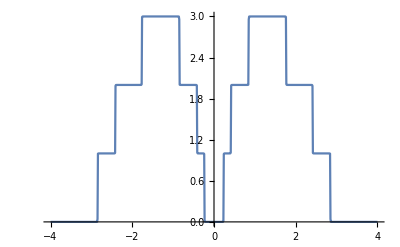

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp5.csv"]
```

{{0.,0.0000280041},{0.01,0.0000271041},{0.02,0.0000244785},{0.03,0.0000256433},{0.04,0.0000307396},{0.05,0.0000418409},{0.06,0.0000499797},{0.07,0.0000781623},{0.08,0.0000889515},{0.09,0.000109198},{0.1,0.000158236},{0.11,0.0001958},{0.12,0.000233421},{0.13,0.0002746},{0.14,0.0003943},{0.15,0.000495431},{0.16,0.000614943},{0.17,0.000822806},{0.18,0.00113338},{0.19,0.00149655},{0.2,0.00217237},{0.21,0.00359214},{0.22,0.00603695},{0.23,0.0150797},{0.24,0.582347},{0.25,0.810022},{0.26,0.88432},{0.27,0.91352},{0.28,0.93294},{0.29,0.946488},{0.3,0.954211},{0.31,0.957821},{0.32,0.96421},{0.33,0.960268},{0.34,0.965069},{0.35,0.96282},{0.36,0.962201},{0.37,0.958638},{0.38,0.954054},{0.39,0.943486},{0.4,0.920744},{0.41,0.805817},{0.42,1.2409},{0.43,1.60311},{0.44,1.7162},{0.45,1.78814},{0.46,1.83033},{0.47,1.85227},{0.48,1.86771},{0.49,1.88922},{0.5,1.8966},{0.51,1.90282},{0.52,1.90936},{0.53,1.91432},{0.54,1.91995},{0.55,1.9207},{0.56,1.92585},{0.57,1.92741},{0.58,1.93151},{0.59,1.93157},{0.6,1.93145},{0.61,1.93383},{0.62,1.93668},{0.63,1.9363},{0.64,1.93882},{0.65,1.93803},{0.66,1.93957},{0.67,1.94063},{0.68,1.94155},{0.69,1.9425},{0.7,1.94224},{0.71,1.94284},{0.72,1.94457},{0.73,1.94276},{0.74,1.94398},{0.75,1.94402},{0.76,1.94428},{0.77,1.94587},{0.78,1.94337},{0.79,1.94122},{0.8,1.93964},{0.81,1.93431},{0.82,1.92453},{0.83,1.90279},{0.84,1.82999},{0.85,1.66142},{0.86,2.35595},{0.87,2.55704},{0.88,2.65906},{0.89,2.7264},{0.9,2.76029},{0.91,2.79586},{0.92,2.82321},{0.93,2.82704},{0.94,2.8473},{0.95,2.86008},{0.96,2.86303},{0.97,2.8818},{0.98,2.88333},{0.99,2.89517},{1.,2.89482},{1.01,2.8853},{1.02,2.88053},{1.03,2.85719},{1.04,2.75831},{1.05,2.48339},{1.06,2.05094},{1.07,2.06183},{1.08,2.27281},{1.09,2.4566},{1.1,2.53709},{1.11,2.59917},{1.12,2.64219},{1.13,2.66807},{1.14,2.68265},{1.15,2.71884},{1.16,2.73416},{1.17,2.7474},{1.18,2.76386},{1.19,2.76794},{1.2,2.77347},{1.21,2.78334},{1.22,2.79455},{1.23,2.79438},{1.24,2.79424},{1.25,2.79944},{1.26,2.79853},{1.27,2.80458},{1.28,2.80764},{1.29,2.80416},{1.3,2.80589},{1.31,2.80457},{1.32,2.80964},{1.33,2.80449},{1.34,2.80415},{1.35,2.80238},{1.36,2.80435},{1.37,2.80207},{1.38,2.79665},{1.39,2.80361},{1.4,2.8039},{1.41,2.7935},{1.42,2.79462},{1.43,2.79622},{1.44,2.79279},{1.45,2.79119},{1.46,2.79352},{1.47,2.78946},{1.48,2.79103},{1.49,2.78168},{1.5,2.77744},{1.51,2.77451},{1.52,2.77599},{1.53,2.76783},{1.54,2.75883},{1.55,2.75561},{1.56,2.74942},{1.57,2.74233},{1.58,2.73689},{1.59,2.7306},{1.6,2.72816},{1.61,2.71888},{1.62,2.70308},{1.63,2.6957},{1.64,2.68191},{1.65,2.6647},{1.66,2.65547},{1.67,2.64081},{1.68,2.60978},{1.69,2.58085},{1.7,2.54404},{1.71,2.49918},{1.72,2.44212},{1.73,2.34496},{1.74,2.23462},{1.75,2.04433},{1.76,1.53394},{1.77,1.56979},{1.78,1.50227},{1.79,1.50935},{1.8,1.57049},{1.81,1.715},{1.82,1.78291},{1.83,1.82432},{1.84,1.85071},{1.85,1.86461},{1.86,1.87401},{1.87,1.8763},{1.88,1.88172},{1.89,1.88535},{1.9,1.89257},{1.91,1.89084},{1.92,1.89101},{1.93,1.89509},{1.94,1.8954},{1.95,1.89586},{1.96,1.8964},{1.97,1.89765},{1.98,1.90011},{1.99,1.89674},{2.,1.90054},{2.01,1.89866},{2.02,1.90114},{2.03,1.89916},{2.04,1.89775},{2.05,1.89687},{2.06,1.8964},{2.07,1.89427},{2.08,1.89545},{2.09,1.89209},{2.1,1.88776},{2.11,1.88899},{2.12,1.88666},{2.13,1.88372},{2.14,1.87977},{2.15,1.87576},{2.16,1.87451},{2.17,1.87081},{2.18,1.86868},{2.19,1.86266},{2.2,1.86715},{2.21,1.86258},{2.22,1.85883},{2.23,1.85353},{2.24,1.84782},{2.25,1.84547},{2.26,1.84161},{2.27,1.83279},{2.28,1.82236},{2.29,1.82235},{2.3,1.80435},{2.31,1.79887},{2.32,1.77431},{2.33,1.75935},{2.34,1.73494},{2.35,1.71314},{2.36,1.6874},{2.37,1.65862},{2.38,1.61455},{2.39,1.55802},{2.4,1.42925},{2.41,1.08218},{2.42,0.903302},{2.43,0.850218},{2.44,0.82199},{2.45,0.805563},{2.46,0.870637},{2.47,0.904931},{2.48,0.919387},{2.49,0.931086},{2.5,0.933819},{2.51,0.939002},{2.52,0.939222},{2.53,0.938745},{2.54,0.93732},{2.55,0.937927},{2.56,0.93687},{2.57,0.936759},{2.58,0.935681},{2.59,0.934594},{2.6,0.932429},{2.61,0.92783},{2.62,0.93129},{2.63,0.930185},{2.64,0.925695},{2.65,0.928704},{2.66,0.930195},{2.67,0.927654},{2.68,0.926096},{2.69,0.921527},{2.7,0.920435},{2.71,0.914534},{2.72,0.909866},{2.73,0.895896},{2.74,0.884929},{2.75,0.876107},{2.76,0.857279},{2.77,0.84547},{2.78,0.831342},{2.79,0.825039},{2.8,0.800514},{2.81,0.789436},{2.82,0.765327},{2.83,0.710711},{2.84,0.586573},{2.85,0.147221},{2.86,0.188793},{2.87,0.0761695},{2.88,0.0137084},{2.89,0.00586121},{2.9,0.00395579},{2.91,0.00215834},{2.92,0.00153286},{2.93,0.00117745},{2.94,0.00105163},{2.95,0.000907934},{2.96,0.000669121},{2.97,0.000482489},{2.98,0.000322438},{2.99,0.000369395},{3.,0.000246256},{3.01,0.000265673},{3.02,0.000187065},{3.03,0.000194141},{3.04,0.000154096},{3.05,0.000136505},{3.06,0.000111722},{3.07,0.0000906393},{3.08,0.0000964078},{3.09,0.0000818457},{3.1,0.0000831846},{3.11,0.0000551725},{3.12,0.0000508354},{3.13,0.000047588},{3.14,0.0000467376},{3.15,0.0000449686},{3.16,0.0000375377},{3.17,0.0000396881},{3.18,0.0000367664},{3.19,0.0000355479},{3.2,0.0000336519},{3.21,0.0000231312},{3.22,0.0000237097},{3.23,0.0000203213},{3.24,0.0000197199},{3.25,0.0000197988},{3.26,0.0000169225},{3.27,0.0000196369},{3.28,0.0000148152},{3.29,0.0000129149},{3.3,0.0000130505},{3.31,0.0000128878},{3.32,9.8351×10^-6},{3.33,0.000010206},{3.34,0.000010106},{3.35,7.70287×10^-6},{3.36,0.0000103926},{3.37,8.66435×10^-6},{3.38,8.37251×10^-6},{3.39,6.22236×10^-6},{3.4,7.54407×10^-6},{3.41,7.59031×10^-6},{3.42,5.39361×10^-6},{3.43,5.73041×10^-6},{3.44,4.91338×10^-6},{3.45,4.24231×10^-6},{3.46,5.23617×10^-6},{3.47,4.86375×10^-6},{3.48,4.19563×10^-6},{3.49,3.97793×10^-6},{3.5,3.1561×10^-6},{3.51,3.57903×10^-6},{3.52,2.59571×10^-6},{3.53,3.4168×10^-6},{3.54,3.50669×10^-6},{3.55,2.77697×10^-6},{3.56,2.40575×10^-6},{3.57,2.05238×10^-6},{3.58,2.51356×10^-6},{3.59,2.57731×10^-6},{3.6,2.34035×10^-6},{3.61,1.918×10^-6},{3.62,2.1886×10^-6},{3.63,1.97904×10^-6},{3.64,1.70277×10^-6},{3.65,1.82215×10^-6},{3.66,1.91299×10^-6},{3.67,1.49176×10^-6},{3.68,1.68201×10^-6},{3.69,1.65398×10^-6},{3.7,1.49939×10^-6},{3.71,1.18985×10^-6},{3.72,1.23162×10^-6},{3.73,1.22124×10^-6},{3.74,1.07321×10^-6},{3.75,1.18651×10^-6},{3.76,1.08064×10^-6},{3.77,1.08542×10^-6},{3.78,1.06576×10^-6},{3.79,1.03758×10^-6},{3.8,8.966×10^-7},{3.81,1.03629×10^-6},{3.82,8.98829×10^-7},{3.83,9.3996×10^-7},{3.84,8.54693×10^-7},{3.85,7.39794×10^-7},{3.86,6.96629×10^-7},{3.87,8.63032×10^-7},{3.88,5.77256×10^-7},{3.89,6.32785×10^-7},{3.9,5.72072×10^-7},{3.91,5.28838×10^-7},{3.92,5.48202×10^-7},{3.93,5.28201×10^-7},{3.94,5.45658×10^-7},{3.95,5.88067×10^-7},{3.96,5.73572×10^-7},{3.97,4.38817×10^-7},{3.98,5.18348×10^-7},{3.99,5.29546×10^-7},{4.,4.69163×10^-7}}

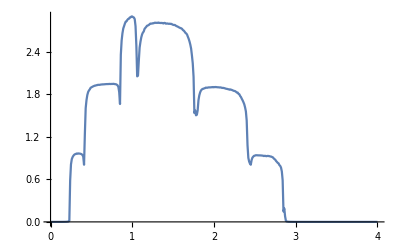

```mathematica
ListPlot[%7,Joined->True]
```

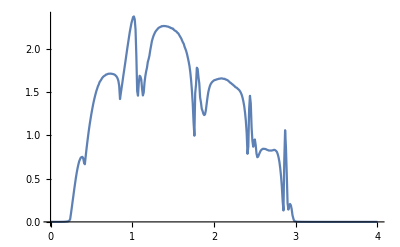

```mathematica
ListPlot[%5,Joined->True]
```

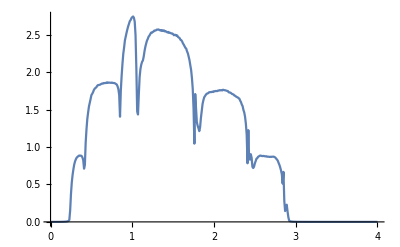

```mathematica
ListPlot[%3,Joined->True]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000283863},{0.01,0.000022274},{0.02,3.72584×10^-6},{0.03,0.0000272619},{0.04,0.0000710154},{0.05,0.000128198},{0.06,0.000199845},{0.07,0.00028742},{0.08,0.000392896},{0.09,0.000518886},{0.1,0.000668813},{0.11,0.000847174},{0.12,0.00105991},{0.13,0.00131499},{0.14,0.00162325},{0.15,0.00199983},{0.16,0.00246647},{0.17,0.00305563},{0.18,0.00381817},{0.19,0.00483907},{0.2,0.00627353},{0.21,0.00844449},{0.22,0.0121823},{0.23,0.0206827},{0.24,0.150661},{0.25,0.451761},{0.26,0.670688},{0.27,0.813617},{0.28,0.899412},{0.29,0.946994},{0.3,0.970817},{0.31,0.980629},{0.32,0.982572},{0.33,0.98032},{0.34,0.975934},{0.35,0.970391},{0.36,0.96387},{0.37,0.955781},{0.38,0.944409},{0.39,0.925482},{0.4,0.88577},{0.41,0.746829},{0.42,0.784814},{0.43,1.20575},{0.44,1.40853},{0.45,1.52916},{0.46,1.60989},{0.47,1.66771},{0.48,1.71074},{0.49,1.7434},{0.5,1.76834},{0.51,1.78731},{0.52,1.80155},{0.53,1.81202},{0.54,1.81951},{0.55,1.82468},{0.56,1.82811},{0.57,1.83029},{0.58,1.83166},{0.59,1.83258},{0.6,1.83338},{0.61,1.8343},{0.62,1.83556},{0.63,1.83729},{0.64,1.83961},{0.65,1.84257},{0.66,1.84618},{0.67,1.85041},{0.68,1.85518},{0.69,1.86039},{0.7,1.86588},{0.71,1.87146},{0.72,1.87693},{0.73,1.88205},{0.74,1.88654},{0.75,1.89014},{0.76,1.89256},{0.77,1.89353},{0.78,1.89273},{0.79,1.88982},{0.8,1.88434},{0.81,1.87549},{0.82,1.8616},{0.83,1.83815},{0.84,1.78658},{0.85,1.69393},{0.86,2.0707},{0.87,2.32157},{0.88,2.48716},{0.89,2.59087},{0.9,2.64982},{0.91,2.67785},{0.92,2.68597},{0.93,2.68252},{0.94,2.67354},{0.95,2.66325},{0.96,2.65452},{0.97,2.64927},{0.98,2.64878},{0.99,2.65378},{1.,2.66427},{1.01,2.67843},{1.02,2.68894},{1.03,2.67064},{1.04,2.54372},{1.05,2.1181},{1.06,1.28319},{1.07,1.30409},{1.08,1.70514},{1.09,1.94174},{1.1,2.09311},{1.11,2.20286},{1.12,2.29013},{1.13,2.3642},{1.14,2.42989},{1.15,2.48969},{1.16,2.54479},{1.17,2.59557},{1.18,2.6419},{1.19,2.68336},{1.2,2.7194},{1.21,2.74944},{1.22,2.77302},{1.23,2.78987},{1.24,2.79994},{1.25,2.80342},{1.26,2.80071},{1.27,2.7924},{1.28,2.77918},{1.29,2.76182},{1.3,2.7411},{1.31,2.71778},{1.32,2.69259},{1.33,2.66621},{1.34,2.63926},{1.35,2.6123},{1.36,2.58585},{1.37,2.56037},{1.38,2.53624},{1.39,2.51379},{1.4,2.49331},{1.41,2.475},{1.42,2.459},{1.43,2.44541},{1.44,2.4343},{1.45,2.42571},{1.46,2.41967},{1.47,2.41625},{1.48,2.41551},{1.49,2.41759},{1.5,2.42265},{1.51,2.4309},{1.52,2.44257},{1.53,2.45784},{1.54,2.47676},{1.55,2.49908},{1.56,2.52402},{1.57,2.55002},{1.58,2.57461},{1.59,2.59444},{1.6,2.60582},{1.61,2.60573},{1.62,2.5928},{1.63,2.56784},{1.64,2.5336},{1.65,2.4938},{1.66,2.45226},{1.67,2.41235},{1.68,2.3768},{1.69,2.3478},{1.7,2.32675},{1.71,2.31267},{1.72,2.29708},{1.73,2.25285},{1.74,2.11999},{1.75,1.77589},{1.76,0.599501},{1.77,3},{1.78,0.629275},{1.79,0.868629},{1.8,1.89523},{1.81,1.39042},{1.82,1.73967},{1.83,1.79967},{1.84,1.81236},{1.85,1.81167},{1.86,1.80575},{1.87,1.79743},{1.88,1.78802},{1.89,1.77825},{1.9,1.7686},{1.91,1.75942},{1.92,1.75098},{1.93,1.74347},{1.94,1.73706},{1.95,1.73187},{1.96,1.72801},{1.97,1.72556},{1.98,1.72457},{1.99,1.72509},{2.,1.72715},{2.01,1.73074},{2.02,1.73587},{2.03,1.74249},{2.04,1.75055},{2.05,1.75998},{2.06,1.77065},{2.07,1.78245},{2.08,1.79518},{2.09,1.80865},{2.1,1.82261},{2.11,1.83677},{2.12,1.85083},{2.13,1.86443},{2.14,1.87718},{2.15,1.88866},{2.16,1.8984},{2.17,1.90591},{2.18,1.91065},{2.19,1.91204},{2.2,1.90947},{2.21,1.90228},{2.22,1.88983},{2.23,1.87152},{2.24,1.84686},{2.25,1.81556},{2.26,1.77764},{2.27,1.73352},{2.28,1.68405},{2.29,1.63049},{2.3,1.57441},{2.31,1.51751},{2.32,1.46137},{2.33,1.40725},{2.34,1.35587},{2.35,1.30721},{2.36,1.26036},{2.37,1.21296},{2.38,1.15999},{2.39,1.08941},{2.4,0.963023},{2.41,0.535603},{2.42,3},{2.43,0.735743},{2.44,2.72777},{2.45,0.129511},{2.46,0.420718},{2.47,0.63861},{2.48,0.750696},{2.49,0.816143},{2.5,0.856469},{2.51,0.881188},{2.52,0.895139},{2.53,0.901118},{2.54,0.900967},{2.55,0.896072},{2.56,0.887608},{2.57,0.876646},{2.58,0.864205},{2.59,0.851264},{2.6,0.838766},{2.61,0.827608},{2.62,0.81864},{2.63,0.812655},{2.64,0.810385},{2.65,0.812477},{2.66,0.819446},{2.67,0.83158},{2.68,0.848771},{2.69,0.870225},{2.7,0.894042},{2.71,0.916717},{2.72,0.932767},{2.73,0.934989},{2.74,0.915908},{2.75,0.8705},{2.76,0.798889},{2.77,0.706853},{2.78,0.603279},{2.79,0.49617},{2.8,0.389439},{2.81,0.280655},{2.82,0.156461},{2.83,0.0292273},{2.84,0.540819},{2.85,3},{2.86,0.469761},{2.87,0.150732},{2.88,0.0665393},{2.89,0.105598},{2.9,0.0403375},{2.91,0.0258867},{2.92,0.0184314},{2.93,0.0137899},{2.94,0.0106592},{2.95,0.00844056},{2.96,0.0068116},{2.97,0.00558249},{2.98,0.00463449},{2.99,0.00388988},{3.,0.00329595},{3.01,0.0028159},{3.02,0.00242341},{3.03,0.00209924},{3.04,0.00182908},{3.05,0.00160212},{3.06,0.00141006},{3.07,0.00124647},{3.08,0.00110629},{3.09,0.000985522},{3.1,0.000880945},{3.11,0.000789972},{3.12,0.000710491},{3.13,0.000640775},{3.14,0.000579396},{3.15,0.00052517},{3.16,0.000477107},{3.17,0.000434377},{3.18,0.000396279},{3.19,0.000362219},{3.2,0.000331691},{3.21,0.000304263},{3.22,0.000279563},{3.23,0.000257272},{3.24,0.000237113},{3.25,0.000218846},{3.26,0.000202263},{3.27,0.000187181},{3.28,0.00017344},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120513},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980556},{3.37,0.0000917086},{3.38,0.0000858463},{3.39,0.0000804257},{3.4,0.000075408},{3.41,0.0000707586},{3.42,0.000066446},{3.43,0.000062442},{3.44,0.000058721},{3.45,0.0000552598},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436215},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
ListPlot[%427,Joined->True]
```

ListPlot::lpn: %427 is not a list of numbers or pairs of numbers.

ListPlot[%427,Joined→True]

```mathematica
ListPlot[%74,Joined->True]
```

ListPlot::lpn: %74 is not a list of numbers or pairs of numbers.

ListPlot[%74,Joined→True]

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000271339},{0.01,0.0000245906},{0.02,5.39315×10^-6},{0.03,0.0000303963},{0.04,0.0000832576},{0.05,0.000154239},{0.06,0.000245023},{0.07,0.000358035},{0.08,0.000496624},{0.09,0.00066531},{0.1,0.000870174},{0.11,0.00111941},{0.12,0.0014242},{0.13,0.0018},{0.14,0.00226864},{0.15,0.00286178},{0.16,0.00362683},{0.17,0.0046377},{0.18,0.00601573},{0.19,0.00797389},{0.2,0.0109219},{0.21,0.0157613},{0.22,0.0249721},{0.23,0.0496347},{0.24,0.0320927},{0.25,0.272093},{0.26,0.468393},{0.27,0.60836},{0.28,0.697859},{0.29,0.750147},{0.3,0.778174},{0.31,0.791766},{0.32,0.79754},{0.33,0.799671},{0.34,0.80069},{0.35,0.802078},{0.36,0.804653},{0.37,0.808803},{0.38,0.814586},{0.39,0.821644},{0.4,0.828411},{0.41,0.824141},{0.42,1.10485},{0.43,1.38356},{0.44,1.51408},{0.45,1.5895},{0.46,1.63903},{0.47,1.67443},{0.48,1.70126},{0.49,1.72241},{0.5,1.7395},{0.51,1.75353},{0.52,1.76514},{0.53,1.7748},{0.54,1.78286},{0.55,1.78964},{0.56,1.79541},{0.57,1.80045},{0.58,1.80499},{0.59,1.80928},{0.6,1.81353},{0.61,1.81792},{0.62,1.82264},{0.63,1.82781},{0.64,1.83353},{0.65,1.83988},{0.66,1.84689},{0.67,1.85454},{0.68,1.8628},{0.69,1.87156},{0.7,1.88071},{0.71,1.89005},{0.72,1.89938},{0.73,1.90844},{0.74,1.91693},{0.75,1.92454},{0.76,1.93091},{0.77,1.93566},{0.78,1.93839},{0.79,1.93862},{0.8,1.93573},{0.81,1.92868},{0.82,1.91529},{0.83,1.88939},{0.84,1.82369},{0.85,1.67219},{0.86,2.16578},{0.87,2.40673},{0.88,2.53367},{0.89,2.60034},{0.9,2.63277},{0.91,2.64559},{0.92,2.64765},{0.93,2.64453},{0.94,2.63981},{0.95,2.63583},{0.96,2.63412},{0.97,2.63569},{0.98,2.64117},{0.99,2.65076},{1.,2.66367},{1.01,2.67627},{1.02,2.67537},{1.03,2.61688},{1.04,2.39629},{1.05,2.03031},{1.06,1.79496},{1.07,1.59935},{1.08,1.83194},{1.09,2.25211},{1.1,2.44202},{1.11,2.54551},{1.12,2.61861},{1.13,2.67768},{1.14,2.72797},{1.15,2.77103},{1.16,2.8069},{1.17,2.835},{1.18,2.85466},{1.19,2.86536},{1.2,2.86698},{1.21,2.85985},{1.22,2.84478},{1.23,2.82296},{1.24,2.79581},{1.25,2.76487},{1.26,2.73161},{1.27,2.69739},{1.28,2.66337},{1.29,2.63051},{1.3,2.59955},{1.31,2.57106},{1.32,2.54546},{1.33,2.52301},{1.34,2.50392},{1.35,2.48826},{1.36,2.47607},{1.37,2.46731},{1.38,2.46189},{1.39,2.45969},{1.4,2.46055},{1.41,2.46427},{1.42,2.47064},{1.43,2.47945},{1.44,2.49046},{1.45,2.50345},{1.46,2.51822},{1.47,2.53452},{1.48,2.55205},{1.49,2.57042},{1.5,2.58902},{1.51,2.6069},{1.52,2.62265},{1.53,2.63427},{1.54,2.63917},{1.55,2.63437},{1.56,2.61704},{1.57,2.58533},{1.58,2.53917},{1.59,2.4807},{1.6,2.4138},{1.61,2.34318},{1.62,2.2731},{1.63,2.20672},{1.64,2.14576},{1.65,2.09072},{1.66,2.04118},{1.67,1.99608},{1.68,1.95397},{1.69,1.91307},{1.7,1.87129},{1.71,1.82625},{1.72,1.77501},{1.73,1.71267},{1.74,1.62435},{1.75,1.44482},{1.76,0.742216},{1.77,3},{1.78,0.262802},{1.79,1.10237},{1.8,1.32767},{1.81,1.3288},{1.82,0.464436},{1.83,1.0451},{1.84,1.3614},{1.85,1.46942},{1.86,1.52685},{1.87,1.56569},{1.88,1.59596},{1.89,1.62184},{1.9,1.64538},{1.91,1.66771},{1.92,1.68948},{1.93,1.71107},{1.94,1.73266},{1.95,1.75429},{1.96,1.7759},{1.97,1.79731},{1.98,1.81825},{1.99,1.83836},{2.,1.85722},{2.01,1.87437},{2.02,1.88928},{2.03,1.90147},{2.04,1.9105},{2.05,1.916},{2.06,1.91774},{2.07,1.91566},{2.08,1.90986},{2.09,1.90062},{2.1,1.88839},{2.11,1.87373},{2.12,1.85731},{2.13,1.83984},{2.14,1.82203},{2.15,1.80458},{2.16,1.78811},{2.17,1.7732},{2.18,1.76032},{2.19,1.74989},{2.2,1.74219},{2.21,1.73744},{2.22,1.73569},{2.23,1.73684},{2.24,1.74059},{2.25,1.74633},{2.26,1.75305},{2.27,1.75928},{2.28,1.76303},{2.29,1.7618},{2.3,1.75289},{2.31,1.73377},{2.32,1.70268},{2.33,1.65913},{2.34,1.60397},{2.35,1.53884},{2.36,1.46512},{2.37,1.38222},{2.38,1.28476},{2.39,1.15466},{2.4,0.925748},{2.41,0.0900363},{2.42,0.71046},{2.43,0.462149},{2.44,3},{2.45,0.417055},{2.46,0.298546},{2.47,0.564421},{2.48,0.702546},{2.49,0.78612},{2.5,0.840191},{2.51,0.875425},{2.52,0.897097},{2.53,0.908214},{2.54,0.910789},{2.55,0.906415},{2.56,0.896529},{2.57,0.882512},{2.58,0.865723},{2.59,0.847476},{2.6,0.829026},{2.61,0.811539},{2.62,0.79609},{2.63,0.783658},{2.64,0.775139},{2.65,0.771352},{2.66,0.773045},{2.67,0.780858},{2.68,0.795248},{2.69,0.816301},{2.7,0.843415},{2.71,0.87478},{2.72,0.906712},{2.73,0.933096},{2.74,0.945561},{2.75,0.935224},{2.76,0.896094},{2.77,0.828369},{2.78,0.738782},{2.79,0.637177},{2.8,0.531644},{2.81,0.424551},{2.82,0.30786},{2.83,0.144479},{2.84,0.299146},{2.85,3},{2.86,0.214006},{2.87,0.961749},{2.88,0.118583},{2.89,0.0597359},{2.9,0.0370425},{2.91,0.0252628},{2.92,0.018256},{2.93,0.0137301},{2.94,0.0106363},{2.95,0.00843109},{2.96,0.00680748},{2.97,0.00558064},{2.98,0.00463365},{2.99,0.0038895},{3.,0.00329578},{3.01,0.00281583},{3.02,0.00242339},{3.03,0.00209924},{3.04,0.00182909},{3.05,0.00160213},{3.06,0.00141007},{3.07,0.00124648},{3.08,0.0011063},{3.09,0.000985529},{3.1,0.000880951},{3.11,0.000789976},{3.12,0.000710494},{3.13,0.000640777},{3.14,0.000579398},{3.15,0.000525171},{3.16,0.000477108},{3.17,0.000434378},{3.18,0.00039628},{3.19,0.00036222},{3.2,0.000331692},{3.21,0.000304263},{3.22,0.000279564},{3.23,0.000257272},{3.24,0.000237113},{3.25,0.000218846},{3.26,0.000202263},{3.27,0.000187181},{3.28,0.00017344},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120513},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980556},{3.37,0.0000917086},{3.38,0.0000858463},{3.39,0.0000804257},{3.4,0.000075408},{3.41,0.0000707586},{3.42,0.000066446},{3.43,0.000062442},{3.44,0.000058721},{3.45,0.0000552598},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436215},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
ListPlot[%78,Joined->True,PlotStyle->RGBColor[0.27,0.61,0.39]]
```

ListPlot::lpn: %78 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[%78,Joined→True,PlotStyle→RGBColor[0.27, 0.61, 0.39]]

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000021395},{0.01,0.0000274771},{0.02,0.0000254173},{0.03,0.0000153003},{0.04,3.0927×10^-6},{0.05,0.0000303008},{0.06,0.0000672245},{0.07,0.000115197},{0.08,0.000176094},{0.09,0.0002525},{0.1,0.000347961},{0.11,0.000467357},{0.12,0.000617494},{0.13,0.000808024},{0.14,0.00105297},{0.15,0.00137328},{0.16,0.0018015},{0.17,0.00239052},{0.18,0.0032316},{0.19,0.00449529},{0.2,0.00653754},{0.21,0.0102361},{0.22,0.0184705},{0.23,0.0493689},{0.24,0.600966},{0.25,0.84065},{0.26,0.902053},{0.27,0.929182},{0.28,0.944037},{0.29,0.953093},{0.3,0.958907},{0.31,0.962673},{0.32,0.964996},{0.33,0.966184},{0.34,0.966361},{0.35,0.965505},{0.36,0.963427},{0.37,0.959669},{0.38,0.953238},{0.39,0.941764},{0.4,0.918151},{0.41,0.844605},{0.42,0.912366},{0.43,1.23682},{0.44,1.44673},{0.45,1.58742},{0.46,1.68471},{0.47,1.75353},{0.48,1.80302},{0.49,1.83904},{0.5,1.86548},{0.51,1.885},{0.52,1.89946},{0.53,1.9102},{0.54,1.91818},{0.55,1.92411},{0.56,1.9285},{0.57,1.93176},{0.58,1.93418},{0.59,1.93597},{0.6,1.93731},{0.61,1.93832},{0.62,1.93909},{0.63,1.93969},{0.64,1.94017},{0.65,1.94058},{0.66,1.94093},{0.67,1.94124},{0.68,1.94152},{0.69,1.94178},{0.7,1.94201},{0.71,1.94221},{0.72,1.94237},{0.73,1.94248},{0.74,1.94252},{0.75,1.94246},{0.76,1.94227},{0.77,1.9419},{0.78,1.94125},{0.79,1.94018},{0.8,1.93842},{0.81,1.93544},{0.82,1.93008},{0.83,1.91927},{0.84,1.89116},{0.85,1.80502},{0.86,1.93629},{0.87,2.07536},{0.88,2.20869},{0.89,2.32583},{0.9,2.42063},{0.91,2.49227},{0.92,2.5436},{0.93,2.57907},{0.94,2.60316},{0.95,2.61972},{0.96,2.63174},{0.97,2.6415},{0.98,2.65074},{0.99,2.66084},{1.,2.67297},{1.01,2.68817},{1.02,2.70683},{1.03,2.72567},{1.04,2.71886},{1.05,2.53184},{1.06,1.93423},{1.07,1.8043},{1.08,1.87081},{1.09,1.79127},{1.1,1.6392},{1.11,1.95892},{1.12,2.35534},{1.13,2.5221},{1.14,2.59474},{1.15,2.63469},{1.16,2.66154},{1.17,2.68223},{1.18,2.69952},{1.19,2.71467},{1.2,2.72828},{1.21,2.74067},{1.22,2.75203},{1.23,2.76247},{1.24,2.77206},{1.25,2.78088},{1.26,2.78899},{1.27,2.79645},{1.28,2.80331},{1.29,2.80962},{1.3,2.81544},{1.31,2.82081},{1.32,2.82576},{1.33,2.83033},{1.34,2.83453},{1.35,2.83834},{1.36,2.84175},{1.37,2.84472},{1.38,2.84717},{1.39,2.84904},{1.4,2.85022},{1.41,2.85059},{1.42,2.85003},{1.43,2.84839},{1.44,2.84555},{1.45,2.84136},{1.46,2.83573},{1.47,2.82856},{1.48,2.81979},{1.49,2.80943},{1.5,2.7975},{1.51,2.7841},{1.52,2.76937},{1.53,2.75351},{1.54,2.73675},{1.55,2.71938},{1.56,2.70172},{1.57,2.6841},{1.58,2.66686},{1.59,2.65038},{1.6,2.635},{1.61,2.62111},{1.62,2.60907},{1.63,2.59924},{1.64,2.59202},{1.65,2.58779},{1.66,2.58695},{1.67,2.58989},{1.68,2.59699},{1.69,2.60853},{1.7,2.62459},{1.71,2.64476},{1.72,2.66751},{1.73,2.68828},{1.74,2.69304},{1.75,2.62756},{1.76,2.14556},{1.77,3},{1.78,1.37366},{1.79,1.76381},{1.8,1.81968},{1.81,1.83767},{1.82,1.84597},{1.83,1.85055},{1.84,1.85327},{1.85,1.85485},{1.86,1.85567},{1.87,1.8559},{1.88,1.85567},{1.89,1.85504},{1.9,1.85406},{1.91,1.85278},{1.92,1.8512},{1.93,1.84936},{1.94,1.84725},{1.95,1.84489},{1.96,1.84229},{1.97,1.83942},{1.98,1.8363},{1.99,1.83291},{2.,1.82923},{2.01,1.82526},{2.02,1.82095},{2.03,1.81631},{2.04,1.81128},{2.05,1.80586},{2.06,1.79999},{2.07,1.79365},{2.08,1.78681},{2.09,1.77942},{2.1,1.77145},{2.11,1.76287},{2.12,1.75363},{2.13,1.74369},{2.14,1.733},{2.15,1.72151},{2.16,1.70916},{2.17,1.69587},{2.18,1.68156},{2.19,1.6661},{2.2,1.64938},{2.21,1.63123},{2.22,1.61147},{2.23,1.58987},{2.24,1.5662},{2.25,1.54019},{2.26,1.51156},{2.27,1.48004},{2.28,1.44536},{2.29,1.40729},{2.3,1.36566},{2.31,1.32034},{2.32,1.27125},{2.33,1.2183},{2.34,1.16122},{2.35,1.09933},{2.36,1.03089},{2.37,0.951737},{2.38,0.851825},{2.39,0.703793},{2.4,0.410312},{2.41,0.756214},{2.42,1.47493},{2.43,0.494598},{2.44,0.720654},{2.45,0.618864},{2.46,0.791322},{2.47,0.817044},{2.48,0.812779},{2.49,0.796764},{2.5,0.775412},{2.51,0.751829},{2.52,0.727812},{2.53,0.704516},{2.54,0.68274},{2.55,0.663063},{2.56,0.645923},{2.57,0.631672},{2.58,0.62061},{2.59,0.61302},{2.6,0.60919},{2.61,0.609433},{2.62,0.614111},{2.63,0.623644},{2.64,0.638512},{2.65,0.659243},{2.66,0.686362},{2.67,0.720275},{2.68,0.761035},{2.69,0.807933},{2.7,0.858832},{2.71,0.909285},{2.72,0.951757},{2.73,0.97582},{2.74,0.970534},{2.75,0.9292},{2.76,0.853848},{2.77,0.755313},{2.78,0.648183},{2.79,0.544769},{2.8,0.452048},{2.81,0.371706},{2.82,0.300975},{2.83,0.230975},{2.84,0.129187},{2.85,0.470328},{2.86,0.507384},{2.87,0.0590811},{2.88,0.0186743},{2.89,0.00528776},{2.9,0.0231628},{2.91,0.00650579},{2.92,0.00380167},{2.93,0.00253224},{2.94,0.00179348},{2.95,0.00132055},{2.96,0.000999927},{2.97,0.000773672},{2.98,0.000609106},{2.99,0.0004865},{3.,0.000393338},{3.01,0.000321367},{3.02,0.000264975},{3.03,0.000220243},{3.04,0.000184377},{3.05,0.000155343},{3.06,0.000131638},{3.07,0.000112136},{3.08,0.0000959798},{3.09,0.00008251},{3.1,0.0000712151},{3.11,0.0000616935},{3.12,0.0000536275},{3.13,0.0000467634},{3.14,0.0000408976},{3.15,0.0000358651},{3.16,0.0000315319},{3.17,0.0000277879},{3.18,0.0000245427},{3.19,0.0000217213},{3.2,0.0000192614},{3.21,0.0000171109},{3.22,0.0000152262},{3.23,0.0000135704},{3.24,0.0000121125},{3.25,0.000010826},{3.26,9.6885×10^-6},{3.27,8.68077×10^-6},{3.28,7.78637×10^-6},{3.29,6.99116×10^-6},{3.3,6.28296×10^-6},{3.31,5.65125×10^-6},{3.32,5.08691×10^-6},{3.33,4.58204×10^-6},{3.34,4.12974×10^-6},{3.35,3.72402×10^-6},{3.36,3.35961×10^-6},{3.37,3.03192×10^-6},{3.38,2.73692×10^-6},{3.39,2.47106×10^-6},{3.4,2.23121×10^-6},{3.41,2.01462×10^-6},{3.42,1.81885×10^-6},{3.43,1.64174×10^-6},{3.44,1.48137×10^-6},{3.45,1.33606×10^-6},{3.46,1.20428×10^-6},{3.47,1.0847×10^-6},{3.48,9.76108×10^-7},{3.49,8.77436×10^-7},{3.5,7.87727×10^-7},{3.51,7.06122×10^-7},{3.52,6.31853×10^-7},{3.53,5.64228×10^-7},{3.54,5.02629×10^-7},{3.55,4.46497×10^-7},{3.56,3.95331×10^-7},{3.57,3.48678×10^-7},{3.58,3.06129×10^-7},{3.59,2.67317×10^-7},{3.6,2.31908×10^-7},{3.61,1.99601×10^-7},{3.62,1.70122×10^-7},{3.63,1.43225×10^-7},{3.64,1.18685×10^-7},{3.65,9.62975×10^-8},{3.66,7.58785×10^-8},{3.67,5.72596×10^-8},{3.68,4.02875×10^-8},{3.69,2.4823×10^-8},{3.7,1.07389×10^-8},{3.71,2.08042×10^-9},{3.72,1.37407×10^-8},{3.73,2.43383×10^-8},{3.74,3.39614×10^-8},{3.75,4.26905×10^-8},{3.76,5.05992×10^-8},{3.77,5.77551×10^-8},{3.78,6.42197×10^-8},{3.79,7.00496×10^-8},{3.8,7.52967×10^-8},{3.81,8.00084×10^-8},{3.82,8.42284×10^-8},{3.83,8.79966×10^-8},{3.84,9.13499×10^-8},{3.85,9.43218×10^-8},{3.86,9.69436×10^-8},{3.87,9.92437×10^-8},{3.88,1.01248×10^-7},{3.89,1.02981×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06766×10^-7},{3.93,1.07619×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000285429},{0.01,0.0000262747},{0.02,0.0000193241},{0.03,7.80594×10^-6},{0.04,8.28064×10^-6},{0.05,0.0000290503},{0.06,0.0000547362},{0.07,0.0000857028},{0.08,0.000122467},{0.09,0.000165731},{0.1,0.000216433},{0.11,0.000275817},{0.12,0.000345543},{0.13,0.000427845},{0.14,0.000525784},{0.15,0.000643643},{0.16,0.000787586},{0.17,0.000966804},{0.18,0.00119563},{0.19,0.00149776},{0.2,0.00191558},{0.21,0.00253371},{0.22,0.00355122},{0.23,0.00546637},{0.24,0.120679},{0.25,0.34621},{0.26,0.529545},{0.27,0.664116},{0.28,0.755531},{0.29,0.814029},{0.3,0.849708},{0.31,0.870624},{0.32,0.882556},{0.33,0.889408},{0.34,0.893705},{0.35,0.897017},{0.36,0.900265},{0.37,0.903913},{0.38,0.908078},{0.39,0.91253},{0.4,0.916436},{0.41,0.916974},{0.42,1.25352},{0.43,1.51798},{0.44,1.63721},{0.45,1.70386},{0.46,1.7457},{0.47,1.77372},{0.48,1.79305},{0.49,1.80643},{0.5,1.81547},{0.51,1.82118},{0.52,1.8243},{0.53,1.82538},{0.54,1.82489},{0.55,1.82321},{0.56,1.82072},{0.57,1.81773},{0.58,1.81453},{0.59,1.81139},{0.6,1.80852},{0.61,1.80613},{0.62,1.80437},{0.63,1.80338},{0.64,1.80325},{0.65,1.80404},{0.66,1.8058},{0.67,1.80853},{0.68,1.81221},{0.69,1.81679},{0.7,1.82218},{0.71,1.82827},{0.72,1.83492},{0.73,1.84195},{0.74,1.84913},{0.75,1.85623},{0.76,1.86292},{0.77,1.86884},{0.78,1.87356},{0.79,1.87647},{0.8,1.87674},{0.81,1.87301},{0.82,1.86273},{0.83,1.83986},{0.84,1.78325},{0.85,1.59956},{0.86,1.73933},{0.87,1.84313},{0.88,1.91077},{0.89,1.95291},{0.9,1.97792},{0.91,1.99204},{0.92,1.99974},{0.93,2.00418},{0.94,2.00749},{0.95,2.01108},{0.96,2.01587},{0.97,2.02242},{0.98,2.03106},{0.99,2.04198},{1.,2.05523},{1.01,2.07083},{1.02,2.0887},{1.03,2.10875},{1.04,2.13085},{1.05,2.15479},{1.06,2.18035},{1.07,2.20725},{1.08,2.23516},{1.09,2.26371},{1.1,2.29247},{1.11,2.32099},{1.12,2.34883},{1.13,2.37553},{1.14,2.40069},{1.15,2.42397},{1.16,2.44511},{1.17,2.46398},{1.18,2.48054},{1.19,2.49487},{1.2,2.50716},{1.21,2.51768},{1.22,2.52678},{1.23,2.53484},{1.24,2.54227},{1.25,2.54949},{1.26,2.55691},{1.27,2.56491},{1.28,2.57384},{1.29,2.58399},{1.3,2.59561},{1.31,2.60883},{1.32,2.62371},{1.33,2.64016},{1.34,2.65792},{1.35,2.67653},{1.36,2.69532},{1.37,2.7134},{1.38,2.72968},{1.39,2.74299},{1.4,2.75216},{1.41,2.75625},{1.42,2.75466},{1.43,2.74727},{1.44,2.73445},{1.45,2.71705},{1.46,2.69617},{1.47,2.67308},{1.48,2.64897},{1.49,2.62489},{1.5,2.60162},{1.51,2.57965},{1.52,2.55914},{1.53,2.53992},{1.54,2.52152},{1.55,2.50312},{1.56,2.48362},{1.57,2.4618},{1.58,2.43644},{1.59,2.40671},{1.6,2.37235},{1.61,2.33396},{1.62,2.29286},{1.63,2.25084},{1.64,2.20981},{1.65,2.17141},{1.66,2.13694},{1.67,2.10739},{1.68,2.08362},{1.69,2.06666},{1.7,2.05797},{1.71,2.0596},{1.72,2.07371},{1.73,2.09916},{1.74,2.11854},{1.75,2.05282},{1.76,1.51183},{1.77,3},{1.78,1.34242},{1.79,0.538045},{1.8,2.91192},{1.81,0.493344},{1.82,0.680664},{1.83,1.17933},{1.84,1.42832},{1.85,1.56607},{1.86,1.64604},{1.87,1.6925},{1.88,1.71795},{1.89,1.7295},{1.9,1.73151},{1.91,1.72684},{1.92,1.71749},{1.93,1.7049},{1.94,1.69016},{1.95,1.6741},{1.96,1.65738},{1.97,1.64053},{1.98,1.62398},{1.99,1.60807},{2.,1.59309},{2.01,1.57929},{2.02,1.56688},{2.03,1.55604},{2.04,1.54695},{2.05,1.53976},{2.06,1.53463},{2.07,1.53172},{2.08,1.53121},{2.09,1.53327},{2.1,1.53808},{2.11,1.54585},{2.12,1.55677},{2.13,1.57105},{2.14,1.58884},{2.15,1.61025},{2.16,1.63527},{2.17,1.6637},{2.18,1.69503},{2.19,1.72829},{2.2,1.76193},{2.21,1.79362},{2.22,1.82026},{2.23,1.83809},{2.24,1.84323},{2.25,1.8325},{2.26,1.8043},{2.27,1.75936},{2.28,1.70067},{2.29,1.63277},{2.3,1.56061},{2.31,1.48846},{2.32,1.41929},{2.33,1.35458},{2.34,1.29438},{2.35,1.23741},{2.36,1.18089},{2.37,1.11972},{2.38,1.04388},{2.39,0.929886},{2.4,0.703051},{2.41,0.114602},{2.42,1.22436},{2.43,0.270284},{2.44,0.0828382},{2.45,0.554043},{2.46,0.67079},{2.47,0.73965},{2.48,0.789536},{2.49,0.829379},{2.5,0.86266},{2.51,0.8907},{2.52,0.913796},{2.53,0.931739},{2.54,0.944118},{2.55,0.950527},{2.56,0.95073},{2.57,0.944774},{2.58,0.933046},{2.59,0.916273},{2.6,0.895462},{2.61,0.87181},{2.62,0.846599},{2.63,0.821094},{2.64,0.796477},{2.65,0.773807},{2.66,0.754002},{2.67,0.737859},{2.68,0.726074},{2.69,0.719277},{2.7,0.718049},{2.71,0.722938},{2.72,0.734417},{2.73,0.752796},{2.74,0.778011},{2.75,0.809256},{2.76,0.844413},{2.77,0.879356},{2.78,0.907482},{2.79,0.92019},{2.8,0.909044},{2.81,0.869035},{2.82,0.799917},{2.83,0.699757},{2.84,0.519529},{2.85,3},{2.86,0.0396464},{2.87,0.000650282},{2.88,0.343155},{2.89,1.64862},{2.9,0.195787},{2.91,0.0821514},{2.92,0.0470194},{2.93,0.0309221},{2.94,0.0220006},{2.95,0.0164688},{2.96,0.0127752},{2.97,0.0101761},{2.98,0.00827388},{2.99,0.00683868},{3.,0.0057291},{3.01,0.00485399},{3.02,0.0041522},{3.03,0.00358139},{3.04,0.00311144},{3.05,0.00272043},{3.06,0.00239205},{3.07,0.002114},{3.08,0.00187684},{3.09,0.00167321},{3.1,0.00149733},{3.11,0.00134459},{3.12,0.00121129},{3.13,0.00109444},{3.14,0.00099156},{3.15,0.000900643},{3.16,0.000820008},{3.17,0.000748255},{3.18,0.000684205},{3.19,0.000626867},{3.2,0.000575397},{3.21,0.000529077},{3.22,0.00048729},{3.23,0.000449508},{3.24,0.000415273},{3.25,0.00038419},{3.26,0.000355913},{3.27,0.000330142},{3.28,0.000306614},{3.29,0.000285098},{3.3,0.000265391},{3.31,0.000247314},{3.32,0.000230707},{3.33,0.00021543},{3.34,0.000201357},{3.35,0.000188378},{3.36,0.000176392},{3.37,0.000165311},{3.38,0.000155054},{3.39,0.00014555},{3.4,0.000136734},{3.41,0.000128548},{3.42,0.00012094},{3.43,0.000113862},{3.44,0.000107272},{3.45,0.000101129},{3.46,0.0000953997},{3.47,0.0000900506},{3.48,0.0000850529},{3.49,0.0000803798},{3.5,0.0000760068},{3.51,0.0000719117},{3.52,0.0000680741},{3.53,0.0000644752},{3.54,0.000061098},{3.55,0.0000579267},{3.56,0.0000549468},{3.57,0.000052145},{3.58,0.0000495092},{3.59,0.0000470279},{3.6,0.0000446907},{3.61,0.0000424882},{3.62,0.0000404112},{3.63,0.0000384518},{3.64,0.0000366021},{3.65,0.0000348552},{3.66,0.0000332046},{3.67,0.0000316441},{3.68,0.0000301682},{3.69,0.0000287716},{3.7,0.0000274494},{3.71,0.0000261971},{3.72,0.0000250105},{3.73,0.0000238857},{3.74,0.000022819},{3.75,0.0000218069},{3.76,0.0000208464},{3.77,0.0000199343},{3.78,0.000019068},{3.79,0.0000182447},{3.8,0.0000174622},{3.81,0.000016718},{3.82,0.0000160101},{3.83,0.0000153365},{3.84,0.0000146952},{3.85,0.0000140845},{3.86,0.0000135028},{3.87,0.0000129485},{3.88,0.0000124201},{3.89,0.0000119162},{3.9,0.0000114356},{3.91,0.0000109771},{3.92,0.0000105395},{3.93,0.0000101217},{3.94,9.72277×10^-6},{3.95,9.34167×10^-6},{3.96,8.97752×10^-6},{3.97,8.62948×10^-6},{3.98,8.29674×10^-6},{3.99,7.97854×10^-6},{4.,7.67416×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000025594},{0.01,0.000026983},{0.02,0.0000161605},{0.03,6.82041×10^-6},{0.04,0.0000424381},{0.05,0.0000917328},{0.06,0.000156383},{0.07,0.000238835},{0.08,0.000342516},{0.09,0.000472136},{0.1,0.000634164},{0.11,0.000837536},{0.12,0.00109475},{0.13,0.00142358},{0.14,0.00184996},{0.15,0.0024127},{0.16,0.0031721},{0.17,0.00422595},{0.18,0.00574215},{0.19,0.00803111},{0.2,0.0117295},{0.21,0.0183623},{0.22,0.0326937},{0.23,0.0822139},{0.24,0.24754},{0.25,0.579034},{0.26,0.697978},{0.27,0.757482},{0.28,0.792386},{0.29,0.814662},{0.3,0.829439},{0.31,0.839204},{0.32,0.845209},{0.33,0.848018},{0.34,0.847715},{0.35,0.843924},{0.36,0.835662},{0.37,0.820902},{0.38,0.795436},{0.39,0.749496},{0.4,0.654493},{0.41,0.365527},{0.42,0.214581},{0.43,0.711363},{0.44,1.04697},{0.45,1.29086},{0.46,1.47239},{0.47,1.60813},{0.48,1.70914},{0.49,1.78351},{0.5,1.83739},{0.51,1.87559},{0.52,1.90185},{0.53,1.91909},{0.54,1.92958},{0.55,1.9351},{0.56,1.93702},{0.57,1.93638},{0.58,1.93399},{0.59,1.93048},{0.6,1.9263},{0.61,1.9218},{0.62,1.91724},{0.63,1.9128},{0.64,1.90863},{0.65,1.90482},{0.66,1.90141},{0.67,1.89844},{0.68,1.89591},{0.69,1.89383},{0.7,1.89218},{0.71,1.89091},{0.72,1.89},{0.73,1.8894},{0.74,1.88905},{0.75,1.88891},{0.76,1.88891},{0.77,1.88898},{0.78,1.88903},{0.79,1.88898},{0.8,1.88867},{0.81,1.88788},{0.82,1.88618},{0.83,1.88244},{0.84,1.87245},{0.85,1.92438},{0.86,2.30143},{0.87,2.52396},{0.88,2.63346},{0.89,2.68297},{0.9,2.70532},{0.91,2.71752},{0.92,2.7278},{0.93,2.74001},{0.94,2.75581},{0.95,2.77576},{0.96,2.79967},{0.97,2.8267},{0.98,2.8551},{0.99,2.88148},{1.,2.89947},{1.01,2.89716},{1.02,2.85317},{1.03,2.73303},{1.04,2.49429},{1.05,2.13922},{1.06,1.39006},{1.07,0.903243},{1.08,1.37906},{1.09,1.7194},{1.1,1.95259},{1.11,2.13127},{1.12,2.27541},{1.13,2.39437},{1.14,2.49352},{1.15,2.57628},{1.16,2.64497},{1.17,2.70122},{1.18,2.74625},{1.19,2.78112},{1.2,2.80676},{1.21,2.8241},{1.22,2.83404},{1.23,2.83754},{1.24,2.83552},{1.25,2.8289},{1.26,2.81855},{1.27,2.8053},{1.28,2.7899},{1.29,2.77303},{1.3,2.75526},{1.31,2.73712},{1.32,2.71904},{1.33,2.70138},{1.34,2.68444},{1.35,2.66847},{1.36,2.65365},{1.37,2.64013},{1.38,2.62802},{1.39,2.61736},{1.4,2.60821},{1.41,2.60054},{1.42,2.59433},{1.43,2.58949},{1.44,2.58594},{1.45,2.58351},{1.46,2.58204},{1.47,2.5813},{1.48,2.58105},{1.49,2.581},{1.5,2.58084},{1.51,2.58024},{1.52,2.57885},{1.53,2.57633},{1.54,2.57237},{1.55,2.56669},{1.56,2.55907},{1.57,2.54937},{1.58,2.53753},{1.59,2.52359},{1.6,2.50768},{1.61,2.49002},{1.62,2.47091},{1.63,2.45069},{1.64,2.42977},{1.65,2.40855},{1.66,2.38747},{1.67,2.36694},{1.68,2.34734},{1.69,2.32901},{1.7,2.31215},{1.71,2.29676},{1.72,2.28227},{1.73,2.26663},{1.74,2.24289},{1.75,2.18246},{1.76,1.86652},{1.77,0.992901},{1.78,1.06581},{1.79,1.17949},{1.8,1.27716},{1.81,1.58504},{1.82,1.67236},{1.83,1.7079},{1.84,1.7258},{1.85,1.73656},{1.86,1.74427},{1.87,1.75082},{1.88,1.75718},{1.89,1.76391},{1.9,1.77131},{1.91,1.77956},{1.92,1.78876},{1.93,1.79891},{1.94,1.80995},{1.95,1.82178},{1.96,1.83418},{1.97,1.8469},{1.98,1.85958},{1.99,1.87176},{2.,1.88295},{2.01,1.89255},{2.02,1.89992},{2.03,1.90444},{2.04,1.90551},{2.05,1.90262},{2.06,1.89541},{2.07,1.88371},{2.08,1.86759},{2.09,1.84731},{2.1,1.82336},{2.11,1.79639},{2.12,1.76718},{2.13,1.73655},{2.14,1.70533},{2.15,1.67431},{2.16,1.64421},{2.17,1.61568},{2.18,1.58926},{2.19,1.56544},{2.2,1.5446},{2.21,1.52711},{2.22,1.51326},{2.23,1.50332},{2.24,1.49748},{2.25,1.49588},{2.26,1.49852},{2.27,1.50521},{2.28,1.51542},{2.29,1.52819},{2.3,1.54194},{2.31,1.55445},{2.32,1.56294},{2.33,1.56444},{2.34,1.55631},{2.35,1.53687},{2.36,1.5056},{2.37,1.46264},{2.38,1.40712},{2.39,1.33275},{2.4,1.2098},{2.41,0.794785},{2.42,0.0795578},{2.43,0.789787},{2.44,0.386676},{2.45,0.616371},{2.46,0.295447},{2.47,0.434925},{2.48,0.72048},{2.49,0.833916},{2.5,0.882261},{2.51,0.901665},{2.52,0.906541},{2.53,0.903677},{2.54,0.896761},{2.55,0.888059},{2.56,0.879102},{2.57,0.871004},{2.58,0.864618},{2.59,0.860617},{2.6,0.859541},{2.61,0.861812},{2.62,0.867733},{2.63,0.877454},{2.64,0.890918},{2.65,0.907757},{2.66,0.927144},{2.67,0.947601},{2.68,0.966797},{2.69,0.98142},{2.7,0.987288},{2.71,0.979884},{2.72,0.955425},{2.73,0.912218},{2.74,0.851672},{2.75,0.778266},{2.76,0.698326},{2.77,0.618248},{2.78,0.543088},{2.79,0.475955},{2.8,0.41808},{2.81,0.369099},{2.82,0.326812},{2.83,0.284277},{2.84,0.207096},{2.85,0.895882},{2.86,0.0968939},{2.87,0.0120593},{2.88,0.0837516},{2.89,0.0193678},{2.9,0.00927264},{2.91,0.0054238},{2.92,0.00350696},{2.93,0.00241323},{2.94,0.00173395},{2.95,0.0012865},{2.96,0.000978625},{2.97,0.000759493},{2.98,0.000599239},{2.99,0.000479403},{3.,0.000388101},{3.01,0.000317425},{3.02,0.000261959},{3.03,0.000217904},{3.04,0.000182542},{3.05,0.00015389},{3.06,0.000130477},{3.07,0.000111202},{3.08,0.0000952224},{3.09,0.0000818924},{3.1,0.0000707087},{3.11,0.0000612762},{3.12,0.0000532818},{3.13,0.0000464759},{3.14,0.0000406575},{3.15,0.0000356639},{3.16,0.0000313626},{3.17,0.0000276451},{3.18,0.0000244217},{3.19,0.0000216186},{3.2,0.0000191739},{3.21,0.0000170362},{3.22,0.0000151622},{3.23,0.0000135155},{3.24,0.0000120652},{3.25,0.0000107853},{3.26,9.6533×10^-6},{3.27,8.65029×10^-6},{3.28,7.75992×10^-6},{3.29,6.96817×10^-6},{3.3,6.26294×10^-6},{3.31,5.63378×10^-6},{3.32,5.07165×10^-6},{3.33,4.56868×10^-6},{3.34,4.11802×10^-6},{3.35,3.71372×10^-6},{3.36,3.35056×10^-6},{3.37,3.02395×10^-6},{3.38,2.72989×10^-6},{3.39,2.46485×10^-6},{3.4,2.22572×10^-6},{3.41,2.00975×10^-6},{3.42,1.81453×10^-6},{3.43,1.6379×10^-6},{3.44,1.47797×10^-6},{3.45,1.33303×10^-6},{3.46,1.20158×10^-6},{3.47,1.08229×10^-6},{3.48,9.73955×10^-7},{3.49,8.75512×10^-7},{3.5,7.86006×10^-7},{3.51,7.0458×10^-7},{3.52,6.3047×10^-7},{3.53,5.62987×10^-7},{3.54,5.01514×10^-7},{3.55,4.45494×10^-7},{3.56,3.94428×10^-7},{3.57,3.47864×10^-7},{3.58,3.05396×10^-7},{3.59,2.66655×10^-7},{3.6,2.3131×10^-7},{3.61,1.9906×10^-7},{3.62,1.69633×10^-7},{3.63,1.42782×10^-7},{3.64,1.18283×10^-7},{3.65,9.59336×10^-8},{3.66,7.55483×10^-8},{3.67,5.69596×10^-8},{3.68,4.00149×10^-8},{3.69,2.4575×10^-8},{3.7,1.05132×10^-8},{3.71,2.28601×10^-9},{3.72,1.39281×10^-8},{3.73,2.45092×10^-8},{3.74,3.41174×10^-8},{3.75,4.28329×10^-8},{3.76,5.07294×10^-8},{3.77,5.78741×10^-8},{3.78,6.43286×10^-8},{3.79,7.01494×10^-8},{3.8,7.53881×10^-8},{3.81,8.00922×10^-8},{3.82,8.43052×10^-8},{3.83,8.80671×10^-8},{3.84,9.14146×10^-8},{3.85,9.43813×10^-8},{3.86,9.69983×10^-8},{3.87,9.9294×10^-8},{3.88,1.01295×10^-7},{3.89,1.03024×10^-7},{3.9,1.04505×10^-7},{3.91,1.05757×10^-7},{3.92,1.068×10^-7},{3.93,1.0765×10^-7},{3.94,1.08324×10^-7},{3.95,1.08837×10^-7},{3.96,1.09201×10^-7},{3.97,1.0943×10^-7},{3.98,1.09535×10^-7},{3.99,1.09527×10^-7},{4.,1.09415×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000286378},{0.01,0.0000260994},{0.02,0.0000195622},{0.03,9.0979×10^-6},{0.04,5.29487×10^-6},{0.05,0.0000236895},{0.06,0.0000462343},{0.07,0.0000731584},{0.08,0.000104783},{0.09,0.000141536},{0.1,0.000183979},{0.11,0.000232836},{0.12,0.000289046},{0.13,0.000353831},{0.14,0.000428803},{0.15,0.000516123},{0.16,0.000618753},{0.17,0.000740876},{0.18,0.000888606},{0.19,0.00107129},{0.2,0.00130402},{0.21,0.00161257},{0.22,0.00204013},{0.23,0.00247067},{0.24,0.0838159},{0.25,0.227737},{0.26,0.353449},{0.27,0.464491},{0.28,0.562695},{0.29,0.648787},{0.3,0.722914},{0.31,0.785027},{0.32,0.835153},{0.33,0.873553},{0.34,0.900766},{0.35,0.917546},{0.36,0.924662},{0.37,0.922483},{0.38,0.909997},{0.39,0.881612},{0.4,0.811406},{0.41,0.469731},{0.42,0.511766},{0.43,1.20407},{0.44,1.42254},{0.45,1.5247},{0.46,1.58118},{0.47,1.61557},{0.48,1.63805},{0.49,1.65379},{0.5,1.66567},{0.51,1.67545},{0.52,1.68422},{0.53,1.6927},{0.54,1.70138},{0.55,1.71057},{0.56,1.72049},{0.57,1.73125},{0.58,1.7429},{0.59,1.75545},{0.6,1.76884},{0.61,1.78299},{0.62,1.79776},{0.63,1.81296},{0.64,1.8284},{0.65,1.84382},{0.66,1.85896},{0.67,1.87352},{0.68,1.88723},{0.69,1.89978},{0.7,1.91091},{0.71,1.92037},{0.72,1.92797},{0.73,1.93352},{0.74,1.9369},{0.75,1.93798},{0.76,1.93665},{0.77,1.93269},{0.78,1.92574},{0.79,1.91508},{0.8,1.89926},{0.81,1.87522},{0.82,1.83587},{0.83,1.76152},{0.84,1.57127},{0.85,0.783087},{0.86,1.24292},{0.87,1.59572},{0.88,1.8596},{0.89,2.06412},{0.9,2.22675},{0.91,2.35857},{0.92,2.46696},{0.93,2.55694},{0.94,2.63194},{0.95,2.69432},{0.96,2.74565},{0.97,2.78694},{0.98,2.81877},{0.99,2.84144},{1.,2.85487},{1.01,2.85829},{1.02,2.84826},{1.03,2.80929},{1.04,2.66773},{1.05,2.26034},{1.06,1.95816},{1.07,1.88968},{1.08,2.13849},{1.09,2.5968},{1.1,2.73404},{1.11,2.7283},{1.12,2.69088},{1.13,2.64864},{1.14,2.60807},{1.15,2.57095},{1.16,2.53783},{1.17,2.50891},{1.18,2.48431},{1.19,2.46408},{1.2,2.44828},{1.21,2.43693},{1.22,2.43007},{1.23,2.42768},{1.24,2.42976},{1.25,2.43622},{1.26,2.44696},{1.27,2.46178},{1.28,2.4804},{1.29,2.5024},{1.3,2.52723},{1.31,2.55417},{1.32,2.58233},{1.33,2.61065},{1.34,2.63797},{1.35,2.66302},{1.36,2.68458},{1.37,2.7015},{1.38,2.71286},{1.39,2.718},{1.4,2.71658},{1.41,2.70855},{1.42,2.69414},{1.43,2.67375},{1.44,2.64792},{1.45,2.6172},{1.46,2.58215},{1.47,2.54329},{1.48,2.50115},{1.49,2.45622},{1.5,2.4091},{1.51,2.36046},{1.52,2.31115},{1.53,2.26221},{1.54,2.21482},{1.55,2.17034},{1.56,2.13015},{1.57,2.09557},{1.58,2.0678},{1.59,2.04777},{1.6,2.03618},{1.61,2.03347},{1.62,2.03996},{1.63,2.05588},{1.64,2.08152},{1.65,2.11716},{1.66,2.16266},{1.67,2.21627},{1.68,2.27173},{1.69,2.31368},{1.7,2.31506},{1.71,2.24716},{1.72,2.10272},{1.73,1.89959},{1.74,1.64787},{1.75,1.30545},{1.76,0.648193},{1.77,3},{1.78,3},{1.79,3},{1.8,0.35869},{1.81,0.520433},{1.82,0.613527},{1.83,0.0580541},{1.84,1.1323},{1.85,0.0032604},{1.86,0.942051},{1.87,1.34132},{1.88,1.53165},{1.89,1.63642},{1.9,1.70007},{1.91,1.74123},{1.92,1.76883},{1.93,1.78762},{1.94,1.8004},{1.95,1.80891},{1.96,1.81433},{1.97,1.81746},{1.98,1.8189},{1.99,1.81912},{2.,1.81845},{2.01,1.8172},{2.02,1.8156},{2.03,1.81384},{2.04,1.81208},{2.05,1.81048},{2.06,1.80914},{2.07,1.80818},{2.08,1.80767},{2.09,1.80771},{2.1,1.80834},{2.11,1.80963},{2.12,1.81161},{2.13,1.8143},{2.14,1.81773},{2.15,1.8219},{2.16,1.8268},{2.17,1.83239},{2.18,1.83865},{2.19,1.84551},{2.2,1.8529},{2.21,1.86072},{2.22,1.86886},{2.23,1.8772},{2.24,1.88558},{2.25,1.89383},{2.26,1.90177},{2.27,1.9092},{2.28,1.91588},{2.29,1.92157},{2.3,1.92598},{2.31,1.92878},{2.32,1.92953},{2.33,1.92766},{2.34,1.92231},{2.35,1.91215},{2.36,1.89493},{2.37,1.86669},{2.38,1.8199},{2.39,1.73899},{2.4,1.58663},{2.41,1.24707},{2.42,0.947817},{2.43,0.939895},{2.44,0.926655},{2.45,0.915672},{2.46,0.904192},{2.47,0.892526},{2.48,0.880983},{2.49,0.869866},{2.5,0.859477},{2.51,0.850112},{2.52,0.842057},{2.53,0.835589},{2.54,0.830976},{2.55,0.828472},{2.56,0.828316},{2.57,0.830728},{2.58,0.835895},{2.59,0.843957},{2.6,0.854976},{2.61,0.868895},{2.62,0.885471},{2.63,0.904185},{2.64,0.924135},{2.65,0.943904},{2.66,0.961457},{2.67,0.974111},{2.68,0.978679},{2.69,0.971865},{2.7,0.950942},{2.71,0.914543},{2.72,0.863279},{2.73,0.799809},{2.74,0.728269},{2.75,0.653274},{2.76,0.578943},{2.77,0.508266},{2.78,0.442875},{2.79,0.383084},{2.8,0.327913},{2.81,0.274704},{2.82,0.2173},{2.83,0.138091},{2.84,0.0442153},{2.85,3},{2.86,0.40766},{2.87,0.139334},{2.88,0.69905},{2.89,0.171169},{2.9,0.0845624},{2.91,0.0514819},{2.92,0.0347827},{2.93,0.0250472},{2.94,0.0188399},{2.95,0.0146302},{2.96,0.0116425},{2.97,0.00944666},{2.98,0.00778734},{2.99,0.00650465},{3.,0.0054942},{3.01,0.00468539},{3.02,0.00402904},{3.03,0.00349004},{3.04,0.00304277},{3.05,0.00266818},{3.06,0.00235188},{3.07,0.00208282},{3.08,0.00185242},{3.09,0.00165394},{3.1,0.00148201},{3.11,0.00133233},{3.12,0.00120142},{3.13,0.00108644},{3.14,0.000985056},{3.15,0.000895325},{3.16,0.00081564},{3.17,0.000744651},{3.18,0.000681221},{3.19,0.000624387},{3.2,0.000573329},{3.21,0.000527346},{3.22,0.000485838},{3.23,0.000448286},{3.24,0.000414241},{3.25,0.000383317},{3.26,0.000355172},{3.27,0.000329512},{3.28,0.000306078},{3.29,0.00028464},{3.3,0.000264999},{3.31,0.000246978},{3.32,0.000230418},{3.33,0.000215182},{3.34,0.000201144},{3.35,0.000188193},{3.36,0.000176233},{3.37,0.000165173},{3.38,0.000154934},{3.39,0.000145446},{3.4,0.000136644},{3.41,0.00012847},{3.42,0.000120872},{3.43,0.000113803},{3.44,0.00010722},{3.45,0.000101084},{3.46,0.0000953604},{3.47,0.0000900163},{3.48,0.0000850229},{3.49,0.0000803535},{3.5,0.0000759838},{3.51,0.0000718916},{3.52,0.0000680564},{3.53,0.0000644598},{3.54,0.0000610845},{3.55,0.0000579148},{3.56,0.0000549364},{3.57,0.0000521359},{3.58,0.0000495012},{3.59,0.0000470209},{3.6,0.0000446846},{3.61,0.0000424828},{3.62,0.0000404065},{3.63,0.0000384477},{3.64,0.0000365985},{3.65,0.0000348521},{3.66,0.0000332019},{3.67,0.0000316417},{3.68,0.0000301661},{3.69,0.0000287698},{3.7,0.0000274478},{3.71,0.0000261958},{3.72,0.0000250094},{3.73,0.0000238847},{3.74,0.0000228181},{3.75,0.0000218062},{3.76,0.0000208457},{3.77,0.0000199338},{3.78,0.0000190675},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.0000160099},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34173×10^-6},{3.96,8.97759×10^-6},{3.97,8.62955×10^-6},{3.98,8.29681×10^-6},{3.99,7.97861×10^-6},{4.,7.67424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000276764},{0.01,0.0000221384},{0.02,9.67981×10^-7},{0.03,0.000041597},{0.04,0.000100323},{0.05,0.00017837},{0.06,0.000277679},{0.07,0.000401035},{0.08,0.00055225},{0.09,0.000736448},{0.1,0.000960468},{0.11,0.00123347},{0.12,0.00156782},{0.13,0.00198046},{0.14,0.00249507},{0.15,0.00314553},{0.16,0.00398185},{0.17,0.0050808},{0.18,0.00656633},{0.19,0.00865236},{0.2,0.0117442},{0.21,0.0167251},{0.22,0.0260324},{0.23,0.051028},{0.24,0.161753},{0.25,0.439689},{0.26,0.579997},{0.27,0.664521},{0.28,0.721382},{0.29,0.76253},{0.3,0.793837},{0.31,0.818482},{0.32,0.838288},{0.33,0.854317},{0.34,0.867153},{0.35,0.877013},{0.36,0.883757},{0.37,0.886743},{0.38,0.884375},{0.39,0.872658},{0.4,0.839247},{0.41,0.71538},{0.42,0.62709},{0.43,0.985328},{0.44,1.20719},{0.45,1.34987},{0.46,1.44599},{0.47,1.5134},{0.48,1.56242},{0.49,1.5993},{0.5,1.628},{0.51,1.65107},{0.52,1.67022},{0.53,1.68661},{0.54,1.70103},{0.55,1.71404},{0.56,1.72601},{0.57,1.73721},{0.58,1.74783},{0.59,1.758},{0.6,1.7678},{0.61,1.77728},{0.62,1.78648},{0.63,1.79542},{0.64,1.80409},{0.65,1.81251},{0.66,1.82066},{0.67,1.82852},{0.68,1.83608},{0.69,1.84332},{0.7,1.85022},{0.71,1.85677},{0.72,1.86293},{0.73,1.86869},{0.74,1.87401},{0.75,1.87885},{0.76,1.88317},{0.77,1.88689},{0.78,1.88988},{0.79,1.89189},{0.8,1.89247},{0.81,1.89061},{0.82,1.8838},{0.83,1.86404},{0.84,1.79028},{0.85,1.44195},{0.86,2.13973},{0.87,2.41396},{0.88,2.55793},{0.89,2.64627},{0.9,2.70567},{0.91,2.7481},{0.92,2.77979},{0.93,2.8043},{0.94,2.82389},{0.95,2.84008},{0.96,2.85396},{0.97,2.86634},{0.98,2.87774},{0.99,2.88826},{1.,2.897},{1.01,2.90049},{1.02,2.88756},{1.03,2.82068},{1.04,2.55758},{1.05,1.71548},{1.06,0.981647},{1.07,0.602928},{1.08,1.10653},{1.09,1.75937},{1.1,2.03882},{1.11,2.18112},{1.12,2.2677},{1.13,2.32641},{1.14,2.36919},{1.15,2.40201},{1.16,2.42823},{1.17,2.44987},{1.18,2.4682},{1.19,2.48405},{1.2,2.49795},{1.21,2.5103},{1.22,2.52133},{1.23,2.53124},{1.24,2.54014},{1.25,2.54813},{1.26,2.55528},{1.27,2.56166},{1.28,2.56731},{1.29,2.5723},{1.3,2.5767},{1.31,2.58056},{1.32,2.58398},{1.33,2.58702},{1.34,2.58977},{1.35,2.59232},{1.36,2.59476},{1.37,2.59716},{1.38,2.59961},{1.39,2.60216},{1.4,2.60485},{1.41,2.6077},{1.42,2.61069},{1.43,2.61377},{1.44,2.61684},{1.45,2.61974},{1.46,2.62228},{1.47,2.62419},{1.48,2.62517},{1.49,2.62488},{1.5,2.62295},{1.51,2.61903},{1.52,2.61277},{1.53,2.60388},{1.54,2.5921},{1.55,2.57728},{1.56,2.55929},{1.57,2.53807},{1.58,2.51356},{1.59,2.48573},{1.6,2.45451},{1.61,2.41978},{1.62,2.38144},{1.63,2.33935},{1.64,2.29343},{1.65,2.24372},{1.66,2.19041},{1.67,2.13386},{1.68,2.07453},{1.69,2.01278},{1.7,1.94844},{1.71,1.88015},{1.72,1.8041},{1.73,1.71147},{1.74,1.58125},{1.75,1.35316},{1.76,0.741684},{1.77,3},{1.78,3},{1.79,1.7858},{1.8,0.387597},{1.81,1.16222},{1.82,1.3896},{1.83,1.53252},{1.84,1.63185},{1.85,1.70431},{1.86,1.75929},{1.87,1.80231},{1.88,1.83682},{1.89,1.86498},{1.9,1.88823},{1.91,1.90755},{1.92,1.9236},{1.93,1.93686},{1.94,1.94767},{1.95,1.95629},{1.96,1.96292},{1.97,1.96773},{1.98,1.97086},{1.99,1.97244},{2.,1.97259},{2.01,1.97144},{2.02,1.96911},{2.03,1.96575},{2.04,1.9615},{2.05,1.95649},{2.06,1.95091},{2.07,1.9449},{2.08,1.93864},{2.09,1.93231},{2.1,1.92608},{2.11,1.92014},{2.12,1.91465},{2.13,1.90979},{2.14,1.90572},{2.15,1.90258},{2.16,1.90048},{2.17,1.89953},{2.18,1.89976},{2.19,1.90117},{2.2,1.90367},{2.21,1.90709},{2.22,1.9111},{2.23,1.91523},{2.24,1.91881},{2.25,1.92093},{2.26,1.9205},{2.27,1.91619},{2.28,1.90662},{2.29,1.89048},{2.3,1.8668},{2.31,1.8352},{2.32,1.79609},{2.33,1.75076},{2.34,1.70124},{2.35,1.64996},{2.36,1.59936},{2.37,1.55143},{2.38,1.50707},{2.39,1.46417},{2.4,1.40617},{2.41,1.10581},{2.42,0.294061},{2.43,0.654249},{2.44,0.335984},{2.45,0.0136739},{2.46,0.52792},{2.47,0.744418},{2.48,0.826152},{2.49,0.863677},{2.5,0.883284},{2.51,0.894309},{2.52,0.90076},{2.53,0.904629},{2.54,0.907037},{2.55,0.908677},{2.56,0.91001},{2.57,0.911366},{2.58,0.912982},{2.59,0.915025},{2.6,0.917607},{2.61,0.920776},{2.62,0.924519},{2.63,0.928752},{2.64,0.933305},{2.65,0.937916},{2.66,0.942214},{2.67,0.945717},{2.68,0.947828},{2.69,0.947857},{2.7,0.945053},{2.71,0.938669},{2.72,0.928048},{2.73,0.912727},{2.74,0.892545},{2.75,0.867718},{2.76,0.838871},{2.77,0.806977},{2.78,0.773227},{2.79,0.738776},{2.8,0.704324},{2.81,0.669248},{2.82,0.62921},{2.83,0.567482},{2.84,0.410912},{2.85,0.0105771},{2.86,0.00319702},{2.87,0.000355411},{2.88,0.000434691},{2.89,0.00107375},{2.9,0.000711676},{2.91,0.00049802},{2.92,0.000363406},{2.93,0.000273413},{2.94,0.000210572},{2.95,0.000165213},{2.96,0.000131604},{2.97,0.000106166},{2.98,0.0000865692},{2.99,0.0000712435},{3.,0.0000591026},{3.01,0.000049376},{3.02,0.0000415066},{3.03,0.0000350836},{3.04,0.0000298001},{3.05,0.0000254233},{3.06,0.0000217746},{3.07,0.0000187152},{3.08,0.0000161364},{3.09,0.0000139523},{3.1,0.0000120942},{3.11,0.000010507},{3.12,9.14619×10^-6},{3.13,7.97535×10^-6},{3.14,6.96473×10^-6},{3.15,6.08979×10^-6},{3.16,5.33021×10^-6},{3.17,4.66907×10^-6},{3.18,4.09224×10^-6},{3.19,3.58784×10^-6},{3.2,3.14586×10^-6},{3.21,2.75782×10^-6},{3.22,2.41653×10^-6},{3.23,2.11586×10^-6},{3.24,1.85057×10^-6},{3.25,1.61616×10^-6},{3.26,1.40878×10^-6},{3.27,1.22508×10^-6},{3.28,1.06218×10^-6},{3.29,9.17596×10^-7},{3.3,7.8915×10^-7},{3.31,6.74955×10^-7},{3.32,5.73365×10^-7},{3.33,4.82938×10^-7},{3.34,4.02412×10^-7},{3.35,3.3068×10^-7},{3.36,2.66768×10^-7},{3.37,2.09818×10^-7},{3.38,1.59074×10^-7},{3.39,1.13867×10^-7},{3.4,7.36053×10^-8},{3.41,3.7765×10^-8},{3.42,5.88063×10^-9},{3.43,2.24613×10^-8},{3.44,4.76287×10^-8},{3.45,6.99492×10^-8},{3.46,8.97151×10^-8},{3.47,1.07187×10^-7},{3.48,1.22599×10^-7},{3.49,1.3616×10^-7},{3.5,1.48055×10^-7},{3.51,1.58453×10^-7},{3.52,1.67505×10^-7},{3.53,1.75344×10^-7},{3.54,1.82094×10^-7},{3.55,1.87862×10^-7},{3.56,1.92747×10^-7},{3.57,1.96837×10^-7},{3.58,2.00213×10^-7},{3.59,2.02945×10^-7},{3.6,2.051×10^-7},{3.61,2.06736×10^-7},{3.62,2.07905×10^-7},{3.63,2.08656×10^-7},{3.64,2.09032×10^-7},{3.65,2.09072×10^-7},{3.66,2.08811×10^-7},{3.67,2.08282×10^-7},{3.68,2.07513×10^-7},{3.69,2.06531×10^-7},{3.7,2.0536×10^-7},{3.71,2.04021×10^-7},{3.72,2.02533×10^-7},{3.73,2.00915×10^-7},{3.74,1.99183×10^-7},{3.75,1.9735×10^-7},{3.76,1.95431×10^-7},{3.77,1.93436×10^-7},{3.78,1.91378×10^-7},{3.79,1.89265×10^-7},{3.8,1.87107×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000102734},{0.01,0.0000293679},{0.02,0.0000133888},{0.03,0.0000277866},{0.04,0.0000148641},{0.05,0.0000254832},{0.06,0.000094518},{0.07,0.000194767},{0.08,0.000330231},{0.09,0.000506729},{0.1,0.000732433},{0.11,0.00101868},{0.12,0.00138122},{0.13,0.00184212},{0.14,0.00243287},{0.15,0.0031994},{0.16,0.00421085},{0.17,0.00557538},{0.18,0.00747099},{0.19,0.0102112},{0.2,0.0144025},{0.21,0.0213976},{0.22,0.0350378},{0.23,0.0742442},{0.24,0.119458},{0.25,0.412349},{0.26,0.552211},{0.27,0.632939},{0.28,0.685039},{0.29,0.720989},{0.3,0.746725},{0.31,0.76533},{0.32,0.778441},{0.33,0.786838},{0.34,0.790689},{0.35,0.789569},{0.36,0.782294},{0.37,0.766402},{0.38,0.736801},{0.39,0.68177},{0.4,0.567439},{0.41,0.22563},{0.42,0.0995752},{0.43,0.638349},{0.44,0.985838},{0.45,1.23649},{0.46,1.42488},{0.47,1.56825},{0.48,1.67709},{0.49,1.75872},{0.5,1.81872},{0.51,1.86152},{0.52,1.89078},{0.53,1.9095},{0.54,1.92014},{0.55,1.92471},{0.56,1.92486},{0.57,1.92187},{0.58,1.91679},{0.59,1.91043},{0.6,1.90342},{0.61,1.89624},{0.62,1.88926},{0.63,1.88274},{0.64,1.87688},{0.65,1.87181},{0.66,1.86761},{0.67,1.86434},{0.68,1.86202},{0.69,1.86062},{0.7,1.86011},{0.71,1.86045},{0.72,1.86155},{0.73,1.86331},{0.74,1.86562},{0.75,1.86832},{0.76,1.87121},{0.77,1.87405},{0.78,1.87649},{0.79,1.878},{0.8,1.87774},{0.81,1.87411},{0.82,1.86363},{0.83,1.83623},{0.84,1.74509},{0.85,1.38295},{0.86,2.19613},{0.87,2.52492},{0.88,2.69221},{0.89,2.78848},{0.9,2.84707},{0.91,2.8832},{0.92,2.90488},{0.93,2.91677},{0.94,2.92184},{0.95,2.92215},{0.96,2.91922},{0.97,2.91426},{0.98,2.90828},{0.99,2.90208},{1.,2.89612},{1.01,2.88997},{1.02,2.88014},{1.03,2.85069},{1.04,2.71605},{1.05,2.00455},{1.06,1.35812},{1.07,1.04677},{1.08,1.21891},{1.09,1.75782},{1.1,2.0418},{1.11,2.18246},{1.12,2.2617},{1.13,2.31173},{1.14,2.34639},{1.15,2.3724},{1.16,2.39339},{1.17,2.41146},{1.18,2.42788},{1.19,2.44346},{1.2,2.45872},{1.21,2.47398},{1.22,2.48944},{1.23,2.5052},{1.24,2.52125},{1.25,2.53756},{1.26,2.55401},{1.27,2.57043},{1.28,2.58664},{1.29,2.60236},{1.3,2.61732},{1.31,2.63121},{1.32,2.64369},{1.33,2.65443},{1.34,2.66311},{1.35,2.66943},{1.36,2.67314},{1.37,2.67407},{1.38,2.6721},{1.39,2.66723},{1.4,2.65954},{1.41,2.6492},{1.42,2.63648},{1.43,2.62172},{1.44,2.60532},{1.45,2.58772},{1.46,2.56937},{1.47,2.55073},{1.48,2.53225},{1.49,2.51435},{1.5,2.49741},{1.51,2.48178},{1.52,2.46778},{1.53,2.45568},{1.54,2.44573},{1.55,2.43818},{1.56,2.43324},{1.57,2.43117},{1.58,2.43221},{1.59,2.43664},{1.6,2.44479},{1.61,2.45701},{1.62,2.47364},{1.63,2.49496},{1.64,2.521},{1.65,2.55128},{1.66,2.58422},{1.67,2.6163},{1.68,2.641},{1.69,2.64785},{1.7,2.62284},{1.71,2.55107},{1.72,2.42063},{1.73,2.22206},{1.74,1.93331},{1.75,1.45883},{1.76,0.12585},{1.77,3},{1.78,0.894541},{1.79,1.95647},{1.8,3},{1.81,1.38325},{1.82,0.257405},{1.83,1.03},{1.84,1.40004},{1.85,1.59769},{1.86,1.71351},{1.87,1.78588},{1.88,1.83281},{1.89,1.86357},{1.9,1.88328},{1.91,1.89499},{1.92,1.9006},{1.93,1.9014},{1.94,1.8983},{1.95,1.89199},{1.96,1.88301},{1.97,1.87182},{1.98,1.85883},{1.99,1.8444},{2.,1.82887},{2.01,1.81255},{2.02,1.79575},{2.03,1.77876},{2.04,1.76183},{2.05,1.74522},{2.06,1.72916},{2.07,1.71389},{2.08,1.6996},{2.09,1.68649},{2.1,1.67473},{2.11,1.66449},{2.12,1.6559},{2.13,1.64911},{2.14,1.64423},{2.15,1.64136},{2.16,1.64059},{2.17,1.64198},{2.18,1.64555},{2.19,1.65127},{2.2,1.65903},{2.21,1.66863},{2.22,1.67972},{2.23,1.69171},{2.24,1.70375},{2.25,1.71465},{2.26,1.72281},{2.27,1.72624},{2.28,1.72268},{2.29,1.70987},{2.3,1.68599},{2.31,1.65011},{2.32,1.60258},{2.33,1.54507},{2.34,1.48012},{2.35,1.41033},{2.36,1.33733},{2.37,1.26049},{2.38,1.17451},{2.39,1.06224},{2.4,0.861008},{2.41,0.103012},{2.42,3},{2.43,0.0711072},{2.44,0.439996},{2.45,0.2585},{2.46,0.913432},{2.47,0.973747},{2.48,0.982034},{2.49,0.983531},{2.5,0.982318},{2.51,0.97952},{2.52,0.975707},{2.53,0.971263},{2.54,0.966482},{2.55,0.961607},{2.56,0.956845},{2.57,0.952375},{2.58,0.948345},{2.59,0.944877},{2.6,0.942058},{2.61,0.939935},{2.62,0.93851},{2.63,0.937731},{2.64,0.937479},{2.65,0.937566},{2.66,0.93772},{2.67,0.937585},{2.68,0.936719},{2.69,0.934606},{2.7,0.930681},{2.71,0.924372},{2.72,0.915164},{2.73,0.902674},{2.74,0.886731},{2.75,0.867456},{2.76,0.845301},{2.77,0.821044},{2.78,0.795722},{2.79,0.770465},{2.8,0.746177},{2.81,0.722768},{2.82,0.696798},{2.83,0.652025},{2.84,0.504901},{2.85,0.00792589},{2.86,0.00197353},{2.87,0.0107792},{2.88,0.00160906},{2.89,0.00106042},{2.9,0.000701854},{2.91,0.000492203},{2.92,0.000359673},{2.93,0.000270877},{2.94,0.000208784},{2.95,0.000163919},{2.96,0.00013065},{2.97,0.000105453},{2.98,0.0000860283},{2.99,0.0000708292},{3.,0.0000587822},{3.01,0.0000491264},{3.02,0.0000413105},{3.03,0.0000349285},{3.04,0.0000296767},{3.05,0.0000253246},{3.06,0.0000216952},{3.07,0.000018651},{3.08,0.0000160842},{3.09,0.0000139097},{3.1,0.0000120593},{3.11,0.0000104783},{3.12,9.12251×10^-6},{3.13,7.95573×10^-6},{3.14,6.94842×10^-6},{3.15,6.07618×10^-6},{3.16,5.31883×10^-6},{3.17,4.65952×10^-6},{3.18,4.08421×10^-6},{3.19,3.58106×10^-6},{3.2,3.14012×10^-6},{3.21,2.75296×10^-6},{3.22,2.4124×10^-6},{3.23,2.11234×10^-6},{3.24,1.84757×10^-6},{3.25,1.61359×10^-6},{3.26,1.40657×10^-6},{3.27,1.22318×10^-6},{3.28,1.06055×10^-6},{3.29,9.16191×10^-7},{3.3,7.87936×10^-7},{3.31,6.73904×10^-7},{3.32,5.72454×10^-7},{3.33,4.82146×10^-7},{3.34,4.01723×10^-7},{3.35,3.3008×10^-7},{3.36,2.66244×10^-7},{3.37,2.0936×10^-7},{3.38,1.58673×10^-7},{3.39,1.13516×10^-7},{3.4,7.32973×10^-8},{3.41,3.74943×10^-8},{3.42,5.6423×10^-9},{3.43,2.26714×10^-8},{3.44,4.78141×10^-8},{3.45,7.0113×10^-8},{3.46,8.986×10^-8},{3.47,1.07316×10^-7},{3.48,1.22713×10^-7},{3.49,1.36261×10^-7},{3.5,1.48145×10^-7},{3.51,1.58533×10^-7},{3.52,1.67576×10^-7},{3.53,1.75408×10^-7},{3.54,1.8215×10^-7},{3.55,1.87912×10^-7},{3.56,1.92792×10^-7},{3.57,1.96877×10^-7},{3.58,2.00249×10^-7},{3.59,2.02978×10^-7},{3.6,2.0513×10^-7},{3.61,2.06762×10^-7},{3.62,2.07929×10^-7},{3.63,2.08678×10^-7},{3.64,2.09051×10^-7},{3.65,2.09089×10^-7},{3.66,2.08827×10^-7},{3.67,2.08296×10^-7},{3.68,2.07526×10^-7},{3.69,2.06543×10^-7},{3.7,2.0537×10^-7},{3.71,2.0403×10^-7},{3.72,2.02542×10^-7},{3.73,2.00923×10^-7},{3.74,1.9919×10^-7},{3.75,1.97357×10^-7},{3.76,1.95437×10^-7},{3.77,1.93442×10^-7},{3.78,1.91383×10^-7},{3.79,1.8927×10^-7},{3.8,1.87111×10^-7},{3.81,1.84915×10^-7},{3.82,1.82689×10^-7},{3.83,1.80439×10^-7},{3.84,1.78171×10^-7},{3.85,1.75891×10^-7},{3.86,1.73603×10^-7},{3.87,1.71311×10^-7},{3.88,1.6902×10^-7},{3.89,1.66733×10^-7},{3.9,1.64453×10^-7},{3.91,1.62183×10^-7},{3.92,1.59925×10^-7},{3.93,1.57681×10^-7},{3.94,1.55455×10^-7},{3.95,1.53246×10^-7},{3.96,1.51057×10^-7},{3.97,1.4889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42525×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000246181},{0.01,0.0000279432},{0.02,0.0000215597},{0.03,5.57539×10^-6},{0.04,0.0000200786},{0.05,0.0000556524},{0.06,0.000101587},{0.07,0.000158531},{0.08,0.000227365},{0.09,0.000309236},{0.1,0.000405604},{0.11,0.000518299},{0.12,0.000649608},{0.13,0.000802375},{0.14,0.000980144},{0.15,0.00118734},{0.16,0.00142952},{0.17,0.00171363},{0.18,0.00204832},{0.19,0.00244399},{0.2,0.0029114},{0.21,0.00345254},{0.22,0.00399528},{0.23,0.00324071},{0.24,0.295742},{0.25,0.612736},{0.26,0.773784},{0.27,0.86066},{0.28,0.908109},{0.29,0.932961},{0.3,0.944171},{0.31,0.946801},{0.32,0.943804},{0.33,0.936874},{0.34,0.926867},{0.35,0.913976},{0.36,0.897708},{0.37,0.876606},{0.38,0.847415},{0.39,0.80259},{0.4,0.720685},{0.41,0.497233},{0.42,0.354174},{0.43,0.700837},{0.44,0.921662},{0.45,1.07672},{0.46,1.19301},{0.47,1.28445},{0.48,1.35899},{0.49,1.42157},{0.5,1.47539},{0.51,1.52264},{0.52,1.56485},{0.53,1.6031},{0.54,1.63819},{0.55,1.67069},{0.56,1.70103},{0.57,1.72949},{0.58,1.75628},{0.59,1.78153},{0.6,1.8053},{0.61,1.8276},{0.62,1.8484},{0.63,1.86766},{0.64,1.88528},{0.65,1.90118},{0.66,1.91527},{0.67,1.92745},{0.68,1.93764},{0.69,1.94578},{0.7,1.95183},{0.71,1.9558},{0.72,1.95771},{0.73,1.95762},{0.74,1.95565},{0.75,1.9519},{0.76,1.94653},{0.77,1.93969},{0.78,1.9315},{0.79,1.92207},{0.8,1.91133},{0.81,1.89897},{0.82,1.88391},{0.83,1.86259},{0.84,1.81883},{0.85,1.75235},{0.86,2.12548},{0.87,2.35149},{0.88,2.49273},{0.89,2.58004},{0.9,2.63245},{0.91,2.6627},{0.92,2.67945},{0.93,2.68854},{0.94,2.6939},{0.95,2.69822},{0.96,2.70334},{0.97,2.71056},{0.98,2.72087},{0.99,2.73491},{1.,2.75288},{1.01,2.77368},{1.02,2.79229},{1.03,2.79026},{1.04,2.69977},{1.05,2.30284},{1.06,1.79615},{1.07,1.7705},{1.08,1.86839},{1.09,1.99751},{1.1,2.11054},{1.11,2.20089},{1.12,2.27334},{1.13,2.33312},{1.14,2.38408},{1.15,2.42879},{1.16,2.46895},{1.17,2.50566},{1.18,2.53963},{1.19,2.57129},{1.2,2.60091},{1.21,2.62862},{1.22,2.65446},{1.23,2.67845},{1.24,2.70056},{1.25,2.72073},{1.26,2.73894},{1.27,2.75516},{1.28,2.76939},{1.29,2.78165},{1.3,2.79199},{1.31,2.80049},{1.32,2.80724},{1.33,2.81237},{1.34,2.816},{1.35,2.81828},{1.36,2.81934},{1.37,2.81932},{1.38,2.81833},{1.39,2.8165},{1.4,2.81391},{1.41,2.81063},{1.42,2.80671},{1.43,2.80219},{1.44,2.79709},{1.45,2.79139},{1.46,2.7851},{1.47,2.77819},{1.48,2.77064},{1.49,2.76245},{1.5,2.75362},{1.51,2.74418},{1.52,2.73418},{1.53,2.72373},{1.54,2.71295},{1.55,2.702},{1.56,2.69109},{1.57,2.68044},{1.58,2.67025},{1.59,2.66073},{1.6,2.65201},{1.61,2.64413},{1.62,2.63697},{1.63,2.6302},{1.64,2.62325},{1.65,2.61515},{1.66,2.60459},{1.67,2.58974},{1.68,2.5683},{1.69,2.53744},{1.7,2.49369},{1.71,2.43252},{1.72,2.34707},{1.73,2.22408},{1.74,2.03022},{1.75,1.65059},{1.76,0.309724},{1.77,1.79361},{1.78,0.561511},{1.79,0.244929},{1.8,1.45627},{1.81,1.65189},{1.82,1.71885},{1.83,1.7484},{1.84,1.76071},{1.85,1.76356},{1.86,1.76085},{1.87,1.75488},{1.88,1.74716},{1.89,1.73873},{1.9,1.73036},{1.91,1.72261},{1.92,1.71593},{1.93,1.71069},{1.94,1.70715},{1.95,1.70555},{1.96,1.70608},{1.97,1.70887},{1.98,1.71405},{1.99,1.72169},{2.,1.73182},{2.01,1.74444},{2.02,1.75943},{2.03,1.77665},{2.04,1.79577},{2.05,1.81638},{2.06,1.83786},{2.07,1.85941},{2.08,1.88003},{2.09,1.89856},{2.1,1.91372},{2.11,1.92423},{2.12,1.92895},{2.13,1.92705},{2.14,1.9181},{2.15,1.90222},{2.16,1.88002},{2.17,1.85259},{2.18,1.82129},{2.19,1.78766},{2.2,1.7532},{2.21,1.71928},{2.22,1.68708},{2.23,1.65753},{2.24,1.63135},{2.25,1.60904},{2.26,1.59085},{2.27,1.57682},{2.28,1.5667},{2.29,1.5598},{2.3,1.55487},{2.31,1.54994},{2.32,1.54219},{2.33,1.52816},{2.34,1.5043},{2.35,1.4678},{2.36,1.41718},{2.37,1.3519},{2.38,1.27016},{2.39,1.16322},{2.4,0.99688},{2.41,0.573414},{2.42,3},{2.43,0.647076},{2.44,0.516973},{2.45,1.30047},{2.46,1.80081},{2.47,1.14692},{2.48,0.328821},{2.49,0.189613},{2.5,0.490365},{2.51,0.669721},{2.52,0.780338},{2.53,0.849427},{2.54,0.891769},{2.55,0.916031},{2.56,0.927741},{2.57,0.930723},{2.58,0.927806},{2.59,0.921191},{2.6,0.912647},{2.61,0.903623},{2.62,0.895305},{2.63,0.888666},{2.64,0.884476},{2.65,0.883315},{2.66,0.88555},{2.67,0.89129},{2.68,0.900295},{2.69,0.911856},{2.7,0.924628},{2.71,0.93647},{2.72,0.944368},{2.73,0.944585},{2.74,0.933172},{2.75,0.906877},{2.76,0.864183},{2.77,0.805962},{2.78,0.735229},{2.79,0.655916},{2.8,0.571013},{2.81,0.480103},{2.82,0.374229},{2.83,0.214824},{2.84,0.2519},{2.85,3},{2.86,0.205728},{2.87,0.00162087},{2.88,0.167008},{2.89,0.0650328},{2.9,0.0383752},{2.91,0.0257236},{2.92,0.0184464},{2.93,0.0138185},{2.94,0.010681},{2.95,0.00845521},{2.96,0.00682118},{2.97,0.00558876},{2.98,0.00463863},{2.99,0.00389265},{3.,0.00329783},{3.01,0.00281719},{3.02,0.00242431},{3.03,0.00209987},{3.04,0.00182953},{3.05,0.00160245},{3.06,0.0014103},{3.07,0.00124665},{3.08,0.00110642},{3.09,0.00098562},{3.1,0.000881019},{3.11,0.000790028},{3.12,0.000710534},{3.13,0.000640808},{3.14,0.000579422},{3.15,0.00052519},{3.16,0.000477123},{3.17,0.00043439},{3.18,0.000396289},{3.19,0.000362227},{3.2,0.000331698},{3.21,0.000304268},{3.22,0.000279567},{3.23,0.000257275},{3.24,0.000237116},{3.25,0.000218848},{3.26,0.000202264},{3.27,0.000187182},{3.28,0.000173442},{3.29,0.000160903},{3.3,0.000149444},{3.31,0.000138955},{3.32,0.00012934},{3.33,0.000120514},{3.34,0.000112402},{3.35,0.000104936},{3.36,0.0000980559},{3.37,0.0000917089},{3.38,0.0000858465},{3.39,0.0000804259},{3.4,0.0000754082},{3.41,0.0000707587},{3.42,0.0000664461},{3.43,0.0000624421},{3.44,0.0000587211},{3.45,0.0000552599},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436216},{3.5,0.0000411805},{3.51,0.0000388988},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159294},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000271645},{0.01,0.0000271562},{0.02,0.0000211682},{0.03,9.17062×10^-6},{0.04,9.06381×10^-6},{0.05,0.0000339741},{0.06,0.0000662392},{0.07,0.000106825},{0.08,0.000157053},{0.09,0.000218707},{0.1,0.000294182},{0.11,0.000386713},{0.12,0.000500721},{0.13,0.000642345},{0.14,0.000820303},{0.15,0.00104732},{0.16,0.00134264},{0.17,0.00173665},{0.18,0.0022801},{0.19,0.00306437},{0.2,0.00427173},{0.21,0.00632611},{0.22,0.0105004},{0.23,0.023209},{0.24,0.485845},{0.25,0.750349},{0.26,0.833817},{0.27,0.874384},{0.28,0.898469},{0.29,0.914552},{0.3,0.926168},{0.31,0.935039},{0.32,0.942101},{0.33,0.947898},{0.34,0.952765},{0.35,0.956913},{0.36,0.960471},{0.37,0.963507},{0.38,0.966027},{0.39,0.967915},{0.4,0.968667},{0.41,0.965207},{0.42,1.27922},{0.43,1.59445},{0.44,1.74618},{0.45,1.82508},{0.46,1.86723},{0.47,1.88934},{0.48,1.90006},{0.49,1.90421},{0.5,1.90462},{0.51,1.903},{0.52,1.90044},{0.53,1.8976},{0.54,1.89493},{0.55,1.8927},{0.56,1.89107},{0.57,1.89013},{0.58,1.88994},{0.59,1.8905},{0.6,1.89179},{0.61,1.89379},{0.62,1.89644},{0.63,1.89968},{0.64,1.90345},{0.65,1.90768},{0.66,1.91227},{0.67,1.91714},{0.68,1.92221},{0.69,1.92737},{0.7,1.93252},{0.71,1.93757},{0.72,1.94242},{0.73,1.94698},{0.74,1.95113},{0.75,1.95479},{0.76,1.95785},{0.77,1.96022},{0.78,1.96175},{0.79,1.9623},{0.8,1.96158},{0.81,1.95909},{0.82,1.9537},{0.83,1.94228},{0.84,1.91159},{0.85,1.81709},{0.86,2.12575},{0.87,2.35626},{0.88,2.51991},{0.89,2.63715},{0.9,2.72236},{0.91,2.7854},{0.92,2.83306},{0.93,2.87006},{0.94,2.89973},{0.95,2.92439},{0.96,2.94565},{0.97,2.96443},{0.98,2.98088},{0.99,2.9939},{1.,2.99991},{1.01,2.98976},{1.02,2.94053},{1.03,2.79435},{1.04,2.41759},{1.05,1.68086},{1.06,0.780394},{1.07,0.473034},{1.08,0.729461},{1.09,1.17192},{1.1,1.54568},{1.11,1.80978},{1.12,1.99525},{1.13,2.13035},{1.14,2.23299},{1.15,2.31401},{1.16,2.38002},{1.17,2.43521},{1.18,2.48224},{1.19,2.52289},{1.2,2.55834},{1.21,2.58938},{1.22,2.61658},{1.23,2.64035},{1.24,2.66098},{1.25,2.67875},{1.26,2.69389},{1.27,2.70663},{1.28,2.71722},{1.29,2.72589},{1.3,2.73291},{1.31,2.73854},{1.32,2.74305},{1.33,2.74671},{1.34,2.74976},{1.35,2.75241},{1.36,2.75488},{1.37,2.75731},{1.38,2.75982},{1.39,2.76247},{1.4,2.76526},{1.41,2.76816},{1.42,2.77104},{1.43,2.77375},{1.44,2.77605},{1.45,2.77767},{1.46,2.7783},{1.47,2.77762},{1.48,2.7753},{1.49,2.77107},{1.5,2.7647},{1.51,2.75608},{1.52,2.74519},{1.53,2.73218},{1.54,2.71727},{1.55,2.70083},{1.56,2.6833},{1.57,2.66517},{1.58,2.64691},{1.59,2.629},{1.6,2.61184},{1.61,2.59575},{1.62,2.58093},{1.63,2.56745},{1.64,2.55521},{1.65,2.54389},{1.66,2.53293},{1.67,2.52148},{1.68,2.50842},{1.69,2.49238},{1.7,2.4718},{1.71,2.4448},{1.72,2.40854},{1.73,2.35695},{1.74,2.27302},{1.75,2.09367},{1.76,1.38039},{1.77,1.1069},{1.78,0.769798},{1.79,1.09964},{1.8,1.44648},{1.81,1.56832},{1.82,1.62623},{1.83,1.65927},{1.84,1.68031},{1.85,1.69475},{1.86,1.70523},{1.87,1.71321},{1.88,1.71957},{1.89,1.72486},{1.9,1.72947},{1.91,1.73365},{1.92,1.7376},{1.93,1.74148},{1.94,1.74539},{1.95,1.74942},{1.96,1.75364},{1.97,1.7581},{1.98,1.76285},{1.99,1.76791},{2.,1.7733},{2.01,1.77902},{2.02,1.78506},{2.03,1.79141},{2.04,1.79804},{2.05,1.80491},{2.06,1.81197},{2.07,1.81916},{2.08,1.82642},{2.09,1.83368},{2.1,1.84086},{2.11,1.8479},{2.12,1.85471},{2.13,1.86124},{2.14,1.86742},{2.15,1.8732},{2.16,1.87853},{2.17,1.88336},{2.18,1.88763},{2.19,1.89125},{2.2,1.89409},{2.21,1.89596},{2.22,1.89658},{2.23,1.89556},{2.24,1.89234},{2.25,1.88622},{2.26,1.87633},{2.27,1.86164},{2.28,1.84104},{2.29,1.81346},{2.3,1.778},{2.31,1.73405},{2.32,1.68143},{2.33,1.62035},{2.34,1.55123},{2.35,1.47433},{2.36,1.38902},{2.37,1.29272},{2.38,1.17852},{2.39,1.02859},{2.4,0.787059},{2.41,0.0964858},{2.42,0.860308},{2.43,2.06924},{2.44,1.82712},{2.45,0.619228},{2.46,0.0587252},{2.47,0.228144},{2.48,0.398326},{2.49,0.511448},{2.5,0.593334},{2.51,0.656554},{2.52,0.707787},{2.53,0.750822},{2.54,0.787902},{2.55,0.820391},{2.56,0.849125},{2.57,0.874612},{2.58,0.897153},{2.59,0.916913},{2.6,0.933973},{2.61,0.948366},{2.62,0.960095},{2.63,0.969154},{2.64,0.97554},{2.65,0.979253},{2.66,0.980312},{2.67,0.97875},{2.68,0.974619},{2.69,0.967998},{2.7,0.958994},{2.71,0.947755},{2.72,0.934476},{2.73,0.919417},{2.74,0.902919},{2.75,0.885422},{2.76,0.867491},{2.77,0.849844},{2.78,0.833388},{2.79,0.819283},{2.8,0.809039},{2.81,0.804689},{2.82,0.809047},{2.83,0.825806},{2.84,0.853407},{2.85,0.0321194},{2.86,0.00185038},{2.87,0.00135146},{2.88,0.0627473},{2.89,0.137206},{2.9,0.0200552},{2.91,0.00834274},{2.92,0.00461308},{2.93,0.00291108},{2.94,0.00198322},{2.95,0.00142076},{2.96,0.0010549},{2.97,0.000804606},{2.98,0.000626773},{2.99,0.000496629},{3.,0.000399092},{3.01,0.000324546},{3.02,0.000266626},{3.03,0.000220989},{3.04,0.000184591},{3.05,0.000155253},{3.06,0.000131382},{3.07,0.000111798},{3.08,0.0000956092},{3.09,0.0000821376},{3.1,0.0000708578},{3.11,0.0000613603},{3.12,0.0000533224},{3.13,0.0000464876},{3.14,0.0000406504},{3.15,0.000035645},{3.16,0.0000313367},{3.17,0.0000276154},{3.18,0.0000243905},{3.19,0.0000215872},{3.2,0.0000191433},{3.21,0.0000170071},{3.22,0.0000151348},{3.23,0.00001349},{3.24,0.0000120417},{3.25,0.0000107637},{3.26,9.63363×10^-6},{3.27,8.6324×10^-6},{3.28,7.7437×10^-6},{3.29,6.95348×10^-6},{3.3,6.24966×10^-6},{3.31,5.6218×10^-6},{3.32,5.06084×10^-6},{3.33,4.55894×10^-6},{3.34,4.10925×10^-6},{3.35,3.70582×10^-6},{3.36,3.34344×10^-6},{3.37,3.01754×10^-6},{3.38,2.72411×10^-6},{3.39,2.45964×10^-6},{3.4,2.22103×10^-6},{3.41,2.00552×10^-6},{3.42,1.81072×10^-6},{3.43,1.63446×10^-6},{3.44,1.47486×10^-6},{3.45,1.33022×10^-6},{3.46,1.19904×10^-6},{3.47,1.07999×10^-6},{3.48,9.71877×10^-7},{3.49,8.7363×10^-7},{3.5,7.843×10^-7},{3.51,7.03034×10^-7},{3.52,6.29067×10^-7},{3.53,5.61714×10^-7},{3.54,5.00357×10^-7},{3.55,4.44443×10^-7},{3.56,3.93472×10^-7},{3.57,3.46994×10^-7},{3.58,3.04603×10^-7},{3.59,2.65933×10^-7},{3.6,2.30652×10^-7},{3.61,1.98459×10^-7},{3.62,1.69084×10^-7},{3.63,1.42281×10^-7},{3.64,1.17825×10^-7},{3.65,9.5514×10^-8},{3.66,7.51642×10^-8},{3.67,5.66078×10^-8},{3.68,3.96924×10^-8},{3.69,2.42793×10^-8},{3.7,1.02418×10^-8},{3.71,2.53516×10^-9},{3.72,1.4157×10^-8},{3.73,2.47196×10^-8},{3.74,3.43109×10^-8},{3.75,4.30111×10^-8},{3.76,5.08935×10^-8},{3.77,5.80253×10^-8},{3.78,6.4468×10^-8},{3.79,7.02779×10^-8},{3.8,7.55067×10^-8},{3.81,8.02018×10^-8},{3.82,8.44065×10^-8},{3.83,8.81607×10^-8},{3.84,9.15012×10^-8},{3.85,9.44614×10^-8},{3.86,9.70725×10^-8},{3.87,9.93627×10^-8},{3.88,1.01358×10^-7},{3.89,1.03083×10^-7},{3.9,1.0456×10^-7},{3.91,1.05808×10^-7},{3.92,1.06847×10^-7},{3.93,1.07694×10^-7},{3.94,1.08365×10^-7},{3.95,1.08875×10^-7},{3.96,1.09237×10^-7},{3.97,1.09463×10^-7},{3.98,1.09566×10^-7},{3.99,1.09556×10^-7},{4.,1.09442×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000216399},{0.01,0.0000260592},{0.02,0.0000190991},{0.03,1.12524×10^-6},{0.04,0.0000278792},{0.05,0.000068308},{0.06,0.000120952},{0.07,0.000187043},{0.08,0.000268337},{0.09,0.000367234},{0.1,0.000486956},{0.11,0.00063182},{0.12,0.000807633},{0.13,0.00102229},{0.14,0.00128674},{0.15,0.00161643},{0.16,0.00203394},{0.17,0.00257336},{0.18,0.00328873},{0.19,0.00427128},{0.2,0.00568884},{0.21,0.00789216},{0.22,0.0117865},{0.23,0.0209812},{0.24,0.0869054},{0.25,0.282268},{0.26,0.437226},{0.27,0.561818},{0.28,0.662302},{0.29,0.742762},{0.3,0.806133},{0.31,0.854755},{0.32,0.890662},{0.33,0.915712},{0.34,0.931641},{0.35,0.940054},{0.36,0.942397},{0.37,0.939913},{0.38,0.933563},{0.39,0.923812},{0.4,0.909786},{0.41,0.882633},{0.42,1.1855},{0.43,1.48933},{0.44,1.63267},{0.45,1.7109},{0.46,1.75702},{0.47,1.78546},{0.48,1.80351},{0.49,1.81525},{0.5,1.82311},{0.51,1.82859},{0.52,1.83266},{0.53,1.83592},{0.54,1.83877},{0.55,1.8414},{0.56,1.84394},{0.57,1.84639},{0.58,1.84871},{0.59,1.85082},{0.6,1.85259},{0.61,1.85389},{0.62,1.85459},{0.63,1.85456},{0.64,1.8537},{0.65,1.85194},{0.66,1.84924},{0.67,1.84562},{0.68,1.84113},{0.69,1.83587},{0.7,1.82996},{0.71,1.82357},{0.72,1.81688},{0.73,1.81008},{0.74,1.80337},{0.75,1.79691},{0.76,1.79088},{0.77,1.78539},{0.78,1.7805},{0.79,1.77622},{0.8,1.7724},{0.81,1.7687},{0.82,1.76431},{0.83,1.75718},{0.84,1.74019},{0.85,1.80308},{0.86,2.18119},{0.87,2.37447},{0.88,2.47757},{0.89,2.53515},{0.9,2.56928},{0.91,2.59134},{0.92,2.60729},{0.93,2.62022},{0.94,2.63159},{0.95,2.64192},{0.96,2.65117},{0.97,2.65884},{0.98,2.66417},{0.99,2.66612},{1.,2.66337},{1.01,2.65414},{1.02,2.63542},{1.03,2.59802},{1.04,2.4874},{1.05,2.01493},{1.06,1.72079},{1.07,1.78547},{1.08,1.94832},{1.09,2.26694},{1.1,2.55332},{1.11,2.71063},{1.12,2.77712},{1.13,2.79732},{1.14,2.79549},{1.15,2.78321},{1.16,2.76598},{1.17,2.74653},{1.18,2.72621},{1.19,2.7057},{1.2,2.68532},{1.21,2.66519},{1.22,2.6453},{1.23,2.62562},{1.24,2.60606},{1.25,2.58656},{1.26,2.56706},{1.27,2.54755},{1.28,2.52807},{1.29,2.50867},{1.3,2.4895},{1.31,2.47069},{1.32,2.45245},{1.33,2.43497},{1.34,2.41846},{1.35,2.40312},{1.36,2.38914},{1.37,2.3767},{1.38,2.36596},{1.39,2.35709},{1.4,2.35024},{1.41,2.34561},{1.42,2.34339},{1.43,2.34382},{1.44,2.3472},{1.45,2.35385},{1.46,2.36417},{1.47,2.37857},{1.48,2.39746},{1.49,2.42116},{1.5,2.44978},{1.51,2.48293},{1.52,2.51948},{1.53,2.55719},{1.54,2.59248},{1.55,2.62065},{1.56,2.63675},{1.57,2.63704},{1.58,2.6204},{1.59,2.58885},{1.6,2.54674},{1.61,2.49919},{1.62,2.45077},{1.63,2.40473},{1.64,2.36294},{1.65,2.32603},{1.66,2.29355},{1.67,2.26392},{1.68,2.23372},{1.69,2.19643},{1.7,2.14014},{1.71,2.04624},{1.72,1.89549},{1.73,1.68747},{1.74,1.44902},{1.75,1.18966},{1.76,0.800378},{1.77,0.859944},{1.78,3},{1.79,2.23936},{1.8,3},{1.81,3},{1.82,0.21993},{1.83,0.941058},{1.84,1.32913},{1.85,1.51066},{1.86,1.61306},{1.87,1.67803},{1.88,1.72274},{1.89,1.75536},{1.9,1.78024},{1.91,1.79987},{1.92,1.81576},{1.93,1.82889},{1.94,1.83989},{1.95,1.8492},{1.96,1.85715},{1.97,1.86397},{1.98,1.86981},{1.99,1.87483},{2.,1.8791},{2.01,1.88269},{2.02,1.88565},{2.03,1.888},{2.04,1.88973},{2.05,1.8908},{2.06,1.89118},{2.07,1.89077},{2.08,1.88949},{2.09,1.88721},{2.1,1.88381},{2.11,1.87915},{2.12,1.87309},{2.13,1.8655},{2.14,1.8563},{2.15,1.84539},{2.16,1.83276},{2.17,1.81842},{2.18,1.80246},{2.19,1.78501},{2.2,1.76627},{2.21,1.74647},{2.22,1.72591},{2.23,1.70489},{2.24,1.68375},{2.25,1.66279},{2.26,1.64234},{2.27,1.62267},{2.28,1.604},{2.29,1.5865},{2.3,1.5703},{2.31,1.55541},{2.32,1.54178},{2.33,1.52922},{2.34,1.51739},{2.35,1.50565},{2.36,1.49287},{2.37,1.47684},{2.38,1.45274},{2.39,1.40854},{2.4,1.30667},{2.41,0.974953},{2.42,0.841168},{2.43,0.794257},{2.44,0.134512},{2.45,3},{2.46,0.215206},{2.47,0.648941},{2.48,0.758188},{2.49,0.801626},{2.5,0.822766},{2.51,0.834289},{2.52,0.84117},{2.53,0.845793},{2.54,0.849488},{2.55,0.853091},{2.56,0.857182},{2.57,0.862188},{2.58,0.868434},{2.59,0.876161},{2.6,0.885527},{2.61,0.896594},{2.62,0.909304},{2.63,0.923439},{2.64,0.938571},{2.65,0.954007},{2.66,0.968724},{2.67,0.981333},{2.68,0.99009},{2.69,0.992983},{2.7,0.98796},{2.71,0.973278},{2.72,0.947931},{2.73,0.912043},{2.74,0.867047},{2.75,0.815562},{2.76,0.76098},{2.77,0.706934},{2.78,0.656855},{2.79,0.613775},{2.8,0.580463},{2.81,0.559973},{2.82,0.556887},{2.83,0.580567},{2.84,0.658017},{2.85,0.0798701},{2.86,0.0069563},{2.87,0.0194113},{2.88,0.000557685},{2.89,0.000475556},{2.9,0.000340414},{2.91,0.000249797},{2.92,0.000188997},{2.93,0.000146649},{2.94,0.000116096},{2.95,0.000093402},{2.96,0.0000761374},{2.97,0.0000627431},{2.98,0.0000521803},{2.99,0.0000437346},{3.,0.0000369018},{3.01,0.0000313175},{3.02,0.0000267129},{3.03,0.0000228866},{3.04,0.000019685},{3.05,0.0000169896},{3.06,0.0000147079},{3.07,0.0000127668},{3.08,0.000011108},{3.09,9.68457×10^-6},{3.1,8.45863×10^-6},{3.11,7.39915×10^-6},{3.12,6.48064×10^-6},{3.13,5.68205×10^-6},{3.14,4.98588×10^-6},{3.15,4.3775×10^-6},{3.16,3.84463×10^-6},{3.17,3.37693×10^-6},{3.18,2.96564×10^-6},{3.19,2.60331×10^-6},{3.2,2.28357×10^-6},{3.21,2.00101×10^-6},{3.22,1.75095×10^-6},{3.23,1.52936×10^-6},{3.24,1.33279×10^-6},{3.25,1.15823×10^-6},{3.26,1.00306×10^-6},{3.27,8.65021×10^-7},{3.28,7.42128×10^-7},{3.29,6.32653×10^-7},{3.3,5.35079×10^-7},{3.31,4.48079×10^-7},{3.32,3.70482×10^-7},{3.33,3.01259×10^-7},{3.34,2.39502×10^-7},{3.35,1.84409×10^-7},{3.36,1.35269×10^-7},{3.37,9.14533×10^-8},{3.38,5.24029×10^-8},{3.39,1.76215×10^-8},{3.4,1.33329×10^-8},{3.41,4.08539×10^-8},{3.42,6.52926×10^-8},{3.43,8.69626×10^-8},{3.44,1.06144×10^-7},{3.45,1.23088×10^-7},{3.46,1.3802×10^-7},{3.47,1.5114×10^-7},{3.48,1.62631×10^-7},{3.49,1.72653×10^-7},{3.5,1.81354×10^-7},{3.51,1.88864×10^-7},{3.52,1.95302×10^-7},{3.53,2.00775×10^-7},{3.54,2.05379×10^-7},{3.55,2.092×10^-7},{3.56,2.12317×10^-7},{3.57,2.148×10^-7},{3.58,2.16713×10^-7},{3.59,2.18114×10^-7},{3.6,2.19055×10^-7},{3.61,2.19584×10^-7},{3.62,2.19743×10^-7},{3.63,2.1957×10^-7},{3.64,2.19102×10^-7},{3.65,2.1837×10^-7},{3.66,2.17402×10^-7},{3.67,2.16225×10^-7},{3.68,2.14861×10^-7},{3.69,2.13334×10^-7},{3.7,2.11662×10^-7},{3.71,2.09863×10^-7},{3.72,2.07952×10^-7},{3.73,2.05945×10^-7},{3.74,2.03854×10^-7},{3.75,2.01691×10^-7},{3.76,1.99467×10^-7},{3.77,1.97191×10^-7},{3.78,1.94873×10^-7},{3.79,1.92521×10^-7},{3.8,1.90141×10^-7},{3.81,1.87741×10^-7},{3.82,1.85325×10^-7},{3.83,1.829×10^-7},{3.84,1.8047×10^-7},{3.85,1.78039×10^-7},{3.86,1.75611×10^-7},{3.87,1.7319×10^-7},{3.88,1.70779×10^-7},{3.89,1.6838×10^-7},{3.9,1.65996×10^-7},{3.91,1.63629×10^-7},{3.92,1.61281×10^-7},{3.93,1.58954×10^-7},{3.94,1.56649×10^-7},{3.95,1.54368×10^-7},{3.96,1.52112×10^-7},{3.97,1.49881×10^-7},{3.98,1.47676×10^-7},{3.99,1.45499×10^-7},{4.,1.4335×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Table[{x,N[x/56]},{x,10}]
```

{{1,0.0178571},{2,0.0357143},{3,0.0535714},{4,0.0714286},{5,0.0892857},{6,0.107143},{7,0.125},{8,0.142857},{9,0.160714},{10,0.178571}}

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000237162},{0.01,0.0000232429},{0.02,0.0000195058},{0.03,0.0000125452},{0.04,2.34537×10^-6},{0.05,0.0000111658},{0.06,0.0000281213},{0.07,0.0000487216},{0.08,0.0000732462},{0.09,0.00010207},{0.1,0.000135687},{0.11,0.000174746},{0.12,0.000220101},{0.13,0.000272882},{0.14,0.000334613},{0.15,0.000407383},{0.16,0.000494126},{0.17,0.000599084},{0.18,0.000728607},{0.19,0.00089261},{0.2,0.00110728},{0.21,0.0013999},{0.22,0.00180878},{0.23,0.00201013},{0.24,0.157617},{0.25,0.423604},{0.26,0.629792},{0.27,0.774172},{0.28,0.867642},{0.29,0.924264},{0.3,0.956285},{0.31,0.972757},{0.32,0.979802},{0.33,0.981311},{0.34,0.979595},{0.35,0.975834},{0.36,0.970321},{0.37,0.962435},{0.38,0.950131},{0.39,0.927946},{0.4,0.877918},{0.41,0.687},{0.42,0.677135},{0.43,1.1605},{0.44,1.38411},{0.45,1.51391},{0.46,1.59882},{0.47,1.65818},{0.48,1.70123},{0.49,1.73293},{0.5,1.75626},{0.51,1.77318},{0.52,1.78507},{0.53,1.79297},{0.54,1.79773},{0.55,1.80005},{0.56,1.80055},{0.57,1.79973},{0.58,1.79805},{0.59,1.79588},{0.6,1.79356},{0.61,1.79135},{0.62,1.78945},{0.63,1.78804},{0.64,1.78724},{0.65,1.78711},{0.66,1.78769},{0.67,1.78898},{0.68,1.79093},{0.69,1.79344},{0.7,1.79641},{0.71,1.79965},{0.72,1.80297},{0.73,1.80612},{0.74,1.80879},{0.75,1.81066},{0.76,1.8113},{0.77,1.81022},{0.78,1.80682},{0.79,1.80025},{0.8,1.78926},{0.81,1.77171},{0.82,1.7434},{0.83,1.69397},{0.84,1.58621},{0.85,1.36793},{0.86,1.79224},{0.87,2.09372},{0.88,2.32172},{0.89,2.4907},{0.9,2.60795},{0.91,2.68091},{0.92,2.71844},{0.93,2.73006},{0.94,2.72471},{0.95,2.70995},{0.96,2.69173},{0.97,2.67457},{0.98,2.66196},{0.99,2.65686},{1.,2.66216},{1.01,2.68073},{1.02,2.71277},{1.03,2.73556},{1.04,2.59848},{1.05,2.05626},{1.06,1.67123},{1.07,1.54277},{1.08,1.88688},{1.09,2.13159},{1.1,2.2224},{1.11,2.27437},{1.12,2.3143},{1.13,2.34957},{1.14,2.38287},{1.15,2.41538},{1.16,2.44767},{1.17,2.47997},{1.18,2.51231},{1.19,2.54462},{1.2,2.57672},{1.21,2.6084},{1.22,2.63939},{1.23,2.6694},{1.24,2.69814},{1.25,2.7253},{1.26,2.75057},{1.27,2.77365},{1.28,2.79424},{1.29,2.81203},{1.3,2.82671},{1.31,2.83797},{1.32,2.84552},{1.33,2.84908},{1.34,2.84847},{1.35,2.84355},{1.36,2.83435},{1.37,2.82102},{1.38,2.80385},{1.39,2.78327},{1.4,2.75983},{1.41,2.73412},{1.42,2.70675},{1.43,2.67829},{1.44,2.64925},{1.45,2.62004},{1.46,2.59094},{1.47,2.56214},{1.48,2.53371},{1.49,2.50563},{1.5,2.47779},{1.51,2.45004},{1.52,2.42218},{1.53,2.39403},{1.54,2.36545},{1.55,2.3364},{1.56,2.30701},{1.57,2.27768},{1.58,2.24905},{1.59,2.22209},{1.6,2.19795},{1.61,2.17783},{1.62,2.16272},{1.63,2.15324},{1.64,2.14952},{1.65,2.15119},{1.66,2.1574},{1.67,2.16686},{1.68,2.17764},{1.69,2.18667},{1.7,2.18902},{1.71,2.17686},{1.72,2.1391},{1.73,2.06211},{1.74,1.92921},{1.75,1.70633},{1.76,1.24459},{1.77,3},{1.78,2.06065},{1.79,3},{1.8,3},{1.81,1.64126},{1.82,0.428772},{1.83,1.09943},{1.84,1.39218},{1.85,1.54273},{1.86,1.62743},{1.87,1.67716},{1.88,1.70647},{1.89,1.723},{1.9,1.73116},{1.91,1.73364},{1.92,1.73222},{1.93,1.72809},{1.94,1.72212},{1.95,1.71494},{1.96,1.70702},{1.97,1.69874},{1.98,1.69038},{1.99,1.68217},{2.,1.67429},{2.01,1.66688},{2.02,1.66006},{2.03,1.65392},{2.04,1.64852},{2.05,1.64391},{2.06,1.64013},{2.07,1.63721},{2.08,1.63514},{2.09,1.63392},{2.1,1.63353},{2.11,1.63393},{2.12,1.63508},{2.13,1.63689},{2.14,1.63929},{2.15,1.64216},{2.16,1.64536},{2.17,1.64874},{2.18,1.65212},{2.19,1.65529},{2.2,1.65804},{2.21,1.66014},{2.22,1.66137},{2.23,1.6615},{2.24,1.66037},{2.25,1.65785},{2.26,1.65385},{2.27,1.64842},{2.28,1.64166},{2.29,1.63383},{2.3,1.6253},{2.31,1.61657},{2.32,1.6083},{2.33,1.6013},{2.34,1.59653},{2.35,1.5951},{2.36,1.59823},{2.37,1.60708},{2.38,1.62201},{2.39,1.63932},{2.4,1.63342},{2.41,1.37458},{2.42,0.787394},{2.43,0.719121},{2.44,0.391999},{2.45,0.389502},{2.46,0.621717},{2.47,0.705988},{2.48,0.755141},{2.49,0.791682},{2.5,0.822271},{2.51,0.849174},{2.52,0.873034},{2.53,0.89378},{2.54,0.911023},{2.55,0.924271},{2.56,0.933093},{2.57,0.937234},{2.58,0.936703},{2.59,0.931811},{2.6,0.923167},{2.61,0.911633},{2.62,0.89825},{2.63,0.884155},{2.64,0.870502},{2.65,0.858402},{2.66,0.848878},{2.67,0.842841},{2.68,0.841067},{2.69,0.844157},{2.7,0.852474},{2.71,0.866006},{2.72,0.884144},{2.73,0.905346},{2.74,0.926726},{2.75,0.943746},{2.76,0.950377},{2.77,0.940215},{2.78,0.908683},{2.79,0.855396},{2.8,0.784966},{2.81,0.705233},{2.82,0.623759},{2.83,0.543285},{2.84,0.443412},{2.85,0.304781},{2.86,0.00951337},{2.87,0.267697},{2.88,3},{2.89,0.52087},{2.9,0.153014},{2.91,0.0751799},{2.92,0.0452817},{2.93,0.0304046},{2.94,0.02184},{2.95,0.0164255},{2.96,0.0127721},{2.97,0.010186},{2.98,0.00828695},{2.99,0.00685128},{3.,0.00574013},{3.01,0.00486323},{3.02,0.0041598},{3.03,0.00358759},{3.04,0.00311649},{3.05,0.00272454},{3.06,0.00239541},{3.07,0.00211676},{3.08,0.00187911},{3.09,0.00167509},{3.1,0.0014989},{3.11,0.0013459},{3.12,0.0012124},{3.13,0.00109537},{3.14,0.00099235},{3.15,0.000901317},{3.16,0.000820586},{3.17,0.000748751},{3.18,0.000684634},{3.19,0.000627239},{3.2,0.000575721},{3.21,0.000529359},{3.22,0.000487538},{3.23,0.000449726},{3.24,0.000415465},{3.25,0.000384359},{3.26,0.000356063},{3.27,0.000330275},{3.28,0.000306733},{3.29,0.000285204},{3.3,0.000265486},{3.31,0.000247398},{3.32,0.000230783},{3.33,0.000215498},{3.34,0.000201419},{3.35,0.000188433},{3.36,0.000176442},{3.37,0.000165356},{3.38,0.000155095},{3.39,0.000145587},{3.4,0.000136768},{3.41,0.000128579},{3.42,0.000120968},{3.43,0.000113888},{3.44,0.000107295},{3.45,0.000101151},{3.46,0.0000954193},{3.47,0.0000900686},{3.48,0.0000850694},{3.49,0.0000803949},{3.5,0.0000760207},{3.51,0.0000719245},{3.52,0.0000680858},{3.53,0.000064486},{3.54,0.000061108},{3.55,0.0000579359},{3.56,0.0000549553},{3.57,0.0000521529},{3.58,0.0000495164},{3.59,0.0000470346},{3.6,0.0000446969},{3.61,0.0000424939},{3.62,0.0000404166},{3.63,0.0000384567},{3.64,0.0000366067},{3.65,0.0000348595},{3.66,0.0000332085},{3.67,0.0000316478},{3.68,0.0000301716},{3.69,0.0000287747},{3.7,0.0000274523},{3.71,0.0000261999},{3.72,0.0000250131},{3.73,0.0000238881},{3.74,0.0000228212},{3.75,0.000021809},{3.76,0.0000208483},{3.77,0.0000199361},{3.78,0.0000190696},{3.79,0.0000182463},{3.8,0.0000174637},{3.81,0.0000167194},{3.82,0.0000160114},{3.83,0.0000153377},{3.84,0.0000146963},{3.85,0.0000140856},{3.86,0.0000135038},{3.87,0.0000129494},{3.88,0.0000124209},{3.89,0.000011917},{3.9,0.0000114364},{3.91,0.0000109778},{3.92,0.0000105402},{3.93,0.0000101224},{3.94,9.72336×10^-6},{3.95,9.34222×10^-6},{3.96,8.97804×10^-6},{3.97,8.62996×10^-6},{3.98,8.29719×10^-6},{3.99,7.97897×10^-6},{4.,7.67457×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000156108},{0.01,0.0000261651},{0.02,0.0000182444},{0.03,7.84493×10^-6},{0.04,0.0000523852},{0.05,0.000116266},{0.06,0.000201041},{0.07,0.000309036},{0.08,0.00044351},{0.09,0.000608908},{0.1,0.000811223},{0.11,0.00105854},{0.12,0.00136185},{0.13,0.0017363},{0.14,0.00220317},{0.15,0.00279308},{0.16,0.0035515},{0.17,0.00454868},{0.18,0.0058987},{0.19,0.00779949},{0.2,0.0106273},{0.21,0.0152002},{0.22,0.0237458},{0.23,0.0461252},{0.24,0.105397},{0.25,0.404096},{0.26,0.603324},{0.27,0.727973},{0.28,0.802427},{0.29,0.844893},{0.3,0.867663},{0.31,0.878637},{0.32,0.88277},{0.33,0.883105},{0.34,0.881458},{0.35,0.878831},{0.36,0.875646},{0.37,0.871817},{0.38,0.866613},{0.39,0.858024},{0.4,0.840053},{0.41,0.782048},{0.42,0.825328},{0.43,1.0663},{0.44,1.236},{0.45,1.36486},{0.46,1.46809},{0.47,1.55367},{0.48,1.626},{0.49,1.68762},{0.5,1.74002},{0.51,1.7841},{0.52,1.82046},{0.53,1.84956},{0.54,1.87187},{0.55,1.8879},{0.56,1.89824},{0.57,1.90356},{0.58,1.90459},{0.59,1.90211},{0.6,1.89687},{0.61,1.88962},{0.62,1.88104},{0.63,1.87172},{0.64,1.86219},{0.65,1.85287},{0.66,1.8441},{0.67,1.83613},{0.68,1.82913},{0.69,1.82321},{0.7,1.8184},{0.71,1.81468},{0.72,1.81196},{0.73,1.81009},{0.74,1.80885},{0.75,1.80794},{0.76,1.80694},{0.77,1.80528},{0.78,1.80212},{0.79,1.79618},{0.8,1.78531},{0.81,1.76556},{0.82,1.72847},{0.83,1.6516},{0.84,1.44458},{0.85,0.585714},{0.86,1.10352},{0.87,1.44116},{0.88,1.6736},{0.89,1.84641},{0.9,1.98139},{0.91,2.09038},{0.92,2.18037},{0.93,2.25578},{0.94,2.31952},{0.95,2.37359},{0.96,2.4194},{0.97,2.45798},{0.98,2.4901},{0.99,2.51636},{1.,2.53727},{1.01,2.55326},{1.02,2.56471},{1.03,2.57201},{1.04,2.57553},{1.05,2.57566},{1.06,2.5728},{1.07,2.56737},{1.08,2.55979},{1.09,2.55049},{1.1,2.53989},{1.11,2.5284},{1.12,2.51641},{1.13,2.50428},{1.14,2.49235},{1.15,2.48089},{1.16,2.47016},{1.17,2.46037},{1.18,2.4517},{1.19,2.44429},{1.2,2.43824},{1.21,2.43366},{1.22,2.43062},{1.23,2.42917},{1.24,2.42935},{1.25,2.43122},{1.26,2.43481},{1.27,2.44014},{1.28,2.44725},{1.29,2.45613},{1.3,2.46677},{1.31,2.47915},{1.32,2.49317},{1.33,2.5087},{1.34,2.52553},{1.35,2.54337},{1.36,2.56184},{1.37,2.58048},{1.38,2.59873},{1.39,2.61604},{1.4,2.63183},{1.41,2.6456},{1.42,2.65696},{1.43,2.66571},{1.44,2.67183},{1.45,2.67551},{1.46,2.67713},{1.47,2.67718},{1.48,2.67626},{1.49,2.67497},{1.5,2.67385},{1.51,2.67334},{1.52,2.67372},{1.53,2.675},{1.54,2.67689},{1.55,2.67869},{1.56,2.67926},{1.57,2.67702},{1.58,2.67006},{1.59,2.65644},{1.6,2.63468},{1.61,2.60421},{1.62,2.5658},{1.63,2.52154},{1.64,2.47448},{1.65,2.42801},{1.66,2.38529},{1.67,2.34895},{1.68,2.321},{1.69,2.30289},{1.7,2.29552},{1.71,2.2988},{1.72,2.31029},{1.73,2.32149},{1.74,2.30798},{1.75,2.19217},{1.76,1.4659},{1.77,2.36875},{1.78,0.583134},{1.79,0.21536},{1.8,0.745146},{1.81,1.20067},{1.82,1.40208},{1.83,1.5134},{1.84,1.58526},{1.85,1.63601},{1.86,1.67364},{1.87,1.70215},{1.88,1.72376},{1.89,1.73983},{1.9,1.75129},{1.91,1.75886},{1.92,1.76313},{1.93,1.76466},{1.94,1.76399},{1.95,1.76161},{1.96,1.75802},{1.97,1.75367},{1.98,1.74895},{1.99,1.74424},{2.,1.7398},{2.01,1.73584},{2.02,1.73246},{2.03,1.72968},{2.04,1.72736},{2.05,1.72523},{2.06,1.72288},{2.07,1.71975},{2.08,1.71513},{2.09,1.70821},{2.1,1.69818},{2.11,1.68428},{2.12,1.66598},{2.13,1.64305},{2.14,1.61568},{2.15,1.58446},{2.16,1.55033},{2.17,1.51446},{2.18,1.4781},{2.19,1.44242},{2.2,1.40843},{2.21,1.37694},{2.22,1.34856},{2.23,1.32371},{2.24,1.30274},{2.25,1.28592},{2.26,1.27355},{2.27,1.26603},{2.28,1.26399},{2.29,1.26832},{2.3,1.28042},{2.31,1.30236},{2.32,1.33718},{2.33,1.38897},{2.34,1.46237},{2.35,1.55919},{2.36,1.66773},{2.37,1.74275},{2.38,1.7055},{2.39,1.51307},{2.4,1.18962},{2.41,0.587729},{2.42,1.91435},{2.43,0.207422},{2.44,3},{2.45,1.55261},{2.46,0.268808},{2.47,0.180014},{2.48,0.400135},{2.49,0.531506},{2.5,0.620404},{2.51,0.685904},{2.52,0.737016},{2.53,0.778363},{2.54,0.812439},{2.55,0.840619},{2.56,0.863683},{2.57,0.882101},{2.58,0.89621},{2.59,0.906323},{2.6,0.9128},{2.61,0.916079},{2.62,0.916687},{2.63,0.915233},{2.64,0.912382},{2.65,0.908819},{2.66,0.905218},{2.67,0.902195},{2.68,0.900269},{2.69,0.899811},{2.7,0.900986},{2.71,0.903685},{2.72,0.90744},{2.73,0.911331},{2.74,0.913911},{2.75,0.913197},{2.76,0.906771},{2.77,0.892065},{2.78,0.866791},{2.79,0.829349},{2.8,0.77882},{2.81,0.713826},{2.82,0.628274},{2.83,0.493354},{2.84,0.104548},{2.85,2.38853},{2.86,0.185374},{2.87,0.0376394},{2.88,0.377102},{2.89,0.0978127},{2.9,0.0446104},{2.91,0.0277843},{2.92,0.0193063},{2.93,0.0142286},{2.94,0.0108946},{2.95,0.00857371},{2.96,0.00689014},{2.97,0.00563044},{2.98,0.0046646},{2.99,0.00390924},{3.,0.00330866},{3.01,0.00282439},{3.02,0.00242917},{3.03,0.0021032},{3.04,0.00183183},{3.05,0.00160405},{3.06,0.00141143},{3.07,0.00124745},{3.08,0.001107},{3.09,0.000986032},{3.1,0.000881316},{3.11,0.000790243},{3.12,0.00071069},{3.13,0.000640921},{3.14,0.000579504},{3.15,0.000525249},{3.16,0.000477166},{3.17,0.00043442},{3.18,0.000396311},{3.19,0.000362242},{3.2,0.000331708},{3.21,0.000304275},{3.22,0.000279572},{3.23,0.000257278},{3.24,0.000237117},{3.25,0.000218849},{3.26,0.000202264},{3.27,0.000187181},{3.28,0.000173441},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138953},{3.32,0.000129338},{3.33,0.000120513},{3.34,0.0001124},{3.35,0.000104935},{3.36,0.0000980549},{3.37,0.000091708},{3.38,0.0000858457},{3.39,0.0000804251},{3.4,0.0000754075},{3.41,0.0000707581},{3.42,0.0000664455},{3.43,0.0000624415},{3.44,0.0000587206},{3.45,0.0000552594},{3.46,0.0000520371},{3.47,0.0000490346},{3.48,0.0000462346},{3.49,0.0000436213},{3.5,0.0000411803},{3.51,0.0000388985},{3.52,0.000036764},{3.53,0.0000347658},{3.54,0.0000328939},{3.55,0.0000311391},{3.56,0.000029493},{3.57,0.0000279479},{3.58,0.0000264966},{3.59,0.0000251326},{3.6,0.0000238499},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.0000204359},{3.64,0.0000194269},{3.65,0.0000184753},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.0000131409},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104124},{3.78,9.94857×10^-6},{3.79,9.5083×10^-6},{3.8,9.09028×10^-6},{3.81,8.69323×10^-6},{3.82,8.31596×10^-6},{3.83,7.95734×10^-6},{3.84,7.61634×10^-6},{3.85,7.29197×10^-6},{3.86,6.98332×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14328×10^-6},{3.9,5.88937×10^-6},{3.91,5.64737×10^-6},{3.92,5.41663×10^-6},{3.93,5.19657×10^-6},{3.94,4.98663×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280601},{0.01,0.0000265326},{0.02,0.0000221205},{0.03,0.0000147913},{0.04,4.44284×10^-6},{0.05,9.10178×10^-6},{0.06,0.0000261036},{0.07,0.0000469222},{0.08,0.0000720361},{0.09,0.000102074},{0.1,0.000137856},{0.11,0.00018046},{0.12,0.00023131},{0.13,0.000292321},{0.14,0.000366114},{0.15,0.000456373},{0.16,0.000568447},{0.17,0.000710419},{0.18,0.000895156},{0.19,0.00114457},{0.2,0.0014994},{0.21,0.00204504},{0.22,0.00298624},{0.23,0.00419921},{0.24,0.536062},{0.25,0.777566},{0.26,0.851406},{0.27,0.886626},{0.28,0.907153},{0.29,0.920578},{0.3,0.930038},{0.31,0.937057},{0.32,0.942454},{0.33,0.946699},{0.34,0.950069},{0.35,0.952719},{0.36,0.954712},{0.37,0.956018},{0.38,0.956465},{0.39,0.955568},{0.4,0.951836},{0.41,0.937757},{0.42,1.24194},{0.43,1.57353},{0.44,1.73616},{0.45,1.82283},{0.46,1.87088},{0.47,1.89765},{0.48,1.91208},{0.49,1.91917},{0.5,1.92185},{0.51,1.92193},{0.52,1.92055},{0.53,1.91842},{0.54,1.91604},{0.55,1.9137},{0.56,1.9116},{0.57,1.90986},{0.58,1.90856},{0.59,1.90771},{0.6,1.90734},{0.61,1.90742},{0.62,1.90793},{0.63,1.90882},{0.64,1.91006},{0.65,1.91159},{0.66,1.91335},{0.67,1.91528},{0.68,1.91731},{0.69,1.91939},{0.7,1.92143},{0.71,1.92338},{0.72,1.92515},{0.73,1.92667},{0.74,1.92784},{0.75,1.92856},{0.76,1.92872},{0.77,1.92813},{0.78,1.92658},{0.79,1.92369},{0.8,1.91887},{0.81,1.91098},{0.82,1.89766},{0.83,1.87276},{0.84,1.81303},{0.85,1.6918},{0.86,2.07683},{0.87,2.39139},{0.88,2.62501},{0.89,2.77944},{0.9,2.87102},{0.91,2.92012},{0.92,2.94388},{0.93,2.95434},{0.94,2.95915},{0.95,2.96286},{0.96,2.96796},{0.97,2.97545},{0.98,2.98503},{0.99,2.99475},{1.,2.99993},{1.01,2.99115},{1.02,2.95158},{1.03,2.85854},{1.04,2.70357},{1.05,2.11062},{1.06,1.12969},{1.07,1.56586},{1.08,1.41777},{1.09,1.61328},{1.1,1.88352},{1.11,2.07874},{1.12,2.22132},{1.13,2.33246},{1.14,2.42344},{1.15,2.50022},{1.16,2.56609},{1.17,2.62291},{1.18,2.67171},{1.19,2.71311},{1.2,2.74746},{1.21,2.77507},{1.22,2.7962},{1.23,2.81122},{1.24,2.82057},{1.25,2.82478},{1.26,2.82449},{1.27,2.82038},{1.28,2.81317},{1.29,2.80357},{1.3,2.79227},{1.31,2.77992},{1.32,2.7671},{1.33,2.75432},{1.34,2.74202},{1.35,2.73056},{1.36,2.72026},{1.37,2.71136},{1.38,2.70405},{1.39,2.69847},{1.4,2.69473},{1.41,2.6929},{1.42,2.69301},{1.43,2.69506},{1.44,2.69901},{1.45,2.70479},{1.46,2.71227},{1.47,2.72126},{1.48,2.73154},{1.49,2.74278},{1.5,2.75459},{1.51,2.76649},{1.52,2.77793},{1.53,2.78827},{1.54,2.79683},{1.55,2.80292},{1.56,2.80584},{1.57,2.80502},{1.58,2.80001},{1.59,2.79054},{1.6,2.77658},{1.61,2.75833},{1.62,2.73623},{1.63,2.71091},{1.64,2.68316},{1.65,2.65386},{1.66,2.62394},{1.67,2.59429},{1.68,2.56577},{1.69,2.5391},{1.7,2.5148},{1.71,2.493},{1.72,2.47294},{1.73,2.45182},{1.74,2.42084},{1.75,2.3492},{1.76,2.08332},{1.77,1.25621},{1.78,1.70713},{1.79,0.820945},{1.8,1.05059},{1.81,1.37343},{1.82,1.47509},{1.83,1.51685},{1.84,1.5363},{1.85,1.54603},{1.86,1.55125},{1.87,1.55449},{1.88,1.55712},{1.89,1.55992},{1.9,1.56341},{1.91,1.56794},{1.92,1.57374},{1.93,1.58101},{1.94,1.5899},{1.95,1.60055},{1.96,1.61304},{1.97,1.62747},{1.98,1.64388},{1.99,1.66231},{2.,1.68273},{2.01,1.70505},{2.02,1.72913},{2.03,1.7547},{2.04,1.78137},{2.05,1.80863},{2.06,1.8358},{2.07,1.86203},{2.08,1.88635},{2.09,1.90768},{2.1,1.92492},{2.11,1.93705},{2.12,1.94326},{2.13,1.943},{2.14,1.93613},{2.15,1.92291},{2.16,1.90399},{2.17,1.88029},{2.18,1.85296},{2.19,1.8232},{2.2,1.79219},{2.21,1.76101},{2.22,1.73056},{2.23,1.70159},{2.24,1.6747},{2.25,1.65032},{2.26,1.62878},{2.27,1.61033},{2.28,1.59517},{2.29,1.58346},{2.3,1.57532},{2.31,1.57088},{2.32,1.57025},{2.33,1.57351},{2.34,1.58066},{2.35,1.59158},{2.36,1.60586},{2.37,1.62242},{2.38,1.63824},{2.39,1.64332},{2.4,1.59293},{2.41,1.09197},{2.42,0.438655},{2.43,0.709607},{2.44,0.799832},{2.45,0.839075},{2.46,0.875431},{2.47,0.905162},{2.48,0.929301},{2.49,0.948394},{2.5,0.962667},{2.51,0.97225},{2.52,0.977309},{2.53,0.978126},{2.54,0.975129},{2.55,0.968891},{2.56,0.960104},{2.57,0.949543},{2.58,0.938017},{2.59,0.926328},{2.6,0.915235},{2.61,0.905422},{2.62,0.897483},{2.63,0.891897},{2.64,0.889017},{2.65,0.889038},{2.66,0.891962},{2.67,0.897538},{2.68,0.905179},{2.69,0.913857},{2.7,0.922003},{2.71,0.927442},{2.72,0.927455},{2.73,0.919047},{2.74,0.899502},{2.75,0.867138},{2.76,0.822013},{2.77,0.766195},{2.78,0.703373},{2.79,0.637911},{2.8,0.573731},{2.81,0.513335},{2.82,0.456598},{2.83,0.396798},{2.84,0.292422},{2.85,1.6368},{2.86,0.0993582},{2.87,0.00476835},{2.88,0.110065},{2.89,0.0316004},{2.9,0.0114844},{2.91,0.006209},{2.92,0.00387528},{2.93,0.0026143},{2.94,0.00185458},{2.95,0.00136366},{2.96,0.0010303},{2.97,0.000795336},{2.98,0.000624787},{2.99,0.000498018},{3.,0.000401916},{3.01,0.000327836},{3.02,0.000269908},{3.03,0.000224045},{3.04,0.000187333},{3.05,0.000157662},{3.06,0.000133471},{3.07,0.000113595},{3.08,0.0000971487},{3.09,0.0000834522},{3.1,0.0000719788},{3.11,0.0000623157},{3.12,0.0000541368},{3.13,0.0000471822},{3.14,0.0000412434},{3.15,0.0000361519},{3.16,0.0000317705},{3.17,0.0000279872},{3.18,0.0000247097},{3.19,0.0000218617},{3.2,0.0000193797},{3.21,0.000017211},{3.22,0.000015311},{3.23,0.0000136425},{3.24,0.0000121739},{3.25,0.0000108785},{3.26,9.73344×10^-6},{3.27,8.71934×10^-6},{3.28,7.81953×10^-6},{3.29,7.01973×10^-6},{3.3,6.30762×10^-6},{3.31,5.67258×10^-6},{3.32,5.10539×10^-6},{3.33,4.59808×10^-6},{3.34,4.14369×10^-6},{3.35,3.73616×10^-6},{3.36,3.3702×10^-6},{3.37,3.04117×10^-6},{3.38,2.74502×10^-6},{3.39,2.47815×10^-6},{3.4,2.23743×10^-6},{3.41,2.02008×10^-6},{3.42,1.82365×10^-6},{3.43,1.64597×10^-6},{3.44,1.4851×10^-6},{3.45,1.33935×10^-6},{3.46,1.20719×10^-6},{3.47,1.08727×10^-6},{3.48,9.78389×10^-7},{3.49,8.79459×10^-7},{3.5,7.89523×10^-7},{3.51,7.07718×10^-7},{3.52,6.33272×10^-7},{3.53,5.65491×10^-7},{3.54,5.03754×10^-7},{3.55,4.47501×10^-7},{3.56,3.96227×10^-7},{3.57,3.49478×10^-7},{3.58,3.06845×10^-7},{3.59,2.67958×10^-7},{3.6,2.32482×10^-7},{3.61,2.00115×10^-7},{3.62,1.70583×10^-7},{3.63,1.43639×10^-7},{3.64,1.19056×10^-7},{3.65,9.66318×10^-8},{3.66,7.61793×10^-8},{3.67,5.75303×10^-8},{3.68,4.05313×10^-8},{3.69,2.50427×10^-8},{3.7,1.09371×10^-8},{3.71,1.90153×10^-9},{3.72,1.35791×10^-8},{3.73,2.41923×10^-8},{3.74,3.38294×10^-8},{3.75,4.25711×10^-8},{3.76,5.04912×10^-8},{3.77,5.76573×10^-8},{3.78,6.41311×10^-8},{3.79,6.99693×10^-8},{3.8,7.52239×10^-8},{3.81,7.99423×10^-8},{3.82,8.41684×10^-8},{3.83,8.79421×10^-8},{3.84,9.13003×10^-8},{3.85,9.42768×10^-8},{3.86,9.69027×10^-8},{3.87,9.92064×10^-8},{3.88,1.01214×10^-7},{3.89,1.02951×10^-7},{3.9,1.04437×10^-7},{3.91,1.05695×10^-7},{3.92,1.06743×10^-7},{3.93,1.07598×10^-7},{3.94,1.08277×10^-7},{3.95,1.08793×10^-7},{3.96,1.09161×10^-7},{3.97,1.09393×10^-7},{3.98,1.09501×10^-7},{3.99,1.09496×10^-7},{4.,1.09386×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281524},{0.01,0.0000267343},{0.02,0.0000227128},{0.03,0.000016055},{0.04,6.66926×10^-6},{0.05,5.5995×10^-6},{0.06,0.0000209779},{0.07,0.0000397766},{0.08,0.0000624089},{0.09,0.0000894165},{0.1,0.000121508},{0.11,0.000159616},{0.12,0.000204978},{0.13,0.000259266},{0.14,0.000324789},{0.15,0.000404827},{0.16,0.000504205},{0.17,0.000630335},{0.18,0.000795252},{0.19,0.00101991},{0.2,0.00134428},{0.21,0.00185469},{0.22,0.00277092},{0.23,0.00445691},{0.24,0.299113},{0.25,0.576918},{0.26,0.710036},{0.27,0.787889},{0.28,0.838901},{0.29,0.874717},{0.3,0.900934},{0.31,0.920544},{0.32,0.935257},{0.33,0.946087},{0.34,0.953614},{0.35,0.958108},{0.36,0.959534},{0.37,0.957457},{0.38,0.950706},{0.39,0.936352},{0.4,0.905709},{0.41,0.814764},{0.42,0.774766},{0.43,1.01617},{0.44,1.18513},{0.45,1.30796},{0.46,1.40116},{0.47,1.47436},{0.48,1.53351},{0.49,1.58246},{0.5,1.6238},{0.51,1.65933},{0.52,1.69034},{0.53,1.71778},{0.54,1.74232},{0.55,1.76449},{0.56,1.78468},{0.57,1.80317},{0.58,1.82018},{0.59,1.83587},{0.6,1.85034},{0.61,1.86369},{0.62,1.87594},{0.63,1.88715},{0.64,1.8973},{0.65,1.9064},{0.66,1.91444},{0.67,1.92139},{0.68,1.92724},{0.69,1.93196},{0.7,1.93553},{0.71,1.93794},{0.72,1.93919},{0.73,1.93928},{0.74,1.93823},{0.75,1.93607},{0.76,1.93284},{0.77,1.92861},{0.78,1.92344},{0.79,1.9174},{0.8,1.91058},{0.81,1.903},{0.82,1.89461},{0.83,1.8849},{0.84,1.87115},{0.85,1.94315},{0.86,2.29175},{0.87,2.49623},{0.88,2.61615},{0.89,2.68465},{0.9,2.72198},{0.91,2.74086},{0.92,2.74933},{0.93,2.75253},{0.94,2.75381},{0.95,2.75538},{0.96,2.75881},{0.97,2.76526},{0.98,2.77566},{0.99,2.79073},{1.,2.81085},{1.01,2.83526},{1.02,2.85937},{1.03,2.86474},{1.04,2.77768},{1.05,2.30159},{1.06,1.38748},{1.07,1.36349},{1.08,1.61464},{1.09,1.84206},{1.1,2.00713},{1.11,2.12601},{1.12,2.21514},{1.13,2.2852},{1.14,2.34265},{1.15,2.39147},{1.16,2.43415},{1.17,2.47229},{1.18,2.50693},{1.19,2.53875},{1.2,2.56821},{1.21,2.59559},{1.22,2.62106},{1.23,2.64472},{1.24,2.6666},{1.25,2.68667},{1.26,2.70488},{1.27,2.72113},{1.28,2.73533},{1.29,2.74733},{1.3,2.75702},{1.31,2.76426},{1.32,2.76896},{1.33,2.77105},{1.34,2.77049},{1.35,2.76733},{1.36,2.76166},{1.37,2.75362},{1.38,2.74345},{1.39,2.7314},{1.4,2.71781},{1.41,2.70303},{1.42,2.68742},{1.43,2.67136},{1.44,2.65522},{1.45,2.63936},{1.46,2.62412},{1.47,2.60981},{1.48,2.59672},{1.49,2.58511},{1.5,2.57519},{1.51,2.56718},{1.52,2.56124},{1.53,2.55752},{1.54,2.55613},{1.55,2.55713},{1.56,2.56057},{1.57,2.5664},{1.58,2.5745},{1.59,2.58466},{1.6,2.59649},{1.61,2.60942},{1.62,2.62256},{1.63,2.63466},{1.64,2.64392},{1.65,2.64789},{1.66,2.64327},{1.67,2.62583},{1.68,2.59046},{1.69,2.53132},{1.7,2.44204},{1.71,2.3155},{1.72,2.14202},{1.73,1.90373},{1.74,1.55823},{1.75,0.97877},{1.76,0.452094},{1.77,0.370502},{1.78,0.210055},{1.79,0.565407},{1.8,0.764706},{1.81,0.734544},{1.82,1.41917},{1.83,1.64527},{1.84,1.72542},{1.85,1.75233},{1.86,1.75667},{1.87,1.75046},{1.88,1.73917},{1.89,1.7256},{1.9,1.71133},{1.91,1.69732},{1.92,1.68421},{1.93,1.67242},{1.94,1.66223},{1.95,1.65387},{1.96,1.64749},{1.97,1.64322},{1.98,1.64113},{1.99,1.64131},{2.,1.6438},{2.01,1.64863},{2.02,1.6558},{2.03,1.66528},{2.04,1.67699},{2.05,1.69078},{2.06,1.70644},{2.07,1.72362},{2.08,1.74186},{2.09,1.76055},{2.1,1.77893},{2.11,1.79609},{2.12,1.81104},{2.13,1.82274},{2.14,1.83025},{2.15,1.83282},{2.16,1.83001},{2.17,1.82178},{2.18,1.80855},{2.19,1.79111},{2.2,1.77058},{2.21,1.74824},{2.22,1.72546},{2.23,1.70352},{2.24,1.68358},{2.25,1.66662},{2.26,1.65342},{2.27,1.64453},{2.28,1.64026},{2.29,1.6406},{2.3,1.64511},{2.31,1.65266},{2.32,1.66121},{2.33,1.66749},{2.34,1.66695},{2.35,1.65411},{2.36,1.62354},{2.37,1.57083},{2.38,1.49181},{2.39,1.37607},{2.4,1.17737},{2.41,0.503436},{2.42,0.943588},{2.43,0.423022},{2.44,0.33761},{2.45,0.333552},{2.46,0.714334},{2.47,0.0603385},{2.48,0.519802},{2.49,0.729702},{2.5,0.838771},{2.51,0.901958},{2.52,0.940507},{2.53,0.963827},{2.54,0.976715},{2.55,0.981997},{2.56,0.981609},{2.57,0.977053},{2.58,0.969608},{2.59,0.960405},{2.6,0.95046},{2.61,0.940671},{2.62,0.931817},{2.63,0.924539},{2.64,0.919334},{2.65,0.916527},{2.66,0.916239},{2.67,0.918345},{2.68,0.922397},{2.69,0.927549},{2.7,0.932464},{2.71,0.935272},{2.72,0.933611},{2.73,0.924865},{2.74,0.906621},{2.75,0.877334},{2.76,0.836973},{2.77,0.787353},{2.78,0.73191},{2.79,0.675001},{2.8,0.621055},{2.81,0.573963},{2.82,0.53677},{2.83,0.510631},{2.84,0.479568},{2.85,0.541678},{2.86,0.00932214},{2.87,3},{2.88,0.0640704},{2.89,0.0205457},{2.9,0.0100553},{2.91,0.00585823},{2.92,0.00376057},{2.93,0.00256984},{2.94,0.00183526},{2.95,0.00135454},{2.96,0.00102572},{2.97,0.000792916},{2.98,0.000623457},{2.99,0.000497263},{3.,0.000401474},{3.01,0.000327572},{3.02,0.000269748},{3.03,0.000223945},{3.04,0.000187271},{3.05,0.000157622},{3.06,0.000133446},{3.07,0.000113579},{3.08,0.0000971378},{3.09,0.000083445},{3.1,0.0000719741},{3.11,0.0000623126},{3.12,0.0000541347},{3.13,0.0000471809},{3.14,0.0000412425},{3.15,0.0000361513},{3.16,0.0000317702},{3.17,0.000027987},{3.18,0.0000247096},{3.19,0.0000218616},{3.2,0.0000193797},{3.21,0.000017211},{3.22,0.000015311},{3.23,0.0000136425},{3.24,0.000012174},{3.25,0.0000108785},{3.26,9.73347×10^-6},{3.27,8.71936×10^-6},{3.28,7.81955×10^-6},{3.29,7.01974×10^-6},{3.3,6.30764×10^-6},{3.31,5.67259×10^-6},{3.32,5.10541×10^-6},{3.33,4.59809×10^-6},{3.34,4.1437×10^-6},{3.35,3.73617×10^-6},{3.36,3.37021×10^-6},{3.37,3.04118×10^-6},{3.38,2.74502×10^-6},{3.39,2.47816×10^-6},{3.4,2.23744×10^-6},{3.41,2.02009×10^-6},{3.42,1.82366×10^-6},{3.43,1.64597×10^-6},{3.44,1.48511×10^-6},{3.45,1.33936×10^-6},{3.46,1.2072×10^-6},{3.47,1.08728×10^-6},{3.48,9.7839×10^-7},{3.49,8.7946×10^-7},{3.5,7.89524×10^-7},{3.51,7.07719×10^-7},{3.52,6.33272×10^-7},{3.53,5.65492×10^-7},{3.54,5.03755×10^-7},{3.55,4.47501×10^-7},{3.56,3.96227×10^-7},{3.57,3.49479×10^-7},{3.58,3.06845×10^-7},{3.59,2.67958×10^-7},{3.6,2.32482×10^-7},{3.61,2.00115×10^-7},{3.62,1.70584×10^-7},{3.63,1.43639×10^-7},{3.64,1.19057×10^-7},{3.65,9.66319×10^-8},{3.66,7.61794×10^-8},{3.67,5.75304×10^-8},{3.68,4.05315×10^-8},{3.69,2.50428×10^-8},{3.7,1.09372×10^-8},{3.71,1.90145×10^-9},{3.72,1.35791×10^-8},{3.73,2.41923×10^-8},{3.74,3.38294×10^-8},{3.75,4.25711×10^-8},{3.76,5.04912×10^-8},{3.77,5.76572×10^-8},{3.78,6.4131×10^-8},{3.79,6.99693×10^-8},{3.8,7.52238×10^-8},{3.81,7.99423×10^-8},{3.82,8.41684×10^-8},{3.83,8.79421×10^-8},{3.84,9.13003×10^-8},{3.85,9.42768×10^-8},{3.86,9.69027×10^-8},{3.87,9.92064×10^-8},{3.88,1.01214×10^-7},{3.89,1.02951×10^-7},{3.9,1.04437×10^-7},{3.91,1.05695×10^-7},{3.92,1.06743×10^-7},{3.93,1.07598×10^-7},{3.94,1.08277×10^-7},{3.95,1.08793×10^-7},{3.96,1.09161×10^-7},{3.97,1.09393×10^-7},{3.98,1.09501×10^-7},{3.99,1.09496×10^-7},{4.,1.09386×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.01708×10^-6},{0.01,0.0000271408},{0.02,0.0000196688},{0.03,0.0000145153},{0.04,0.0000756718},{0.05,0.000165212},{0.06,0.000285794},{0.07,0.000441522},{0.08,0.000638268},{0.09,0.000884178},{0.1,0.00119042},{0.11,0.00157234},{0.12,0.00205117},{0.13,0.00265677},{0.14,0.00343199},{0.15,0.00443995},{0.16,0.00577678},{0.17,0.00759502},{0.18,0.0101499},{0.19,0.0138999},{0.2,0.0197514},{0.21,0.0297781},{0.22,0.0500444},{0.23,0.111655},{0.24,0.00313978},{0.25,0.335222},{0.26,0.520196},{0.27,0.633088},{0.28,0.707051},{0.29,0.757469},{0.3,0.792415},{0.31,0.81653},{0.32,0.832665},{0.33,0.842636},{0.34,0.847595},{0.35,0.848198},{0.36,0.844627},{0.37,0.836471},{0.38,0.822285},{0.39,0.79827},{0.4,0.753156},{0.41,0.632118},{0.42,0.735041},{0.43,1.10715},{0.44,1.35481},{0.45,1.52965},{0.46,1.65527},{0.47,1.74552},{0.48,1.80976},{0.49,1.85478},{0.5,1.88564},{0.51,1.90622},{0.52,1.9194},{0.53,1.9274},{0.54,1.93183},{0.55,1.93389},{0.56,1.93445},{0.57,1.93412},{0.58,1.93331},{0.59,1.93229},{0.6,1.93121},{0.61,1.93015},{0.62,1.92913},{0.63,1.9281},{0.64,1.92702},{0.65,1.9258},{0.66,1.92438},{0.67,1.92267},{0.68,1.92059},{0.69,1.9181},{0.7,1.91513},{0.71,1.91166},{0.72,1.90767},{0.73,1.90314},{0.74,1.89805},{0.75,1.89237},{0.76,1.88603},{0.77,1.87887},{0.78,1.87061},{0.79,1.86066},{0.8,1.84788},{0.81,1.82985},{0.82,1.80082},{0.83,1.74391},{0.84,1.58165},{0.85,0.974568},{0.86,1.86472},{0.87,2.24644},{0.88,2.46042},{0.89,2.59765},{0.9,2.69224},{0.91,2.76013},{0.92,2.80986},{0.93,2.84641},{0.94,2.87293},{0.95,2.89148},{0.96,2.90344},{0.97,2.90975},{0.98,2.91099},{0.99,2.90737},{1.,2.89853},{1.01,2.88269},{1.02,2.8531},{1.03,2.78053},{1.04,2.52604},{1.05,1.8987},{1.06,1.40711},{1.07,1.12949},{1.08,1.73148},{1.09,2.15056},{1.1,2.41775},{1.11,2.56462},{1.12,2.6389},{1.13,2.67455},{1.14,2.68962},{1.15,2.69316},{1.16,2.68985},{1.17,2.68217},{1.18,2.67151},{1.19,2.65868},{1.2,2.64417},{1.21,2.62831},{1.22,2.61134},{1.23,2.59346},{1.24,2.57486},{1.25,2.55574},{1.26,2.53631},{1.27,2.51681},{1.28,2.49749},{1.29,2.4786},{1.3,2.46042},{1.31,2.44319},{1.32,2.42718},{1.33,2.4126},{1.34,2.39968},{1.35,2.3886},{1.36,2.37954},{1.37,2.37264},{1.38,2.36805},{1.39,2.3659},{1.4,2.36632},{1.41,2.36945},{1.42,2.37544},{1.43,2.38444},{1.44,2.39662},{1.45,2.41217},{1.46,2.43124},{1.47,2.45395},{1.48,2.48032},{1.49,2.51017},{1.5,2.54301},{1.51,2.57787},{1.52,2.61313},{1.53,2.64636},{1.54,2.67441},{1.55,2.69374},{1.56,2.70112},{1.57,2.69459},{1.58,2.6742},{1.59,2.64214},{1.6,2.60211},{1.61,2.55837},{1.62,2.51474},{1.63,2.47415},{1.64,2.43852},{1.65,2.40896},{1.66,2.38601},{1.67,2.36985},{1.68,2.36032},{1.69,2.35661},{1.7,2.3564},{1.71,2.35399},{1.72,2.33773},{1.73,2.28797},{1.74,2.17563},{1.75,1.93975},{1.76,1.24536},{1.77,3},{1.78,2.40983},{1.79,3},{1.8,1.41765},{1.81,1.21604},{1.82,1.53071},{1.83,1.62229},{1.84,1.65877},{1.85,1.67427},{1.86,1.6798},{1.87,1.68011},{1.88,1.67761},{1.89,1.67373},{1.9,1.66939},{1.91,1.66519},{1.92,1.66157},{1.93,1.65888},{1.94,1.65737},{1.95,1.65722},{1.96,1.6586},{1.97,1.66165},{1.98,1.66645},{1.99,1.67311},{2.,1.68166},{2.01,1.69215},{2.02,1.70458},{2.03,1.71891},{2.04,1.73504},{2.05,1.75281},{2.06,1.77198},{2.07,1.79222},{2.08,1.81305},{2.09,1.83391},{2.1,1.85412},{2.11,1.8729},{2.12,1.88945},{2.13,1.90296},{2.14,1.91275},{2.15,1.91834},{2.16,1.91948},{2.17,1.91625},{2.18,1.90902},{2.19,1.89844},{2.2,1.88532},{2.21,1.87057},{2.22,1.85507},{2.23,1.83959},{2.24,1.82468},{2.25,1.81063},{2.26,1.79735},{2.27,1.78429},{2.28,1.77033},{2.29,1.75373},{2.3,1.73208},{2.31,1.70253},{2.32,1.66221},{2.33,1.60907},{2.34,1.54258},{2.35,1.46405},{2.36,1.37584},{2.37,1.27926},{2.38,1.17103},{2.39,1.03536},{2.4,0.812558},{2.41,0.108771},{2.42,3},{2.43,0.604019},{2.44,0.151613},{2.45,0.48863},{2.46,0.652528},{2.47,0.741604},{2.48,0.799126},{2.49,0.840206},{2.5,0.871623},{2.51,0.896802},{2.52,0.917603},{2.53,0.935076},{2.54,0.949818},{2.55,0.962169},{2.56,0.972309},{2.57,0.980329},{2.58,0.986265},{2.59,0.990128},{2.6,0.991919},{2.61,0.991643},{2.62,0.989318},{2.63,0.984971},{2.64,0.978651},{2.65,0.970419},{2.66,0.960355},{2.67,0.948557},{2.68,0.93514},{2.69,0.920244},{2.7,0.904039},{2.71,0.886737},{2.72,0.868608},{2.73,0.849995},{2.74,0.831342},{2.75,0.813219},{2.76,0.796361},{2.77,0.781721},{2.78,0.770551},{2.79,0.764538},{2.8,0.766032},{2.81,0.778428},{2.82,0.806631},{2.83,0.855699},{2.84,0.894713},{2.85,0.0229447},{2.86,0.0110861},{2.87,0.00301131},{2.88,0.0022371},{2.89,0.00117444},{2.9,0.000727818},{2.91,0.000493296},{2.92,0.000353478},{2.93,0.000263127},{2.94,0.000201404},{2.95,0.000157486},{2.96,0.000125248},{2.97,0.000100994},{2.98,0.0000823761},{2.99,0.000067846},{3.,0.0000563457},{3.01,0.0000471333},{3.02,0.0000396763},{3.03,0.0000335848},{3.04,0.0000285683},{3.05,0.0000244073},{3.06,0.0000209335},{3.07,0.0000180164},{3.08,0.0000155539},{3.09,0.000013465},{3.1,0.0000116853},{3.11,0.0000101629},{3.12,8.85561×10^-6},{3.13,7.72929×10^-6},{3.14,6.75578×10^-6},{3.15,5.91188×10^-6},{3.16,5.17833×10^-6},{3.17,4.5391×10^-6},{3.18,3.98074×10^-6},{3.19,3.49196×10^-6},{3.2,3.06322×10^-6},{3.21,2.68645×10^-6},{3.22,2.35476×10^-6},{3.23,2.06229×10^-6},{3.24,1.80402×10^-6},{3.25,1.57563×10^-6},{3.26,1.37342×10^-6},{3.27,1.19418×10^-6},{3.28,1.03514×10^-6},{3.29,8.93884×10^-7},{3.3,7.68324×10^-7},{3.31,6.56636×10^-7},{3.32,5.57225×10^-7},{3.33,4.68696×10^-7},{3.34,3.89827×10^-7},{3.35,3.19543×10^-7},{3.36,2.56899×10^-7},{3.37,2.01061×10^-7},{3.38,1.51293×10^-7},{3.39,1.06944×10^-7},{3.4,6.74385×10^-8},{3.41,3.22648×10^-8},{3.42,9.68948×10^-10},{3.43,2.68526×10^-8},{3.44,5.15592×10^-8},{3.45,7.34713×10^-8},{3.46,9.28747×10^-8},{3.47,1.10025×10^-7},{3.48,1.2515×10^-7},{3.49,1.38455×10^-7},{3.5,1.50123×10^-7},{3.51,1.60318×10^-7},{3.52,1.69188×10^-7},{3.53,1.76865×10^-7},{3.54,1.83469×10^-7},{3.55,1.89106×10^-7},{3.56,1.93874×10^-7},{3.57,1.9786×10^-7},{3.58,2.01141×10^-7},{3.59,2.03788×10^-7},{3.6,2.05867×10^-7},{3.61,2.07433×10^-7},{3.62,2.0854×10^-7},{3.63,2.09235×10^-7},{3.64,2.0956×10^-7},{3.65,2.09554×10^-7},{3.66,2.09251×10^-7},{3.67,2.08684×10^-7},{3.68,2.07881×10^-7},{3.69,2.06868×10^-7},{3.7,2.05668×10^-7},{3.71,2.04304×10^-7},{3.72,2.02793×10^-7},{3.73,2.01153×10^-7},{3.74,1.99402×10^-7},{3.75,1.97551×10^-7},{3.76,1.95616×10^-7},{3.77,1.93607×10^-7},{3.78,1.91535×10^-7},{3.79,1.8941×10^-7},{3.8,1.87241×10^-7},{3.81,1.85035×10^-7},{3.82,1.82799×10^-7},{3.83,1.80541×10^-7},{3.84,1.78265×10^-7},{3.85,1.75978×10^-7},{3.86,1.73683×10^-7},{3.87,1.71386×10^-7},{3.88,1.69089×10^-7},{3.89,1.66797×10^-7},{3.9,1.64512×10^-7},{3.91,1.62238×10^-7},{3.92,1.59976×10^-7},{3.93,1.57729×10^-7},{3.94,1.55499×10^-7},{3.95,1.53287×10^-7},{3.96,1.51096×10^-7},{3.97,1.48925×10^-7},{3.98,1.46778×10^-7},{3.99,1.44653×10^-7},{4.,1.42553×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000171478},{0.01,0.0000226415},{0.02,0.0000196791},{0.03,8.68753×10^-6},{0.04,0.0000101937},{0.05,0.000037096},{0.06,0.0000724274},{0.07,0.000116899},{0.08,0.000171576},{0.09,0.000237963},{0.1,0.000318128},{0.11,0.000414902},{0.12,0.000532166},{0.13,0.000675311},{0.14,0.000851946},{0.15,0.00107307},{0.16,0.00135505},{0.17,0.00172316},{0.18,0.00221826},{0.19,0.00291054},{0.2,0.00393089},{0.21,0.00555458},{0.22,0.00848698},{0.23,0.0154319},{0.24,0.0714764},{0.25,0.245831},{0.26,0.399385},{0.27,0.530378},{0.28,0.638412},{0.29,0.72413},{0.3,0.789073},{0.31,0.835426},{0.32,0.865713},{0.33,0.8825},{0.34,0.888147},{0.35,0.884591},{0.36,0.873145},{0.37,0.85418},{0.38,0.826406},{0.39,0.784718},{0.4,0.7112},{0.41,0.498775},{0.42,0.626572},{0.43,1.14368},{0.44,1.35363},{0.45,1.46417},{0.46,1.53141},{0.47,1.57644},{0.48,1.60892},{0.49,1.6339},{0.5,1.65425},{0.51,1.67173},{0.52,1.68744},{0.53,1.70209},{0.54,1.71617},{0.55,1.72997},{0.56,1.74367},{0.57,1.75739},{0.58,1.77113},{0.59,1.78489},{0.6,1.79857},{0.61,1.81209},{0.62,1.82529},{0.63,1.83803},{0.64,1.85014},{0.65,1.86145},{0.66,1.87178},{0.67,1.88098},{0.68,1.88893},{0.69,1.89551},{0.7,1.90064},{0.71,1.90428},{0.72,1.90641},{0.73,1.90701},{0.74,1.9061},{0.75,1.90365},{0.76,1.89963},{0.77,1.89387},{0.78,1.88609},{0.79,1.87566},{0.8,1.86138},{0.81,1.84082},{0.82,1.80842},{0.83,1.7489},{0.84,1.59679},{0.85,1.0189},{0.86,1.81507},{0.87,2.12034},{0.88,2.28019},{0.89,2.38239},{0.9,2.45684},{0.91,2.51635},{0.92,2.5672},{0.93,2.6127},{0.94,2.65464},{0.95,2.69384},{0.96,2.73049},{0.97,2.76416},{0.98,2.79378},{0.99,2.81729},{1.,2.83102},{1.01,2.8281},{1.02,2.79444},{1.03,2.69507},{1.04,2.42021},{1.05,1.88269},{1.06,1.68802},{1.07,1.59638},{1.08,1.72154},{1.09,2.09087},{1.1,2.33538},{1.11,2.48458},{1.12,2.57918},{1.13,2.64046},{1.14,2.68042},{1.15,2.70625},{1.16,2.72251},{1.17,2.73221},{1.18,2.73736},{1.19,2.73933},{1.2,2.73902},{1.21,2.73699},{1.22,2.73354},{1.23,2.72877},{1.24,2.72261},{1.25,2.71488},{1.26,2.70535},{1.27,2.69377},{1.28,2.67991},{1.29,2.66364},{1.3,2.64496},{1.31,2.62398},{1.32,2.60096},{1.33,2.57627},{1.34,2.55037},{1.35,2.52373},{1.36,2.49683},{1.37,2.47011},{1.38,2.44394},{1.39,2.41863},{1.4,2.3944},{1.41,2.37141},{1.42,2.34976},{1.43,2.32951},{1.44,2.31068},{1.45,2.29326},{1.46,2.27723},{1.47,2.26257},{1.48,2.24924},{1.49,2.23721},{1.5,2.22646},{1.51,2.21693},{1.52,2.20859},{1.53,2.20134},{1.54,2.19505},{1.55,2.18953},{1.56,2.18449},{1.57,2.1796},{1.58,2.17448},{1.59,2.16882},{1.6,2.16244},{1.61,2.15536},{1.62,2.14781},{1.63,2.14023},{1.64,2.13321},{1.65,2.12751},{1.66,2.12408},{1.67,2.12427},{1.68,2.13009},{1.69,2.14473},{1.7,2.1735},{1.71,2.2249},{1.72,2.31081},{1.73,2.43672},{1.74,2.54984},{1.75,2.42582},{1.76,1.69973},{1.77,2.17964},{1.78,3},{1.79,1.83566},{1.8,0.260633},{1.81,3},{1.82,1.53715},{1.83,0.726249},{1.84,1.19984},{1.85,1.39698},{1.86,1.50388},{1.87,1.57005},{1.88,1.61434},{1.89,1.64561},{1.9,1.66859},{1.91,1.68605},{1.92,1.69973},{1.93,1.71078},{1.94,1.71998},{1.95,1.72788},{1.96,1.7349},{1.97,1.74133},{1.98,1.74738},{1.99,1.75322},{2.,1.75897},{2.01,1.76471},{2.02,1.7705},{2.03,1.77638},{2.04,1.78235},{2.05,1.78843},{2.06,1.79457},{2.07,1.80077},{2.08,1.80695},{2.09,1.81308},{2.1,1.81908},{2.11,1.82488},{2.12,1.83038},{2.13,1.8355},{2.14,1.84015},{2.15,1.84424},{2.16,1.84768},{2.17,1.85038},{2.18,1.85229},{2.19,1.85336},{2.2,1.85355},{2.21,1.85286},{2.22,1.85132},{2.23,1.84899},{2.24,1.84597},{2.25,1.84239},{2.26,1.83842},{2.27,1.83431},{2.28,1.83031},{2.29,1.82676},{2.3,1.82404},{2.31,1.82259},{2.32,1.82292},{2.33,1.8256},{2.34,1.83124},{2.35,1.84041},{2.36,1.85341},{2.37,1.86962},{2.38,1.88545},{2.39,1.88725},{2.4,1.82193},{2.41,1.433},{2.42,0.933244},{2.43,0.785802},{2.44,0.859693},{2.45,0.93005},{2.46,0.942595},{2.47,0.948349},{2.48,0.951592},{2.49,0.953226},{2.5,0.953518},{2.51,0.952573},{2.52,0.950463},{2.53,0.94727},{2.54,0.943107},{2.55,0.938121},{2.56,0.932495},{2.57,0.926438},{2.58,0.920187},{2.59,0.91399},{2.6,0.908099},{2.61,0.902758},{2.62,0.898192},{2.63,0.894595},{2.64,0.892111},{2.65,0.890823},{2.66,0.890727},{2.67,0.891717},{2.68,0.893551},{2.69,0.89583},{2.7,0.897975},{2.71,0.899218},{2.72,0.898619},{2.73,0.895124},{2.74,0.887676},{2.75,0.875379},{2.76,0.857692},{2.77,0.834615},{2.78,0.806793},{2.79,0.77549},{2.8,0.742375},{2.81,0.708999},{2.82,0.675292},{2.83,0.633116},{2.84,0.520332},{2.85,0.087593},{2.86,1.49141},{2.87,3},{2.88,0.455919},{2.89,0.165156},{2.9,0.0858047},{2.91,0.0526361},{2.92,0.0355244},{2.93,0.025509},{2.94,0.0191319},{2.95,0.0148194},{2.96,0.0117683},{2.97,0.00953222},{2.98,0.00784675},{2.99,0.00654668},{3.,0.00552443},{3.01,0.00470745},{3.02,0.00404536},{3.03,0.00350225},{3.04,0.003052},{3.05,0.00267523},{3.06,0.00235731},{3.07,0.00208704},{3.08,0.00185572},{3.09,0.00165654},{3.1,0.00148407},{3.11,0.00133398},{3.12,0.00120274},{3.13,0.00108751},{3.14,0.000985918},{3.15,0.000896027},{3.16,0.000816213},{3.17,0.000745121},{3.18,0.000681608},{3.19,0.000624707},{3.2,0.000573594},{3.21,0.000527566},{3.22,0.000486021},{3.23,0.000448439},{3.24,0.00041437},{3.25,0.000383425},{3.26,0.000355263},{3.27,0.000329589},{3.28,0.000306143},{3.29,0.000284695},{3.3,0.000265046},{3.31,0.000247018},{3.32,0.000230452},{3.33,0.000215211},{3.34,0.000201168},{3.35,0.000188215},{3.36,0.000176251},{3.37,0.000165189},{3.38,0.000154948},{3.39,0.000145458},{3.4,0.000136654},{3.41,0.000128479},{3.42,0.00012088},{3.43,0.00011381},{3.44,0.000107226},{3.45,0.000101089},{3.46,0.0000953646},{3.47,0.00009002},{3.48,0.0000850261},{3.49,0.0000803563},{3.5,0.0000759862},{3.51,0.0000718937},{3.52,0.0000680583},{3.53,0.0000644614},{3.54,0.0000610858},{3.55,0.000057916},{3.56,0.0000549374},{3.57,0.0000521368},{3.58,0.000049502},{3.59,0.0000470216},{3.6,0.0000446852},{3.61,0.0000424833},{3.62,0.000040407},{3.63,0.0000384481},{3.64,0.0000365989},{3.65,0.0000348524},{3.66,0.0000332021},{3.67,0.000031642},{3.68,0.0000301663},{3.69,0.0000287699},{3.7,0.000027448},{3.71,0.0000261959},{3.72,0.0000250095},{3.73,0.0000238848},{3.74,0.0000228182},{3.75,0.0000218062},{3.76,0.0000208458},{3.77,0.0000199338},{3.78,0.0000190676},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.0000160099},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109771},{3.92,0.0000105395},{3.93,0.0000101218},{3.94,9.72282×10^-6},{3.95,9.34173×10^-6},{3.96,8.97758×10^-6},{3.97,8.62954×10^-6},{3.98,8.29681×10^-6},{3.99,7.97861×10^-6},{4.,7.67424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280955},{0.01,0.000019817},{0.02,4.39643×10^-6},{0.03,0.0000445148},{0.04,0.000101055},{0.05,0.000175103},{0.06,0.000268377},{0.07,0.000383332},{0.08,0.000523328},{0.09,0.000692867},{0.1,0.000897954},{0.11,0.00114662},{0.12,0.00144972},{0.13,0.0018221},{0.14,0.00228454},{0.15,0.0028668},{0.16,0.00361292},{0.17,0.00459072},{0.18,0.00591014},{0.19,0.00776193},{0.2,0.0105097},{0.21,0.0149507},{0.22,0.0232969},{0.23,0.0458384},{0.24,0.115779},{0.25,0.377443},{0.26,0.533427},{0.27,0.636803},{0.28,0.710305},{0.29,0.764946},{0.3,0.806644},{0.31,0.838822},{0.32,0.863561},{0.33,0.88215},{0.34,0.895342},{0.35,0.903457},{0.36,0.906337},{0.37,0.903091},{0.38,0.891363},{0.39,0.865012},{0.4,0.804497},{0.41,0.597942},{0.42,0.544626},{0.43,1.02671},{0.44,1.28872},{0.45,1.45507},{0.46,1.57052},{0.47,1.65507},{0.48,1.71916},{0.49,1.7688},{0.5,1.80778},{0.51,1.83862},{0.52,1.8631},{0.53,1.8825},{0.54,1.8978},{0.55,1.90976},{0.56,1.91896},{0.57,1.9259},{0.58,1.93095},{0.59,1.93443},{0.6,1.9366},{0.61,1.93766},{0.62,1.9378},{0.63,1.93716},{0.64,1.93583},{0.65,1.93391},{0.66,1.93146},{0.67,1.92852},{0.68,1.92513},{0.69,1.92128},{0.7,1.91696},{0.71,1.91216},{0.72,1.90681},{0.73,1.90085},{0.74,1.89416},{0.75,1.8866},{0.76,1.87797},{0.77,1.86795},{0.78,1.85611},{0.79,1.84176},{0.8,1.8238},{0.81,1.80026},{0.82,1.76727},{0.83,1.71559},{0.84,1.61378},{0.85,1.39567},{0.86,1.70984},{0.87,1.95011},{0.88,2.12839},{0.89,2.258},{0.9,2.35089},{0.91,2.41729},{0.92,2.46536},{0.93,2.50122},{0.94,2.52934},{0.95,2.55294},{0.96,2.57429},{0.97,2.59504},{0.98,2.61629},{0.99,2.63862},{1.,2.66175},{1.01,2.68338},{1.02,2.69525},{1.03,2.67024},{1.04,2.52403},{1.05,2.12369},{1.06,1.69597},{1.07,1.49854},{1.08,1.66998},{1.09,1.90483},{1.1,2.07536},{1.11,2.19405},{1.12,2.28039},{1.13,2.34642},{1.14,2.39907},{1.15,2.44237},{1.16,2.47878},{1.17,2.50985},{1.18,2.5366},{1.19,2.55973},{1.2,2.57975},{1.21,2.59706},{1.22,2.612},{1.23,2.62486},{1.24,2.63593},{1.25,2.64546},{1.26,2.65371},{1.27,2.66092},{1.28,2.6673},{1.29,2.67307},{1.3,2.67839},{1.31,2.68342},{1.32,2.68827},{1.33,2.693},{1.34,2.69763},{1.35,2.70215},{1.36,2.70648},{1.37,2.71049},{1.38,2.71401},{1.39,2.71682},{1.4,2.71864},{1.41,2.71918},{1.42,2.71813},{1.43,2.71518},{1.44,2.71005},{1.45,2.7025},{1.46,2.69236},{1.47,2.67956},{1.48,2.66412},{1.49,2.64616},{1.5,2.62592},{1.51,2.60368},{1.52,2.57983},{1.53,2.55473},{1.54,2.52878},{1.55,2.50233},{1.56,2.47569},{1.57,2.44908},{1.58,2.42263},{1.59,2.39637},{1.6,2.37018},{1.61,2.3438},{1.62,2.31681},{1.63,2.28854},{1.64,2.25811},{1.65,2.22433},{1.66,2.18574},{1.67,2.14066},{1.68,2.08734},{1.69,2.02422},{1.7,1.95019},{1.71,1.86439},{1.72,1.76493},{1.73,1.64523},{1.74,1.48437},{1.75,1.21288},{1.76,0.463133},{1.77,3},{1.78,0.413397},{1.79,0.255183},{1.8,0.067947},{1.81,1.50581},{1.82,1.69595},{1.83,1.77497},{1.84,1.82043},{1.85,1.84989},{1.86,1.87007},{1.87,1.88423},{1.88,1.89416},{1.89,1.90094},{1.9,1.9053},{1.91,1.90771},{1.92,1.90853},{1.93,1.90802},{1.94,1.90641},{1.95,1.90385},{1.96,1.90048},{1.97,1.89641},{1.98,1.89173},{1.99,1.88649},{2.,1.88075},{2.01,1.87453},{2.02,1.86783},{2.03,1.86066},{2.04,1.85301},{2.05,1.84485},{2.06,1.83619},{2.07,1.82702},{2.08,1.81736},{2.09,1.80725},{2.1,1.79677},{2.11,1.78602},{2.12,1.77515},{2.13,1.76436},{2.14,1.75386},{2.15,1.74392},{2.16,1.73482},{2.17,1.72689},{2.18,1.72045},{2.19,1.71585},{2.2,1.71342},{2.21,1.71349},{2.22,1.71636},{2.23,1.72226},{2.24,1.7313},{2.25,1.7434},{2.26,1.75809},{2.27,1.77436},{2.28,1.79031},{2.29,1.80284},{2.3,1.8074},{2.31,1.79816},{2.32,1.76904},{2.33,1.71557},{2.34,1.63706},{2.35,1.53727},{2.36,1.42246},{2.37,1.29706},{2.38,1.15773},{2.39,0.981818},{2.4,0.678626},{2.41,0.434735},{2.42,2.39448},{2.43,0.010328},{2.44,0.796557},{2.45,0.819152},{2.46,0.870044},{2.47,0.898547},{2.48,0.912675},{2.49,0.917801},{2.5,0.917017},{2.51,0.912233},{2.52,0.904747},{2.53,0.895536},{2.54,0.885389},{2.55,0.874984},{2.56,0.864925},{2.57,0.855759},{2.58,0.847986},{2.59,0.842065},{2.6,0.838413},{2.61,0.837402},{2.62,0.839348},{2.63,0.844492},{2.64,0.852961},{2.65,0.864707},{2.66,0.879412},{2.67,0.896351},{2.68,0.914217},{2.69,0.930926},{2.7,0.943488},{2.71,0.948066},{2.72,0.940429},{2.73,0.916893},{2.74,0.875603},{2.75,0.817588},{2.76,0.746884},{2.77,0.669494},{2.78,0.591694},{2.79,0.518592},{2.8,0.453458},{2.81,0.397787},{2.82,0.351662},{2.83,0.313763},{2.84,0.277788},{2.85,0.0696128},{2.86,0.00643332},{2.87,0.0281405},{2.88,0.146202},{2.89,3},{2.9,0.0877745},{2.91,0.0242232},{2.92,0.0108155},{2.93,0.0059415},{2.94,0.00366501},{2.95,0.00243482},{2.96,0.00170329},{2.97,0.00123783},{2.98,0.000926326},{2.99,0.000709557},{3.,0.000553933},{3.01,0.000439326},{3.02,0.000353116},{3.03,0.000287094},{3.04,0.000235749},{3.05,0.000195282},{3.06,0.000163013},{3.07,0.000137014},{3.08,0.000115874},{3.09,0.0000985425},{3.1,0.0000842268},{3.11,0.0000723222},{3.12,0.0000623616},{3.13,0.0000539805},{3.14,0.0000468919},{3.15,0.0000408678},{3.16,0.0000357257},{3.17,0.0000313184},{3.18,0.0000275265},{3.19,0.0000242524},{3.2,0.000021416},{3.21,0.0000189511},{3.22,0.0000168027},{3.23,0.000014925},{3.24,0.0000132797},{3.25,0.0000118345},{3.26,0.000010562},{3.27,9.43918×10^-6},{3.28,8.44638×10^-6},{3.29,7.5668×10^-6},{3.3,6.78607×10^-6},{3.31,6.09185×10^-6},{3.32,5.47352×10^-6},{3.33,4.92189×10^-6},{3.34,4.42902×10^-6},{3.35,3.98801×10^-6},{3.36,3.59286×10^-6},{3.37,3.23833×10^-6},{3.38,2.91985×10^-6},{3.39,2.63342×10^-6},{3.4,2.37551×10^-6},{3.41,2.14304×10^-6},{3.42,1.93329×10^-6},{3.43,1.74384×10^-6},{3.44,1.57258×10^-6},{3.45,1.41763×10^-6},{3.46,1.27731×10^-6},{3.47,1.15015×10^-6},{3.48,1.03483×10^-6},{3.49,9.30176×10^-7},{3.5,8.35137×10^-7},{3.51,7.48781×10^-7},{3.52,6.70271×10^-7},{3.53,5.98858×10^-7},{3.54,5.33869×10^-7},{3.55,4.74702×10^-7},{3.56,4.20815×10^-7},{3.57,3.71721×10^-7},{3.58,3.2698×10^-7},{3.59,2.86197×10^-7},{3.6,2.49015×10^-7},{3.61,2.15111×10^-7},{3.62,1.84194×10^-7},{3.63,1.55999×10^-7},{3.64,1.30286×10^-7},{3.65,1.06841×10^-7},{3.66,8.54649×10^-8},{3.67,6.59802×10^-8},{3.68,4.82242×10^-8},{3.69,3.20495×10^-8},{3.7,1.73216×10^-8},{3.71,3.91819×10^-9},{3.72,8.27223×10^-9},{3.73,1.93514×10^-8},{3.74,2.94121×10^-8},{3.75,3.85391×10^-8},{3.76,4.68099×10^-8},{3.77,5.42953×10^-8},{3.78,6.106×10^-8},{3.79,6.71634×10^-8},{3.8,7.26598×10^-8},{3.81,7.75989×10^-8},{3.82,8.20263×10^-8},{3.83,8.59839×10^-8},{3.84,8.95101×10^-8},{3.85,9.264×10^-8},{3.86,9.54061×10^-8},{3.87,9.78381×10^-8},{3.88,9.99634×10^-8},{3.89,1.01807×10^-7},{3.9,1.03392×10^-7},{3.91,1.0474×10^-7},{3.92,1.0587×10^-7},{3.93,1.06801×10^-7},{3.94,1.07548×10^-7},{3.95,1.08128×10^-7},{3.96,1.08554×10^-7},{3.97,1.0884×10^-7},{3.98,1.08996×10^-7},{3.99,1.09035×10^-7},{4.,1.08967×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000273311},{0.01,0.0000258077},{0.02,0.0000199001},{0.03,9.70235×10^-6},{0.04,4.78525×10^-6},{0.05,0.0000236547},{0.06,0.0000470953},{0.07,0.0000754045},{0.08,0.000109006},{0.09,0.000148476},{0.1,0.000194589},{0.11,0.000248374},{0.12,0.000311214},{0.13,0.000384979},{0.14,0.000472259},{0.15,0.000576715},{0.16,0.0007037},{0.17,0.000861334},{0.18,0.00106255},{0.19,0.00132923},{0.2,0.00170144},{0.21,0.0022609},{0.22,0.00320142},{0.23,0.00498384},{0.24,0.0966188},{0.25,0.311718},{0.26,0.532368},{0.27,0.720109},{0.28,0.851237},{0.29,0.925407},{0.3,0.956463},{0.31,0.960563},{0.32,0.950287},{0.33,0.933698},{0.34,0.915307},{0.35,0.897209},{0.36,0.879813},{0.37,0.862029},{0.38,0.840545},{0.39,0.80658},{0.4,0.730246},{0.41,0.404915},{0.42,0.299522},{0.43,1.01757},{0.44,1.30352},{0.45,1.45855},{0.46,1.55671},{0.47,1.62476},{0.48,1.67466},{0.49,1.71252},{0.5,1.74179},{0.51,1.76459},{0.52,1.78235},{0.53,1.79609},{0.54,1.8066},{0.55,1.81456},{0.56,1.82052},{0.57,1.82499},{0.58,1.82844},{0.59,1.83124},{0.6,1.83376},{0.61,1.83628},{0.62,1.83904},{0.63,1.84223},{0.64,1.84597},{0.65,1.85034},{0.66,1.85534},{0.67,1.86094},{0.68,1.86704},{0.69,1.87346},{0.7,1.88001},{0.71,1.88639},{0.72,1.8923},{0.73,1.89736},{0.74,1.90121},{0.75,1.90343},{0.76,1.9036},{0.77,1.90128},{0.78,1.896},{0.79,1.88709},{0.8,1.87354},{0.81,1.85336},{0.82,1.82206},{0.83,1.76729},{0.84,1.63966},{0.85,1.15297},{0.86,1.37857},{0.87,1.58898},{0.88,1.76526},{0.89,1.91353},{0.9,2.03917},{0.91,2.14667},{0.92,2.23971},{0.93,2.32132},{0.94,2.39395},{0.95,2.4596},{0.96,2.51988},{0.97,2.57602},{0.98,2.62879},{0.99,2.67821},{1.,2.72265},{1.01,2.75669},{1.02,2.76521},{1.03,2.70927},{1.04,2.50646},{1.05,2.10521},{1.06,1.78111},{1.07,1.8071},{1.08,1.99319},{1.09,2.17648},{1.1,2.32327},{1.11,2.43731},{1.12,2.52627},{1.13,2.5958},{1.14,2.64959},{1.15,2.69007},{1.16,2.71912},{1.17,2.73843},{1.18,2.74966},{1.19,2.75451},{1.2,2.7547},{1.21,2.75185},{1.22,2.74746},{1.23,2.74285},{1.24,2.73913},{1.25,2.7372},{1.26,2.73774},{1.27,2.7412},{1.28,2.74778},{1.29,2.75745},{1.3,2.76982},{1.31,2.78413},{1.32,2.79917},{1.33,2.81323},{1.34,2.82413},{1.35,2.82941},{1.36,2.82658},{1.37,2.81363},{1.38,2.78947},{1.39,2.75434},{1.4,2.70981},{1.41,2.65854},{1.42,2.60372},{1.43,2.54852},{1.44,2.49563},{1.45,2.44709},{1.46,2.40426},{1.47,2.36795},{1.48,2.33856},{1.49,2.31631},{1.5,2.3013},{1.51,2.29367},{1.52,2.29365},{1.53,2.30151},{1.54,2.31752},{1.55,2.34166},{1.56,2.37313},{1.57,2.40958},{1.58,2.44623},{1.59,2.47541},{1.6,2.4877},{1.61,2.47506},{1.62,2.43444},{1.63,2.3689},{1.64,2.28502},{1.65,2.18905},{1.66,2.08431},{1.67,1.97039},{1.68,1.84336},{1.69,1.69603},{1.7,1.51836},{1.71,1.29894},{1.72,1.03062},{1.73,0.722971},{1.74,0.411201},{1.75,0.1131},{1.76,0.352321},{1.77,3},{1.78,3},{1.79,3},{1.8,3},{1.81,1.03833},{1.82,0.11674},{1.83,0.795978},{1.84,1.16873},{1.85,1.38342},{1.86,1.51404},{1.87,1.59668},{1.88,1.6502},{1.89,1.68518},{1.9,1.70793},{1.91,1.72245},{1.92,1.73139},{1.93,1.73653},{1.94,1.73918},{1.95,1.74024},{1.96,1.74042},{1.97,1.74022},{1.98,1.74004},{1.99,1.74016},{2.,1.74082},{2.01,1.74216},{2.02,1.74432},{2.03,1.74736},{2.04,1.75133},{2.05,1.75623},{2.06,1.76205},{2.07,1.76871},{2.08,1.77616},{2.09,1.78426},{2.1,1.79289},{2.11,1.80185},{2.12,1.81096},{2.13,1.81999},{2.14,1.82867},{2.15,1.83675},{2.16,1.84392},{2.17,1.84992},{2.18,1.85445},{2.19,1.85726},{2.2,1.85813},{2.21,1.85685},{2.22,1.85331},{2.23,1.8474},{2.24,1.83911},{2.25,1.82844},{2.26,1.81546},{2.27,1.80024},{2.28,1.78288},{2.29,1.76344},{2.3,1.74191},{2.31,1.71818},{2.32,1.69199},{2.33,1.66277},{2.34,1.6296},{2.35,1.5909},{2.36,1.54412},{2.37,1.48506},{2.38,1.40657},{2.39,1.29587},{2.4,1.1278},{2.41,0.844801},{2.42,0.687819},{2.43,0.572275},{2.44,0.196801},{2.45,0.739556},{2.46,0.927868},{2.47,0.945496},{2.48,0.951555},{2.49,0.956554},{2.5,0.960994},{2.51,0.964137},{2.52,0.965124},{2.53,0.96322},{2.54,0.957911},{2.55,0.94897},{2.56,0.936497},{2.57,0.920914},{2.58,0.902932},{2.59,0.883485},{2.6,0.863648},{2.61,0.844556},{2.62,0.827342},{2.63,0.813093},{2.64,0.802838},{2.65,0.797533},{2.66,0.798067},{2.67,0.805225},{2.68,0.819604},{2.69,0.841388},{2.7,0.869914},{2.71,0.902899},{2.72,0.935339},{2.73,0.958462},{2.74,0.960001},{2.75,0.927682},{2.76,0.855981},{2.77,0.751334},{2.78,0.629631},{2.79,0.50749},{2.8,0.395124},{2.81,0.294567},{2.82,0.200225},{2.83,0.0954484},{2.84,0.0773321},{2.85,1.26527},{2.86,3},{2.87,0.193299},{2.88,1.80782},{2.89,0.178567},{2.9,0.0849968},{2.91,0.0515109},{2.92,0.0347804},{2.93,0.0250455},{2.94,0.01884},{2.95,0.014631},{2.96,0.0116435},{2.97,0.00944762},{2.98,0.00778813},{2.99,0.00650528},{3.,0.0054947},{3.01,0.00468577},{3.02,0.00402933},{3.03,0.00349026},{3.04,0.00304294},{3.05,0.00266831},{3.06,0.00235198},{3.07,0.00208289},{3.08,0.00185248},{3.09,0.00165398},{3.1,0.00148204},{3.11,0.00133236},{3.12,0.00120144},{3.13,0.00108646},{3.14,0.000985069},{3.15,0.000895335},{3.16,0.000815648},{3.17,0.000744658},{3.18,0.000681227},{3.19,0.000624391},{3.2,0.000573332},{3.21,0.000527349},{3.22,0.00048584},{3.23,0.000448287},{3.24,0.000414243},{3.25,0.000383318},{3.26,0.000355173},{3.27,0.000329513},{3.28,0.000306078},{3.29,0.000284641},{3.3,0.000265},{3.31,0.000246978},{3.32,0.000230419},{3.33,0.000215182},{3.34,0.000201144},{3.35,0.000188194},{3.36,0.000176233},{3.37,0.000165173},{3.38,0.000154934},{3.39,0.000145446},{3.4,0.000136644},{3.41,0.00012847},{3.42,0.000120872},{3.43,0.000113803},{3.44,0.00010722},{3.45,0.000101084},{3.46,0.0000953604},{3.47,0.0000900164},{3.48,0.0000850229},{3.49,0.0000803535},{3.5,0.0000759838},{3.51,0.0000718916},{3.52,0.0000680565},{3.53,0.0000644598},{3.54,0.0000610845},{3.55,0.0000579148},{3.56,0.0000549364},{3.57,0.0000521359},{3.58,0.0000495012},{3.59,0.0000470209},{3.6,0.0000446846},{3.61,0.0000424828},{3.62,0.0000404065},{3.63,0.0000384477},{3.64,0.0000365985},{3.65,0.0000348521},{3.66,0.0000332019},{3.67,0.0000316417},{3.68,0.0000301661},{3.69,0.0000287698},{3.7,0.0000274478},{3.71,0.0000261958},{3.72,0.0000250094},{3.73,0.0000238847},{3.74,0.0000228181},{3.75,0.0000218062},{3.76,0.0000208457},{3.77,0.0000199338},{3.78,0.0000190675},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.0000160099},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34173×10^-6},{3.96,8.97759×10^-6},{3.97,8.62955×10^-6},{3.98,8.29681×10^-6},{3.99,7.97861×10^-6},{4.,7.67424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000284066},{0.01,0.0000212177},{0.02,3.81173×10^-7},{0.03,0.0000340888},{0.04,0.0000825618},{0.05,0.000145808},{0.06,0.000225039},{0.07,0.000321977},{0.08,0.00043896},{0.09,0.000579095},{0.1,0.000746483},{0.11,0.000946543},{0.12,0.00118649},{0.13,0.00147608},{0.14,0.0018287},{0.15,0.00226324},{0.16,0.00280707},{0.17,0.00350154},{0.18,0.00441217},{0.19,0.00564983},{0.2,0.00741994},{0.21,0.0101573},{0.22,0.0150069},{0.23,0.0266256},{0.24,0.196038},{0.25,0.553175},{0.26,0.772352},{0.27,0.892314},{0.28,0.951344},{0.29,0.975875},{0.3,0.98194},{0.31,0.978717},{0.32,0.971283},{0.33,0.96234},{0.34,0.953202},{0.35,0.944336},{0.36,0.935619},{0.37,0.926378},{0.38,0.915156},{0.39,0.89878},{0.4,0.868499},{0.41,0.780636},{0.42,0.902607},{0.43,1.23371},{0.44,1.42378},{0.45,1.54855},{0.46,1.63753},{0.47,1.7043},{0.48,1.75588},{0.49,1.79631},{0.5,1.82803},{0.51,1.8527},{0.52,1.87151},{0.53,1.88536},{0.54,1.89504},{0.55,1.90122},{0.56,1.90453},{0.57,1.90553},{0.58,1.90472},{0.59,1.90258},{0.6,1.89952},{0.61,1.89589},{0.62,1.892},{0.63,1.88809},{0.64,1.88434},{0.65,1.88092},{0.66,1.8779},{0.67,1.87534},{0.68,1.87325},{0.69,1.87161},{0.7,1.87036},{0.71,1.86942},{0.72,1.86871},{0.73,1.8681},{0.74,1.86747},{0.75,1.8667},{0.76,1.86564},{0.77,1.86417},{0.78,1.86215},{0.79,1.85942},{0.8,1.85578},{0.81,1.8509},{0.82,1.84418},{0.83,1.83413},{0.84,1.81555},{0.85,1.83759},{0.86,2.06507},{0.87,2.22536},{0.88,2.33979},{0.89,2.41756},{0.9,2.46619},{0.91,2.49282},{0.92,2.50396},{0.93,2.50516},{0.94,2.50074},{0.95,2.49387},{0.96,2.48671},{0.97,2.48055},{0.98,2.47601},{0.99,2.473},{1.,2.47059},{1.01,2.46632},{1.02,2.45435},{1.03,2.42014},{1.04,2.32447},{1.05,2.06902},{1.06,1.61567},{1.07,1.55641},{1.08,1.87565},{1.09,2.11902},{1.1,2.2666},{1.11,2.3614},{1.12,2.42762},{1.13,2.47696},{1.14,2.51527},{1.15,2.54563},{1.16,2.56981},{1.17,2.58892},{1.18,2.60375},{1.19,2.61493},{1.2,2.62303},{1.21,2.6286},{1.22,2.63215},{1.23,2.6342},{1.24,2.63522},{1.25,2.63565},{1.26,2.63585},{1.27,2.63614},{1.28,2.63675},{1.29,2.63784},{1.3,2.63948},{1.31,2.64164},{1.32,2.64423},{1.33,2.64705},{1.34,2.64985},{1.35,2.65233},{1.36,2.65419},{1.37,2.65511},{1.38,2.65485},{1.39,2.65325},{1.4,2.65026},{1.41,2.64594},{1.42,2.64045},{1.43,2.63405},{1.44,2.62706},{1.45,2.61978},{1.46,2.61247},{1.47,2.6053},{1.48,2.59827},{1.49,2.59116},{1.5,2.58346},{1.51,2.5743},{1.52,2.56249},{1.53,2.5465},{1.54,2.52476},{1.55,2.49599},{1.56,2.45963},{1.57,2.41628},{1.58,2.36767},{1.59,2.3163},{1.6,2.26481},{1.61,2.21536},{1.62,2.16935},{1.63,2.12738},{1.64,2.08946},{1.65,2.05523},{1.66,2.0242},{1.67,1.99599},{1.68,1.97057},{1.69,1.94865},{1.7,1.93231},{1.71,1.92591},{1.72,1.93642},{1.73,1.96793},{1.74,1.99491},{1.75,1.89296},{1.76,1.11141},{1.77,1.70899},{1.78,0.693354},{1.79,1.60698},{1.8,0.85422},{1.81,1.36434},{1.82,1.55196},{1.83,1.64985},{1.84,1.70965},{1.85,1.74919},{1.86,1.77642},{1.87,1.79549},{1.88,1.80885},{1.89,1.81807},{1.9,1.82424},{1.91,1.82818},{1.92,1.83051},{1.93,1.83171},{1.94,1.83219},{1.95,1.83228},{1.96,1.83226},{1.97,1.83238},{1.98,1.8328},{1.99,1.8337},{2.,1.83519},{2.01,1.83735},{2.02,1.84023},{2.03,1.84382},{2.04,1.84809},{2.05,1.85295},{2.06,1.85828},{2.07,1.86389},{2.08,1.86953},{2.09,1.87492},{2.1,1.87969},{2.11,1.88346},{2.12,1.88579},{2.13,1.88625},{2.14,1.88438},{2.15,1.87979},{2.16,1.87214},{2.17,1.8612},{2.18,1.84687},{2.19,1.82916},{2.2,1.80827},{2.21,1.7845},{2.22,1.75827},{2.23,1.73009},{2.24,1.70049},{2.25,1.66998},{2.26,1.63904},{2.27,1.60807},{2.28,1.57734},{2.29,1.54699},{2.3,1.51699},{2.31,1.48709},{2.32,1.4568},{2.33,1.42523},{2.34,1.39091},{2.35,1.35141},{2.36,1.30253},{2.37,1.2364},{2.38,1.13678},{2.39,0.964289},{2.4,0.594317},{2.41,0.69199},{2.42,0.789506},{2.43,0.376528},{2.44,1.23011},{2.45,3},{2.46,0.567445},{2.47,0.575749},{2.48,0.779738},{2.49,0.854827},{2.5,0.89317},{2.51,0.91477},{2.52,0.925446},{2.53,0.927183},{2.54,0.92084},{2.55,0.907054},{2.56,0.886583},{2.57,0.86041},{2.58,0.829726},{2.59,0.795859},{2.6,0.760164},{2.61,0.723935},{2.62,0.688332},{2.63,0.654344},{2.64,0.622779},{2.65,0.594283},{2.66,0.569367},{2.67,0.548454},{2.68,0.531918},{2.69,0.520133},{2.7,0.513505},{2.71,0.512514},{2.72,0.517728},{2.73,0.529802},{2.74,0.549417},{2.75,0.577118},{2.76,0.612977},{2.77,0.655989},{2.78,0.703194},{2.79,0.748769},{2.8,0.783836},{2.81,0.79784},{2.82,0.780776},{2.83,0.719941},{2.84,0.551366},{2.85,3},{2.86,0.152576},{2.87,0.0203727},{2.88,0.01484},{2.89,0.341766},{2.9,0.0686258},{2.91,0.0352074},{2.92,0.0224831},{2.93,0.015825},{2.94,0.0117798},{2.95,0.00909893},{2.96,0.00721784},{2.97,0.00584303},{2.98,0.00480692},{2.99,0.00400703},{3.,0.00337733},{3.01,0.00287353},{3.02,0.00246491},{3.03,0.00212957},{3.04,0.00185154},{3.05,0.00161895},{3.06,0.00142281},{3.07,0.00125622},{3.08,0.00111382},{3.09,0.000991376},{3.1,0.000885533},{3.11,0.000793593},{3.12,0.000713367},{3.13,0.000643073},{3.14,0.000581243},{3.15,0.000526662},{3.16,0.000478318},{3.17,0.000435365},{3.18,0.000397089},{3.19,0.000362885},{3.2,0.000332241},{3.21,0.000304719},{3.22,0.000279942},{3.23,0.000257588},{3.24,0.000237378},{3.25,0.000219068},{3.26,0.00020245},{3.27,0.000187339},{3.28,0.000173574},{3.29,0.000161016},{3.3,0.00014954},{3.31,0.000139037},{3.32,0.00012941},{3.33,0.000120574},{3.34,0.000112453},{3.35,0.00010498},{3.36,0.0000980942},{3.37,0.000091742},{3.38,0.0000858752},{3.39,0.0000804507},{3.4,0.0000754298},{3.41,0.0000707775},{3.42,0.0000664625},{3.43,0.0000624564},{3.44,0.0000587336},{3.45,0.0000552708},{3.46,0.0000520471},{3.47,0.0000490434},{3.48,0.0000462423},{3.49,0.0000436281},{3.5,0.0000411863},{3.51,0.0000389038},{3.52,0.0000367687},{3.53,0.00003477},{3.54,0.0000328976},{3.55,0.0000311424},{3.56,0.000029496},{3.57,0.0000279505},{3.58,0.0000264989},{3.59,0.0000251346},{3.6,0.0000238517},{3.61,0.0000226445},{3.62,0.0000215079},{3.63,0.0000204372},{3.64,0.0000194281},{3.65,0.0000184764},{3.66,0.0000175784},{3.67,0.0000167307},{3.68,0.0000159301},{3.69,0.0000151735},{3.7,0.0000144582},{3.71,0.0000137817},{3.72,0.0000131414},{3.73,0.0000125353},{3.74,0.0000119613},{3.75,0.0000114174},{3.76,0.0000109017},{3.77,0.0000104127},{3.78,9.94884×10^-6},{3.79,9.50855×10^-6},{3.8,9.0905×10^-6},{3.81,8.69343×10^-6},{3.82,8.31614×10^-6},{3.83,7.95751×10^-6},{3.84,7.61649×10^-6},{3.85,7.29211×10^-6},{3.86,6.98344×10^-6},{3.87,6.68963×10^-6},{3.88,6.40986×10^-6},{3.89,6.14337×10^-6},{3.9,5.88946×10^-6},{3.91,5.64745×10^-6},{3.92,5.4167×10^-6},{3.93,5.19664×10^-6},{3.94,4.98669×10^-6},{3.95,4.78634×10^-6},{3.96,4.59509×10^-6},{3.97,4.41247×10^-6},{3.98,4.23805×10^-6},{3.99,4.07141×10^-6},{4.,3.91215×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000237296},{0.01,0.0000228252},{0.02,3.86154×10^-6},{0.03,0.0000329196},{0.04,0.000087923},{0.05,0.000162216},{0.06,0.000257589},{0.07,0.000376668},{0.08,0.000523093},{0.09,0.000701782},{0.1,0.000919327},{0.11,0.00118457},{0.12,0.00150946},{0.13,0.00191039},{0.14,0.00241026},{0.15,0.00304186},{0.16,0.00385361},{0.17,0.00491989},{0.18,0.00636097},{0.19,0.00838492},{0.2,0.0113877},{0.21,0.0162382},{0.22,0.0253675},{0.23,0.0504151},{0.24,0.241498},{0.25,0.535481},{0.26,0.660931},{0.27,0.729523},{0.28,0.772434},{0.29,0.801522},{0.3,0.822209},{0.31,0.837273},{0.32,0.848219},{0.33,0.855849},{0.34,0.860512},{0.35,0.862179},{0.36,0.860404},{0.37,0.85411},{0.38,0.840989},{0.39,0.815755},{0.4,0.763416},{0.41,0.610781},{0.42,0.506703},{0.43,0.825974},{0.44,1.06344},{0.45,1.24413},{0.46,1.38489},{0.47,1.4965},{0.48,1.58618},{0.49,1.65902},{0.5,1.71867},{0.51,1.76781},{0.52,1.80848},{0.53,1.84223},{0.54,1.87025},{0.55,1.89351},{0.56,1.91275},{0.57,1.92858},{0.58,1.94151},{0.59,1.95195},{0.6,1.96024},{0.61,1.96667},{0.62,1.97149},{0.63,1.97493},{0.64,1.97716},{0.65,1.97836},{0.66,1.97866},{0.67,1.9782},{0.68,1.97709},{0.69,1.97542},{0.7,1.97328},{0.71,1.97075},{0.72,1.96787},{0.73,1.9647},{0.74,1.96124},{0.75,1.95751},{0.76,1.95348},{0.77,1.94905},{0.78,1.94408},{0.79,1.93827},{0.8,1.93106},{0.81,1.92133},{0.82,1.90652},{0.83,1.87955},{0.84,1.81098},{0.85,1.59922},{0.86,2.00163},{0.87,2.25947},{0.88,2.43356},{0.89,2.55662},{0.9,2.64629},{0.91,2.71309},{0.92,2.76374},{0.93,2.80271},{0.94,2.8331},{0.95,2.85709},{0.96,2.87625},{0.97,2.89169},{0.98,2.90406},{0.99,2.91349},{1.,2.91915},{1.01,2.91812},{1.02,2.90208},{1.03,2.8471},{1.04,2.6805},{1.05,2.20297},{1.06,1.35523},{1.07,1.27548},{1.08,1.75386},{1.09,2.08661},{1.1,2.27904},{1.11,2.39637},{1.12,2.47354},{1.13,2.52792},{1.14,2.56859},{1.15,2.60063},{1.16,2.62706},{1.17,2.64971},{1.18,2.6698},{1.19,2.68809},{1.2,2.70511},{1.21,2.7212},{1.22,2.73656},{1.23,2.75133},{1.24,2.76557},{1.25,2.77929},{1.26,2.79247},{1.27,2.80506},{1.28,2.81699},{1.29,2.82817},{1.3,2.83852},{1.31,2.84791},{1.32,2.85624},{1.33,2.8634},{1.34,2.86924},{1.35,2.87364},{1.36,2.87646},{1.37,2.87755},{1.38,2.87673},{1.39,2.87386},{1.4,2.86876},{1.41,2.86126},{1.42,2.85124},{1.43,2.83856},{1.44,2.82315},{1.45,2.805},{1.46,2.78417},{1.47,2.76082},{1.48,2.73519},{1.49,2.70761},{1.5,2.67853},{1.51,2.64842},{1.52,2.61782},{1.53,2.58728},{1.54,2.55734},{1.55,2.52847},{1.56,2.50113},{1.57,2.47566},{1.58,2.45237},{1.59,2.43148},{1.6,2.41315},{1.61,2.39748},{1.62,2.38455},{1.63,2.37439},{1.64,2.36701},{1.65,2.36239},{1.66,2.36047},{1.67,2.3611},{1.68,2.36398},{1.69,2.36856},{1.7,2.37385},{1.71,2.37808},{1.72,2.37815},{1.73,2.36832},{1.74,2.33606},{1.75,2.24229},{1.76,1.82664},{1.77,0.687747},{1.78,1.54071},{1.79,2.2233},{1.8,0.93728},{1.81,1.43638},{1.82,1.61089},{1.83,1.69549},{1.84,1.74409},{1.85,1.77513},{1.86,1.79657},{1.87,1.81239},{1.88,1.82477},{1.89,1.83505},{1.9,1.84401},{1.91,1.85219},{1.92,1.85989},{1.93,1.8673},{1.94,1.87448},{1.95,1.88144},{1.96,1.88807},{1.97,1.89423},{1.98,1.89972},{1.99,1.90427},{2.,1.90759},{2.01,1.90935},{2.02,1.90921},{2.03,1.90684},{2.04,1.90196},{2.05,1.89433},{2.06,1.88378},{2.07,1.87027},{2.08,1.85384},{2.09,1.83469},{2.1,1.81309},{2.11,1.78943},{2.12,1.76416},{2.13,1.7378},{2.14,1.71085},{2.15,1.68382},{2.16,1.65719},{2.17,1.63138},{2.18,1.60676},{2.19,1.58365},{2.2,1.56229},{2.21,1.54287},{2.22,1.52556},{2.23,1.51046},{2.24,1.49765},{2.25,1.48718},{2.26,1.47911},{2.27,1.47344},{2.28,1.47018},{2.29,1.4693},{2.3,1.47073},{2.31,1.47435},{2.32,1.47993},{2.33,1.48711},{2.34,1.49536},{2.35,1.50386},{2.36,1.51142},{2.37,1.51627},{2.38,1.51545},{2.39,1.50246},{2.4,1.45547},{2.41,1.21531},{2.42,0.857967},{2.43,0.854146},{2.44,0.811455},{2.45,0.675664},{2.46,0.124084},{2.47,0.267652},{2.48,0.396361},{2.49,0.615109},{2.5,0.688554},{2.51,0.716899},{2.52,0.727293},{2.53,0.729218},{2.54,0.726736},{2.55,0.721884},{2.56,0.71582},{2.57,0.709279},{2.58,0.702769},{2.59,0.696666},{2.6,0.691267},{2.61,0.686815},{2.62,0.683514},{2.63,0.681544},{2.64,0.681063},{2.65,0.68221},{2.66,0.685112},{2.67,0.689878},{2.68,0.696601},{2.69,0.705354},{2.7,0.716184},{2.71,0.729103},{2.72,0.74408},{2.73,0.76103},{2.74,0.779808},{2.75,0.800207},{2.76,0.82197},{2.77,0.844821},{2.78,0.868518},{2.79,0.892922},{2.8,0.918013},{2.81,0.943608},{2.82,0.967743},{2.83,0.977946},{2.84,0.881932},{2.85,0.00274524},{2.86,0.000716547},{2.87,0.00153302},{2.88,0.0823981},{2.89,0.00103445},{2.9,0.000732029},{2.91,0.000504717},{2.92,0.000364314},{2.93,0.000272382},{2.94,0.000209058},{2.95,0.000163734},{2.96,0.000130323},{2.97,0.000105111},{2.98,0.0000857199},{2.99,0.0000705676},{3.,0.0000585673},{3.01,0.0000489527},{3.02,0.0000411714},{3.03,0.0000348177},{3.04,0.0000295886},{3.05,0.0000252546},{3.06,0.0000216395},{3.07,0.0000186066},{3.08,0.0000160489},{3.09,0.0000138814},{3.1,0.0000120366},{3.11,0.0000104601},{3.12,9.10784×10^-6},{3.13,7.94388×10^-6},{3.14,6.93883×10^-6},{3.15,6.0684×10^-6},{3.16,5.3125×10^-6},{3.17,4.65436×10^-6},{3.18,4.07999×10^-6},{3.19,3.57761×10^-6},{3.2,3.13729×10^-6},{3.21,2.75063×10^-6},{3.22,2.41048×10^-6},{3.23,2.11076×10^-6},{3.24,1.84626×10^-6},{3.25,1.61251×10^-6},{3.26,1.40567×10^-6},{3.27,1.22243×10^-6},{3.28,1.05993×10^-6},{3.29,9.1567×10^-7},{3.3,7.87501×10^-7},{3.31,6.73541×10^-7},{3.32,5.72149×10^-7},{3.33,4.81891×10^-7},{3.34,4.01509×10^-7},{3.35,3.299×10^-7},{3.36,2.66093×10^-7},{3.37,2.09233×10^-7},{3.38,1.58566×10^-7},{3.39,1.13425×10^-7},{3.4,7.32209×10^-8},{3.41,3.74298×10^-8},{3.42,5.58787×10^-9},{3.43,2.27174×10^-8},{3.44,4.78529×10^-8},{3.45,7.01458×10^-8},{3.46,8.98878×10^-8},{3.47,1.07339×10^-7},{3.48,1.22733×10^-7},{3.49,1.36277×10^-7},{3.5,1.48159×10^-7},{3.51,1.58545×10^-7},{3.52,1.67586×10^-7},{3.53,1.75416×10^-7},{3.54,1.82157×10^-7},{3.55,1.87918×10^-7},{3.56,1.92797×10^-7},{3.57,1.96882×10^-7},{3.58,2.00252×10^-7},{3.59,2.02981×10^-7},{3.6,2.05132×10^-7},{3.61,2.06764×10^-7},{3.62,2.07931×10^-7},{3.63,2.08679×10^-7},{3.64,2.09052×10^-7},{3.65,2.0909×10^-7},{3.66,2.08827×10^-7},{3.67,2.08296×10^-7},{3.68,2.07526×10^-7},{3.69,2.06543×10^-7},{3.7,2.0537×10^-7},{3.71,2.0403×10^-7},{3.72,2.02542×10^-7},{3.73,2.00923×10^-7},{3.74,1.9919×10^-7},{3.75,1.97356×10^-7},{3.76,1.95436×10^-7},{3.77,1.93442×10^-7},{3.78,1.91383×10^-7},{3.79,1.8927×10^-7},{3.8,1.87111×10^-7},{3.81,1.84915×10^-7},{3.82,1.82689×10^-7},{3.83,1.80439×10^-7},{3.84,1.78171×10^-7},{3.85,1.7589×10^-7},{3.86,1.73602×10^-7},{3.87,1.71311×10^-7},{3.88,1.6902×10^-7},{3.89,1.66733×10^-7},{3.9,1.64453×10^-7},{3.91,1.62183×10^-7},{3.92,1.59925×10^-7},{3.93,1.57681×10^-7},{3.94,1.55455×10^-7},{3.95,1.53246×10^-7},{3.96,1.51057×10^-7},{3.97,1.4889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000024485},{0.01,0.0000254507},{0.02,6.27592×10^-6},{0.03,0.0000326336},{0.04,0.0000914429},{0.05,0.000170891},{0.06,0.000272327},{0.07,0.000397779},{0.08,0.000550072},{0.09,0.000732996},{0.1,0.000951559},{0.11,0.00121235},{0.12,0.00152406},{0.13,0.00189827},{0.14,0.00235066},{0.15,0.00290286},{0.16,0.00358555},{0.17,0.00444378},{0.18,0.00554682},{0.19,0.0070078},{0.2,0.00902813},{0.21,0.0120151},{0.22,0.0169848},{0.23,0.0275961},{0.24,0.31697},{0.25,0.688454},{0.26,0.850339},{0.27,0.921641},{0.28,0.950833},{0.29,0.959496},{0.3,0.957925},{0.31,0.951218},{0.32,0.941875},{0.33,0.930981},{0.34,0.918751},{0.35,0.904737},{0.36,0.887795},{0.37,0.865767},{0.38,0.834552},{0.39,0.785387},{0.4,0.694606},{0.41,0.452301},{0.42,0.307734},{0.43,0.634131},{0.44,0.846682},{0.45,1.00319},{0.46,1.12746},{0.47,1.2313},{0.48,1.32122},{0.49,1.40108},{0.5,1.47322},{0.51,1.53904},{0.52,1.59935},{0.53,1.65457},{0.54,1.70485},{0.55,1.75022},{0.56,1.79062},{0.57,1.826},{0.58,1.85634},{0.59,1.88173},{0.6,1.90231},{0.61,1.91838},{0.62,1.93029},{0.63,1.93848},{0.64,1.94345},{0.65,1.9457},{0.66,1.94574},{0.67,1.94405},{0.68,1.94108},{0.69,1.93719},{0.7,1.93272},{0.71,1.9279},{0.72,1.92291},{0.73,1.91787},{0.74,1.91281},{0.75,1.90769},{0.76,1.90239},{0.77,1.89666},{0.78,1.89015},{0.79,1.88225},{0.8,1.87199},{0.81,1.85758},{0.82,1.83541},{0.83,1.79638},{0.84,1.70597},{0.85,1.40237},{0.86,1.74122},{0.87,1.98136},{0.88,2.14942},{0.89,2.27294},{0.9,2.3675},{0.91,2.44235},{0.92,2.50335},{0.93,2.55439},{0.94,2.59815},{0.95,2.63657},{0.96,2.6711},{0.97,2.70282},{0.98,2.73256},{0.99,2.76087},{1.,2.78777},{1.01,2.81214},{1.02,2.8295},{1.03,2.82467},{1.04,2.74645},{1.05,2.45353},{1.06,1.97082},{1.07,1.94228},{1.08,2.16423},{1.09,2.33862},{1.1,2.45345},{1.11,2.53163},{1.12,2.58811},{1.13,2.63113},{1.14,2.66532},{1.15,2.69335},{1.16,2.71687},{1.17,2.73688},{1.18,2.75403},{1.19,2.76874},{1.2,2.78124},{1.21,2.79169},{1.22,2.80016},{1.23,2.80665},{1.24,2.81114},{1.25,2.81356},{1.26,2.81385},{1.27,2.81193},{1.28,2.80773},{1.29,2.80121},{1.3,2.79236},{1.31,2.78124},{1.32,2.76796},{1.33,2.75269},{1.34,2.73572},{1.35,2.71736},{1.36,2.69803},{1.37,2.67816},{1.38,2.65825},{1.39,2.63877},{1.4,2.62022},{1.41,2.60304},{1.42,2.58764},{1.43,2.57436},{1.44,2.56349},{1.45,2.55521},{1.46,2.54966},{1.47,2.54683},{1.48,2.54663},{1.49,2.54882},{1.5,2.55298},{1.51,2.5585},{1.52,2.56453},{1.53,2.56997},{1.54,2.57353},{1.55,2.57379},{1.56,2.56938},{1.57,2.55923},{1.58,2.54278},{1.59,2.52015},{1.6,2.49214},{1.61,2.46},{1.62,2.42513},{1.63,2.38869},{1.64,2.35129},{1.65,2.31281},{1.66,2.27221},{1.67,2.22755},{1.68,2.1761},{1.69,2.11471},{1.7,2.04085},{1.71,1.95425},{1.72,1.85826},{1.73,1.75838},{1.74,1.65393},{1.75,1.51111},{1.76,1.04678},{1.77,0.402753},{1.78,3},{1.79,0.858826},{1.8,1.31296},{1.81,1.4287},{1.82,1.48287},{1.83,1.51618},{1.84,1.53991},{1.85,1.55824},{1.86,1.57295},{1.87,1.58487},{1.88,1.5944},{1.89,1.60175},{1.9,1.60705},{1.91,1.6104},{1.92,1.61194},{1.93,1.61184},{1.94,1.61031},{1.95,1.60759},{1.96,1.60397},{1.97,1.59974},{1.98,1.59522},{1.99,1.59072},{2.,1.58654},{2.01,1.58295},{2.02,1.58023},{2.03,1.5786},{2.04,1.57826},{2.05,1.57938},{2.06,1.58208},{2.07,1.58644},{2.08,1.59249},{2.09,1.60019},{2.1,1.6094},{2.11,1.61991},{2.12,1.63136},{2.13,1.64328},{2.14,1.65506},{2.15,1.66599},{2.16,1.67527},{2.17,1.68215},{2.18,1.68597},{2.19,1.68633},{2.2,1.68313},{2.21,1.67667},{2.22,1.66757},{2.23,1.65671},{2.24,1.64513},{2.25,1.63389},{2.26,1.62394},{2.27,1.61604},{2.28,1.61069},{2.29,1.60799},{2.3,1.6075},{2.31,1.60794},{2.32,1.60679},{2.33,1.5999},{2.34,1.58145},{2.35,1.54525},{2.36,1.48797},{2.37,1.41276},{2.38,1.32912},{2.39,1.24691},{2.4,1.16705},{2.41,1.05631},{2.42,0.183145},{2.43,1.48395},{2.44,1.1282},{2.45,1.06993},{2.46,0.104771},{2.47,0.391605},{2.48,0.522554},{2.49,0.60512},{2.5,0.665537},{2.51,0.713259},{2.52,0.752452},{2.53,0.785133},{2.54,0.812315},{2.55,0.834505},{2.56,0.851979},{2.57,0.864937},{2.58,0.873601},{2.59,0.87828},{2.6,0.879403},{2.61,0.877517},{2.62,0.873285},{2.63,0.867451},{2.64,0.860812},{2.65,0.854178},{2.66,0.848344},{2.67,0.844061},{2.68,0.842004},{2.69,0.84275},{2.7,0.846732},{2.71,0.854187},{2.72,0.865067},{2.73,0.87892},{2.74,0.894738},{2.75,0.91081},{2.76,0.924643},{2.77,0.933084},{2.78,0.932753},{2.79,0.920788},{2.8,0.895638},{2.81,0.857242},{2.82,0.805354},{2.83,0.731017},{2.84,0.544144},{2.85,0.933443},{2.86,0.019346},{2.87,0.0635438},{2.88,1.338},{2.89,0.146177},{2.9,0.0629106},{2.91,0.0364297},{2.92,0.0240139},{2.93,0.0170358},{2.94,0.0126778},{2.95,0.00976056},{2.96,0.00770912},{2.97,0.00621209},{2.98,0.00508758},{2.99,0.00422298},{3.,0.00354532},{3.01,0.00300552},{3.02,0.00256956},{3.03,0.00221325},{3.04,0.00191896},{3.05,0.00167365},{3.06,0.00146748},{3.07,0.00129292},{3.08,0.00114413},{3.09,0.00101655},{3.1,0.000906534},{3.11,0.000811193},{3.12,0.00072818},{3.13,0.000655589},{3.14,0.000591857},{3.15,0.000535695},{3.16,0.000486031},{3.17,0.000441972},{3.18,0.000402764},{3.19,0.000367775},{3.2,0.000336465},{3.21,0.000308377},{3.22,0.000283119},{3.23,0.000260353},{3.24,0.000239789},{3.25,0.000221176},{3.26,0.000204296},{3.27,0.000188959},{3.28,0.000174999},{3.29,0.000162271},{3.3,0.000150647},{3.31,0.000140015},{3.32,0.000130277},{3.33,0.000121343},{3.34,0.000113136},{3.35,0.000105587},{3.36,0.0000986353},{3.37,0.0000922246},{3.38,0.0000863063},{3.39,0.0000808363},{3.4,0.0000757751},{3.41,0.0000710871},{3.42,0.0000667405},{3.43,0.0000627062},{3.44,0.0000589584},{3.45,0.0000554733},{3.46,0.0000522297},{3.47,0.0000492083},{3.48,0.0000463913},{3.49,0.0000437628},{3.5,0.0000413083},{3.51,0.0000390144},{3.52,0.000036869},{3.53,0.000034861},{3.54,0.0000329803},{3.55,0.0000312176},{3.56,0.0000295644},{3.57,0.0000280129},{3.58,0.0000265558},{3.59,0.0000251865},{3.6,0.0000238991},{3.61,0.0000226878},{3.62,0.0000215475},{3.63,0.0000204735},{3.64,0.0000194612},{3.65,0.0000185068},{3.66,0.0000176063},{3.67,0.0000167563},{3.68,0.0000159536},{3.69,0.0000151951},{3.7,0.000014478},{3.71,0.0000137999},{3.72,0.0000131582},{3.73,0.0000125508},{3.74,0.0000119756},{3.75,0.0000114305},{3.76,0.0000109139},{3.77,0.0000104239},{3.78,9.95918×10^-6},{3.79,9.5181×10^-6},{3.8,9.09934×10^-6},{3.81,8.70161×10^-6},{3.82,8.32371×10^-6},{3.83,7.96451×10^-6},{3.84,7.62298×10^-6},{3.85,7.29813×10^-6},{3.86,6.98902×10^-6},{3.87,6.69481×10^-6},{3.88,6.41466×10^-6},{3.89,6.14784×10^-6},{3.9,5.8936×10^-6},{3.91,5.6513×10^-6},{3.92,5.42028×10^-6},{3.93,5.19997×10^-6},{3.94,4.98979×10^-6},{3.95,4.78923×10^-6},{3.96,4.59778×10^-6},{3.97,4.41498×10^-6},{3.98,4.24038×10^-6},{3.99,4.07358×10^-6},{4.,3.91418×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000222819},{0.01,0.0000269762},{0.02,9.62551×10^-7},{0.03,0.0000547175},{0.04,0.000139974},{0.05,0.000255649},{0.06,0.00040356},{0.07,0.000586601},{0.08,0.000808918},{0.09,0.00107619},{0.1,0.00139604},{0.11,0.00177863},{0.12,0.00223761},{0.13,0.00279142},{0.14,0.00346555},{0.15,0.00429589},{0.16,0.00533472},{0.17,0.00666113},{0.18,0.00840119},{0.19,0.0107702},{0.2,0.0141734},{0.21,0.0194935},{0.22,0.0291928},{0.23,0.055083},{0.24,0.335656},{0.25,0.660341},{0.26,0.783168},{0.27,0.844696},{0.28,0.879797},{0.29,0.90104},{0.3,0.914024},{0.31,0.921595},{0.32,0.925313},{0.33,0.926043},{0.34,0.924211},{0.35,0.919882},{0.36,0.912718},{0.37,0.901765},{0.38,0.884831},{0.39,0.856604},{0.4,0.801066},{0.41,0.632032},{0.42,0.582667},{0.43,0.984995},{0.44,1.22393},{0.45,1.38209},{0.46,1.49437},{0.47,1.57778},{0.48,1.64162},{0.49,1.69146},{0.5,1.73084},{0.51,1.76217},{0.52,1.78711},{0.53,1.80689},{0.54,1.82244},{0.55,1.83448},{0.56,1.84359},{0.57,1.85025},{0.58,1.85485},{0.59,1.85774},{0.6,1.85923},{0.61,1.85956},{0.62,1.85897},{0.63,1.85767},{0.64,1.85584},{0.65,1.85364},{0.66,1.85122},{0.67,1.84868},{0.68,1.84612},{0.69,1.84364},{0.7,1.84129},{0.71,1.83909},{0.72,1.83706},{0.73,1.83517},{0.74,1.83334},{0.75,1.83147},{0.76,1.82934},{0.77,1.82665},{0.78,1.82291},{0.79,1.81733},{0.8,1.80856},{0.81,1.79409},{0.82,1.76865},{0.83,1.71871},{0.84,1.59213},{0.85,1.1482},{0.86,1.62434},{0.87,1.95765},{0.88,2.18523},{0.89,2.3458},{0.9,2.4632},{0.91,2.55239},{0.92,2.62289},{0.93,2.68082},{0.94,2.73008},{0.95,2.77303},{0.96,2.81083},{0.97,2.84358},{0.98,2.8701},{0.99,2.88748},{1.,2.89004},{1.01,2.86736},{1.02,2.80125},{1.03,2.66138},{1.04,2.39123},{1.05,1.74779},{1.06,0.840081},{1.07,0.422243},{1.08,1.30102},{1.09,1.79994},{1.1,2.0559},{1.11,2.23009},{1.12,2.35906},{1.13,2.45669},{1.14,2.53108},{1.15,2.58772},{1.16,2.63056},{1.17,2.66257},{1.18,2.68602},{1.19,2.7027},{1.2,2.71407},{1.21,2.7213},{1.22,2.72538},{1.23,2.72713},{1.24,2.72722},{1.25,2.72622},{1.26,2.72459},{1.27,2.72271},{1.28,2.72087},{1.29,2.7193},{1.3,2.71817},{1.31,2.7176},{1.32,2.71765},{1.33,2.71833},{1.34,2.71963},{1.35,2.72147},{1.36,2.72376},{1.37,2.72637},{1.38,2.72914},{1.39,2.73188},{1.4,2.73441},{1.41,2.73653},{1.42,2.73804},{1.43,2.73876},{1.44,2.73853},{1.45,2.73724},{1.46,2.73483},{1.47,2.73126},{1.48,2.7266},{1.49,2.72096},{1.5,2.71449},{1.51,2.70744},{1.52,2.70005},{1.53,2.69265},{1.54,2.68553},{1.55,2.67902},{1.56,2.6734},{1.57,2.66892},{1.58,2.66575},{1.59,2.66397},{1.6,2.66354},{1.61,2.66423},{1.62,2.66559},{1.63,2.66689},{1.64,2.66703},{1.65,2.66455},{1.66,2.6576},{1.67,2.64407},{1.68,2.62184},{1.69,2.5892},{1.7,2.54514},{1.71,2.48948},{1.72,2.42218},{1.73,2.34158},{1.74,2.24003},{1.75,2.08934},{1.76,1.74007},{1.77,1.2662},{1.78,1.31162},{1.79,3},{1.8,0.383489},{1.81,1.05},{1.82,1.4562},{1.83,1.62913},{1.84,1.71971},{1.85,1.77319},{1.86,1.80714},{1.87,1.82964},{1.88,1.84487},{1.89,1.85518},{1.9,1.862},{1.91,1.86624},{1.92,1.86853},{1.93,1.86929},{1.94,1.86883},{1.95,1.86739},{1.96,1.86513},{1.97,1.86218},{1.98,1.85864},{1.99,1.85459},{2.,1.85008},{2.01,1.84514},{2.02,1.8398},{2.03,1.83408},{2.04,1.82798},{2.05,1.82152},{2.06,1.81471},{2.07,1.80756},{2.08,1.80011},{2.09,1.7924},{2.1,1.78448},{2.11,1.77644},{2.12,1.76836},{2.13,1.76037},{2.14,1.75259},{2.15,1.74515},{2.16,1.73819},{2.17,1.73184},{2.18,1.7262},{2.19,1.72133},{2.2,1.71724},{2.21,1.71384},{2.22,1.7109},{2.23,1.70804},{2.24,1.70465},{2.25,1.69981},{2.26,1.69226},{2.27,1.68041},{2.28,1.6623},{2.29,1.63584},{2.3,1.5991},{2.31,1.55077},{2.32,1.49064},{2.33,1.41987},{2.34,1.34085},{2.35,1.25651},{2.36,1.16928},{2.37,1.07989},{2.38,0.985808},{2.39,0.877653},{2.4,0.724198},{2.41,0.318688},{2.42,0.743717},{2.43,0.139083},{2.44,3},{2.45,3},{2.46,2.84074},{2.47,0.463493},{2.48,0.253441},{2.49,0.548062},{2.5,0.690441},{2.51,0.764086},{2.52,0.801618},{2.53,0.818092},{2.54,0.821428},{2.55,0.816287},{2.56,0.805689},{2.57,0.791753},{2.58,0.776065},{2.59,0.759867},{2.6,0.744163},{2.61,0.729788},{2.62,0.717451},{2.63,0.707771},{2.64,0.701302},{2.65,0.698552},{2.66,0.699995},{2.67,0.706063},{2.68,0.717123},{2.69,0.733414},{2.7,0.754933},{2.71,0.781246},{2.72,0.811208},{2.73,0.842623},{2.74,0.871917},{2.75,0.894086},{2.76,0.903208},{2.77,0.893747},{2.78,0.862312},{2.79,0.808856},{2.8,0.736136},{2.81,0.646859},{2.82,0.537523},{2.83,0.379074},{2.84,0.0320283},{2.85,3},{2.86,0.226995},{2.87,0.000462663},{2.88,0.782267},{2.89,0.123258},{2.9,0.0605305},{2.91,0.0372919},{2.92,0.0254191},{2.93,0.0183876},{2.94,0.0138459},{2.95,0.0107367},{2.96,0.00851641},{2.97,0.00687888},{2.98,0.00563974},{2.99,0.00468215},{3.,0.00392905},{3.01,0.00332786},{3.02,0.00284171},{3.03,0.00244415},{3.04,0.00211579},{3.05,0.00184218},{3.06,0.00161238},{3.07,0.00141801},{3.08,0.00125252},{3.09,0.00111079},{3.1,0.000988754},{3.11,0.000883148},{3.12,0.000791339},{3.13,0.000711183},{3.14,0.000640923},{3.15,0.000579109},{3.16,0.000524537},{3.17,0.000476202},{3.18,0.00043326},{3.19,0.000395},{3.2,0.000360819},{3.21,0.000330204},{3.22,0.000302716},{3.23,0.000277979},{3.24,0.000255668},{3.25,0.000235505},{3.26,0.000217246},{3.27,0.00020068},{3.28,0.000185623},{3.29,0.000171914},{3.3,0.000159411},{3.31,0.000147991},{3.32,0.000137543},{3.33,0.000127972},{3.34,0.00011919},{3.35,0.000111123},{3.36,0.000103702},{3.37,0.0000968673},{3.38,0.0000905647},{3.39,0.000084746},{3.4,0.0000793681},{3.41,0.0000743922},{3.42,0.0000697835},{3.43,0.0000655104},{3.44,0.0000615447},{3.45,0.0000578607},{3.46,0.0000544353},{3.47,0.0000512474},{3.48,0.000048278},{3.49,0.0000455099},{3.5,0.0000429272},{3.51,0.0000405156},{3.52,0.0000382621},{3.53,0.0000361547},{3.54,0.0000341824},{3.55,0.0000323354},{3.56,0.0000306044},{3.57,0.0000289811},{3.58,0.0000274577},{3.59,0.0000260272},{3.6,0.0000246832},{3.61,0.0000234195},{3.62,0.0000222307},{3.63,0.0000211118},{3.64,0.0000200579},{3.65,0.0000190648},{3.66,0.0000181284},{3.67,0.0000172451},{3.68,0.0000164114},{3.69,0.0000156241},{3.7,0.0000148803},{3.71,0.0000141772},{3.72,0.0000135123},{3.73,0.0000128832},{3.74,0.0000122878},{3.75,0.0000117239},{3.76,0.0000111897},{3.77,0.0000106833},{3.78,0.0000102032},{3.79,9.7478×10^-6},{3.8,9.31563×10^-6},{3.81,8.90535×10^-6},{3.82,8.5157×10^-6},{3.83,8.14551×10^-6},{3.84,7.79367×10^-6},{3.85,7.45915×10^-6},{3.86,7.14099×10^-6},{3.87,6.83828×10^-6},{3.88,6.55016×10^-6},{3.89,6.27584×10^-6},{3.9,6.01458×10^-6},{3.91,5.76567×10^-6},{3.92,5.52844×10^-6},{3.93,5.30229×10^-6},{3.94,5.08662×10^-6},{3.95,4.88088×10^-6},{3.96,4.68456×10^-6},{3.97,4.49718×10^-6},{3.98,4.31827×10^-6},{3.99,4.1474×10^-6},{4.,3.98416×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282846},{0.01,0.0000243932},{0.02,0.0000107732},{0.03,0.0000126306},{0.04,0.0000460537},{0.05,0.0000899253},{0.06,0.000144888},{0.07,0.000211824},{0.08,0.000291898},{0.09,0.000386605},{0.1,0.000497846},{0.11,0.000628026},{0.12,0.000780189},{0.13,0.000958206},{0.14,0.00116705},{0.15,0.00141318},{0.16,0.00170516},{0.17,0.00205458},{0.18,0.00247762},{0.19,0.00299773},{0.2,0.00365073},{0.21,0.00449445},{0.22,0.00562096},{0.23,0.00679702},{0.24,0.150024},{0.25,0.389977},{0.26,0.568919},{0.27,0.695463},{0.28,0.780595},{0.29,0.834846},{0.3,0.866947},{0.31,0.883526},{0.32,0.889312},{0.33,0.887451},{0.34,0.879787},{0.35,0.866987},{0.36,0.848415},{0.37,0.821528},{0.38,0.780046},{0.39,0.708182},{0.4,0.556914},{0.41,0.057886},{0.42,0.274341},{0.43,0.334563},{0.44,0.654767},{0.45,0.863347},{0.46,1.01553},{0.47,1.13491},{0.48,1.23352},{0.49,1.31816},{0.5,1.39295},{0.51,1.46049},{0.52,1.52243},{0.53,1.57981},{0.54,1.63321},{0.55,1.68288},{0.56,1.72885},{0.57,1.77098},{0.58,1.809},{0.59,1.84261},{0.6,1.87154},{0.61,1.89556},{0.62,1.91455},{0.63,1.92855},{0.64,1.93775},{0.65,1.94249},{0.66,1.94322},{0.67,1.94053},{0.68,1.93505},{0.69,1.92743},{0.7,1.91831},{0.71,1.90831},{0.72,1.89795},{0.73,1.88771},{0.74,1.87797},{0.75,1.86901},{0.76,1.86104},{0.77,1.85412},{0.78,1.84823},{0.79,1.84314},{0.8,1.83832},{0.81,1.83265},{0.82,1.8235},{0.83,1.80328},{0.84,1.7365},{0.85,1.72068},{0.86,2.49025},{0.87,2.68892},{0.88,2.77967},{0.89,2.83153},{0.9,2.86447},{0.91,2.88628},{0.92,2.90058},{0.93,2.9092},{0.94,2.91316},{0.95,2.91308},{0.96,2.90934},{0.97,2.90223},{0.98,2.89189},{0.99,2.87832},{1.,2.86112},{1.01,2.83906},{1.02,2.80882},{1.03,2.7615},{1.04,2.67156},{1.05,2.46431},{1.06,2.06087},{1.07,2.03049},{1.08,2.3314},{1.09,2.48408},{1.1,2.5126},{1.11,2.41258},{1.12,2.11619},{1.13,1.77597},{1.14,1.76636},{1.15,1.92908},{1.16,2.07576},{1.17,2.18218},{1.18,2.26018},{1.19,2.32081},{1.2,2.37111},{1.21,2.41525},{1.22,2.45565},{1.23,2.49363},{1.24,2.52976},{1.25,2.56402},{1.26,2.59598},{1.27,2.62491},{1.28,2.64981},{1.29,2.66965},{1.3,2.68345},{1.31,2.69044},{1.32,2.69024},{1.33,2.6829},{1.34,2.66891},{1.35,2.64914},{1.36,2.62471},{1.37,2.59689},{1.38,2.5669},{1.39,2.5359},{1.4,2.50485},{1.41,2.47456},{1.42,2.44563},{1.43,2.41854},{1.44,2.39366},{1.45,2.37128},{1.46,2.35162},{1.47,2.33492},{1.48,2.32138},{1.49,2.31119},{1.5,2.30453},{1.51,2.30148},{1.52,2.302},{1.53,2.30584},{1.54,2.31248},{1.55,2.32102},{1.56,2.33024},{1.57,2.3387},{1.58,2.34486},{1.59,2.34742},{1.6,2.34547},{1.61,2.33868},{1.62,2.32731},{1.63,2.31216},{1.64,2.29441},{1.65,2.27556},{1.66,2.25746},{1.67,2.24234},{1.68,2.23314},{1.69,2.23373},{1.7,2.24848},{1.71,2.27862},{1.72,2.31033},{1.73,2.29828},{1.74,2.17961},{1.75,1.89133},{1.76,1.04723},{1.77,3},{1.78,0.239519},{1.79,1.1896},{1.8,1.4406},{1.81,1.50404},{1.82,1.35981},{1.83,1.57068},{1.84,1.68203},{1.85,1.68725},{1.86,1.68229},{1.87,1.67513},{1.88,1.66765},{1.89,1.66069},{1.9,1.65477},{1.91,1.65027},{1.92,1.64747},{1.93,1.64659},{1.94,1.6478},{1.95,1.65126},{1.96,1.65706},{1.97,1.6653},{1.98,1.67601},{1.99,1.6892},{2.,1.70479},{2.01,1.72264},{2.02,1.7425},{2.03,1.76396},{2.04,1.78648},{2.05,1.80934},{2.06,1.83162},{2.07,1.85228},{2.08,1.87014},{2.09,1.88406},{2.1,1.89302},{2.11,1.89626},{2.12,1.89344},{2.13,1.88467},{2.14,1.87054},{2.15,1.85204},{2.16,1.83044},{2.17,1.80715},{2.18,1.78358},{2.19,1.76106},{2.2,1.74077},{2.21,1.72373},{2.22,1.71081},{2.23,1.70277},{2.24,1.70026},{2.25,1.70378},{2.26,1.71365},{2.27,1.7298},{2.28,1.75134},{2.29,1.77599},{2.3,1.79925},{2.31,1.81374},{2.32,1.80979},{2.33,1.77827},{2.34,1.71529},{2.35,1.62513},{2.36,1.51793},{2.37,1.40332},{2.38,1.28436},{2.39,1.15193},{2.4,0.967432},{2.41,0.52129},{2.42,3},{2.43,0.507971},{2.44,1.8921},{2.45,2.27401},{2.46,0.0504946},{2.47,0.526226},{2.48,0.703359},{2.49,0.789233},{2.5,0.83674},{2.51,0.864848},{2.52,0.881929},{2.53,0.892248},{2.54,0.898233},{2.55,0.901404},{2.56,0.902787},{2.57,0.903121},{2.58,0.902966},{2.59,0.902762},{2.6,0.902853},{2.61,0.903505},{2.62,0.90491},{2.63,0.90718},{2.64,0.910343},{2.65,0.91432},{2.66,0.91892},{2.67,0.923813},{2.68,0.928521},{2.69,0.932414},{2.7,0.93472},{2.71,0.934566},{2.72,0.931055},{2.73,0.923382},{2.74,0.910967},{2.75,0.893615},{2.76,0.871626},{2.77,0.845873},{2.78,0.817795},{2.79,0.789359},{2.8,0.763009},{2.81,0.741661},{2.82,0.728495},{2.83,0.723903},{2.84,0.683743},{2.85,0.197209},{2.86,1.92776},{2.87,0.256794},{2.88,0.10517},{2.89,0.0579126},{2.9,0.036644},{2.91,0.025154},{2.92,0.0182229},{2.93,0.0137199},{2.94,0.0106335},{2.95,0.00843078},{2.96,0.00680793},{2.97,0.00558126},{2.98,0.00463423},{2.99,0.00388999},{3.,0.00329618},{3.01,0.00281614},{3.02,0.00242363},{3.03,0.00209942},{3.04,0.00182923},{3.05,0.00160224},{3.06,0.00141016},{3.07,0.00124655},{3.08,0.00110635},{3.09,0.00098557},{3.1,0.000880983},{3.11,0.000790002},{3.12,0.000710515},{3.13,0.000640794},{3.14,0.000579411},{3.15,0.000525182},{3.16,0.000477117},{3.17,0.000434385},{3.18,0.000396286},{3.19,0.000362224},{3.2,0.000331696},{3.21,0.000304267},{3.22,0.000279566},{3.23,0.000257274},{3.24,0.000237115},{3.25,0.000218848},{3.26,0.000202264},{3.27,0.000187182},{3.28,0.000173441},{3.29,0.000160903},{3.3,0.000149444},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120514},{3.34,0.000112401},{3.35,0.000104936},{3.36,0.0000980558},{3.37,0.0000917088},{3.38,0.0000858465},{3.39,0.0000804258},{3.4,0.0000754081},{3.41,0.0000707587},{3.42,0.0000664461},{3.43,0.0000624421},{3.44,0.0000587211},{3.45,0.0000552599},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436216},{3.5,0.0000411805},{3.51,0.0000388988},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159294},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000027045},{0.01,0.0000271999},{0.02,0.0000202531},{0.03,6.12541×10^-6},{0.04,0.0000155168},{0.05,0.0000452846},{0.06,0.0000841102},{0.07,0.000133316},{0.08,0.000194718},{0.09,0.00027078},{0.1,0.000364844},{0.11,0.000481468},{0.12,0.000626956},{0.13,0.000810178},{0.14,0.00104391},{0.15,0.00134707},{0.16,0.00174876},{0.17,0.00229569},{0.18,0.00306737},{0.19,0.00420967},{0.2,0.00601981},{0.21,0.00920529},{0.22,0.0159545},{0.23,0.0382469},{0.24,0.387349},{0.25,0.715063},{0.26,0.832044},{0.27,0.888174},{0.28,0.91902},{0.29,0.937076},{0.3,0.947816},{0.31,0.953999},{0.32,0.95715},{0.33,0.958159},{0.34,0.957543},{0.35,0.955559},{0.36,0.952224},{0.37,0.947232},{0.38,0.939662},{0.39,0.926995},{0.4,0.900771},{0.41,0.806907},{0.42,1.13146},{0.43,1.51909},{0.44,1.66679},{0.45,1.7445},{0.46,1.79271},{0.47,1.82581},{0.48,1.8502},{0.49,1.86914},{0.5,1.88443},{0.51,1.89719},{0.52,1.90808},{0.53,1.91754},{0.54,1.92586},{0.55,1.93324},{0.56,1.93979},{0.57,1.94561},{0.58,1.95073},{0.59,1.95521},{0.6,1.95905},{0.61,1.96228},{0.62,1.9649},{0.63,1.96694},{0.64,1.9684},{0.65,1.96931},{0.66,1.96969},{0.67,1.96957},{0.68,1.96897},{0.69,1.96791},{0.7,1.96644},{0.71,1.96457},{0.72,1.96232},{0.73,1.95969},{0.74,1.95665},{0.75,1.95316},{0.76,1.94913},{0.77,1.94437},{0.78,1.93859},{0.79,1.93129},{0.8,1.9216},{0.81,1.90782},{0.82,1.88642},{0.83,1.84835},{0.84,1.76034},{0.85,1.50595},{0.86,1.73801},{0.87,1.94665},{0.88,2.13933},{0.89,2.31472},{0.9,2.4678},{0.91,2.59412},{0.92,2.69169},{0.93,2.76145},{0.94,2.80672},{0.95,2.83225},{0.96,2.84333},{0.97,2.84514},{0.98,2.84255},{0.99,2.84011},{1.,2.84235},{1.01,2.85388},{1.02,2.87707},{1.03,2.89288},{1.04,2.74615},{1.05,1.90151},{1.06,1.26524},{1.07,1.61165},{1.08,1.76973},{1.09,2.09194},{1.1,2.35549},{1.11,2.44418},{1.12,2.46884},{1.13,2.47764},{1.14,2.48369},{1.15,2.49055},{1.16,2.49922},{1.17,2.50997},{1.18,2.52281},{1.19,2.53769},{1.2,2.5545},{1.21,2.5731},{1.22,2.59329},{1.23,2.61483},{1.24,2.63742},{1.25,2.66068},{1.26,2.68419},{1.27,2.70744},{1.28,2.72988},{1.29,2.75094},{1.3,2.77005},{1.31,2.78671},{1.32,2.80049},{1.33,2.81108},{1.34,2.81836},{1.35,2.82236},{1.36,2.82329},{1.37,2.82153},{1.38,2.81757},{1.39,2.812},{1.4,2.80545},{1.41,2.79853},{1.42,2.79183},{1.43,2.78585},{1.44,2.781},{1.45,2.77755},{1.46,2.7756},{1.47,2.77511},{1.48,2.77584},{1.49,2.77733},{1.5,2.77892},{1.51,2.77978},{1.52,2.77889},{1.53,2.7752},{1.54,2.76767},{1.55,2.75546},{1.56,2.73799},{1.57,2.71513},{1.58,2.68714},{1.59,2.65473},{1.6,2.61887},{1.61,2.58073},{1.62,2.54146},{1.63,2.50212},{1.64,2.46356},{1.65,2.42632},{1.66,2.39051},{1.67,2.3557},{1.68,2.32055},{1.69,2.28242},{1.7,2.23667},{1.71,2.17585},{1.72,2.08801},{1.73,1.95216},{1.74,1.72238},{1.75,1.25698},{1.76,0.27132},{1.77,0.154312},{1.78,1.20929},{1.79,1.30328},{1.8,1.55504},{1.81,1.64852},{1.82,1.70182},{1.83,1.73941},{1.84,1.76935},{1.85,1.79504},{1.86,1.8181},{1.87,1.83933},{1.88,1.85911},{1.89,1.87758},{1.9,1.89473},{1.91,1.91047},{1.92,1.92465},{1.93,1.93709},{1.94,1.94759},{1.95,1.95598},{1.96,1.96209},{1.97,1.96582},{1.98,1.96711},{1.99,1.96594},{2.,1.96237},{2.01,1.95654},{2.02,1.94864},{2.03,1.93889},{2.04,1.9276},{2.05,1.91508},{2.06,1.90167},{2.07,1.88775},{2.08,1.87365},{2.09,1.85975},{2.1,1.84637},{2.11,1.83385},{2.12,1.8225},{2.13,1.8126},{2.14,1.80444},{2.15,1.79825},{2.16,1.79426},{2.17,1.79268},{2.18,1.79365},{2.19,1.7973},{2.2,1.80365},{2.21,1.81261},{2.22,1.82394},{2.23,1.83717},{2.24,1.85153},{2.25,1.86586},{2.26,1.87852},{2.27,1.8874},{2.28,1.88996},{2.29,1.88343},{2.3,1.86517},{2.31,1.8331},{2.32,1.78616},{2.33,1.7244},{2.34,1.64877},{2.35,1.56039},{2.36,1.45936},{2.37,1.34306},{2.38,1.20312},{2.39,1.01797},{2.4,0.728522},{2.41,0.133561},{2.42,0.404612},{2.43,3},{2.44,0.345333},{2.45,0.436309},{2.46,0.644865},{2.47,0.732981},{2.48,0.777528},{2.49,0.800792},{2.5,0.811408},{2.51,0.813447},{2.52,0.809189},{2.53,0.800145},{2.54,0.787483},{2.55,0.77221},{2.56,0.755249},{2.57,0.737457},{2.58,0.719635},{2.59,0.702517},{2.6,0.686773},{2.61,0.673004},{2.62,0.661756},{2.63,0.653529},{2.64,0.648791},{2.65,0.647992},{2.66,0.651574},{2.67,0.659965},{2.68,0.673549},{2.69,0.692597},{2.7,0.717116},{2.71,0.746586},{2.72,0.779527},{2.73,0.812907},{2.74,0.841536},{2.75,0.857941},{2.76,0.853527},{2.77,0.821566},{2.78,0.760924},{2.79,0.67761},{2.8,0.582165},{2.81,0.484554},{2.82,0.389769},{2.83,0.294145},{2.84,0.173025},{2.85,0.0736313},{2.86,3},{2.87,0.0765068},{2.88,0.0137435},{2.89,0.00505784},{2.9,0.0215951},{2.91,0.00738845},{2.92,0.00416537},{2.93,0.0026988},{2.94,0.00187646},{2.95,0.00136442},{2.96,0.00102413},{2.97,0.000787441},{2.98,0.000617113},{2.99,0.000491222},{3.,0.000396142},{3.01,0.00032303},{3.02,0.00026595},{3.03,0.000220801},{3.04,0.000184679},{3.05,0.00015549},{3.06,0.000131693},{3.07,0.000112136},{3.08,0.0000959483},{3.09,0.0000824623},{3.1,0.0000711603},{3.11,0.000061637},{3.12,0.0000535725},{3.13,0.0000467117},{3.14,0.0000408501},{3.15,0.0000358221},{3.16,0.0000314934},{3.17,0.0000277537},{3.18,0.0000245124},{3.19,0.0000216946},{3.2,0.0000192379},{3.21,0.0000170903},{3.22,0.0000152081},{3.23,0.0000135546},{3.24,0.0000120987},{3.25,0.0000108139},{3.26,9.67793×10^-6},{3.27,8.67152×10^-6},{3.28,7.77827×10^-6},{3.29,6.98407×10^-6},{3.3,6.27675×10^-6},{3.31,5.6458×10^-6},{3.32,5.08213×10^-6},{3.33,4.57784×10^-6},{3.34,4.12605×10^-6},{3.35,3.72077×10^-6},{3.36,3.35675×10^-6},{3.37,3.0294×10^-6},{3.38,2.7347×10^-6},{3.39,2.4691×10^-6},{3.4,2.22948×10^-6},{3.41,2.01308×10^-6},{3.42,1.81749×10^-6},{3.43,1.64053×10^-6},{3.44,1.4803×10^-6},{3.45,1.33511×10^-6},{3.46,1.20344×10^-6},{3.47,1.08395×10^-6},{3.48,9.75437×10^-7},{3.49,8.76839×10^-7},{3.5,7.87194×10^-7},{3.51,7.05646×10^-7},{3.52,6.31427×10^-7},{3.53,5.63847×10^-7},{3.54,5.02288×10^-7},{3.55,4.46191×10^-7},{3.56,3.95056×10^-7},{3.57,3.48431×10^-7},{3.58,3.05908×10^-7},{3.59,2.67118×10^-7},{3.6,2.31729×10^-7},{3.61,1.99439×10^-7},{3.62,1.69977×10^-7},{3.63,1.43094×10^-7},{3.64,1.18566×10^-7},{3.65,9.61902×10^-8},{3.66,7.57816×10^-8},{3.67,5.71718×10^-8},{3.68,4.0208×10^-8},{3.69,2.47509×10^-8},{3.7,1.06736×10^-8},{3.71,2.13973×10^-9},{3.72,1.37945×10^-8},{3.73,2.43872×10^-8},{3.74,3.40059×10^-8},{3.75,4.2731×10^-8},{3.76,5.06362×10^-8},{3.77,5.77887×10^-8},{3.78,6.42504×10^-8},{3.79,7.00776×10^-8},{3.8,7.53223×10^-8},{3.81,8.00318×10^-8},{3.82,8.42498×10^-8},{3.83,8.80162×10^-8},{3.84,9.13677×10^-8},{3.85,9.43382×10^-8},{3.86,9.69586×10^-8},{3.87,9.92574×10^-8},{3.88,1.01261×10^-7},{3.89,1.02993×10^-7},{3.9,1.04476×10^-7},{3.91,1.05731×10^-7},{3.92,1.06775×10^-7},{3.93,1.07628×10^-7},{3.94,1.08304×10^-7},{3.95,1.08818×10^-7},{3.96,1.09184×10^-7},{3.97,1.09414×10^-7},{3.98,1.0952×10^-7},{3.99,1.09513×10^-7},{4.,1.09402×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000027268},{0.01,0.0000228857},{0.02,0.0000159774},{0.03,6.5145×10^-6},{0.04,5.55347×10^-6},{0.05,0.000020301},{0.06,0.0000378299},{0.07,0.0000582731},{0.08,0.0000817992},{0.09,0.000108619},{0.1,0.000138991},{0.11,0.000173234},{0.12,0.000211737},{0.13,0.000254979},{0.14,0.000303547},{0.15,0.000358167},{0.16,0.00041974},{0.17,0.000489373},{0.18,0.000568403},{0.19,0.00065829},{0.2,0.000759995},{0.21,0.000870666},{0.22,0.000961504},{0.23,0.00060959},{0.24,0.0944967},{0.25,0.252238},{0.26,0.389882},{0.27,0.509423},{0.28,0.61212},{0.29,0.698832},{0.3,0.770331},{0.31,0.827495},{0.32,0.871403},{0.33,0.903345},{0.34,0.924768},{0.35,0.937197},{0.36,0.942122},{0.37,0.940882},{0.38,0.93448},{0.39,0.923102},{0.4,0.903942},{0.41,0.846965},{0.42,1.40462},{0.43,1.64733},{0.44,1.70944},{0.45,1.7337},{0.46,1.74453},{0.47,1.7496},{0.48,1.75209},{0.49,1.75355},{0.5,1.75481},{0.51,1.75633},{0.52,1.7584},{0.53,1.76115},{0.54,1.76465},{0.55,1.7689},{0.56,1.77387},{0.57,1.77949},{0.58,1.78566},{0.59,1.79228},{0.6,1.79922},{0.61,1.80634},{0.62,1.81348},{0.63,1.8205},{0.64,1.82724},{0.65,1.83356},{0.66,1.83932},{0.67,1.8444},{0.68,1.8487},{0.69,1.85212},{0.7,1.85459},{0.71,1.85605},{0.72,1.85643},{0.73,1.85566},{0.74,1.85365},{0.75,1.85026},{0.76,1.84528},{0.77,1.83835},{0.78,1.82893},{0.79,1.81609},{0.8,1.79827},{0.81,1.77262},{0.82,1.73338},{0.83,1.66661},{0.84,1.52373},{0.85,1.20786},{0.86,1.63353},{0.87,1.91366},{0.88,2.11584},{0.89,2.26889},{0.9,2.388},{0.91,2.48257},{0.92,2.5589},{0.93,2.62142},{0.94,2.67328},{0.95,2.71677},{0.96,2.75357},{0.97,2.7849},{0.98,2.8117},{0.99,2.83456},{1.,2.85357},{1.01,2.86735},{1.02,2.86958},{1.03,2.83571},{1.04,2.67426},{1.05,2.17918},{1.06,1.51553},{1.07,1.28777},{1.08,1.81486},{1.09,2.08126},{1.1,2.19877},{1.11,2.25711},{1.12,2.28746},{1.13,2.30282},{1.14,2.30961},{1.15,2.31142},{1.16,2.3104},{1.17,2.30796},{1.18,2.30506},{1.19,2.30241},{1.2,2.30052},{1.21,2.29978},{1.22,2.30054},{1.23,2.30306},{1.24,2.30756},{1.25,2.31424},{1.26,2.32325},{1.27,2.33469},{1.28,2.3486},{1.29,2.36495},{1.3,2.38359},{1.31,2.40428},{1.32,2.42662},{1.33,2.45011},{1.34,2.47412},{1.35,2.49797},{1.36,2.52099},{1.37,2.54256},{1.38,2.56225},{1.39,2.5798},{1.4,2.59522},{1.41,2.60873},{1.42,2.62073},{1.43,2.63176},{1.44,2.64245},{1.45,2.65342},{1.46,2.66524},{1.47,2.67836},{1.48,2.69309},{1.49,2.70944},{1.5,2.72706},{1.51,2.74507},{1.52,2.76192},{1.53,2.77531},{1.54,2.7822},{1.55,2.77929},{1.56,2.76378},{1.57,2.73445},{1.58,2.69243},{1.59,2.64118},{1.6,2.5856},{1.61,2.53064},{1.62,2.48029},{1.63,2.43714},{1.64,2.40258},{1.65,2.37723},{1.66,2.3614},{1.67,2.35545},{1.68,2.3601},{1.69,2.37641},{1.7,2.40517},{1.71,2.44431},{1.72,2.48006},{1.73,2.46405},{1.74,2.27682},{1.75,1.7293},{1.76,0.456297},{1.77,3},{1.78,3},{1.79,1.93253},{1.8,0.106773},{1.81,0.319072},{1.82,0.717781},{1.83,0.162656},{1.84,0.435361},{1.85,0.813053},{1.86,1.04707},{1.87,1.20053},{1.88,1.3073},{1.89,1.38546},{1.9,1.44516},{1.91,1.49242},{1.92,1.53103},{1.93,1.56342},{1.94,1.59126},{1.95,1.61571},{1.96,1.63758},{1.97,1.65749},{1.98,1.67586},{1.99,1.69302},{2.,1.70924},{2.01,1.72469},{2.02,1.73951},{2.03,1.7538},{2.04,1.76764},{2.05,1.78107},{2.06,1.79412},{2.07,1.80682},{2.08,1.81916},{2.09,1.83112},{2.1,1.8427},{2.11,1.85387},{2.12,1.86459},{2.13,1.87484},{2.14,1.88456},{2.15,1.89372},{2.16,1.90228},{2.17,1.91018},{2.18,1.91739},{2.19,1.92386},{2.2,1.92953},{2.21,1.93437},{2.22,1.93833},{2.23,1.94136},{2.24,1.9434},{2.25,1.94439},{2.26,1.94429},{2.27,1.94301},{2.28,1.94046},{2.29,1.93653},{2.3,1.93106},{2.31,1.92381},{2.32,1.91446},{2.33,1.90248},{2.34,1.887},{2.35,1.86664},{2.36,1.83901},{2.37,1.79988},{2.38,1.74133},{2.39,1.64727},{2.4,1.48003},{2.41,1.12514},{2.42,0.733355},{2.43,0.163878},{2.44,0.889611},{2.45,0.922904},{2.46,0.92325},{2.47,0.918026},{2.48,0.91072},{2.49,0.902125},{2.5,0.892497},{2.51,0.881961},{2.52,0.870621},{2.53,0.858586},{2.54,0.845989},{2.55,0.832983},{2.56,0.819746},{2.57,0.80647},{2.58,0.793364},{2.59,0.780645},{2.6,0.768531},{2.61,0.757244},{2.62,0.746998},{2.63,0.738004},{2.64,0.730458},{2.65,0.724548},{2.66,0.720442},{2.67,0.718292},{2.68,0.718224},{2.69,0.720332},{2.7,0.724662},{2.71,0.731201},{2.72,0.739853},{2.73,0.750417},{2.74,0.762557},{2.75,0.775789},{2.76,0.789483},{2.77,0.802891},{2.78,0.815239},{2.79,0.82586},{2.8,0.834347},{2.81,0.840553},{2.82,0.843764},{2.83,0.83711},{2.84,0.753322},{2.85,0.0697304},{2.86,0.000537066},{2.87,0.24587},{2.88,3},{2.89,0.323924},{2.9,0.116115},{2.91,0.0621258},{2.92,0.0392966},{2.93,0.0272408},{2.94,0.0200084},{2.95,0.0152956},{2.96,0.0120413},{2.97,0.00969556},{2.98,0.00794792},{2.99,0.00661116},{3.,0.00556653},{3.01,0.00473552},{3.02,0.0040644},{3.03,0.00351538},{3.04,0.00306118},{3.05,0.00268172},{3.06,0.00236195},{3.07,0.00209039},{3.08,0.00185816},{3.09,0.00165833},{3.1,0.00148539},{3.11,0.00133496},{3.12,0.00120348},{3.13,0.00108806},{3.14,0.000986338},{3.15,0.000896346},{3.16,0.000816457},{3.17,0.000745308},{3.18,0.000681752},{3.19,0.000624818},{3.2,0.00057368},{3.21,0.000527633},{3.22,0.000486073},{3.23,0.00044848},{3.24,0.000414402},{3.25,0.00038345},{3.26,0.000355283},{3.27,0.000329605},{3.28,0.000306155},{3.29,0.000284705},{3.3,0.000265054},{3.31,0.000247024},{3.32,0.000230457},{3.33,0.000215215},{3.34,0.000201171},{3.35,0.000188217},{3.36,0.000176253},{3.37,0.00016519},{3.38,0.000154949},{3.39,0.000145459},{3.4,0.000136655},{3.41,0.00012848},{3.42,0.00012088},{3.43,0.00011381},{3.44,0.000107226},{3.45,0.00010109},{3.46,0.000095365},{3.47,0.0000900203},{3.48,0.0000850264},{3.49,0.0000803565},{3.5,0.0000759864},{3.51,0.0000718939},{3.52,0.0000680585},{3.53,0.0000644615},{3.54,0.000061086},{3.55,0.0000579162},{3.56,0.0000549376},{3.57,0.000052137},{3.58,0.0000495021},{3.59,0.0000470217},{3.6,0.0000446853},{3.61,0.0000424834},{3.62,0.0000404071},{3.63,0.0000384482},{3.64,0.000036599},{3.65,0.0000348525},{3.66,0.0000332022},{3.67,0.0000316421},{3.68,0.0000301664},{3.69,0.00002877},{3.7,0.000027448},{3.71,0.000026196},{3.72,0.0000250095},{3.73,0.0000238848},{3.74,0.0000228182},{3.75,0.0000218063},{3.76,0.0000208458},{3.77,0.0000199339},{3.78,0.0000190676},{3.79,0.0000182444},{3.8,0.000017462},{3.81,0.0000167178},{3.82,0.00001601},{3.83,0.0000153364},{3.84,0.0000146951},{3.85,0.0000140845},{3.86,0.0000135028},{3.87,0.0000129484},{3.88,0.0000124201},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72285×10^-6},{3.95,9.34175×10^-6},{3.96,8.9776×10^-6},{3.97,8.62956×10^-6},{3.98,8.29682×10^-6},{3.99,7.97862×10^-6},{4.,7.67425×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.27951×10^-6},{0.01,0.0000130689},{0.02,0.0000201497},{0.03,0.0000193506},{0.04,0.0000107547},{0.05,5.85576×10^-6},{0.06,0.0000310182},{0.07,0.000065633},{0.08,0.000111039},{0.09,0.000169132},{0.1,0.00024254},{0.11,0.000334901},{0.12,0.000451277},{0.13,0.000598811},{0.14,0.000787789},{0.15,0.00103342},{0.16,0.00135897},{0.17,0.00180159},{0.18,0.00242391},{0.19,0.00333954},{0.2,0.00477625},{0.21,0.00726412},{0.22,0.0123879},{0.23,0.0282865},{0.24,0.29075},{0.25,0.580621},{0.26,0.7019},{0.27,0.768123},{0.28,0.809977},{0.29,0.838983},{0.3,0.860406},{0.31,0.876981},{0.32,0.890261},{0.33,0.901189},{0.34,0.910362},{0.35,0.918172},{0.36,0.924877},{0.37,0.930645},{0.38,0.935572},{0.39,0.939678},{0.4,0.942848},{0.41,0.944483},{0.42,1.05849},{0.43,1.23822},{0.44,1.38547},{0.45,1.5047},{0.46,1.60067},{0.47,1.67766},{0.48,1.73931},{0.49,1.78865},{0.5,1.82816},{0.51,1.85981},{0.52,1.88518},{0.53,1.90552},{0.54,1.92182},{0.55,1.93487},{0.56,1.94528},{0.57,1.95355},{0.58,1.96007},{0.59,1.96514},{0.6,1.969},{0.61,1.97187},{0.62,1.97389},{0.63,1.97518},{0.64,1.97586},{0.65,1.976},{0.66,1.97567},{0.67,1.97492},{0.68,1.97379},{0.69,1.9723},{0.7,1.97047},{0.71,1.96831},{0.72,1.9658},{0.73,1.96292},{0.74,1.95961},{0.75,1.95579},{0.76,1.95131},{0.77,1.94596},{0.78,1.93941},{0.79,1.93109},{0.8,1.92001},{0.81,1.90433},{0.82,1.88009},{0.83,1.83699},{0.84,1.73522},{0.85,1.47279},{0.86,1.92644},{0.87,2.19862},{0.88,2.37851},{0.89,2.50504},{0.9,2.59776},{0.91,2.66786},{0.92,2.72229},{0.93,2.76559},{0.94,2.80082},{0.95,2.83011},{0.96,2.85493},{0.97,2.87626},{0.98,2.89458},{0.99,2.90975},{1.,2.92051},{1.01,2.92321},{1.02,2.90832},{1.03,2.85065},{1.04,2.68125},{1.05,2.21227},{1.06,1.25778},{1.07,1.36338},{1.08,1.8043},{1.09,2.0817},{1.1,2.25476},{1.11,2.36731},{1.12,2.44417},{1.13,2.49916},{1.14,2.54017},{1.15,2.5719},{1.16,2.59729},{1.17,2.61825},{1.18,2.63605},{1.19,2.65158},{1.2,2.66546},{1.21,2.67815},{1.22,2.68996},{1.23,2.70114},{1.24,2.71184},{1.25,2.72217},{1.26,2.73221},{1.27,2.742},{1.28,2.75153},{1.29,2.7608},{1.3,2.76976},{1.31,2.77835},{1.32,2.78649},{1.33,2.79409},{1.34,2.80104},{1.35,2.80722},{1.36,2.8125},{1.37,2.81673},{1.38,2.81977},{1.39,2.82148},{1.4,2.82172},{1.41,2.82037},{1.42,2.81735},{1.43,2.81257},{1.44,2.80603},{1.45,2.79774},{1.46,2.78779},{1.47,2.77631},{1.48,2.7635},{1.49,2.74961},{1.5,2.73493},{1.51,2.71978},{1.52,2.70453},{1.53,2.68952},{1.54,2.67511},{1.55,2.66163},{1.56,2.64937},{1.57,2.63859},{1.58,2.62947},{1.59,2.62212},{1.6,2.61653},{1.61,2.61255},{1.62,2.60977},{1.63,2.6075},{1.64,2.60459},{1.65,2.59927},{1.66,2.58897},{1.67,2.5702},{1.68,2.53856},{1.69,2.48889},{1.7,2.41565},{1.71,2.31293},{1.72,2.17299},{1.73,1.98086},{1.74,1.69776},{1.75,1.19726},{1.76,0.19445},{1.77,0.250849},{1.78,0.661088},{1.79,0.0193639},{1.8,0.456035},{1.81,1.41026},{1.82,1.69647},{1.83,1.78858},{1.84,1.82487},{1.85,1.84128},{1.86,1.84946},{1.87,1.85398},{1.88,1.85692},{1.89,1.8593},{1.9,1.86166},{1.91,1.86432},{1.92,1.86739},{1.93,1.87093},{1.94,1.87489},{1.95,1.87917},{1.96,1.88357},{1.97,1.88788},{1.98,1.89181},{1.99,1.895},{2.,1.89709},{2.01,1.89766},{2.02,1.89629},{2.03,1.89258},{2.04,1.88618},{2.05,1.87682},{2.06,1.86432},{2.07,1.84865},{2.08,1.82991},{2.09,1.80836},{2.1,1.78438},{2.11,1.75845},{2.12,1.73114},{2.13,1.70303},{2.14,1.67471},{2.15,1.64674},{2.16,1.61962},{2.17,1.5938},{2.18,1.56963},{2.19,1.54744},{2.2,1.52746},{2.21,1.5099},{2.22,1.49495},{2.23,1.48275},{2.24,1.47348},{2.25,1.46731},{2.26,1.46446},{2.27,1.46518},{2.28,1.46977},{2.29,1.47864},{2.3,1.49222},{2.31,1.51105},{2.32,1.53566},{2.33,1.56656},{2.34,1.60403},{2.35,1.64782},{2.36,1.69668},{2.37,1.74753},{2.38,1.79414},{2.39,1.8238},{2.4,1.80125},{2.41,1.48018},{2.42,0.8699},{2.43,0.934935},{2.44,0.891396},{2.45,0.646661},{2.46,0.0636454},{2.47,0.0684774},{2.48,0.31153},{2.49,0.501295},{2.5,0.591501},{2.51,0.637434},{2.52,0.661451},{2.53,0.673476},{2.54,0.678469},{2.55,0.679181},{2.56,0.67728},{2.57,0.673856},{2.58,0.669669},{2.59,0.665277},{2.6,0.661111},{2.61,0.657515},{2.62,0.654774},{2.63,0.653129},{2.64,0.652791},{2.65,0.653944},{2.66,0.656756},{2.67,0.661371},{2.68,0.66792},{2.69,0.67651},{2.7,0.68722},{2.71,0.700096},{2.72,0.715135},{2.73,0.732277},{2.74,0.75139},{2.75,0.772264},{2.76,0.794616},{2.77,0.818109},{2.78,0.842401},{2.79,0.8672},{2.8,0.892291},{2.81,0.917269},{2.82,0.939999},{2.83,0.948095},{2.84,0.849994},{2.85,0.00838484},{2.86,0.00329208},{2.87,0.00399919},{2.88,2.44383},{2.89,0.0392818},{2.9,0.0127019},{2.91,0.00645829},{2.92,0.0039085},{2.93,0.00259463},{2.94,0.00182503},{2.95,0.00133604},{2.96,0.00100736},{2.97,0.000777074},{2.98,0.000610494},{2.99,0.000486895},{3.,0.00039326},{3.01,0.000321083},{3.02,0.000264619},{3.03,0.000219883},{3.04,0.000184042},{3.05,0.000155045},{3.06,0.000131381},{3.07,0.000111917},{3.08,0.0000957952},{3.09,0.0000823554},{3.1,0.0000710861},{3.11,0.0000615861},{3.12,0.0000535381},{3.13,0.000046689},{3.14,0.0000408357},{3.15,0.0000358136},{3.16,0.0000314889},{3.17,0.0000277521},{3.18,0.0000245127},{3.19,0.0000216962},{3.2,0.0000192403},{3.21,0.0000170932},{3.22,0.0000152112},{3.23,0.0000135578},{3.24,0.0000121018},{3.25,0.000010817},{3.26,9.68085×10^-6},{3.27,8.67427×10^-6},{3.28,7.78083×10^-6},{3.29,6.98644×10^-6},{3.3,6.27892×10^-6},{3.31,5.6478×10^-6},{3.32,5.08396×10^-6},{3.33,4.5795×10^-6},{3.34,4.12756×10^-6},{3.35,3.72214×10^-6},{3.36,3.35799×10^-6},{3.37,3.03052×10^-6},{3.38,2.73571×10^-6},{3.39,2.47001×10^-6},{3.4,2.2303×10^-6},{3.41,2.01383×10^-6},{3.42,1.81816×10^-6},{3.43,1.64114×10^-6},{3.44,1.48085×10^-6},{3.45,1.3356×10^-6},{3.46,1.20388×10^-6},{3.47,1.08435×10^-6},{3.48,9.75801×10^-7},{3.49,8.77168×10^-7},{3.5,7.87491×10^-7},{3.51,7.05915×10^-7},{3.52,6.3167×10^-7},{3.53,5.64067×10^-7},{3.54,5.02487×10^-7},{3.55,4.46371×10^-7},{3.56,3.9522×10^-7},{3.57,3.48579×10^-7},{3.58,3.06042×10^-7},{3.59,2.6724×10^-7},{3.6,2.3184×10^-7},{3.61,1.9954×10^-7},{3.62,1.70068×10^-7},{3.63,1.43177×10^-7},{3.64,1.18641×10^-7},{3.65,9.6259×10^-8},{3.66,7.58442×10^-8},{3.67,5.72289×10^-8},{3.68,4.026×10^-8},{3.69,2.47984×10^-8},{3.7,1.07169×10^-8},{3.71,2.10018×10^-9},{3.72,1.37584×10^-8},{3.73,2.43542×10^-8},{3.74,3.39757×10^-8},{3.75,4.27034×10^-8},{3.76,5.06108×10^-8},{3.77,5.77655×10^-8},{3.78,6.42291×10^-8},{3.79,7.00581×10^-8},{3.8,7.53044×10^-8},{3.81,8.00154×10^-8},{3.82,8.42347×10^-8},{3.83,8.80023×10^-8},{3.84,9.1355×10^-8},{3.85,9.43265×10^-8},{3.86,9.69478×10^-8},{3.87,9.92475×10^-8},{3.88,1.01252×10^-7},{3.89,1.02985×10^-7},{3.9,1.04468×10^-7},{3.91,1.05724×10^-7},{3.92,1.06769×10^-7},{3.93,1.07622×10^-7},{3.94,1.08298×10^-7},{3.95,1.08812×10^-7},{3.96,1.09179×10^-7},{3.97,1.09409×10^-7},{3.98,1.09516×10^-7},{3.99,1.09509×10^-7},{4.,1.09399×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000288954},{0.01,0.0000211952},{0.02,5.88709×10^-7},{0.03,0.000036315},{0.04,0.0000862471},{0.05,0.000151059},{0.06,0.000231867},{0.07,0.000330285},{0.08,0.000448516},{0.09,0.000589487},{0.1,0.000757044},{0.11,0.000956234},{0.12,0.00119371},{0.13,0.00147836},{0.14,0.00182221},{0.15,0.00224192},{0.16,0.00276118},{0.17,0.00341489},{0.18,0.00425677},{0.19,0.00537466},{0.2,0.00692453},{0.21,0.00921958},{0.22,0.0130302},{0.23,0.0211391},{0.24,0.16161},{0.25,0.413557},{0.26,0.572113},{0.27,0.680297},{0.28,0.757982},{0.29,0.815367},{0.3,0.858231},{0.31,0.890131},{0.32,0.913414},{0.33,0.929717},{0.34,0.940225},{0.35,0.945794},{0.36,0.94699},{0.37,0.944041},{0.38,0.936636},{0.39,0.923275},{0.4,0.898701},{0.41,0.835005},{0.42,1.11236},{0.43,1.46975},{0.44,1.64428},{0.45,1.73749},{0.46,1.78837},{0.47,1.81542},{0.48,1.82862},{0.49,1.83377},{0.5,1.83442},{0.51,1.83279},{0.52,1.83032},{0.53,1.82791},{0.54,1.82613},{0.55,1.82533},{0.56,1.82572},{0.57,1.82737},{0.58,1.83032},{0.59,1.83451},{0.6,1.83988},{0.61,1.84631},{0.62,1.85366},{0.63,1.86179},{0.64,1.87052},{0.65,1.87964},{0.66,1.88898},{0.67,1.89829},{0.68,1.90738},{0.69,1.916},{0.7,1.92391},{0.71,1.93089},{0.72,1.9367},{0.73,1.94107},{0.74,1.94374},{0.75,1.94442},{0.76,1.94272},{0.77,1.93817},{0.78,1.93005},{0.79,1.91722},{0.8,1.89772},{0.81,1.86777},{0.82,1.81922},{0.83,1.73046},{0.84,1.51604},{0.85,0.806785},{0.86,1.41448},{0.87,1.75736},{0.88,1.97814},{0.89,2.13333},{0.9,2.24812},{0.91,2.33576},{0.92,2.40411},{0.93,2.45823},{0.94,2.50161},{0.95,2.53684},{0.96,2.566},{0.97,2.59081},{0.98,2.61291},{0.99,2.63398},{1.,2.656},{1.01,2.68164},{1.02,2.71473},{1.03,2.75834},{1.04,2.76954},{1.05,2.2165},{1.06,1.48578},{1.07,1.45034},{1.08,1.61016},{1.09,1.83483},{1.1,2.00559},{1.11,2.11781},{1.12,2.19257},{1.13,2.24524},{1.14,2.28482},{1.15,2.31654},{1.16,2.3435},{1.17,2.36762},{1.18,2.39015},{1.19,2.4119},{1.2,2.43337},{1.21,2.45488},{1.22,2.47659},{1.23,2.4985},{1.24,2.5205},{1.25,2.54235},{1.26,2.56374},{1.27,2.58423},{1.28,2.60334},{1.29,2.62055},{1.3,2.63535},{1.31,2.64729},{1.32,2.65604},{1.33,2.66142},{1.34,2.66343},{1.35,2.66226},{1.36,2.65827},{1.37,2.65197},{1.38,2.64398},{1.39,2.63496},{1.4,2.6256},{1.41,2.61656},{1.42,2.60846},{1.43,2.60185},{1.44,2.59724},{1.45,2.59502},{1.46,2.59553},{1.47,2.59901},{1.48,2.60558},{1.49,2.61522},{1.5,2.6277},{1.51,2.64248},{1.52,2.6587},{1.53,2.67504},{1.54,2.68979},{1.55,2.70087},{1.56,2.70616},{1.57,2.70386},{1.58,2.69294},{1.59,2.67353},{1.6,2.64692},{1.61,2.61537},{1.62,2.58161},{1.63,2.54841},{1.64,2.5182},{1.65,2.49289},{1.66,2.47379},{1.67,2.46138},{1.68,2.45497},{1.69,2.45178},{1.7,2.4456},{1.71,2.42554},{1.72,2.37614},{1.73,2.27972},{1.74,2.11643},{1.75,1.84515},{1.76,1.26861},{1.77,3},{1.78,1.11004},{1.79,3},{1.8,3},{1.81,0.159658},{1.82,0.863163},{1.83,1.25816},{1.84,1.44714},{1.85,1.55089},{1.86,1.61313},{1.87,1.65274},{1.88,1.67904},{1.89,1.69712},{1.9,1.70995},{1.91,1.71942},{1.92,1.72676},{1.93,1.7328},{1.94,1.73814},{1.95,1.74316},{1.96,1.74814},{1.97,1.75322},{1.98,1.75849},{1.99,1.76391},{2.,1.76941},{2.01,1.7748},{2.02,1.77985},{2.03,1.78428},{2.04,1.78772},{2.05,1.78982},{2.06,1.79018},{2.07,1.78846},{2.08,1.78437},{2.09,1.77772},{2.1,1.76848},{2.11,1.75673},{2.12,1.74275},{2.13,1.72695},{2.14,1.70987},{2.15,1.69214},{2.16,1.67444},{2.17,1.65747},{2.18,1.64191},{2.19,1.62844},{2.2,1.6177},{2.21,1.61032},{2.22,1.60696},{2.23,1.60828},{2.24,1.61503},{2.25,1.62801},{2.26,1.6481},{2.27,1.67615},{2.28,1.71276},{2.29,1.75783},{2.3,1.80969},{2.31,1.86369},{2.32,1.91073},{2.33,1.93702},{2.34,1.92741},{2.35,1.87289},{2.36,1.77697},{2.37,1.6537},{2.38,1.51777},{2.39,1.37421},{2.4,1.20513},{2.41,0.853096},{2.42,0.406804},{2.43,3},{2.44,3},{2.45,0.952466},{2.46,0.024843},{2.47,0.339834},{2.48,0.521911},{2.49,0.62667},{2.5,0.692583},{2.51,0.736505},{2.52,0.766813},{2.53,0.788079},{2.54,0.802995},{2.55,0.813249},{2.56,0.819967},{2.57,0.823946},{2.58,0.825782},{2.59,0.82595},{2.6,0.82485},{2.61,0.822828},{2.62,0.820197},{2.63,0.817242},{2.64,0.814226},{2.65,0.811386},{2.66,0.808935},{2.67,0.807053},{2.68,0.805884},{2.69,0.805524},{2.7,0.80601},{2.71,0.807304},{2.72,0.809276},{2.73,0.811679},{2.74,0.814126},{2.75,0.816055},{2.76,0.816694},{2.77,0.815012},{2.78,0.809633},{2.79,0.798659},{2.8,0.77924},{2.81,0.746484},{2.82,0.690369},{2.83,0.585868},{2.84,0.353152},{2.85,0.0354707},{2.86,0.00407107},{2.87,0.00109075},{2.88,0.0168679},{2.89,0.563488},{2.9,0.391613},{2.91,0.0777942},{2.92,0.0363201},{2.93,0.021911},{2.94,0.0149093},{2.95,0.0108721},{2.96,0.00829188},{2.97,0.00652649},{2.98,0.00525872},{2.99,0.00431493},{3.,0.00359249},{3.01,0.00302708},{3.02,0.00257647},{3.03,0.00221189},{3.04,0.00191311},{3.05,0.00166555},{3.06,0.00145846},{3.07,0.00128376},{3.08,0.00113527},{3.09,0.00100822},{3.1,0.000898854},{3.11,0.000804195},{3.12,0.000721857},{3.13,0.000649909},{3.14,0.000586775},{3.15,0.00053116},{3.16,0.000481992},{3.17,0.000438378},{3.18,0.000399569},{3.19,0.000364934},{3.2,0.00033394},{3.21,0.000306131},{3.22,0.00028112},{3.23,0.000258573},{3.24,0.000238203},{3.25,0.000219762},{3.26,0.000203034},{3.27,0.000187832},{3.28,0.000173992},{3.29,0.000161369},{3.3,0.00014984},{3.31,0.000139292},{3.32,0.000129627},{3.33,0.000120759},{3.34,0.000112611},{3.35,0.000105115},{3.36,0.0000982098},{3.37,0.000091841},{3.38,0.0000859601},{3.39,0.0000805235},{3.4,0.0000754922},{3.41,0.0000708312},{3.42,0.0000665086},{3.43,0.000062496},{3.44,0.0000587676},{3.45,0.0000553001},{3.46,0.0000520723},{3.47,0.0000490651},{3.48,0.0000462609},{3.49,0.000043644},{3.5,0.0000412},{3.51,0.0000389156},{3.52,0.0000367788},{3.53,0.0000347786},{3.54,0.0000329049},{3.55,0.0000311487},{3.56,0.0000295013},{3.57,0.000027955},{3.58,0.0000265027},{3.59,0.0000251378},{3.6,0.0000238544},{3.61,0.0000226467},{3.62,0.0000215097},{3.63,0.0000204387},{3.64,0.0000194293},{3.65,0.0000184773},{3.66,0.0000175792},{3.67,0.0000167313},{3.68,0.0000159305},{3.69,0.0000151738},{3.7,0.0000144584},{3.71,0.0000137817},{3.72,0.0000131414},{3.73,0.0000125353},{3.74,0.0000119612},{3.75,0.0000114172},{3.76,0.0000109015},{3.77,0.0000104125},{3.78,9.94857×10^-6},{3.79,9.50826×10^-6},{3.8,9.09021×10^-6},{3.81,8.69312×10^-6},{3.82,8.31583×10^-6},{3.83,7.95719×10^-6},{3.84,7.61617×10^-6},{3.85,7.29179×10^-6},{3.86,6.98313×10^-6},{3.87,6.68932×10^-6},{3.88,6.40955×10^-6},{3.89,6.14307×10^-6},{3.9,5.88916×10^-6},{3.91,5.64716×10^-6},{3.92,5.41642×10^-6},{3.93,5.19636×10^-6},{3.94,4.98643×10^-6},{3.95,4.78608×10^-6},{3.96,4.59484×10^-6},{3.97,4.41223×10^-6},{3.98,4.23782×10^-6},{3.99,4.07118×10^-6},{4.,3.91194×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282953},{0.01,0.0000258832},{0.02,0.0000193319},{0.03,8.70485×10^-6},{0.04,6.01359×10^-6},{0.05,0.0000249189},{0.06,0.0000481909},{0.07,0.0000761036},{0.08,0.00010904},{0.09,0.000147517},{0.1,0.000192216},{0.11,0.000244038},{0.12,0.000304171},{0.13,0.000374208},{0.14,0.000456319},{0.15,0.000553528},{0.16,0.000670181},{0.17,0.000812765},{0.18,0.000991435},{0.19,0.00122308},{0.2,0.00153812},{0.21,0.00199723},{0.22,0.00273611},{0.23,0.00378508},{0.24,0.246775},{0.25,0.545707},{0.26,0.718094},{0.27,0.825261},{0.28,0.894145},{0.29,0.938395},{0.3,0.965815},{0.31,0.981311},{0.32,0.988197},{0.33,0.98882},{0.34,0.98488},{0.35,0.977588},{0.36,0.967717},{0.37,0.955523},{0.38,0.9404},{0.39,0.919589},{0.4,0.882106},{0.41,0.748553},{0.42,0.948995},{0.43,1.40739},{0.44,1.58906},{0.45,1.68427},{0.46,1.74232},{0.47,1.78149},{0.48,1.81011},{0.49,1.83245},{0.5,1.85092},{0.51,1.86691},{0.52,1.88128},{0.53,1.8945},{0.54,1.90685},{0.55,1.91844},{0.56,1.92928},{0.57,1.93931},{0.58,1.94843},{0.59,1.9565},{0.6,1.96339},{0.61,1.96895},{0.62,1.97308},{0.63,1.9757},{0.64,1.97678},{0.65,1.97633},{0.66,1.9744},{0.67,1.97109},{0.68,1.96656},{0.69,1.96098},{0.7,1.95455},{0.71,1.94747},{0.72,1.93996},{0.73,1.93221},{0.74,1.92441},{0.75,1.91669},{0.76,1.90915},{0.77,1.90185},{0.78,1.89474},{0.79,1.88769},{0.8,1.88039},{0.81,1.87223},{0.82,1.86199},{0.83,1.84686},{0.84,1.81782},{0.85,1.79859},{0.86,2.03531},{0.87,2.20593},{0.88,2.33175},{0.89,2.42825},{0.9,2.50505},{0.91,2.56823},{0.92,2.62167},{0.93,2.66777},{0.94,2.708},{0.95,2.74309},{0.96,2.7733},{0.97,2.79841},{0.98,2.81776},{0.99,2.83003},{1.,2.83271},{1.01,2.82079},{1.02,2.78308},{1.03,2.6921},{1.04,2.48022},{1.05,2.06073},{1.06,1.43266},{1.07,1.24409},{1.08,1.54576},{1.09,1.87103},{1.1,2.11744},{1.11,2.27214},{1.12,2.36655},{1.13,2.42529},{1.14,2.4629},{1.15,2.48773},{1.16,2.50467},{1.17,2.51668},{1.18,2.52561},{1.19,2.53261},{1.2,2.5384},{1.21,2.54338},{1.22,2.54776},{1.23,2.55157},{1.24,2.55477},{1.25,2.55721},{1.26,2.55872},{1.27,2.55914},{1.28,2.55832},{1.29,2.5562},{1.3,2.55278},{1.31,2.54817},{1.32,2.5426},{1.33,2.53637},{1.34,2.52984},{1.35,2.52344},{1.36,2.51762},{1.37,2.5128},{1.38,2.50942},{1.39,2.50787},{1.4,2.50852},{1.41,2.5117},{1.42,2.51772},{1.43,2.52683},{1.44,2.53921},{1.45,2.55492},{1.46,2.57381},{1.47,2.59542},{1.48,2.61877},{1.49,2.64225},{1.5,2.66337},{1.51,2.67888},{1.52,2.68507},{1.53,2.6786},{1.54,2.65752},{1.55,2.62215},{1.56,2.5752},{1.57,2.52101},{1.58,2.46435},{1.59,2.40939},{1.6,2.35925},{1.61,2.31603},{1.62,2.28127},{1.63,2.25644},{1.64,2.24364},{1.65,2.24636},{1.66,2.27053},{1.67,2.32559},{1.68,2.42366},{1.69,2.56792},{1.7,2.71054},{1.71,2.70881},{1.72,2.46063},{1.73,2.06641},{1.74,1.62938},{1.75,1.09447},{1.76,0.0728057},{1.77,3},{1.78,3},{1.79,3},{1.8,3},{1.81,1.12977},{1.82,0.126153},{1.83,0.711932},{1.84,1.03891},{1.85,1.24328},{1.86,1.38122},{1.87,1.47961},{1.88,1.55272},{1.89,1.60878},{1.9,1.6528},{1.91,1.688},{1.92,1.71652},{1.93,1.73982},{1.94,1.75896},{1.95,1.77467},{1.96,1.78751},{1.97,1.79788},{1.98,1.80609},{1.99,1.81237},{2.,1.81691},{2.01,1.81983},{2.02,1.82126},{2.03,1.82129},{2.04,1.81998},{2.05,1.81741},{2.06,1.81364},{2.07,1.80872},{2.08,1.80272},{2.09,1.79569},{2.1,1.78771},{2.11,1.77885},{2.12,1.76917},{2.13,1.75877},{2.14,1.74772},{2.15,1.73613},{2.16,1.72408},{2.17,1.71168},{2.18,1.69902},{2.19,1.6862},{2.2,1.67332},{2.21,1.66047},{2.22,1.64776},{2.23,1.63527},{2.24,1.62309},{2.25,1.6113},{2.26,1.59998},{2.27,1.5892},{2.28,1.57903},{2.29,1.56954},{2.3,1.56078},{2.31,1.55279},{2.32,1.54559},{2.33,1.53914},{2.34,1.53328},{2.35,1.52764},{2.36,1.5214},{2.37,1.51272},{2.38,1.49741},{2.39,1.46506},{2.4,1.38577},{2.41,1.14843},{2.42,0.871924},{2.43,0.320771},{2.44,0.00246197},{2.45,0.647638},{2.46,0.788187},{2.47,0.846557},{2.48,0.879479},{2.49,0.901105},{2.5,0.916271},{2.51,0.926921},{2.52,0.933909},{2.53,0.937629},{2.54,0.938286},{2.55,0.936026},{2.56,0.930996},{2.57,0.923388},{2.58,0.913446},{2.59,0.901475},{2.6,0.887826},{2.61,0.872892},{2.62,0.857083},{2.63,0.840813},{2.64,0.824485},{2.65,0.808475},{2.66,0.79312},{2.67,0.778716},{2.68,0.765508},{2.69,0.753686},{2.7,0.743389},{2.71,0.734696},{2.72,0.727625},{2.73,0.722133},{2.74,0.718107},{2.75,0.715365},{2.76,0.713652},{2.77,0.712635},{2.78,0.711909},{2.79,0.71096},{2.8,0.709061},{2.81,0.704824},{2.82,0.694462},{2.83,0.663179},{2.84,0.506248},{2.85,0.957334},{2.86,0.0590435},{2.87,0.000142831},{2.88,0.0507312},{2.89,3},{2.9,0.207553},{2.91,0.0793605},{2.92,0.0448005},{2.93,0.0294997},{2.94,0.0210864},{2.95,0.0158653},{2.96,0.0123656},{2.97,0.00989092},{2.98,0.00807098},{2.99,0.00669155},{3.,0.00562065},{3.01,0.00477288},{3.02,0.00409076},{3.03,0.00353433},{3.04,0.00307503},{3.05,0.00269199},{3.06,0.00236967},{3.07,0.00209625},{3.08,0.00186266},{3.09,0.00166182},{3.1,0.00148812},{3.11,0.00133711},{3.12,0.00120519},{3.13,0.00108943},{3.14,0.000987434},{3.15,0.000897232},{3.16,0.000817177},{3.17,0.000745896},{3.18,0.000682235},{3.19,0.000625216},{3.2,0.000574009},{3.21,0.000527907},{3.22,0.000486301},{3.23,0.000448671},{3.24,0.000414562},{3.25,0.000383585},{3.26,0.000355397},{3.27,0.000329701},{3.28,0.000306237},{3.29,0.000284775},{3.3,0.000265114},{3.31,0.000247075},{3.32,0.000230501},{3.33,0.000215252},{3.34,0.000201204},{3.35,0.000188245},{3.36,0.000176277},{3.37,0.000165211},{3.38,0.000154967},{3.39,0.000145475},{3.4,0.000136669},{3.41,0.000128492},{3.42,0.000120891},{3.43,0.00011382},{3.44,0.000107234},{3.45,0.000101097},{3.46,0.0000953712},{3.47,0.0000900258},{3.48,0.0000850312},{3.49,0.0000803608},{3.5,0.0000759902},{3.51,0.0000718972},{3.52,0.0000680614},{3.53,0.0000644642},{3.54,0.0000610883},{3.55,0.0000579183},{3.56,0.0000549394},{3.57,0.0000521386},{3.58,0.0000495036},{3.59,0.000047023},{3.6,0.0000446865},{3.61,0.0000424845},{3.62,0.000040408},{3.63,0.000038449},{3.64,0.0000365997},{3.65,0.0000348532},{3.66,0.0000332028},{3.67,0.0000316426},{3.68,0.0000301669},{3.69,0.0000287705},{3.7,0.0000274484},{3.71,0.0000261963},{3.72,0.0000250099},{3.73,0.0000238851},{3.74,0.0000228185},{3.75,0.0000218065},{3.76,0.0000208461},{3.77,0.0000199341},{3.78,0.0000190678},{3.79,0.0000182446},{3.8,0.0000174621},{3.81,0.000016718},{3.82,0.0000160101},{3.83,0.0000153365},{3.84,0.0000146952},{3.85,0.0000140846},{3.86,0.0000135028},{3.87,0.0000129485},{3.88,0.0000124201},{3.89,0.0000119163},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72289×10^-6},{3.95,9.34178×10^-6},{3.96,8.97764×10^-6},{3.97,8.62959×10^-6},{3.98,8.29685×10^-6},{3.99,7.97865×10^-6},{4.,7.67428×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000926946},{0.01,0.0000243961},{0.02,0.0000150797},{0.03,0.0000277885},{0.04,0.0000146712},{0.05,0.0000243844},{0.06,0.0000905595},{0.07,0.0001862},{0.08,0.000315006},{0.09,0.000482348},{0.1,0.000695744},{0.11,0.000965592},{0.12,0.00130628},{0.13,0.00173791},{0.14,0.002289},{0.15,0.00300098},{0.16,0.00393577},{0.17,0.0051896},{0.18,0.00691939},{0.19,0.00939831},{0.2,0.0131467},{0.21,0.0192984},{0.22,0.0309536},{0.23,0.0622153},{0.24,0.0308198},{0.25,0.276657},{0.26,0.448996},{0.27,0.57253},{0.28,0.662826},{0.29,0.729511},{0.3,0.778837},{0.31,0.815055},{0.32,0.841162},{0.33,0.859319},{0.34,0.871087},{0.35,0.87756},{0.36,0.879393},{0.37,0.87674},{0.38,0.868958},{0.39,0.853673},{0.4,0.823053},{0.41,0.735813},{0.42,0.764087},{0.43,1.06673},{0.44,1.25816},{0.45,1.38245},{0.46,1.46591},{0.47,1.52372},{0.48,1.56507},{0.49,1.59568},{0.5,1.61923},{0.51,1.63817},{0.52,1.65413},{0.53,1.66819},{0.54,1.68111},{0.55,1.69338},{0.56,1.70533},{0.57,1.71715},{0.58,1.72896},{0.59,1.74079},{0.6,1.75261},{0.61,1.76437},{0.62,1.77598},{0.63,1.7873},{0.64,1.79822},{0.65,1.80859},{0.66,1.81826},{0.67,1.8271},{0.68,1.83499},{0.69,1.84182},{0.7,1.84751},{0.71,1.85203},{0.72,1.85533},{0.73,1.85744},{0.74,1.85838},{0.75,1.8582},{0.76,1.85693},{0.77,1.85459},{0.78,1.85111},{0.79,1.84625},{0.8,1.83934},{0.81,1.82877},{0.82,1.81007},{0.83,1.76825},{0.84,1.62158},{0.85,0.882732},{0.86,1.92364},{0.87,2.24726},{0.88,2.402},{0.89,2.49077},{0.9,2.54673},{0.91,2.58405},{0.92,2.60986},{0.93,2.62821},{0.94,2.64155},{0.95,2.65149},{0.96,2.65909},{0.97,2.66503},{0.98,2.6696},{0.99,2.67259},{1.,2.67267},{1.01,2.66584},{1.02,2.64045},{1.03,2.56067},{1.04,2.32079},{1.05,1.7967},{1.06,1.37043},{1.07,1.10195},{1.08,1.35048},{1.09,1.81004},{1.1,2.05564},{1.11,2.18431},{1.12,2.25999},{1.13,2.30907},{1.14,2.3433},{1.15,2.36852},{1.16,2.38791},{1.17,2.40331},{1.18,2.41584},{1.19,2.42619},{1.2,2.43479},{1.21,2.44188},{1.22,2.44761},{1.23,2.45202},{1.24,2.4551},{1.25,2.45683},{1.26,2.45713},{1.27,2.45597},{1.28,2.45331},{1.29,2.44914},{1.3,2.44352},{1.31,2.43654},{1.32,2.42836},{1.33,2.4192},{1.34,2.40931},{1.35,2.39898},{1.36,2.38852},{1.37,2.37824},{1.38,2.36845},{1.39,2.35943},{1.4,2.35144},{1.41,2.34469},{1.42,2.3394},{1.43,2.33572},{1.44,2.3338},{1.45,2.33377},{1.46,2.33574},{1.47,2.33981},{1.48,2.34608},{1.49,2.35462},{1.5,2.36549},{1.51,2.37872},{1.52,2.39428},{1.53,2.41209},{1.54,2.43195},{1.55,2.45353},{1.56,2.47633},{1.57,2.4997},{1.58,2.52284},{1.59,2.54486},{1.6,2.56495},{1.61,2.58249},{1.62,2.59724},{1.63,2.6094},{1.64,2.61968},{1.65,2.62907},{1.66,2.63864},{1.67,2.64909},{1.68,2.66003},{1.69,2.66893},{1.7,2.66964},{1.71,2.651},{1.72,2.59708},{1.73,2.49113},{1.74,2.31911},{1.75,2.05222},{1.76,1.47219},{1.77,1.32365},{1.78,1.15863},{1.79,2.37888},{1.8,3},{1.81,0.153096},{1.82,1.04513},{1.83,1.36032},{1.84,1.50913},{1.85,1.59191},{1.86,1.64285},{1.87,1.67631},{1.88,1.69927},{1.89,1.71549},{1.9,1.72719},{1.91,1.7358},{1.92,1.74226},{1.93,1.74726},{1.94,1.7513},{1.95,1.75478},{1.96,1.75801},{1.97,1.76126},{1.98,1.76474},{1.99,1.76861},{2.,1.773},{2.01,1.77803},{2.02,1.78375},{2.03,1.79018},{2.04,1.79734},{2.05,1.80516},{2.06,1.81357},{2.07,1.82245},{2.08,1.83163},{2.09,1.84092},{2.1,1.85009},{2.11,1.85891},{2.12,1.86712},{2.13,1.8745},{2.14,1.88087},{2.15,1.88611},{2.16,1.89017},{2.17,1.89312},{2.18,1.89512},{2.19,1.89646},{2.2,1.89749},{2.21,1.89866},{2.22,1.90042},{2.23,1.90324},{2.24,1.90747},{2.25,1.91335},{2.26,1.92082},{2.27,1.92944},{2.28,1.93821},{2.29,1.94533},{2.3,1.94812},{2.31,1.94295},{2.32,1.92567},{2.33,1.89246},{2.34,1.8411},{2.35,1.77212},{2.36,1.68884},{2.37,1.59588},{2.38,1.49599},{2.39,1.38418},{2.4,1.22708},{2.41,0.761887},{2.42,3},{2.43,0.42253},{2.44,0.569151},{2.45,0.104815},{2.46,0.668533},{2.47,0.853481},{2.48,0.909816},{2.49,0.933845},{2.5,0.946117},{2.51,0.952967},{2.52,0.956907},{2.53,0.959126},{2.54,0.960268},{2.55,0.960726},{2.56,0.960767},{2.57,0.960586},{2.58,0.960339},{2.59,0.960149},{2.6,0.960114},{2.61,0.960303},{2.62,0.960758},{2.63,0.961481},{2.64,0.962428},{2.65,0.963504},{2.66,0.96455},{2.67,0.965339},{2.68,0.965571},{2.69,0.964878},{2.7,0.962834},{2.71,0.958984},{2.72,0.952887},{2.73,0.944172},{2.74,0.932617},{2.75,0.918223},{2.76,0.901281},{2.77,0.882414},{2.78,0.862561},{2.79,0.842878},{2.8,0.82447},{2.81,0.807633},{2.82,0.789301},{2.83,0.752144},{2.84,0.598844},{2.85,0.000650736},{2.86,0.00560774},{2.87,0.00236417},{2.88,0.00175555},{2.89,0.00105941},{2.9,0.000700861},{2.91,0.000491943},{2.92,0.000359646},{2.93,0.000270908},{2.94,0.000208822},{2.95,0.000163951},{2.96,0.000130674},{2.97,0.00010547},{2.98,0.0000860405},{2.99,0.0000708378},{3.,0.0000587884},{3.01,0.0000491307},{3.02,0.0000413136},{3.03,0.0000349307},{3.04,0.0000296783},{3.05,0.0000253258},{3.06,0.000021696},{3.07,0.0000186516},{3.08,0.0000160847},{3.09,0.00001391},{3.1,0.0000120596},{3.11,0.0000104785},{3.12,9.12265×10^-6},{3.13,7.95584×10^-6},{3.14,6.9485×10^-6},{3.15,6.07625×10^-6},{3.16,5.31888×10^-6},{3.17,4.65956×10^-6},{3.18,4.08424×10^-6},{3.19,3.58109×10^-6},{3.2,3.14014×10^-6},{3.21,2.75297×10^-6},{3.22,2.41241×10^-6},{3.23,2.11235×10^-6},{3.24,1.84757×10^-6},{3.25,1.6136×10^-6},{3.26,1.40658×10^-6},{3.27,1.22319×10^-6},{3.28,1.06056×10^-6},{3.29,9.16193×10^-7},{3.3,7.87938×10^-7},{3.31,6.73906×10^-7},{3.32,5.72455×10^-7},{3.33,4.82147×10^-7},{3.34,4.01724×10^-7},{3.35,3.3008×10^-7},{3.36,2.66245×10^-7},{3.37,2.09361×10^-7},{3.38,1.58674×10^-7},{3.39,1.13516×10^-7},{3.4,7.32975×10^-8},{3.41,3.74944×10^-8},{3.42,5.64247×10^-9},{3.43,2.26712×10^-8},{3.44,4.78139×10^-8},{3.45,7.01129×10^-8},{3.46,8.98599×10^-8},{3.47,1.07316×10^-7},{3.48,1.22713×10^-7},{3.49,1.36261×10^-7},{3.5,1.48145×10^-7},{3.51,1.58533×10^-7},{3.52,1.67576×10^-7},{3.53,1.75408×10^-7},{3.54,1.8215×10^-7},{3.55,1.87912×10^-7},{3.56,1.92792×10^-7},{3.57,1.96877×10^-7},{3.58,2.00249×10^-7},{3.59,2.02978×10^-7},{3.6,2.0513×10^-7},{3.61,2.06762×10^-7},{3.62,2.07929×10^-7},{3.63,2.08678×10^-7},{3.64,2.09051×10^-7},{3.65,2.09089×10^-7},{3.66,2.08827×10^-7},{3.67,2.08296×10^-7},{3.68,2.07526×10^-7},{3.69,2.06543×10^-7},{3.7,2.0537×10^-7},{3.71,2.0403×10^-7},{3.72,2.02542×10^-7},{3.73,2.00923×10^-7},{3.74,1.9919×10^-7},{3.75,1.97357×10^-7},{3.76,1.95437×10^-7},{3.77,1.93442×10^-7},{3.78,1.91383×10^-7},{3.79,1.8927×10^-7},{3.8,1.87111×10^-7},{3.81,1.84915×10^-7},{3.82,1.82689×10^-7},{3.83,1.80439×10^-7},{3.84,1.78171×10^-7},{3.85,1.75891×10^-7},{3.86,1.73603×10^-7},{3.87,1.71311×10^-7},{3.88,1.6902×10^-7},{3.89,1.66733×10^-7},{3.9,1.64453×10^-7},{3.91,1.62183×10^-7},{3.92,1.59925×10^-7},{3.93,1.57681×10^-7},{3.94,1.55455×10^-7},{3.95,1.53246×10^-7},{3.96,1.51057×10^-7},{3.97,1.4889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42525×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281057},{0.01,0.0000246025},{0.02,0.0000142347},{0.03,3.15492×10^-6},{0.04,0.0000279775},{0.05,0.000060926},{0.06,0.000103023},{0.07,0.000155698},{0.08,0.000220899},{0.09,0.000301264},{0.1,0.000400367},{0.11,0.000523096},{0.12,0.00067623},{0.13,0.000869352},{0.14,0.00111633},{0.15,0.00143786},{0.16,0.00186592},{0.17,0.00245227},{0.18,0.00328563},{0.19,0.00452998},{0.2,0.0065218},{0.21,0.0100666},{0.22,0.0176646},{0.23,0.0430919},{0.24,0.267323},{0.25,0.581813},{0.26,0.713523},{0.27,0.784469},{0.28,0.828329},{0.29,0.857827},{0.3,0.878783},{0.31,0.894224},{0.32,0.90587},{0.33,0.914765},{0.34,0.92157},{0.35,0.926704},{0.36,0.930408},{0.37,0.932753},{0.38,0.933552},{0.39,0.932057},{0.4,0.92558},{0.41,0.898285},{0.42,1.20154},{0.43,1.51643},{0.44,1.66198},{0.45,1.74423},{0.46,1.79629},{0.47,1.83162},{0.48,1.85675},{0.49,1.8752},{0.5,1.88904},{0.51,1.8996},{0.52,1.90771},{0.53,1.91398},{0.54,1.91882},{0.55,1.92252},{0.56,1.92532},{0.57,1.92737},{0.58,1.9288},{0.59,1.92973},{0.6,1.93022},{0.61,1.93034},{0.62,1.93014},{0.63,1.92966},{0.64,1.92896},{0.65,1.92805},{0.66,1.92697},{0.67,1.92574},{0.68,1.92438},{0.69,1.92291},{0.7,1.92133},{0.71,1.91965},{0.72,1.91786},{0.73,1.91593},{0.74,1.91382},{0.75,1.91145},{0.76,1.9087},{0.77,1.90536},{0.78,1.90113},{0.79,1.89548},{0.8,1.88748},{0.81,1.87535},{0.82,1.85531},{0.83,1.81746},{0.84,1.72414},{0.85,1.43449},{0.86,1.71307},{0.87,1.93516},{0.88,2.1167},{0.89,2.26498},{0.9,2.38363},{0.91,2.47584},{0.92,2.54502},{0.93,2.59486},{0.94,2.62902},{0.95,2.65095},{0.96,2.66372},{0.97,2.66993},{0.98,2.6717},{0.99,2.67061},{1.,2.66756},{1.01,2.66239},{1.02,2.65249},{1.03,2.62781},{1.04,2.54608},{1.05,2.19476},{1.06,1.64464},{1.07,1.53047},{1.08,1.63236},{1.09,1.85195},{1.1,2.02619},{1.11,2.14354},{1.12,2.22426},{1.13,2.2833},{1.14,2.32942},{1.15,2.3676},{1.16,2.40073},{1.17,2.43053},{1.18,2.45799},{1.19,2.48365},{1.2,2.50779},{1.21,2.53044},{1.22,2.55152},{1.23,2.57082},{1.24,2.58809},{1.25,2.60303},{1.26,2.61536},{1.27,2.62481},{1.28,2.63121},{1.29,2.63444},{1.3,2.63452},{1.31,2.63158},{1.32,2.62588},{1.33,2.61775},{1.34,2.60766},{1.35,2.59609},{1.36,2.5836},{1.37,2.57073},{1.38,2.558},{1.39,2.54592},{1.4,2.53495},{1.41,2.5255},{1.42,2.51791},{1.43,2.51248},{1.44,2.50945},{1.45,2.509},{1.46,2.51122},{1.47,2.51615},{1.48,2.52368},{1.49,2.5336},{1.5,2.54551},{1.51,2.55884},{1.52,2.57278},{1.53,2.58633},{1.54,2.59832},{1.55,2.6075},{1.56,2.61266},{1.57,2.6128},{1.58,2.60727},{1.59,2.59589},{1.6,2.57898},{1.61,2.55733},{1.62,2.53213},{1.63,2.50482},{1.64,2.47704},{1.65,2.45059},{1.66,2.42748},{1.67,2.41001},{1.68,2.40091},{1.69,2.40335},{1.7,2.42057},{1.71,2.45463},{1.72,2.50382},{1.73,2.55887},{1.74,2.59822},{1.75,2.56938},{1.76,2.15718},{1.77,1.50091},{1.78,1.51497},{1.79,1.14587},{1.8,1.31926},{1.81,1.58432},{1.82,1.71187},{1.83,1.77269},{1.84,1.80339},{1.85,1.81893},{1.86,1.82605},{1.87,1.82818},{1.88,1.82722},{1.89,1.82433},{1.9,1.82029},{1.91,1.81563},{1.92,1.81075},{1.93,1.80593},{1.94,1.80143},{1.95,1.79744},{1.96,1.7941},{1.97,1.79157},{1.98,1.78995},{1.99,1.78935},{2.,1.78984},{2.01,1.79152},{2.02,1.79443},{2.03,1.79864},{2.04,1.80419},{2.05,1.81109},{2.06,1.81935},{2.07,1.82896},{2.08,1.83987},{2.09,1.85197},{2.1,1.86514},{2.11,1.87916},{2.12,1.89377},{2.13,1.90859},{2.14,1.92317},{2.15,1.93692},{2.16,1.94918},{2.17,1.95918},{2.18,1.96606},{2.19,1.96898},{2.2,1.9671},{2.21,1.95972},{2.22,1.94633},{2.23,1.92668},{2.24,1.90084},{2.25,1.86921},{2.26,1.83248},{2.27,1.79155},{2.28,1.7474},{2.29,1.70105},{2.3,1.65334},{2.31,1.60493},{2.32,1.55613},{2.33,1.50684},{2.34,1.45641},{2.35,1.40333},{2.36,1.34467},{2.37,1.2747},{2.38,1.18102},{2.39,1.03235},{2.4,0.723632},{2.41,0.410809},{2.42,0.962001},{2.43,0.348983},{2.44,0.373434},{2.45,0.618612},{2.46,0.716327},{2.47,0.784082},{2.48,0.83528},{2.49,0.874274},{2.5,0.902847},{2.51,0.921742},{2.52,0.93134},{2.53,0.93203},{2.54,0.924428},{2.55,0.909462},{2.56,0.888367},{2.57,0.862603},{2.58,0.833732},{2.59,0.803299},{2.6,0.772725},{2.61,0.743247},{2.62,0.715893},{2.63,0.691487},{2.64,0.670682},{2.65,0.653999},{2.66,0.641874},{2.67,0.634701},{2.68,0.632866},{2.69,0.63677},{2.7,0.646828},{2.71,0.663432},{2.72,0.686838},{2.73,0.716954},{2.74,0.752926},{2.75,0.792512},{2.76,0.831278},{2.77,0.862008},{2.78,0.875227},{2.79,0.861811},{2.8,0.817249},{2.81,0.744377},{2.82,0.650779},{2.83,0.538933},{2.84,0.371156},{2.85,1.10826},{2.86,0.157473},{2.87,0.0265561},{2.88,0.00467419},{2.89,0.00456718},{2.9,0.0145362},{2.91,0.00637212},{2.92,0.0038057},{2.93,0.00253593},{2.94,0.00179367},{2.95,0.00131933},{2.96,0.000998386},{2.97,0.000772241},{2.98,0.00060791},{2.99,0.000485546},{3.,0.000392593},{3.01,0.000320792},{3.02,0.000264533},{3.03,0.000219904},{3.04,0.000184116},{3.05,0.000155141},{3.06,0.000131483},{3.07,0.000112015},{3.08,0.0000958856},{3.09,0.0000824363},{3.1,0.0000711572},{3.11,0.0000616479},{3.12,0.0000535913},{3.13,0.0000467347},{3.14,0.0000408747},{3.15,0.0000358468},{3.16,0.0000315172},{3.17,0.0000277761},{3.18,0.0000245331},{3.19,0.0000217135},{3.2,0.0000192551},{3.21,0.0000171057},{3.22,0.0000152219},{3.23,0.0000135669},{3.24,0.0000121096},{3.25,0.0000108236},{3.26,9.68655×10^-6},{3.27,8.67916×10^-6},{3.28,7.78503×10^-6},{3.29,6.99004×10^-6},{3.3,6.28203×10^-6},{3.31,5.65047×10^-6},{3.32,5.08626×10^-6},{3.33,4.58149×10^-6},{3.34,4.12928×10^-6},{3.35,3.72363×10^-6},{3.36,3.35928×10^-6},{3.37,3.03164×10^-6},{3.38,2.73669×10^-6},{3.39,2.47086×10^-6},{3.4,2.23104×10^-6},{3.41,2.01448×10^-6},{3.42,1.81873×10^-6},{3.43,1.64163×10^-6},{3.44,1.48128×10^-6},{3.45,1.33598×10^-6},{3.46,1.20422×10^-6},{3.47,1.08464×10^-6},{3.48,9.76059×10^-7},{3.49,8.77395×10^-7},{3.5,7.87691×10^-7},{3.51,7.06091×10^-7},{3.52,6.31826×10^-7},{3.53,5.64205×10^-7},{3.54,5.02609×10^-7},{3.55,4.4648×10^-7},{3.56,3.95316×10^-7},{3.57,3.48665×10^-7},{3.58,3.06118×10^-7},{3.59,2.67307×10^-7},{3.6,2.319×10^-7},{3.61,1.99593×10^-7},{3.62,1.70116×10^-7},{3.63,1.43219×10^-7},{3.64,1.1868×10^-7},{3.65,9.62931×10^-8},{3.66,7.58747×10^-8},{3.67,5.72562×10^-8},{3.68,4.02846×10^-8},{3.69,2.48204×10^-8},{3.7,1.07366×10^-8},{3.71,2.08241×10^-9},{3.72,1.37424×10^-8},{3.73,2.43398×10^-8},{3.74,3.39627×10^-8},{3.75,4.26917×10^-8},{3.76,5.06003×10^-8},{3.77,5.7756×10^-8},{3.78,6.42205×10^-8},{3.79,7.00504×10^-8},{3.8,7.52973×10^-8},{3.81,8.0009×10^-8},{3.82,8.42289×10^-8},{3.83,8.79971×10^-8},{3.84,9.13503×10^-8},{3.85,9.43222×10^-8},{3.86,9.69439×10^-8},{3.87,9.92439×10^-8},{3.88,1.01248×10^-7},{3.89,1.02982×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06767×10^-7},{3.93,1.0762×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000267002},{0.01,0.0000267588},{0.02,0.0000156005},{0.03,6.69712×10^-6},{0.04,0.0000403114},{0.05,0.000085684},{0.06,0.000143542},{0.07,0.000214937},{0.08,0.000301293},{0.09,0.000404496},{0.1,0.000526999},{0.11,0.000671985},{0.12,0.000843599},{0.13,0.00104729},{0.14,0.00129031},{0.15,0.00158254},{0.16,0.00193773},{0.17,0.00237574},{0.18,0.00292648},{0.19,0.00363774},{0.2,0.00459228},{0.21,0.005951},{0.22,0.00808717},{0.23,0.012001},{0.24,0.159909},{0.25,0.44037},{0.26,0.645395},{0.27,0.779396},{0.28,0.859137},{0.29,0.90229},{0.3,0.922643},{0.31,0.929563},{0.32,0.928935},{0.33,0.924214},{0.34,0.917235},{0.35,0.908691},{0.36,0.898344},{0.37,0.884909},{0.38,0.865366},{0.39,0.83257},{0.4,0.765259},{0.41,0.546158},{0.42,0.62312},{0.43,1.12735},{0.44,1.36048},{0.45,1.49793},{0.46,1.59069},{0.47,1.65865},{0.48,1.71108},{0.49,1.75285},{0.5,1.78672},{0.51,1.81441},{0.52,1.83706},{0.53,1.85548},{0.54,1.87033},{0.55,1.88213},{0.56,1.89136},{0.57,1.89845},{0.58,1.9038},{0.59,1.90778},{0.6,1.91072},{0.61,1.91293},{0.62,1.91466},{0.63,1.91612},{0.64,1.9175},{0.65,1.91892},{0.66,1.92047},{0.67,1.92217},{0.68,1.92402},{0.69,1.92597},{0.7,1.92794},{0.71,1.92978},{0.72,1.93134},{0.73,1.93243},{0.74,1.93281},{0.75,1.93223},{0.76,1.9304},{0.77,1.92698},{0.78,1.92154},{0.79,1.91347},{0.8,1.9018},{0.81,1.88471},{0.82,1.85828},{0.83,1.81193},{0.84,1.70379},{0.85,1.40152},{0.86,1.75682},{0.87,1.9864},{0.88,2.15038},{0.89,2.2713},{0.9,2.36012},{0.91,2.42383},{0.92,2.46772},{0.93,2.49625},{0.94,2.51322},{0.95,2.52183},{0.96,2.5247},{0.97,2.52392},{0.98,2.52103},{0.99,2.51719},{1.,2.51314},{1.01,2.50931},{1.02,2.50584},{1.03,2.50255},{1.04,2.49893},{1.05,2.49399},{1.06,2.48602},{1.07,2.47207},{1.08,2.44687},{1.09,2.40082},{1.1,2.31616},{1.11,2.16403},{1.12,1.92967},{1.13,1.74184},{1.14,1.84436},{1.15,2.10962},{1.16,2.32356},{1.17,2.46067},{1.18,2.54764},{1.19,2.60518},{1.2,2.645},{1.21,2.67352},{1.22,2.69445},{1.23,2.71002},{1.24,2.72169},{1.25,2.73047},{1.26,2.73708},{1.27,2.74206},{1.28,2.7458},{1.29,2.74856},{1.3,2.75051},{1.31,2.75168},{1.32,2.75204},{1.33,2.75148},{1.34,2.74981},{1.35,2.74684},{1.36,2.74236},{1.37,2.73623},{1.38,2.72835},{1.39,2.71874},{1.4,2.70751},{1.41,2.69488},{1.42,2.68115},{1.43,2.66668},{1.44,2.65183},{1.45,2.63695},{1.46,2.62231},{1.47,2.60806},{1.48,2.59425},{1.49,2.58071},{1.5,2.56709},{1.51,2.55277},{1.52,2.5369},{1.53,2.51842},{1.54,2.49616},{1.55,2.46906},{1.56,2.43644},{1.57,2.39831},{1.58,2.35558},{1.59,2.30994},{1.6,2.26362},{1.61,2.21887},{1.62,2.1776},{1.63,2.14119},{1.64,2.11046},{1.65,2.08584},{1.66,2.06767},{1.67,2.05644},{1.68,2.0532},{1.69,2.06008},{1.7,2.08122},{1.71,2.12424},{1.72,2.20192},{1.73,2.32907},{1.74,2.48915},{1.75,2.51794},{1.76,1.78235},{1.77,2.19116},{1.78,1.16275},{1.79,1.35155},{1.8,0.562373},{1.81,1.36096},{1.82,1.58066},{1.83,1.65751},{1.84,1.6909},{1.85,1.70577},{1.86,1.7112},{1.87,1.71135},{1.88,1.70844},{1.89,1.70378},{1.9,1.69822},{1.91,1.69233},{1.92,1.68652},{1.93,1.68112},{1.94,1.67634},{1.95,1.6724},{1.96,1.66944},{1.97,1.66761},{1.98,1.66702},{1.99,1.66779},{2.,1.67002},{2.01,1.6738},{2.02,1.67922},{2.03,1.68637},{2.04,1.69531},{2.05,1.70611},{2.06,1.71881},{2.07,1.73339},{2.08,1.74983},{2.09,1.768},{2.1,1.78769},{2.11,1.80859},{2.12,1.83021},{2.13,1.8519},{2.14,1.87277},{2.15,1.89175},{2.16,1.90753},{2.17,1.9187},{2.18,1.92379},{2.19,1.92146},{2.2,1.91065},{2.21,1.8908},{2.22,1.86196},{2.23,1.82479},{2.24,1.78053},{2.25,1.7308},{2.26,1.6774},{2.27,1.62206},{2.28,1.56627},{2.29,1.51116},{2.3,1.45744},{2.31,1.40538},{2.32,1.3548},{2.33,1.30501},{2.34,1.25476},{2.35,1.20192},{2.36,1.14288},{2.37,1.07114},{2.38,0.973402},{2.39,0.817152},{2.4,0.49446},{2.41,0.751131},{2.42,2.01498},{2.43,0.151636},{2.44,3},{2.45,0.594328},{2.46,0.0889669},{2.47,0.341358},{2.48,0.487037},{2.49,0.588068},{2.5,0.665126},{2.51,0.726864},{2.52,0.777254},{2.53,0.818127},{2.54,0.850286},{2.55,0.874085},{2.56,0.889781},{2.57,0.897748},{2.58,0.8986},{2.59,0.893226},{2.6,0.882764},{2.61,0.868533},{2.62,0.851939},{2.63,0.834389},{2.64,0.817226},{2.65,0.801682},{2.66,0.788861},{2.67,0.779738},{2.68,0.775161},{2.69,0.775844},{2.7,0.782324},{2.71,0.794857},{2.72,0.81321},{2.73,0.836316},{2.74,0.861769},{2.75,0.885281},{2.76,0.900432},{2.77,0.899324},{2.78,0.874609},{2.79,0.8223},{2.8,0.743226},{2.81,0.640722},{2.82,0.512829},{2.83,0.329152},{2.84,0.140278},{2.85,3},{2.86,0.294276},{2.87,0.0779887},{2.88,0.123339},{2.89,0.0781272},{2.9,0.040457},{2.91,0.0263197},{2.92,0.0186683},{2.93,0.0139149},{2.94,0.0107273},{2.95,0.00847916},{2.96,0.00683427},{2.97,0.00559624},{2.98,0.00464306},{2.99,0.00389535},{3.,0.00329952},{3.01,0.00281828},{3.02,0.00242502},{3.03,0.00210034},{3.04,0.00182985},{3.05,0.00160266},{3.06,0.00141045},{3.07,0.00124675},{3.08,0.0011065},{3.09,0.000985672},{3.1,0.000881057},{3.11,0.000790055},{3.12,0.000710554},{3.13,0.000640823},{3.14,0.000579432},{3.15,0.000525198},{3.16,0.000477129},{3.17,0.000434394},{3.18,0.000396292},{3.19,0.00036223},{3.2,0.000331699},{3.21,0.00030427},{3.22,0.000279568},{3.23,0.000257276},{3.24,0.000237116},{3.25,0.000218849},{3.26,0.000202265},{3.27,0.000187182},{3.28,0.000173442},{3.29,0.000160903},{3.3,0.000149444},{3.31,0.000138955},{3.32,0.00012934},{3.33,0.000120514},{3.34,0.000112402},{3.35,0.000104936},{3.36,0.0000980559},{3.37,0.0000917089},{3.38,0.0000858466},{3.39,0.0000804259},{3.4,0.0000754082},{3.41,0.0000707587},{3.42,0.0000664461},{3.43,0.0000624421},{3.44,0.0000587211},{3.45,0.0000552599},{3.46,0.0000520376},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436216},{3.5,0.0000411806},{3.51,0.0000388988},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159294},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000258181},{0.01,0.0000270951},{0.02,0.0000161955},{0.03,6.75861×10^-6},{0.04,0.0000419432},{0.05,0.0000898415},{0.06,0.000151269},{0.07,0.000227419},{0.08,0.000319926},{0.09,0.000430969},{0.1,0.000563412},{0.11,0.000721007},{0.12,0.000908699},{0.13,0.00113307},{0.14,0.00140303},{0.15,0.00173091},{0.16,0.00213424},{0.17,0.00263894},{0.18,0.00328517},{0.19,0.00413926},{0.2,0.00532086},{0.21,0.00707551},{0.22,0.0100216},{0.23,0.0163062},{0.24,0.221698},{0.25,0.54336},{0.26,0.731776},{0.27,0.840154},{0.28,0.900735},{0.29,0.932639},{0.3,0.947278},{0.31,0.951527},{0.32,0.949544},{0.33,0.943809},{0.34,0.935713},{0.35,0.925858},{0.36,0.914157},{0.37,0.899677},{0.38,0.880026},{0.39,0.849341},{0.4,0.79025},{0.41,0.612998},{0.42,0.40116},{0.43,0.683278},{0.44,0.885108},{0.45,1.03838},{0.46,1.16122},{0.47,1.26374},{0.48,1.35192},{0.49,1.42951},{0.5,1.49895},{0.51,1.56181},{0.52,1.61914},{0.53,1.67161},{0.54,1.71961},{0.55,1.76337},{0.56,1.80298},{0.57,1.83846},{0.58,1.86979},{0.59,1.89694},{0.6,1.91991},{0.61,1.93871},{0.62,1.95345},{0.63,1.96428},{0.64,1.97142},{0.65,1.97514},{0.66,1.97577},{0.67,1.9737},{0.68,1.9693},{0.69,1.96297},{0.7,1.95512},{0.71,1.94611},{0.72,1.93628},{0.73,1.92594},{0.74,1.91534},{0.75,1.90468},{0.76,1.8941},{0.77,1.88365},{0.78,1.8733},{0.79,1.86282},{0.8,1.85172},{0.81,1.83891},{0.82,1.82178},{0.83,1.79277},{0.84,1.71804},{0.85,1.48702},{0.86,2.04669},{0.87,2.30679},{0.88,2.45472},{0.89,2.5494},{0.9,2.61426},{0.91,2.66064},{0.92,2.69475},{0.93,2.72039},{0.94,2.74001},{0.95,2.75532},{0.96,2.76756},{0.97,2.77765},{0.98,2.78626},{0.99,2.79383},{1.,2.80052},{1.01,2.80609},{1.02,2.80953},{1.03,2.80843},{1.04,2.79753},{1.05,2.76577},{1.06,2.69118},{1.07,2.53773},{1.08,2.28146},{1.09,2.00189},{1.1,1.87068},{1.11,1.91384},{1.12,2.02936},{1.13,2.14904},{1.14,2.25296},{1.15,2.34024},{1.16,2.4144},{1.17,2.47899},{1.18,2.5367},{1.19,2.58926},{1.2,2.63765},{1.21,2.68225},{1.22,2.72292},{1.23,2.7591},{1.24,2.78998},{1.25,2.81461},{1.26,2.83203},{1.27,2.84151},{1.28,2.84266},{1.29,2.83556},{1.3,2.82081},{1.31,2.79944},{1.32,2.77286},{1.33,2.74263},{1.34,2.71038},{1.35,2.67763},{1.36,2.64573},{1.37,2.61581},{1.38,2.5888},{1.39,2.56542},{1.4,2.54626},{1.41,2.53177},{1.42,2.52233},{1.43,2.51826},{1.44,2.51987},{1.45,2.52739},{1.46,2.54101},{1.47,2.56077},{1.48,2.58646},{1.49,2.61748},{1.5,2.65259},{1.51,2.68974},{1.52,2.72585},{1.53,2.75691},{1.54,2.77844},{1.55,2.78628},{1.56,2.77768},{1.57,2.75206},{1.58,2.71116},{1.59,2.65833},{1.6,2.59754},{1.61,2.53238},{1.62,2.46556},{1.63,2.39879},{1.64,2.33306},{1.65,2.26912},{1.66,2.20826},{1.67,2.15313},{1.68,2.1083},{1.69,2.07923},{1.7,2.06832},{1.71,2.06937},{1.72,2.06615},{1.73,2.03536},{1.74,1.94203},{1.75,1.6946},{1.76,0.729217},{1.77,3},{1.78,0.0916384},{1.79,0.846193},{1.8,1.08471},{1.81,1.1033},{1.82,0.975044},{1.83,0.862993},{1.84,1.02315},{1.85,1.2432},{1.86,1.38224},{1.87,1.4634},{1.88,1.51448},{1.89,1.55007},{1.9,1.57744},{1.91,1.60043},{1.92,1.62119},{1.93,1.64102},{1.94,1.66071},{1.95,1.68076},{1.96,1.70143},{1.97,1.72285},{1.98,1.74496},{1.99,1.76758},{2.,1.79036},{2.01,1.8128},{2.02,1.83423},{2.03,1.85386},{2.04,1.87076},{2.05,1.88396},{2.06,1.89256},{2.07,1.89575},{2.08,1.89301},{2.09,1.88414},{2.1,1.86936},{2.11,1.84924},{2.12,1.82472},{2.13,1.79695},{2.14,1.76724},{2.15,1.73686},{2.16,1.70705},{2.17,1.67891},{2.18,1.65339},{2.19,1.63132},{2.2,1.6134},{2.21,1.60026},{2.22,1.59248},{2.23,1.59059},{2.24,1.59507},{2.25,1.60621},{2.26,1.62389},{2.27,1.64713},{2.28,1.67339},{2.29,1.6976},{2.3,1.71173},{2.31,1.70579},{2.32,1.67151},{2.33,1.60731},{2.34,1.52009},{2.35,1.42135},{2.36,1.32084},{2.37,1.2225},{2.38,1.12306},{2.39,1.00914},{2.4,0.841695},{2.41,0.433785},{2.42,3},{2.43,2.46957},{2.44,0.0245617},{2.45,0.190004},{2.46,0.556589},{2.47,1.26391},{2.48,0.034984},{2.49,0.530929},{2.5,0.710828},{2.51,0.794},{2.52,0.839413},{2.53,0.867103},{2.54,0.885385},{2.55,0.898263},{2.56,0.907894},{2.57,0.915537},{2.58,0.921971},{2.59,0.927682},{2.6,0.932966},{2.61,0.937964},{2.62,0.94269},{2.63,0.947032},{2.64,0.950752},{2.65,0.953482},{2.66,0.954728},{2.67,0.953878},{2.68,0.950235},{2.69,0.943061},{2.7,0.931658},{2.71,0.915453},{2.72,0.89411},{2.73,0.867613},{2.74,0.836325},{2.75,0.80099},{2.76,0.762674},{2.77,0.722658},{2.78,0.682299},{2.79,0.642875},{2.8,0.605379},{2.81,0.570064},{2.82,0.534775},{2.83,0.485869},{2.84,0.310332},{2.85,0.216605},{2.86,2.94067},{2.87,0.332596},{2.88,0.112247},{2.89,0.0593226},{2.9,0.0370334},{2.91,0.0252829},{2.92,0.0182705},{2.93,0.0137386},{2.94,0.0106411},{2.95,0.00843384},{2.96,0.00680906},{2.97,0.00558158},{2.98,0.00463421},{2.99,0.00388985},{3.,0.003296},{3.01,0.00281598},{3.02,0.00242348},{3.03,0.0020993},{3.04,0.00182913},{3.05,0.00160216},{3.06,0.00141009},{3.07,0.00124649},{3.08,0.00110631},{3.09,0.000985537},{3.1,0.000880957},{3.11,0.00078998},{3.12,0.000710498},{3.13,0.00064078},{3.14,0.0005794},{3.15,0.000525173},{3.16,0.00047711},{3.17,0.000434379},{3.18,0.000396281},{3.19,0.00036222},{3.2,0.000331692},{3.21,0.000304264},{3.22,0.000279564},{3.23,0.000257273},{3.24,0.000237113},{3.25,0.000218846},{3.26,0.000202263},{3.27,0.000187181},{3.28,0.000173441},{3.29,0.000160902},{3.3,0.000149443},{3.31,0.000138954},{3.32,0.000129339},{3.33,0.000120513},{3.34,0.000112401},{3.35,0.000104935},{3.36,0.0000980557},{3.37,0.0000917087},{3.38,0.0000858464},{3.39,0.0000804257},{3.4,0.0000754081},{3.41,0.0000707586},{3.42,0.000066446},{3.43,0.000062442},{3.44,0.000058721},{3.45,0.0000552598},{3.46,0.0000520375},{3.47,0.000049035},{3.48,0.0000462349},{3.49,0.0000436215},{3.5,0.0000411805},{3.51,0.0000388987},{3.52,0.0000367642},{3.53,0.000034766},{3.54,0.0000328941},{3.55,0.0000311393},{3.56,0.0000294932},{3.57,0.000027948},{3.58,0.0000264967},{3.59,0.0000251327},{3.6,0.00002385},{3.61,0.0000226429},{3.62,0.0000215065},{3.63,0.000020436},{3.64,0.000019427},{3.65,0.0000184754},{3.66,0.0000175775},{3.67,0.0000167299},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.000013141},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104125},{3.78,9.94858×10^-6},{3.79,9.50832×10^-6},{3.8,9.09029×10^-6},{3.81,8.69324×10^-6},{3.82,8.31597×10^-6},{3.83,7.95735×10^-6},{3.84,7.61635×10^-6},{3.85,7.29198×10^-6},{3.86,6.98333×10^-6},{3.87,6.68952×10^-6},{3.88,6.40976×10^-6},{3.89,6.14329×10^-6},{3.9,5.88938×10^-6},{3.91,5.64737×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59504×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028292},{0.01,0.00002576},{0.02,0.0000193004},{0.03,8.97622×10^-6},{0.04,5.22138×10^-6},{0.05,0.0000233733},{0.06,0.0000456359},{0.07,0.0000722492},{0.08,0.000103549},{0.09,0.000139984},{0.1,0.000182148},{0.11,0.000230815},{0.12,0.000287},{0.13,0.000352047},{0.14,0.000427762},{0.15,0.000516625},{0.16,0.000622139},{0.17,0.000749425},{0.18,0.000906312},{0.19,0.00110545},{0.2,0.00136884},{0.21,0.00173826},{0.22,0.00229941},{0.23,0.00300553},{0.24,0.150209},{0.25,0.41358},{0.26,0.623065},{0.27,0.772526},{0.28,0.870264},{0.29,0.929501},{0.3,0.962642},{0.31,0.979249},{0.32,0.98599},{0.33,0.987251},{0.34,0.985806},{0.35,0.983348},{0.36,0.980859},{0.37,0.978867},{0.38,0.977606},{0.39,0.977132},{0.4,0.977449},{0.41,0.979676},{0.42,1.23129},{0.43,1.458},{0.44,1.57773},{0.45,1.65065},{0.46,1.69886},{0.47,1.73226},{0.48,1.75592},{0.49,1.7727},{0.5,1.78439},{0.51,1.79218},{0.52,1.79691},{0.53,1.79926},{0.54,1.79977},{0.55,1.79887},{0.56,1.79697},{0.57,1.7944},{0.58,1.79145},{0.59,1.78836},{0.6,1.78535},{0.61,1.78257},{0.62,1.78015},{0.63,1.77818},{0.64,1.7767},{0.65,1.77573},{0.66,1.77525},{0.67,1.77519},{0.68,1.77548},{0.69,1.77599},{0.7,1.77657},{0.71,1.77704},{0.72,1.77721},{0.73,1.77684},{0.74,1.77569},{0.75,1.77346},{0.76,1.76984},{0.77,1.76443},{0.78,1.75672},{0.79,1.74598},{0.8,1.73106},{0.81,1.70985},{0.82,1.67808},{0.83,1.625},{0.84,1.51205},{0.85,1.26432},{0.86,1.61576},{0.87,1.86146},{0.88,2.04726},{0.89,2.1883},{0.9,2.29231},{0.91,2.36559},{0.92,2.41422},{0.93,2.44408},{0.94,2.46046},{0.95,2.46779},{0.96,2.46958},{0.97,2.46844},{0.98,2.46629},{0.99,2.46444},{1.,2.46375},{1.01,2.4648},{1.02,2.46789},{1.03,2.47316},{1.04,2.48063},{1.05,2.4902},{1.06,2.50166},{1.07,2.51471},{1.08,2.52897},{1.09,2.54394},{1.1,2.55906},{1.11,2.57365},{1.12,2.58702},{1.13,2.59844},{1.14,2.60719},{1.15,2.61267},{1.16,2.61439},{1.17,2.61203},{1.18,2.60552},{1.19,2.59497},{1.2,2.58072},{1.21,2.56326},{1.22,2.54322},{1.23,2.52126},{1.24,2.49809},{1.25,2.47439},{1.26,2.45078},{1.27,2.42783},{1.28,2.40602},{1.29,2.38578},{1.3,2.36747},{1.31,2.3514},{1.32,2.33785},{1.33,2.32704},{1.34,2.31917},{1.35,2.31443},{1.36,2.31293},{1.37,2.31478},{1.38,2.31999},{1.39,2.32854},{1.4,2.34029},{1.41,2.35502},{1.42,2.37242},{1.43,2.39207},{1.44,2.41347},{1.45,2.43606},{1.46,2.45925},{1.47,2.4824},{1.48,2.50492},{1.49,2.52617},{1.5,2.54551},{1.51,2.56226},{1.52,2.57563},{1.53,2.58473},{1.54,2.58854},{1.55,2.58592},{1.56,2.57579},{1.57,2.55721},{1.58,2.5297},{1.59,2.49339},{1.6,2.44921},{1.61,2.39873},{1.62,2.34401},{1.63,2.28719},{1.64,2.23016},{1.65,2.1743},{1.66,2.12037},{1.67,2.06845},{1.68,2.0179},{1.69,1.96721},{1.7,1.91355},{1.71,1.85202},{1.72,1.77443},{1.73,1.66695},{1.74,1.50354},{1.75,1.21715},{1.76,0.486514},{1.77,3},{1.78,3},{1.79,3},{1.8,3},{1.81,0.555446},{1.82,0.561474},{1.83,1.03323},{1.84,1.28314},{1.85,1.43424},{1.86,1.53352},{1.87,1.60239},{1.88,1.65189},{1.89,1.68825},{1.9,1.71526},{1.91,1.73539},{1.92,1.75029},{1.93,1.76114},{1.94,1.7688},{1.95,1.77394},{1.96,1.77708},{1.97,1.77864},{1.98,1.77894},{1.99,1.77826},{2.,1.77684},{2.01,1.77487},{2.02,1.77251},{2.03,1.7699},{2.04,1.76713},{2.05,1.7643},{2.06,1.76148},{2.07,1.75873},{2.08,1.75608},{2.09,1.75356},{2.1,1.75119},{2.11,1.74898},{2.12,1.74694},{2.13,1.74505},{2.14,1.7433},{2.15,1.74169},{2.16,1.74019},{2.17,1.73879},{2.18,1.73748},{2.19,1.73623},{2.2,1.73504},{2.21,1.7339},{2.22,1.7328},{2.23,1.73175},{2.24,1.73076},{2.25,1.72985},{2.26,1.72908},{2.27,1.72848},{2.28,1.72816},{2.29,1.72823},{2.3,1.72886},{2.31,1.73028},{2.32,1.7328},{2.33,1.73684},{2.34,1.74297},{2.35,1.75193},{2.36,1.76468},{2.37,1.78227},{2.38,1.80539},{2.39,1.8318},{2.4,1.84101},{2.41,1.61616},{2.42,0.794031},{2.43,0.715075},{2.44,0.57535},{2.45,0.298576},{2.46,0.0264812},{2.47,0.341952},{2.48,0.725381},{2.49,0.85543},{2.5,0.894304},{2.51,0.902057},{2.52,0.897306},{2.53,0.886649},{2.54,0.872828},{2.55,0.85721},{2.56,0.840635},{2.57,0.823735},{2.58,0.807062},{2.59,0.791141},{2.6,0.776484},{2.61,0.7636},{2.62,0.752993},{2.63,0.745165},{2.64,0.740615},{2.65,0.739837},{2.66,0.743315},{2.67,0.751491},{2.68,0.764717},{2.69,0.783143},{2.7,0.806523},{2.71,0.833901},{2.72,0.863159},{2.73,0.890496},{2.74,0.910108},{2.75,0.914602},{2.76,0.896745},{2.77,0.852398},{2.78,0.783016},{2.79,0.695489},{2.8,0.598904},{2.81,0.500155},{2.82,0.399847},{2.83,0.28458},{2.84,0.0804076},{2.85,2.97389},{2.86,0.399172},{2.87,0.0234973},{2.88,1.26669},{2.89,0.197689},{2.9,0.0904295},{2.91,0.0534929},{2.92,0.0356362},{2.93,0.0254595},{2.94,0.0190574},{2.95,0.0147525},{2.96,0.0117148},{2.97,0.0094911},{2.98,0.00781555},{2.99,0.00652305},{3.,0.00550649},{3.01,0.00469376},{3.02,0.00403484},{3.03,0.00349412},{3.04,0.00304568},{3.05,0.00267029},{3.06,0.00235341},{3.07,0.00208395},{3.08,0.00185326},{3.09,0.00165457},{3.1,0.00148249},{3.11,0.0013327},{3.12,0.00120171},{3.13,0.00108666},{3.14,0.000985226},{3.15,0.000895458},{3.16,0.000815744},{3.17,0.000744734},{3.18,0.000681287},{3.19,0.000624439},{3.2,0.000573371},{3.21,0.00052738},{3.22,0.000485865},{3.23,0.000448308},{3.24,0.000414259},{3.25,0.000383331},{3.26,0.000355184},{3.27,0.000329522},{3.28,0.000306086},{3.29,0.000284647},{3.3,0.000265005},{3.31,0.000246982},{3.32,0.000230422},{3.33,0.000215185},{3.34,0.000201146},{3.35,0.000188196},{3.36,0.000176235},{3.37,0.000165174},{3.38,0.000154936},{3.39,0.000145447},{3.4,0.000136645},{3.41,0.000128471},{3.42,0.000120873},{3.43,0.000113804},{3.44,0.000107221},{3.45,0.000101085},{3.46,0.0000953608},{3.47,0.0000900166},{3.48,0.0000850232},{3.49,0.0000803538},{3.5,0.000075984},{3.51,0.0000718918},{3.52,0.0000680566},{3.53,0.0000644599},{3.54,0.0000610846},{3.55,0.0000579149},{3.56,0.0000549365},{3.57,0.000052136},{3.58,0.0000495012},{3.59,0.0000470209},{3.6,0.0000446847},{3.61,0.0000424828},{3.62,0.0000404066},{3.63,0.0000384477},{3.64,0.0000365985},{3.65,0.0000348521},{3.66,0.0000332019},{3.67,0.0000316418},{3.68,0.0000301661},{3.69,0.0000287698},{3.7,0.0000274478},{3.71,0.0000261958},{3.72,0.0000250094},{3.73,0.0000238847},{3.74,0.0000228181},{3.75,0.0000218062},{3.76,0.0000208457},{3.77,0.0000199338},{3.78,0.0000190675},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.0000160099},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34173×10^-6},{3.96,8.97759×10^-6},{3.97,8.62955×10^-6},{3.98,8.29681×10^-6},{3.99,7.97861×10^-6},{4.,7.67424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281703},{0.01,0.0000216132},{0.02,2.30513×10^-6},{0.03,0.0000299661},{0.04,0.0000759895},{0.05,0.000137185},{0.06,0.000215707},{0.07,0.000314623},{0.08,0.000438173},{0.09,0.000592175},{0.1,0.000784617},{0.11,0.00102658},{0.12,0.00133365},{0.13,0.00172818},{0.14,0.00224302},{0.15,0.00292795},{0.16,0.00386113},{0.17,0.00517113},{0.18,0.00708195},{0.19,0.010015},{0.2,0.0148512},{0.21,0.0237472},{0.22,0.043612},{0.23,0.115679},{0.24,0.111379},{0.25,0.508265},{0.26,0.668191},{0.27,0.752775},{0.28,0.804359},{0.29,0.838437},{0.3,0.861949},{0.31,0.878427},{0.32,0.889826},{0.33,0.89727},{0.34,0.901384},{0.35,0.902438},{0.36,0.900365},{0.37,0.894654},{0.38,0.883998},{0.39,0.865216},{0.4,0.82909},{0.41,0.730836},{0.42,0.85003},{0.43,1.19571},{0.44,1.41911},{0.45,1.5739},{0.46,1.68455},{0.47,1.76457},{0.48,1.82238},{0.49,1.8637},{0.5,1.89261},{0.51,1.91216},{0.52,1.92467},{0.53,1.93194},{0.54,1.93538},{0.55,1.93606},{0.56,1.93486},{0.57,1.93243},{0.58,1.9293},{0.59,1.92584},{0.6,1.92238},{0.61,1.91911},{0.62,1.91622},{0.63,1.9138},{0.64,1.91193},{0.65,1.91066},{0.66,1.91001},{0.67,1.90996},{0.68,1.9105},{0.69,1.91159},{0.7,1.9132},{0.71,1.91526},{0.72,1.91772},{0.73,1.92051},{0.74,1.92355},{0.75,1.92676},{0.76,1.93005},{0.77,1.93332},{0.78,1.93645},{0.79,1.93926},{0.8,1.94152},{0.81,1.94279},{0.82,1.94211},{0.83,1.9368},{0.84,1.91485},{0.85,1.85183},{0.86,2.16883},{0.87,2.37381},{0.88,2.50787},{0.89,2.59818},{0.9,2.6607},{0.91,2.70536},{0.92,2.73861},{0.93,2.76472},{0.94,2.7866},{0.95,2.80625},{0.96,2.82504},{0.97,2.84389},{0.98,2.86316},{0.99,2.88239},{1.,2.8992},{1.01,2.90623},{1.02,2.88149},{1.03,2.75701},{1.04,2.33285},{1.05,1.35882},{1.06,0.655595},{1.07,1.0242},{1.08,1.85533},{1.09,1.87771},{1.1,2.01216},{1.11,2.12094},{1.12,2.20276},{1.13,2.26494},{1.14,2.31331},{1.15,2.35188},{1.16,2.38334},{1.17,2.40954},{1.18,2.43181},{1.19,2.45108},{1.2,2.46805},{1.21,2.48326},{1.22,2.4971},{1.23,2.50991},{1.24,2.5219},{1.25,2.53329},{1.26,2.5442},{1.27,2.55476},{1.28,2.56502},{1.29,2.57504},{1.3,2.58483},{1.31,2.59439},{1.32,2.6037},{1.33,2.61272},{1.34,2.6214},{1.35,2.62966},{1.36,2.63742},{1.37,2.64461},{1.38,2.65111},{1.39,2.65684},{1.4,2.66167},{1.41,2.66548},{1.42,2.66816},{1.43,2.66958},{1.44,2.66958},{1.45,2.66805},{1.46,2.66483},{1.47,2.65978},{1.48,2.65279},{1.49,2.64375},{1.5,2.63259},{1.51,2.61928},{1.52,2.60385},{1.53,2.58643},{1.54,2.5672},{1.55,2.54644},{1.56,2.52455},{1.57,2.502},{1.58,2.47933},{1.59,2.45715},{1.6,2.43607},{1.61,2.41672},{1.62,2.39965},{1.63,2.38534},{1.64,2.37409},{1.65,2.366},{1.66,2.36087},{1.67,2.35813},{1.68,2.35672},{1.69,2.35506},{1.7,2.35098},{1.71,2.3417},{1.72,2.32379},{1.73,2.29252},{1.74,2.23917},{1.75,2.13829},{1.76,1.83447},{1.77,1.46442},{1.78,0.498716},{1.79,0.144687},{1.8,1.57513},{1.81,1.77244},{1.82,1.81698},{1.83,1.82326},{1.84,1.81554},{1.85,1.80174},{1.86,1.78522},{1.87,1.76774},{1.88,1.75032},{1.89,1.73361},{1.9,1.71808},{1.91,1.70404},{1.92,1.69174},{1.93,1.68135},{1.94,1.673},{1.95,1.6668},{1.96,1.66283},{1.97,1.66116},{1.98,1.66184},{1.99,1.66491},{2.,1.67039},{2.01,1.67828},{2.02,1.68856},{2.03,1.70114},{2.04,1.71588},{2.05,1.73255},{2.06,1.75082},{2.07,1.77022},{2.08,1.79012},{2.09,1.80975},{2.1,1.82819},{2.11,1.8444},{2.12,1.85734},{2.13,1.86605},{2.14,1.86975},{2.15,1.86802},{2.16,1.86084},{2.17,1.84862},{2.18,1.83217},{2.19,1.81261},{2.2,1.79122},{2.21,1.76935},{2.22,1.74828},{2.23,1.72918},{2.24,1.71306},{2.25,1.70076},{2.26,1.69296},{2.27,1.69011},{2.28,1.6924},{2.29,1.69955},{2.3,1.71056},{2.31,1.72329},{2.32,1.734},{2.33,1.73713},{2.34,1.72585},{2.35,1.69366},{2.36,1.63661},{2.37,1.55424},{2.38,1.44719},{2.39,1.30963},{2.4,1.10648},{2.41,0.583319},{2.42,1.01882},{2.43,0.703638},{2.44,1.77855},{2.45,1.80465},{2.46,0.520971},{2.47,0.241378},{2.48,0.590308},{2.49,0.759622},{2.5,0.846428},{2.51,0.890315},{2.52,0.909243},{2.53,0.912413},{2.54,0.905149},{2.55,0.890905},{2.56,0.872142},{2.57,0.850738},{2.58,0.82818},{2.59,0.805668},{2.6,0.784177},{2.61,0.764496},{2.62,0.747269},{2.63,0.733022},{2.64,0.722196},{2.65,0.71517},{2.66,0.712279},{2.67,0.713823},{2.68,0.720067},{2.69,0.731208},{2.7,0.747328},{2.71,0.768288},{2.72,0.793572},{2.73,0.822065},{2.74,0.851791},{2.75,0.879713},{2.76,0.901766},{2.77,0.913404},{2.78,0.910793},{2.79,0.892375},{2.8,0.860026},{2.81,0.819026},{2.82,0.776739},{2.83,0.740129},{2.84,0.702751},{2.85,0.213988},{2.86,0.00504406},{2.87,0.0338879},{2.88,0.157913},{2.89,0.0247593},{2.9,0.0105367},{2.91,0.00585125},{2.92,0.00368202},{2.93,0.0024942},{2.94,0.00177474},{2.95,0.00130841},{2.96,0.000991},{2.97,0.000766774},{2.98,0.000603669},{2.99,0.000482176},{3.,0.000389881},{3.01,0.000318592},{3.02,0.000262738},{3.03,0.000218434},{3.04,0.000182907},{3.05,0.000154145},{3.06,0.000130658},{3.07,0.000111331},{3.08,0.0000953156},{3.09,0.0000819604},{3.1,0.0000707587},{3.11,0.0000613133},{3.12,0.0000533096},{3.13,0.0000464968},{3.14,0.0000406733},{3.15,0.000035676},{3.16,0.0000313719},{3.17,0.0000276522},{3.18,0.0000244273},{3.19,0.0000216229},{3.2,0.0000191772},{3.21,0.0000170388},{3.22,0.0000151643},{3.23,0.0000135171},{3.24,0.0000120665},{3.25,0.0000107863},{3.26,9.65413×10^-6},{3.27,8.65096×10^-6},{3.28,7.76046×10^-6},{3.29,6.9686×10^-6},{3.3,6.26329×10^-6},{3.31,5.63406×10^-6},{3.32,5.07188×10^-6},{3.33,4.56886×10^-6},{3.34,4.11818×10^-6},{3.35,3.71385×10^-6},{3.36,3.35066×10^-6},{3.37,3.02403×10^-6},{3.38,2.72996×10^-6},{3.39,2.46491×10^-6},{3.4,2.22577×10^-6},{3.41,2.00979×10^-6},{3.42,1.81457×10^-6},{3.43,1.63793×10^-6},{3.44,1.47799×10^-6},{3.45,1.33305×10^-6},{3.46,1.2016×10^-6},{3.47,1.0823×10^-6},{3.48,9.73966×10^-7},{3.49,8.75522×10^-7},{3.5,7.86013×10^-7},{3.51,7.04586×10^-7},{3.52,6.30475×10^-7},{3.53,5.62991×10^-7},{3.54,5.01517×10^-7},{3.55,4.45497×10^-7},{3.56,3.94431×10^-7},{3.57,3.47867×10^-7},{3.58,3.05398×10^-7},{3.59,2.66657×10^-7},{3.6,2.31312×10^-7},{3.61,1.99062×10^-7},{3.62,1.69634×10^-7},{3.63,1.42783×10^-7},{3.64,1.18284×10^-7},{3.65,9.59341×10^-8},{3.66,7.55488×10^-8},{3.67,5.696×10^-8},{3.68,4.00152×10^-8},{3.69,2.45753×10^-8},{3.7,1.05134×10^-8},{3.71,2.28581×10^-9},{3.72,1.39279×10^-8},{3.73,2.45091×10^-8},{3.74,3.41173×10^-8},{3.75,4.28328×10^-8},{3.76,5.07294×10^-8},{3.77,5.78741×10^-8},{3.78,6.43286×10^-8},{3.79,7.01493×10^-8},{3.8,7.53881×10^-8},{3.81,8.00922×10^-8},{3.82,8.43052×10^-8},{3.83,8.80671×10^-8},{3.84,9.14146×10^-8},{3.85,9.43813×10^-8},{3.86,9.69983×10^-8},{3.87,9.9294×10^-8},{3.88,1.01295×10^-7},{3.89,1.03024×10^-7},{3.9,1.04505×10^-7},{3.91,1.05757×10^-7},{3.92,1.068×10^-7},{3.93,1.0765×10^-7},{3.94,1.08324×10^-7},{3.95,1.08837×10^-7},{3.96,1.09201×10^-7},{3.97,1.0943×10^-7},{3.98,1.09535×10^-7},{3.99,1.09527×10^-7},{4.,1.09415×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000387092},{0.01,3.0862×10^-6},{0.02,0.0000235896},{0.03,0.000023746},{0.04,3.82032×10^-6},{0.05,0.0000365933},{0.06,0.0000986075},{0.07,0.000184128},{0.08,0.000295999},{0.09,0.00043824},{0.1,0.000616385},{0.11,0.000838017},{0.12,0.00111356},{0.13,0.00145749},{0.14,0.00189036},{0.15,0.00244199},{0.16,0.00315714},{0.17,0.00410575},{0.18,0.00540318},{0.19,0.00725351},{0.2,0.010055},{0.21,0.0147061},{0.22,0.0237964},{0.23,0.0500918},{0.24,0.22788},{0.25,0.59796},{0.26,0.773356},{0.27,0.863998},{0.28,0.913317},{0.29,0.940883},{0.3,0.956463},{0.31,0.965276},{0.32,0.970235},{0.33,0.973001},{0.34,0.974515},{0.35,0.975278},{0.36,0.975507},{0.37,0.97521},{0.38,0.974193},{0.39,0.971946},{0.4,0.967097},{0.41,0.953589},{0.42,1.09886},{0.43,1.31271},{0.44,1.46225},{0.45,1.57128},{0.46,1.65269},{0.47,1.71438},{0.48,1.76153},{0.49,1.79769},{0.5,1.82544},{0.51,1.84665},{0.52,1.86274},{0.53,1.8748},{0.54,1.88365},{0.55,1.88996},{0.56,1.89425},{0.57,1.89693},{0.58,1.89833},{0.59,1.89871},{0.6,1.8983},{0.61,1.89726},{0.62,1.89573},{0.63,1.89382},{0.64,1.89161},{0.65,1.88918},{0.66,1.88657},{0.67,1.88384},{0.68,1.881},{0.69,1.87808},{0.7,1.87509},{0.71,1.87203},{0.72,1.8689},{0.73,1.86567},{0.74,1.86231},{0.75,1.85874},{0.76,1.85486},{0.77,1.85044},{0.78,1.84516},{0.79,1.83836},{0.8,1.82887},{0.81,1.81422},{0.82,1.78873},{0.83,1.73614},{0.84,1.58611},{0.85,1.03177},{0.86,1.62989},{0.87,1.94389},{0.88,2.14747},{0.89,2.29567},{0.9,2.41119},{0.91,2.50536},{0.92,2.58448},{0.93,2.65234},{0.94,2.71127},{0.95,2.76271},{0.96,2.80745},{0.97,2.8458},{0.98,2.87757},{0.99,2.90195},{1.,2.91699},{1.01,2.91827},{1.02,2.89471},{1.03,2.81601},{1.04,2.60103},{1.05,2.15621},{1.06,1.76076},{1.07,1.59771},{1.08,2.02115},{1.09,2.35337},{1.1,2.47284},{1.11,2.51393},{1.12,2.523},{1.13,2.5169},{1.14,2.50316},{1.15,2.48574},{1.16,2.467},{1.17,2.44843},{1.18,2.43105},{1.19,2.41556},{1.2,2.40246},{1.21,2.39212},{1.22,2.38482},{1.23,2.38076},{1.24,2.38009},{1.25,2.38294},{1.26,2.38938},{1.27,2.39944},{1.28,2.41309},{1.29,2.43019},{1.3,2.45053},{1.31,2.4737},{1.32,2.49912},{1.33,2.52598},{1.34,2.5532},{1.35,2.57951},{1.36,2.60345},{1.37,2.62349},{1.38,2.63828},{1.39,2.64673},{1.4,2.64829},{1.41,2.64299},{1.42,2.63148},{1.43,2.61493},{1.44,2.59481},{1.45,2.57277},{1.46,2.5504},{1.47,2.52917},{1.48,2.51032},{1.49,2.49487},{1.5,2.48368},{1.51,2.4774},{1.52,2.47661},{1.53,2.48175},{1.54,2.49318},{1.55,2.51107},{1.56,2.5353},{1.57,2.56525},{1.58,2.59958},{1.59,2.63593},{1.6,2.67082},{1.61,2.69993},{1.62,2.71872},{1.63,2.72358},{1.64,2.71276},{1.65,2.68666},{1.66,2.64738},{1.67,2.59763},{1.68,2.53961},{1.69,2.47433},{1.7,2.40109},{1.71,2.31737},{1.72,2.21839},{1.73,2.09508},{1.74,1.92491},{1.75,1.62814},{1.76,0.701226},{1.77,3},{1.78,0.292687},{1.79,0.851789},{1.8,1.28288},{1.81,1.55219},{1.82,1.69844},{1.83,1.7782},{1.84,1.8187},{1.85,1.83396},{1.86,1.83215},{1.87,1.81859},{1.88,1.79707},{1.89,1.77043},{1.9,1.74088},{1.91,1.71011},{1.92,1.6794},{1.93,1.64974},{1.94,1.62182},{1.95,1.59615},{1.96,1.57308},{1.97,1.55283},{1.98,1.53558},{1.99,1.52143},{2.,1.51046},{2.01,1.50277},{2.02,1.49845},{2.03,1.49762},{2.04,1.50041},{2.05,1.50699},{2.06,1.51757},{2.07,1.53235},{2.08,1.5515},{2.09,1.57514},{2.1,1.60323},{2.11,1.63545},{2.12,1.67108},{2.13,1.70879},{2.14,1.74651},{2.15,1.78138},{2.16,1.80994},{2.17,1.82862},{2.18,1.83455},{2.19,1.8263},{2.2,1.80443},{2.21,1.77129},{2.22,1.73043},{2.23,1.68571},{2.24,1.6406},{2.25,1.59781},{2.26,1.55921},{2.27,1.52595},{2.28,1.49864},{2.29,1.47749},{2.3,1.46242},{2.31,1.45298},{2.32,1.44814},{2.33,1.44579},{2.34,1.44212},{2.35,1.43124},{2.36,1.40603},{2.37,1.36084},{2.38,1.294},{2.39,1.20471},{2.4,1.07794},{2.41,0.806449},{2.42,3},{2.43,0.706631},{2.44,2.46139},{2.45,3},{2.46,0.353929},{2.47,0.285764},{2.48,0.515935},{2.49,0.637059},{2.5,0.71529},{2.51,0.772144},{2.52,0.816251},{2.53,0.851491},{2.54,0.879708},{2.55,0.901803},{2.56,0.918252},{2.57,0.929386},{2.58,0.935541},{2.59,0.937149},{2.6,0.934772},{2.61,0.9291},{2.62,0.920931},{2.63,0.911127},{2.64,0.900568},{2.65,0.890104},{2.66,0.880513},{2.67,0.872466},{2.68,0.866488},{2.69,0.862919},{2.7,0.861864},{2.71,0.863134},{2.72,0.866167},{2.73,0.869962},{2.74,0.873038},{2.75,0.873492},{2.76,0.869202},{2.77,0.858229},{2.78,0.839346},{2.79,0.812535},{2.8,0.779205},{2.81,0.74196},{2.82,0.703755},{2.83,0.665058},{2.84,0.598482},{2.85,0.121758},{2.86,0.0256629},{2.87,3},{2.88,0.458462},{2.89,0.12002},{2.9,0.0577556},{2.91,0.0344885},{2.92,0.0230013},{2.93,0.0164096},{2.94,0.0122528},{2.95,0.00945601},{2.96,0.00748312},{2.97,0.00604026},{2.98,0.00495456},{2.99,0.00411852},{3.,0.00346233},{3.01,0.00293893},{3.02,0.00251568},{3.03,0.00216932},{3.04,0.0018829},{3.05,0.00164387},{3.06,0.00144275},{3.07,0.00127228},{3.08,0.00112682},{3.09,0.00100197},{3.1,0.000894205},{3.11,0.000800727},{3.12,0.000719263},{3.13,0.000647967},{3.14,0.000585321},{3.15,0.000530073},{3.16,0.000481182},{3.17,0.000437777},{3.18,0.000399127},{3.19,0.000364613},{3.2,0.000333711},{3.21,0.000305972},{3.22,0.000281014},{3.23,0.000258507},{3.24,0.000238167},{3.25,0.000219748},{3.26,0.000203037},{3.27,0.000187846},{3.28,0.000174015},{3.29,0.000161398},{3.3,0.000149873},{3.31,0.000139327},{3.32,0.000129663},{3.33,0.000120796},{3.34,0.000112648},{3.35,0.000105151},{3.36,0.0000982444},{3.37,0.0000918742},{3.38,0.0000859918},{3.39,0.0000805537},{3.4,0.0000755209},{3.41,0.0000708582},{3.42,0.0000665341},{3.43,0.0000625199},{3.44,0.0000587901},{3.45,0.0000553211},{3.46,0.000052092},{3.47,0.0000490834},{3.48,0.0000462781},{3.49,0.00004366},{3.5,0.0000412149},{3.51,0.0000389295},{3.52,0.0000367917},{3.53,0.0000347906},{3.54,0.0000329162},{3.55,0.0000311591},{3.56,0.000029511},{3.57,0.000027964},{3.58,0.0000265111},{3.59,0.0000251457},{3.6,0.0000238616},{3.61,0.0000226535},{3.62,0.0000215161},{3.63,0.0000204446},{3.64,0.0000194347},{3.65,0.0000184824},{3.66,0.0000175839},{3.67,0.0000167357},{3.68,0.0000159346},{3.69,0.0000151776},{3.7,0.000014462},{3.71,0.0000137851},{3.72,0.0000131446},{3.73,0.0000125382},{3.74,0.0000119639},{3.75,0.0000114197},{3.76,0.0000109039},{3.77,0.0000104147},{3.78,9.95065×10^-6},{3.79,9.5102×10^-6},{3.8,9.09202×10^-6},{3.81,8.69482×10^-6},{3.82,8.31742×10^-6},{3.83,7.95868×10^-6},{3.84,7.61757×10^-6},{3.85,7.2931×10^-6},{3.86,6.98435×10^-6},{3.87,6.69046×10^-6},{3.88,6.41063×10^-6},{3.89,6.14408×10^-6},{3.9,5.89011×10^-6},{3.91,5.64804×10^-6},{3.92,5.41725×10^-6},{3.93,5.19715×10^-6},{3.94,4.98716×10^-6},{3.95,4.78677×10^-6},{3.96,4.59549×10^-6},{3.97,4.41284×10^-6},{3.98,4.23839×10^-6},{3.99,4.07172×10^-6},{4.,3.91244×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000051522},{0.01,0.0000285583},{0.02,0.0000111623},{0.03,1.13106×10^-6},{0.04,8.6272×10^-6},{0.05,0.0000114866},{0.06,9.7297×10^-6},{0.07,3.23338×10^-6},{0.08,8.28254×10^-6},{0.09,0.0000252805},{0.1,0.0000484465},{0.11,0.0000787539},{0.12,0.000117562},{0.13,0.000166769},{0.14,0.000229053},{0.15,0.000308273},{0.16,0.000410149},{0.17,0.000543496},{0.18,0.000722602},{0.19,0.000972242},{0.2,0.00133948},{0.21,0.00192618},{0.22,0.00300017},{0.23,0.00535271},{0.24,0.244082},{0.25,0.541102},{0.26,0.705126},{0.27,0.80188},{0.28,0.86107},{0.29,0.897738},{0.3,0.920229},{0.31,0.933494},{0.32,0.940611},{0.33,0.943548},{0.34,0.943567},{0.35,0.941428},{0.36,0.937476},{0.37,0.931587},{0.38,0.922867},{0.39,0.908603},{0.4,0.879819},{0.41,0.785489},{0.42,0.813728},{0.43,1.12195},{0.44,1.30715},{0.45,1.43017},{0.46,1.51783},{0.47,1.58356},{0.48,1.63483},{0.49,1.67615},{0.5,1.7104},{0.51,1.73948},{0.52,1.76472},{0.53,1.78702},{0.54,1.80706},{0.55,1.82529},{0.56,1.84207},{0.57,1.85761},{0.58,1.87209},{0.59,1.8856},{0.6,1.8982},{0.61,1.9099},{0.62,1.9207},{0.63,1.93056},{0.64,1.93945},{0.65,1.94731},{0.66,1.95408},{0.67,1.95972},{0.68,1.96418},{0.69,1.96741},{0.7,1.9694},{0.71,1.97011},{0.72,1.96955},{0.73,1.96771},{0.74,1.9646},{0.75,1.96022},{0.76,1.95453},{0.77,1.94746},{0.78,1.93882},{0.79,1.92825},{0.8,1.915},{0.81,1.89751},{0.82,1.87229},{0.83,1.82988},{0.84,1.73359},{0.85,1.38795},{0.86,1.58516},{0.87,1.75439},{0.88,1.88768},{0.89,1.99264},{0.9,2.07557},{0.91,2.14161},{0.92,2.19489},{0.93,2.23867},{0.94,2.27548},{0.95,2.30724},{0.96,2.33546},{0.97,2.36126},{0.98,2.38552},{0.99,2.40887},{1.,2.4316},{1.01,2.45342},{1.02,2.47226},{1.03,2.48029},{1.04,2.44784},{1.05,2.27258},{1.06,1.90609},{1.07,1.89192},{1.08,2.07132},{1.09,2.19931},{1.1,2.28059},{1.11,2.33578},{1.12,2.37616},{1.13,2.40751},{1.14,2.43296},{1.15,2.45428},{1.16,2.47256},{1.17,2.48851},{1.18,2.50259},{1.19,2.51517},{1.2,2.52652},{1.21,2.53686},{1.22,2.54639},{1.23,2.55528},{1.24,2.5637},{1.25,2.57181},{1.26,2.57973},{1.27,2.58762},{1.28,2.59559},{1.29,2.60376},{1.3,2.61221},{1.31,2.62103},{1.32,2.63026},{1.33,2.63993},{1.34,2.65004},{1.35,2.66055},{1.36,2.67137},{1.37,2.68239},{1.38,2.69341},{1.39,2.70422},{1.4,2.71452},{1.41,2.72398},{1.42,2.73221},{1.43,2.73878},{1.44,2.74326},{1.45,2.7452},{1.46,2.74418},{1.47,2.73987},{1.48,2.73202},{1.49,2.7205},{1.5,2.70535},{1.51,2.68677},{1.52,2.66509},{1.53,2.64084},{1.54,2.61462},{1.55,2.58714},{1.56,2.55916},{1.57,2.53143},{1.58,2.50471},{1.59,2.4797},{1.6,2.45705},{1.61,2.43736},{1.62,2.42117},{1.63,2.40898},{1.64,2.40122},{1.65,2.39824},{1.66,2.40029},{1.67,2.40735},{1.68,2.41892},{1.69,2.43366},{1.7,2.44871},{1.71,2.45879},{1.72,2.45507},{1.73,2.42371},{1.74,2.3426},{1.75,2.16533},{1.76,1.68758},{1.77,1.45967},{1.78,1.18532},{1.79,1.44354},{1.8,0.988924},{1.81,1.50091},{1.82,1.64116},{1.83,1.69488},{1.84,1.7172},{1.85,1.72495},{1.86,1.72491},{1.87,1.72041},{1.88,1.71337},{1.89,1.70499},{1.9,1.69609},{1.91,1.68729},{1.92,1.67906},{1.93,1.67175},{1.94,1.66567},{1.95,1.66105},{1.96,1.65809},{1.97,1.65693},{1.98,1.6577},{1.99,1.66048},{2.,1.66531},{2.01,1.67219},{2.02,1.68107},{2.03,1.69179},{2.04,1.70415},{2.05,1.7178},{2.06,1.73229},{2.07,1.74703},{2.08,1.76126},{2.09,1.77415},{2.1,1.78473},{2.11,1.79205},{2.12,1.79523},{2.13,1.79356},{2.14,1.7866},{2.15,1.77427},{2.16,1.75688},{2.17,1.73507},{2.18,1.7098},{2.19,1.68219},{2.2,1.65346},{2.21,1.62481},{2.22,1.59738},{2.23,1.57215},{2.24,1.54997},{2.25,1.53149},{2.26,1.51714},{2.27,1.50709},{2.28,1.50104},{2.29,1.4981},{2.3,1.49656},{2.31,1.49371},{2.32,1.48601},{2.33,1.46961},{2.34,1.44129},{2.35,1.39932},{2.36,1.34364},{2.37,1.27481},{2.38,1.19211},{2.39,1.09001},{2.4,0.949191},{2.41,0.687099},{2.42,1.82973},{2.43,0.85768},{2.44,2.20895},{2.45,2.77214},{2.46,1.47244},{2.47,0.356363},{2.48,0.229575},{2.49,0.535163},{2.5,0.704372},{2.51,0.802002},{2.52,0.858391},{2.53,0.889002},{2.54,0.902481},{2.55,0.904146},{2.56,0.897575},{2.57,0.885376},{2.58,0.86956},{2.59,0.851742},{2.6,0.833244},{2.61,0.815157},{2.62,0.798387},{2.63,0.78369},{2.64,0.7717},{2.65,0.762963},{2.66,0.757953},{2.67,0.757096},{2.68,0.760776},{2.69,0.769327},{2.7,0.783005},{2.71,0.801919},{2.72,0.825911},{2.73,0.854376},{2.74,0.885995},{2.75,0.918443},{2.76,0.948166},{2.77,0.970474},{2.78,0.980252},{2.79,0.973397},{2.8,0.948584},{2.81,0.908343},{2.82,0.858509},{2.83,0.805454},{2.84,0.744027},{2.85,0.0901358},{2.86,0.000468275},{2.87,0.00298716},{2.88,0.0337115},{2.89,0.104029},{2.9,0.0162275},{2.91,0.00702558},{2.92,0.00398742},{2.93,0.00256352},{2.94,0.00177123},{2.95,0.00128311},{2.96,0.00096138},{2.97,0.000738853},{2.98,0.000579268},{2.99,0.000461541},{3.,0.000372695},{3.01,0.000304376},{3.02,0.000251007},{3.03,0.000208752},{3.04,0.000174905},{3.05,0.000147515},{3.06,0.00012515},{3.07,0.000106741},{3.08,0.0000914791},{3.09,0.0000787433},{3.1,0.0000680526},{3.11,0.0000590298},{3.12,0.000051377},{3.13,0.0000448564},{3.14,0.000039277},{3.15,0.0000344841},{3.16,0.0000303519},{3.17,0.000026777},{3.18,0.0000236745},{3.19,0.0000209739},{3.2,0.0000186164},{3.21,0.0000165531},{3.22,0.0000147428},{3.23,0.0000131505},{3.24,0.0000117471},{3.25,0.0000105074},{3.26,9.41019×10^-6},{3.27,8.4372×10^-6},{3.28,7.57283×10^-6},{3.29,6.80363×10^-6},{3.3,6.118×10^-6},{3.31,5.50591×10^-6},{3.32,4.95867×10^-6},{3.33,4.4687×10^-6},{3.34,4.02944×10^-6},{3.35,3.63511×10^-6},{3.36,3.28071×10^-6},{3.37,2.9618×10^-6},{3.38,2.67452×10^-6},{3.39,2.41546×10^-6},{3.4,2.18162×10^-6},{3.41,1.97032×10^-6},{3.42,1.77924×10^-6},{3.43,1.60627×10^-6},{3.44,1.44959×10^-6},{3.45,1.30754×10^-6},{3.46,1.17867×10^-6},{3.47,1.06167×10^-6},{3.48,9.5538×10^-7},{3.49,8.58762×10^-7},{3.5,7.70887×10^-7},{3.51,6.90921×10^-7},{3.52,6.18118×10^-7},{3.53,5.51808×10^-7},{3.54,4.91387×10^-7},{3.55,4.36312×10^-7},{3.56,3.86096×10^-7},{3.57,3.40298×10^-7},{3.58,2.98519×10^-7},{3.59,2.60399×10^-7},{3.6,2.25615×10^-7},{3.61,1.93872×10^-7},{3.62,1.64903×10^-7},{3.63,1.38466×10^-7},{3.64,1.14343×10^-7},{3.65,9.23328×10^-8},{3.66,7.22559×10^-8},{3.67,5.39471×10^-8},{3.68,3.72566×10^-8},{3.69,2.20478×10^-8},{3.7,8.19627×10^-9},{3.71,4.41156×10^-9},{3.72,1.58793×10^-8},{3.73,2.63015×10^-8},{3.74,3.57647×10^-8},{3.75,4.4348×10^-8},{3.76,5.21237×10^-8},{3.77,5.91579×10^-8},{3.78,6.55114×10^-8},{3.79,7.12397×10^-8},{3.8,7.63937×10^-8},{3.81,8.10203×10^-8},{3.82,8.51622×10^-8},{3.83,8.88588×10^-8},{3.84,9.21464×10^-8},{3.85,9.50582×10^-8},{3.86,9.76246×10^-8},{3.87,9.98738×10^-8},{3.88,1.01832×10^-7},{3.89,1.03522×10^-7},{3.9,1.04966×10^-7},{3.91,1.06185×10^-7},{3.92,1.07197×10^-7},{3.93,1.08019×10^-7},{3.94,1.08667×10^-7},{3.95,1.09155×10^-7},{3.96,1.09498×10^-7},{3.97,1.09706×10^-7},{3.98,1.09792×10^-7},{3.99,1.09766×10^-7},{4.,1.09638×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,1.62624×10^-6},{0.01,0.000013313},{0.02,1.82256×10^-7},{0.03,0.0000378287},{0.04,0.0000992811},{0.05,0.000184853},{0.06,0.000295524},{0.07,0.00043299},{0.08,0.000599747},{0.09,0.000799233},{0.1,0.00103604},{0.11,0.00131622},{0.12,0.00164773},{0.13,0.00204112},{0.14,0.0025105},{0.15,0.00307516},{0.16,0.00376211},{0.17,0.00461052},{0.18,0.00567981},{0.19,0.00706587},{0.2,0.00893752},{0.21,0.0116335},{0.22,0.0159957},{0.23,0.024993},{0.24,0.35593},{0.25,0.649639},{0.26,0.766775},{0.27,0.827838},{0.28,0.864039},{0.29,0.886859},{0.3,0.901458},{0.31,0.910442},{0.32,0.915201},{0.33,0.916443},{0.34,0.914403},{0.35,0.908881},{0.36,0.899122},{0.37,0.883436},{0.38,0.858193},{0.39,0.814776},{0.4,0.727352},{0.41,0.456926},{0.42,0.319507},{0.43,0.827919},{0.44,1.1135},{0.45,1.29723},{0.46,1.42528},{0.47,1.5191},{0.48,1.59014},{0.49,1.64508},{0.5,1.68816},{0.51,1.72217},{0.52,1.74908},{0.53,1.77029},{0.54,1.78687},{0.55,1.79963},{0.56,1.80922},{0.57,1.81618},{0.58,1.82095},{0.59,1.8239},{0.6,1.82536},{0.61,1.82561},{0.62,1.8249},{0.63,1.82346},{0.64,1.82149},{0.65,1.81916},{0.66,1.81664},{0.67,1.81406},{0.68,1.81155},{0.69,1.80922},{0.7,1.80715},{0.71,1.80543},{0.72,1.80411},{0.73,1.80324},{0.74,1.80283},{0.75,1.80289},{0.76,1.80339},{0.77,1.80427},{0.78,1.80539},{0.79,1.80657},{0.8,1.80743},{0.81,1.80732},{0.82,1.80489},{0.83,1.79678},{0.84,1.77056},{0.85,1.73104},{0.86,2.08991},{0.87,2.33423},{0.88,2.49142},{0.89,2.59324},{0.9,2.66115},{0.91,2.70863},{0.92,2.74394},{0.93,2.77208},{0.94,2.79605},{0.95,2.81756},{0.96,2.83744},{0.97,2.85585},{0.98,2.87226},{0.99,2.8852},{1.,2.89143},{1.01,2.88388},{1.02,2.84546},{1.03,2.72999},{1.04,2.41461},{1.05,1.7784},{1.06,1.15839},{1.07,1.36769},{1.08,1.66681},{1.09,1.92181},{1.1,2.14061},{1.11,2.29373},{1.12,2.39536},{1.13,2.46227},{1.14,2.50614},{1.15,2.53453},{1.16,2.55233},{1.17,2.5628},{1.18,2.56824},{1.19,2.57029},{1.2,2.57018},{1.21,2.56884},{1.22,2.56698},{1.23,2.56516},{1.24,2.56384},{1.25,2.56337},{1.26,2.56401},{1.27,2.566},{1.28,2.5695},{1.29,2.57465},{1.3,2.58154},{1.31,2.59023},{1.32,2.60076},{1.33,2.61313},{1.34,2.62728},{1.35,2.64316},{1.36,2.66065},{1.37,2.67957},{1.38,2.69972},{1.39,2.72082},{1.4,2.74256},{1.41,2.76455},{1.42,2.78638},{1.43,2.80756},{1.44,2.82762},{1.45,2.84606},{1.46,2.86241},{1.47,2.87624},{1.48,2.8872},{1.49,2.89503},{1.5,2.89958},{1.51,2.90084},{1.52,2.89892},{1.53,2.89404},{1.54,2.88652},{1.55,2.87676},{1.56,2.86518},{1.57,2.85221},{1.58,2.83823},{1.59,2.82356},{1.6,2.8084},{1.61,2.79283},{1.62,2.77672},{1.63,2.75973},{1.64,2.74129},{1.65,2.72058},{1.66,2.69653},{1.67,2.66793},{1.68,2.6336},{1.69,2.59264},{1.7,2.54465},{1.71,2.48993},{1.72,2.42921},{1.73,2.3629},{1.74,2.28922},{1.75,2.19866},{1.76,2.03109},{1.77,1.14016},{1.78,1.71357},{1.79,3},{1.8,1.36924},{1.81,0.656534},{1.82,1.19685},{1.83,1.41723},{1.84,1.53026},{1.85,1.59724},{1.86,1.64123},{1.87,1.67254},{1.88,1.69638},{1.89,1.71563},{1.9,1.73198},{1.91,1.74653},{1.92,1.75996},{1.93,1.77276},{1.94,1.78526},{1.95,1.7977},{1.96,1.81023},{1.97,1.82294},{1.98,1.83588},{1.99,1.84904},{2.,1.86235},{2.01,1.87571},{2.02,1.88894},{2.03,1.90182},{2.04,1.91406},{2.05,1.92533},{2.06,1.93525},{2.07,1.94343},{2.08,1.94946},{2.09,1.95298},{2.1,1.95368},{2.11,1.95135},{2.12,1.94592},{2.13,1.93746},{2.14,1.92619},{2.15,1.91248},{2.16,1.89682},{2.17,1.87981},{2.18,1.86206},{2.19,1.84421},{2.2,1.82683},{2.21,1.81042},{2.22,1.79537},{2.23,1.78189},{2.24,1.76999},{2.25,1.75939},{2.26,1.74947},{2.27,1.73912},{2.28,1.72668},{2.29,1.70988},{2.3,1.68592},{2.31,1.65189},{2.32,1.60546},{2.33,1.54577},{2.34,1.47406},{2.35,1.39352},{2.36,1.30819},{2.37,1.2213},{2.38,1.13385},{2.39,1.04313},{2.4,0.939518},{2.41,0.778918},{2.42,0.295513},{2.43,1.09248},{2.44,3},{2.45,3},{2.46,3},{2.47,2.143},{2.48,0.717987},{2.49,0.0335585},{2.5,0.330096},{2.51,0.539443},{2.52,0.665695},{2.53,0.742754},{2.54,0.788475},{2.55,0.81318},{2.56,0.823376},{2.57,0.823494},{2.58,0.816752},{2.59,0.805598},{2.6,0.791952},{2.61,0.777346},{2.62,0.76301},{2.63,0.749932},{2.64,0.738897},{2.65,0.730518},{2.66,0.725243},{2.67,0.723357},{2.68,0.724951},{2.69,0.729868},{2.7,0.737623},{2.71,0.747294},{2.72,0.757427},{2.73,0.765984},{2.74,0.770446},{2.75,0.768123},{2.76,0.756697},{2.77,0.734857},{2.78,0.702744},{2.79,0.661907},{2.8,0.614694},{2.81,0.563119},{2.82,0.506884},{2.83,0.437335},{2.84,0.294991},{2.85,3},{2.86,0.000681732},{2.87,0.331558},{2.88,1.53581},{2.89,0.197455},{2.9,0.0820623},{2.91,0.046006},{2.92,0.0295881},{2.93,0.0205991},{2.94,0.0151054},{2.95,0.0114926},{2.96,0.00898888},{2.97,0.00718389},{2.98,0.00584193},{2.99,0.0048192},{3.,0.0040237},{3.01,0.0033943},{3.02,0.002889},{3.03,0.00247823},{3.04,0.00214061},{3.05,0.00186044},{3.06,0.00162593},{3.07,0.00142813},{3.08,0.00126014},{3.09,0.00111656},{3.1,0.000993144},{3.11,0.000886505},{3.12,0.000793917},{3.13,0.000713169},{3.14,0.000642458},{3.15,0.000580298},{3.16,0.00052546},{3.17,0.000476919},{3.18,0.000433817},{3.19,0.000395434},{3.2,0.000361156},{3.21,0.000330465},{3.22,0.000302918},{3.23,0.000278135},{3.24,0.000255788},{3.25,0.000235597},{3.26,0.000217315},{3.27,0.000200732},{3.28,0.000185661},{3.29,0.000171941},{3.3,0.00015943},{3.31,0.000148003},{3.32,0.000137551},{3.33,0.000127975},{3.34,0.000119191},{3.35,0.000111122},{3.36,0.000103699},{3.37,0.000096863},{3.38,0.0000905595},{3.39,0.0000847403},{3.4,0.0000793621},{3.41,0.000074386},{3.42,0.0000697772},{3.43,0.0000655042},{3.44,0.0000615386},{3.45,0.0000578548},{3.46,0.0000544296},{3.47,0.000051242},{3.48,0.0000482729},{3.49,0.000045505},{3.5,0.0000429226},{3.51,0.0000405113},{3.52,0.000038258},{3.53,0.0000361508},{3.54,0.0000341788},{3.55,0.000032332},{3.56,0.0000306012},{3.57,0.0000289781},{3.58,0.000027455},{3.59,0.0000260247},{3.6,0.0000246808},{3.61,0.0000234173},{3.62,0.0000222287},{3.63,0.0000211098},{3.64,0.0000200561},{3.65,0.0000190631},{3.66,0.0000181269},{3.67,0.0000172436},{3.68,0.00001641},{3.69,0.0000156229},{3.7,0.0000148791},{3.71,0.0000141761},{3.72,0.0000135113},{3.73,0.0000128823},{3.74,0.0000122869},{3.75,0.0000117231},{3.76,0.0000111889},{3.77,0.0000106826},{3.78,0.0000102026},{3.79,9.7472×10^-6},{3.8,9.31507×10^-6},{3.81,8.90483×10^-6},{3.82,8.51521×10^-6},{3.83,8.14506×10^-6},{3.84,7.79325×10^-6},{3.85,7.45876×10^-6},{3.86,7.14063×10^-6},{3.87,6.83794×10^-6},{3.88,6.54984×10^-6},{3.89,6.27555×10^-6},{3.9,6.01431×10^-6},{3.91,5.76541×10^-6},{3.92,5.5282×10^-6},{3.93,5.30206×10^-6},{3.94,5.08641×10^-6},{3.95,4.88069×10^-6},{3.96,4.68438×10^-6},{3.97,4.49701×10^-6},{3.98,4.31811×10^-6},{3.99,4.14725×10^-6},{4.,3.98402×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000774715},{0.01,0.000039212},{0.02,0.0000168238},{0.03,9.16054×10^-6},{0.04,0.0000155589},{0.05,0.0000357961},{0.06,0.0000700765},{0.07,0.000119046},{0.08,0.000183838},{0.09,0.000266155},{0.1,0.000368395},{0.11,0.000493855},{0.12,0.00064702},{0.13,0.000834017},{0.14,0.00106331},{0.15,0.0013468},{0.16,0.00170168},{0.17,0.00215357},{0.18,0.00274245},{0.19,0.0035343},{0.2,0.00464708},{0.21,0.00631782},{0.22,0.0091232},{0.23,0.0151039},{0.24,0.0669608},{0.25,0.228405},{0.26,0.372896},{0.27,0.498929},{0.28,0.60606},{0.29,0.694652},{0.3,0.765784},{0.31,0.821076},{0.32,0.862482},{0.33,0.892082},{0.34,0.911907},{0.35,0.923797},{0.36,0.929293},{0.37,0.929505},{0.38,0.924874},{0.39,0.914475},{0.4,0.893183},{0.41,0.829772},{0.42,0.880985},{0.43,1.13083},{0.44,1.30657},{0.45,1.43519},{0.46,1.53154},{0.47,1.60489},{0.48,1.66151},{0.49,1.70576},{0.5,1.74075},{0.51,1.7687},{0.52,1.79118},{0.53,1.8093},{0.54,1.82384},{0.55,1.83531},{0.56,1.84409},{0.57,1.85041},{0.58,1.85442},{0.59,1.85627},{0.6,1.85607},{0.61,1.85393},{0.62,1.84999},{0.63,1.84442},{0.64,1.83741},{0.65,1.82918},{0.66,1.81997},{0.67,1.81002},{0.68,1.79959},{0.69,1.78892},{0.7,1.77826},{0.71,1.76782},{0.72,1.75779},{0.73,1.74834},{0.74,1.73961},{0.75,1.7317},{0.76,1.7247},{0.77,1.71862},{0.78,1.71348},{0.79,1.70916},{0.8,1.70548},{0.81,1.70198},{0.82,1.69772},{0.83,1.69022},{0.84,1.67042},{0.85,1.66426},{0.86,1.94639},{0.87,2.13939},{0.88,2.27572},{0.89,2.37598},{0.9,2.4527},{0.91,2.51386},{0.92,2.56459},{0.93,2.60818},{0.94,2.64658},{0.95,2.68079},{0.96,2.71098},{0.97,2.73666},{0.98,2.75668},{0.99,2.76929},{1.,2.77191},{1.01,2.7608},{1.02,2.72981},{1.03,2.66663},{1.04,2.53652},{1.05,2.18478},{1.06,1.61057},{1.07,1.68029},{1.08,1.8776},{1.09,2.1052},{1.1,2.25428},{1.11,2.32926},{1.12,2.36029},{1.13,2.36798},{1.14,2.36392},{1.15,2.35455},{1.16,2.34355},{1.17,2.33313},{1.18,2.32462},{1.19,2.31889},{1.2,2.31648},{1.21,2.31775},{1.22,2.32293},{1.23,2.33215},{1.24,2.34543},{1.25,2.3627},{1.26,2.38377},{1.27,2.40825},{1.28,2.43559},{1.29,2.46496},{1.3,2.4953},{1.31,2.5253},{1.32,2.55348},{1.33,2.57828},{1.34,2.59828},{1.35,2.61233},{1.36,2.61973},{1.37,2.6203},{1.38,2.61439},{1.39,2.60274},{1.4,2.58636},{1.41,2.56632},{1.42,2.54363},{1.43,2.51913},{1.44,2.49344},{1.45,2.46692},{1.46,2.43975},{1.47,2.41189},{1.48,2.38319},{1.49,2.35342},{1.5,2.32232},{1.51,2.28968},{1.52,2.25542},{1.53,2.21963},{1.54,2.18261},{1.55,2.14495},{1.56,2.10743},{1.57,2.071},{1.58,2.03665},{1.59,2.00526},{1.6,1.97749},{1.61,1.95371},{1.62,1.93396},{1.63,1.91806},{1.64,1.90569},{1.65,1.89658},{1.66,1.89068},{1.67,1.88849},{1.68,1.89144},{1.69,1.90266},{1.7,1.92797},{1.71,1.97675},{1.72,2.0584},{1.73,2.16229},{1.74,2.22093},{1.75,2.1386},{1.76,1.87201},{1.77,1.36959},{1.78,0.294868},{1.79,3},{1.8,3},{1.81,3},{1.82,2.37273},{1.83,0.803589},{1.84,0.0945454},{1.85,0.593179},{1.86,0.889268},{1.87,1.0779},{1.88,1.20523},{1.89,1.29516},{1.9,1.36095},{1.91,1.4104},{1.92,1.44833},{1.93,1.4779},{1.94,1.50124},{1.95,1.51985},{1.96,1.53483},{1.97,1.54701},{1.98,1.55706},{1.99,1.56551},{2.,1.57281},{2.01,1.57937},{2.02,1.58553},{2.03,1.59161},{2.04,1.59788},{2.05,1.60461},{2.06,1.61201},{2.07,1.62029},{2.08,1.62962},{2.09,1.64011},{2.1,1.65186},{2.11,1.6649},{2.12,1.67921},{2.13,1.69471},{2.14,1.71121},{2.15,1.72846},{2.16,1.74606},{2.17,1.76352},{2.18,1.78019},{2.19,1.7953},{2.2,1.80795},{2.21,1.81713},{2.22,1.82181},{2.23,1.821},{2.24,1.81382},{2.25,1.79965},{2.26,1.77822},{2.27,1.74962},{2.28,1.71437},{2.29,1.67329},{2.3,1.62745},{2.31,1.57794},{2.32,1.52574},{2.33,1.47158},{2.34,1.41575},{2.35,1.35793},{2.36,1.29688},{2.37,1.22977},{2.38,1.15048},{2.39,1.04438},{2.4,0.866953},{2.41,0.360457},{2.42,2.93184},{2.43,0.00960005},{2.44,0.21116},{2.45,0.257669},{2.46,3},{2.47,0.147071},{2.48,0.679313},{2.49,0.827914},{2.5,0.878124},{2.51,0.90251},{2.52,0.917592},{2.53,0.928587},{2.54,0.937498},{2.55,0.945192},{2.56,0.952056},{2.57,0.958256},{2.58,0.963835},{2.59,0.968765},{2.6,0.972961},{2.61,0.976298},{2.62,0.978604},{2.63,0.979665},{2.64,0.979219},{2.65,0.976955},{2.66,0.972519},{2.67,0.965519},{2.68,0.95555},{2.69,0.942217},{2.7,0.925183},{2.71,0.904217},{2.72,0.879251},{2.73,0.850431},{2.74,0.818153},{2.75,0.78307},{2.76,0.746072},{2.77,0.70824},{2.78,0.67078},{2.79,0.63497},{2.8,0.602122},{2.81,0.573578},{2.82,0.550685},{2.83,0.534197},{2.84,0.515684},{2.85,0.0104745},{2.86,0.0536837},{2.87,0.496627},{2.88,3},{2.89,0.600655},{2.9,0.176075},{2.91,0.0849988},{2.92,0.0503499},{2.93,0.0333331},{2.94,0.0236624},{2.95,0.017621},{2.96,0.0135879},{2.97,0.0107601},{2.98,0.0087011},{2.99,0.0071562},{3.,0.00596848},{3.01,0.00503676},{3.02,0.00429333},{3.03,0.00369148},{3.04,0.0031981},{3.05,0.0027892},{3.06,0.00244703},{3.07,0.00215826},{3.08,0.00191268},{3.09,0.0017024},{3.1,0.00152123},{3.11,0.00136425},{3.12,0.00122754},{3.13,0.00110791},{3.14,0.00100278},{3.15,0.000910017},{3.16,0.000827866},{3.17,0.000754861},{3.18,0.000689775},{3.19,0.000631575},{3.2,0.000579387},{3.21,0.000532465},{3.22,0.000490173},{3.23,0.000451966},{3.24,0.000417373},{3.25,0.000385986},{3.26,0.000357452},{3.27,0.000331463},{3.28,0.000307749},{3.29,0.000286074},{3.3,0.000266232},{3.31,0.000248038},{3.32,0.000231331},{3.33,0.000215968},{3.34,0.000201822},{3.35,0.00018878},{3.36,0.000176739},{3.37,0.000165611},{3.38,0.000155313},{3.39,0.000145774},{3.4,0.000136927},{3.41,0.000128715},{3.42,0.000121084},{3.43,0.000113987},{3.44,0.000107379},{3.45,0.000101221},{3.46,0.0000954785},{3.47,0.0000901181},{3.48,0.0000851105},{3.49,0.0000804288},{3.5,0.0000760484},{3.51,0.0000719469},{3.52,0.0000681036},{3.53,0.0000644999},{3.54,0.0000611185},{3.55,0.0000579435},{3.56,0.0000549604},{3.57,0.0000521559},{3.58,0.0000495177},{3.59,0.0000470344},{3.6,0.0000446955},{3.61,0.0000424914},{3.62,0.0000404132},{3.63,0.0000384526},{3.64,0.000036602},{3.65,0.0000348543},{3.66,0.000033203},{3.67,0.000031642},{3.68,0.0000301656},{3.69,0.0000287686},{3.7,0.0000274461},{3.71,0.0000261936},{3.72,0.0000250068},{3.73,0.0000238818},{3.74,0.000022815},{3.75,0.0000218029},{3.76,0.0000208423},{3.77,0.0000199302},{3.78,0.0000190639},{3.79,0.0000182407},{3.8,0.0000174582},{3.81,0.0000167141},{3.82,0.0000160062},{3.83,0.0000153326},{3.84,0.0000146914},{3.85,0.0000140808},{3.86,0.0000134992},{3.87,0.000012945},{3.88,0.0000124166},{3.89,0.0000119129},{3.9,0.0000114324},{3.91,0.000010974},{3.92,0.0000105365},{3.93,0.0000101188},{3.94,9.71995×10^-6},{3.95,9.33895×10^-6},{3.96,8.97489×10^-6},{3.97,8.62694×10^-6},{3.98,8.29429×10^-6},{3.99,7.97618×10^-6},{4.,7.67189×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279488},{0.01,0.000016187},{0.02,0.0000258854},{0.03,0.0000982588},{0.04,0.000202253},{0.05,0.000340592},{0.06,0.00051759},{0.07,0.000739474},{0.08,0.00101489},{0.09,0.00135567},{0.1,0.00177794},{0.11,0.00230389},{0.12,0.00296435},{0.13,0.003803},{0.14,0.00488306},{0.15,0.00629873},{0.16,0.00819523},{0.17,0.0108065},{0.18,0.0145306},{0.19,0.0200965},{0.2,0.0289808},{0.21,0.044663},{0.22,0.0777538},{0.23,0.187053},{0.24,0.130954},{0.25,0.283917},{0.26,0.476219},{0.27,0.585101},{0.28,0.654543},{0.29,0.702071},{0.3,0.735918},{0.31,0.76038},{0.32,0.777824},{0.33,0.789553},{0.34,0.796182},{0.35,0.797778},{0.36,0.793823},{0.37,0.78295},{0.38,0.7622},{0.39,0.724849},{0.4,0.652349},{0.41,0.459942},{0.42,0.442163},{0.43,0.799234},{0.44,1.0528},{0.45,1.24773},{0.46,1.40219},{0.47,1.5258},{0.48,1.62467},{0.49,1.70322},{0.5,1.76495},{0.51,1.8128},{0.52,1.84927},{0.53,1.8765},{0.54,1.89634},{0.55,1.91036},{0.56,1.91988},{0.57,1.92601},{0.58,1.92963},{0.59,1.9315},{0.6,1.93219},{0.61,1.93217},{0.62,1.9318},{0.63,1.93136},{0.64,1.93106},{0.65,1.93103},{0.66,1.93138},{0.67,1.93216},{0.68,1.93339},{0.69,1.93506},{0.7,1.93714},{0.71,1.93958},{0.72,1.94231},{0.73,1.94525},{0.74,1.9483},{0.75,1.95135},{0.76,1.95426},{0.77,1.95689},{0.78,1.95905},{0.79,1.96049},{0.8,1.96081},{0.81,1.95931},{0.82,1.95445},{0.83,1.94202},{0.84,1.90428},{0.85,1.79811},{0.86,2.13011},{0.87,2.3544},{0.88,2.5094},{0.89,2.61981},{0.9,2.70013},{0.91,2.75944},{0.92,2.80364},{0.93,2.83673},{0.94,2.86152},{0.95,2.88002},{0.96,2.89375},{0.97,2.90384},{0.98,2.91112},{0.99,2.91598},{1.,2.91811},{1.01,2.91541},{1.02,2.90102},{1.03,2.85328},{1.04,2.70185},{1.05,2.24173},{1.06,1.36631},{1.07,1.41966},{1.08,1.89533},{1.09,2.15309},{1.1,2.29397},{1.11,2.37866},{1.12,2.43386},{1.13,2.47235},{1.14,2.50084},{1.15,2.5231},{1.16,2.54139},{1.17,2.55711},{1.18,2.57117},{1.19,2.58414},{1.2,2.59642},{1.21,2.60822},{1.22,2.61969},{1.23,2.63087},{1.24,2.64176},{1.25,2.65233},{1.26,2.66251},{1.27,2.67222},{1.28,2.68137},{1.29,2.68988},{1.3,2.69767},{1.31,2.70469},{1.32,2.71089},{1.33,2.71625},{1.34,2.7208},{1.35,2.72454},{1.36,2.72754},{1.37,2.72984},{1.38,2.73152},{1.39,2.73265},{1.4,2.73326},{1.41,2.73341},{1.42,2.7331},{1.43,2.73231},{1.44,2.73097},{1.45,2.72896},{1.46,2.72612},{1.47,2.7222},{1.48,2.71694},{1.49,2.71001},{1.5,2.70103},{1.51,2.68963},{1.52,2.67542},{1.53,2.65805},{1.54,2.63721},{1.55,2.61265},{1.56,2.58421},{1.57,2.55179},{1.58,2.51535},{1.59,2.47493},{1.6,2.43054},{1.61,2.38221},{1.62,2.32993},{1.63,2.27364},{1.64,2.21322},{1.65,2.14848},{1.66,2.07916},{1.67,2.00491},{1.68,1.92516},{1.69,1.83901},{1.7,1.74473},{1.71,1.63897},{1.72,1.51486},{1.73,1.35766},{1.74,1.13195},{1.75,0.729525},{1.76,0.46586},{1.77,3},{1.78,0.139879},{1.79,3},{1.8,2.38261},{1.81,0.294387},{1.82,0.987558},{1.83,1.27037},{1.84,1.4149},{1.85,1.49872},{1.86,1.55123},{1.87,1.58573},{1.88,1.60904},{1.89,1.62497},{1.9,1.63581},{1.91,1.64303},{1.92,1.64761},{1.93,1.65024},{1.94,1.65143},{1.95,1.65154},{1.96,1.65089},{1.97,1.64971},{1.98,1.6482},{1.99,1.64653},{2.,1.64484},{2.01,1.64325},{2.02,1.64188},{2.03,1.64083},{2.04,1.64018},{2.05,1.64001},{2.06,1.6404},{2.07,1.6414},{2.08,1.64307},{2.09,1.64546},{2.1,1.64861},{2.11,1.65256},{2.12,1.65734},{2.13,1.66296},{2.14,1.66944},{2.15,1.67676},{2.16,1.68492},{2.17,1.69388},{2.18,1.70359},{2.19,1.71398},{2.2,1.72492},{2.21,1.7363},{2.22,1.74791},{2.23,1.75952},{2.24,1.77084},{2.25,1.78151},{2.26,1.7911},{2.27,1.79912},{2.28,1.80501},{2.29,1.8082},{2.3,1.80809},{2.31,1.80418},{2.32,1.79607},{2.33,1.78357},{2.34,1.76675},{2.35,1.74595},{2.36,1.72174},{2.37,1.69463},{2.38,1.66429},{2.39,1.62677},{2.4,1.55966},{2.41,1.21333},{2.42,0.8125},{2.43,0.97575},{2.44,0.997457},{2.45,0.92215},{2.46,0.931066},{2.47,0.980107},{2.48,0.987602},{2.49,0.988975},{2.5,0.987889},{2.51,0.985315},{2.52,0.981664},{2.53,0.977187},{2.54,0.972086},{2.55,0.96655},{2.56,0.960768},{2.57,0.954933},{2.58,0.949237},{2.59,0.943871},{2.6,0.939016},{2.61,0.934842},{2.62,0.931501},{2.63,0.92912},{2.64,0.927794},{2.65,0.927584},{2.66,0.928502},{2.67,0.93051},{2.68,0.933505},{2.69,0.937314},{2.7,0.941689},{2.71,0.9463},{2.72,0.950747},{2.73,0.954572},{2.74,0.957299},{2.75,0.958487},{2.76,0.957798},{2.77,0.955083},{2.78,0.95044},{2.79,0.94422},{2.8,0.936846},{2.81,0.928123},{2.82,0.914716},{2.83,0.87921},{2.84,0.719295},{2.85,0.00503763},{2.86,0.00163314},{2.87,0.00174161},{2.88,0.0012864},{2.89,0.00137909},{2.9,0.000829315},{2.91,0.000553681},{2.92,0.000393114},{2.93,0.000290568},{2.94,0.00022105},{2.95,0.00017189},{2.96,0.000136004},{2.97,0.000109146},{2.98,0.0000886326},{2.99,0.0000727003},{3.,0.0000601483},{3.01,0.0000501376},{3.02,0.0000420682},{3.03,0.0000355026},{3.04,0.0000301158},{3.05,0.0000256635},{3.06,0.0000219587},{3.07,0.0000188575},{3.08,0.0000162471},{3.09,0.000014039},{3.1,0.0000121625},{3.11,0.0000105611},{3.12,9.18929×10^-6},{3.13,8.00984×10^-6},{3.14,6.99245×10^-6},{3.15,6.11216×10^-6},{3.16,5.34834×10^-6},{3.17,4.68382×10^-6},{3.18,4.10428×10^-6},{3.19,3.5977×10^-6},{3.2,3.15396×10^-6},{3.21,2.7645×10^-6},{3.22,2.42205×10^-6},{3.23,2.12044×10^-6},{3.24,1.85438×10^-6},{3.25,1.61933×10^-6},{3.26,1.41143×10^-6},{3.27,1.22729×10^-6},{3.28,1.06404×10^-6},{3.29,9.19159×10^-7},{3.3,7.90466×10^-7},{3.31,6.76066×10^-7},{3.32,5.74304×10^-7},{3.33,4.83733×10^-7},{3.34,4.03087×10^-7},{3.35,3.31253×10^-7},{3.36,2.67256×10^-7},{3.37,2.10234×10^-7},{3.38,1.59429×10^-7},{3.39,1.1417×10^-7},{3.4,7.38653×10^-8},{3.41,3.79878×10^-8},{3.42,6.07179×10^-9},{3.43,2.22971×10^-8},{3.44,4.74875×10^-8},{3.45,6.98276×10^-8},{3.46,8.96103×10^-8},{3.47,1.07097×10^-7},{3.48,1.22521×10^-7},{3.49,1.36092×10^-7},{3.5,1.47997×10^-7},{3.51,1.58403×10^-7},{3.52,1.67461×10^-7},{3.53,1.75307×10^-7},{3.54,1.82061×10^-7},{3.55,1.87833×10^-7},{3.56,1.92722×10^-7},{3.57,1.96815×10^-7},{3.58,2.00194×10^-7},{3.59,2.02929×10^-7},{3.6,2.05086×10^-7},{3.61,2.06724×10^-7},{3.62,2.07895×10^-7},{3.63,2.08647×10^-7},{3.64,2.09024×10^-7},{3.65,2.09065×10^-7},{3.66,2.08805×10^-7},{3.67,2.08276×10^-7},{3.68,2.07508×10^-7},{3.69,2.06527×10^-7},{3.7,2.05356×10^-7},{3.71,2.04017×10^-7},{3.72,2.0253×10^-7},{3.73,2.00913×10^-7},{3.74,1.99181×10^-7},{3.75,1.97348×10^-7},{3.76,1.95429×10^-7},{3.77,1.93435×10^-7},{3.78,1.91377×10^-7},{3.79,1.89264×10^-7},{3.8,1.87106×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80435×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64451×10^-7},{3.91,1.62181×10^-7},{3.92,1.59923×10^-7},{3.93,1.5768×10^-7},{3.94,1.55453×10^-7},{3.95,1.53245×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46743×10^-7},{3.99,1.44621×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000144967},{0.01,0.0000638411},{0.02,0.0000102591},{0.03,0.0000179978},{0.04,0.0000219887},{0.05,1.67211×10^-6},{0.06,0.0000441199},{0.07,0.0001178},{0.08,0.000223258},{0.09,0.000366231},{0.1,0.000554894},{0.11,0.000800754},{0.12,0.00112003},{0.13,0.00153584},{0.14,0.0020817},{0.15,0.00280738},{0.16,0.00378915},{0.17,0.00514863},{0.18,0.00708988},{0.19,0.00997924},{0.2,0.0145388},{0.21,0.0224045},{0.22,0.0382634},{0.23,0.0849199},{0.24,0.00910745},{0.25,0.321951},{0.26,0.529107},{0.27,0.666876},{0.28,0.75878},{0.29,0.819478},{0.3,0.858437},{0.31,0.881962},{0.32,0.894339},{0.33,0.898497},{0.34,0.896391},{0.35,0.889199},{0.36,0.877369},{0.37,0.860435},{0.38,0.836371},{0.39,0.799449},{0.4,0.731328},{0.41,0.528279},{0.42,0.594244},{0.43,1.04251},{0.44,1.25074},{0.45,1.37027},{0.46,1.44758},{0.47,1.50178},{0.48,1.54223},{0.49,1.57407},{0.5,1.60037},{0.51,1.62304},{0.52,1.64333},{0.53,1.66209},{0.54,1.67991},{0.55,1.69716},{0.56,1.71411},{0.57,1.73093},{0.58,1.74769},{0.59,1.76442},{0.6,1.7811},{0.61,1.79766},{0.62,1.81398},{0.63,1.82992},{0.64,1.84534},{0.65,1.86005},{0.66,1.87385},{0.67,1.88656},{0.68,1.89801},{0.69,1.90801},{0.7,1.91643},{0.71,1.92317},{0.72,1.92815},{0.73,1.93136},{0.74,1.93279},{0.75,1.9325},{0.76,1.93058},{0.77,1.92711},{0.78,1.92219},{0.79,1.91584},{0.8,1.90797},{0.81,1.89818},{0.82,1.8852},{0.83,1.86511},{0.84,1.82067},{0.85,1.71001},{0.86,2.02619},{0.87,2.27642},{0.88,2.45937},{0.89,2.58192},{0.9,2.65581},{0.91,2.69419},{0.92,2.70878},{0.93,2.70874},{0.94,2.7007},{0.95,2.68926},{0.96,2.67755},{0.97,2.66777},{0.98,2.66151},{0.99,2.65999},{1.,2.6641},{1.01,2.67356},{1.02,2.68315},{1.03,2.6646},{1.04,2.4962},{1.05,1.97985},{1.06,1.52273},{1.07,1.39741},{1.08,1.86033},{1.09,2.18604},{1.1,2.31526},{1.11,2.38639},{1.12,2.43824},{1.13,2.4824},{1.14,2.52312},{1.15,2.56214},{1.16,2.60011},{1.17,2.63706},{1.18,2.67265},{1.19,2.70624},{1.2,2.737},{1.21,2.76394},{1.22,2.78604},{1.23,2.80233},{1.24,2.812},{1.25,2.81449},{1.26,2.80961},{1.27,2.79751},{1.28,2.77871},{1.29,2.75408},{1.3,2.72468},{1.31,2.69171},{1.32,2.65642},{1.33,2.61998},{1.34,2.58346},{1.35,2.54777},{1.36,2.51366},{1.37,2.48174},{1.38,2.45248},{1.39,2.42623},{1.4,2.40327},{1.41,2.3838},{1.42,2.368},{1.43,2.35604},{1.44,2.34807},{1.45,2.34426},{1.46,2.34481},{1.47,2.34993},{1.48,2.35985},{1.49,2.3748},{1.5,2.39497},{1.51,2.42049},{1.52,2.45131},{1.53,2.48713},{1.54,2.52723},{1.55,2.57033},{1.56,2.6144},{1.57,2.65657},{1.58,2.69313},{1.59,2.71977},{1.6,2.73207},{1.61,2.72624},{1.62,2.69987},{1.63,2.65254},{1.64,2.58592},{1.65,2.50354},{1.66,2.41007},{1.67,2.31059},{1.68,2.20983},{1.69,2.11149},{1.7,2.01771},{1.71,1.92835},{1.72,1.84017},{1.73,1.74502},{1.74,1.62508},{1.75,1.43561},{1.76,0.999735},{1.77,1.45922},{1.78,0.987133},{1.79,0.00778372},{1.8,0.33921},{1.81,0.886027},{1.82,1.37086},{1.83,1.56412},{1.84,1.6578},{1.85,1.70947},{1.86,1.74042},{1.87,1.76},{1.88,1.77285},{1.89,1.78153},{1.9,1.78753},{1.91,1.79177},{1.92,1.79485},{1.93,1.79716},{1.94,1.79894},{1.95,1.80037},{1.96,1.80156},{1.97,1.80255},{1.98,1.80337},{1.99,1.80403},{2.,1.8045},{2.01,1.80475},{2.02,1.80473},{2.03,1.80439},{2.04,1.80367},{2.05,1.80251},{2.06,1.80086},{2.07,1.79868},{2.08,1.79591},{2.09,1.79253},{2.1,1.78852},{2.11,1.78386},{2.12,1.77856},{2.13,1.77263},{2.14,1.7661},{2.15,1.75901},{2.16,1.75141},{2.17,1.74333},{2.18,1.73483},{2.19,1.72596},{2.2,1.71676},{2.21,1.70725},{2.22,1.69747},{2.23,1.68739},{2.24,1.677},{2.25,1.66623},{2.26,1.65501},{2.27,1.6432},{2.28,1.63062},{2.29,1.61702},{2.3,1.60209},{2.31,1.58538},{2.32,1.56633},{2.33,1.54415},{2.34,1.51778},{2.35,1.48571},{2.36,1.44576},{2.37,1.39467},{2.38,1.32739},{2.39,1.23568},{2.4,1.10558},{2.41,0.915038},{2.42,0.845759},{2.43,0.798376},{2.44,0.561991},{2.45,0.978747},{2.46,3},{2.47,0.309633},{2.48,0.52397},{2.49,0.747354},{2.5,0.836725},{2.51,0.877991},{2.52,0.896319},{2.53,0.901614},{2.54,0.898771},{2.55,0.89073},{2.56,0.879555},{2.57,0.86686},{2.58,0.853981},{2.59,0.842062},{2.6,0.832091},{2.61,0.824938},{2.62,0.821364},{2.63,0.82204},{2.64,0.82754},{2.65,0.838309},{2.66,0.854577},{2.67,0.876197},{2.68,0.902363},{2.69,0.931173},{2.7,0.959077},{2.71,0.980415},{2.72,0.987527},{2.73,0.972213},{2.74,0.928784},{2.75,0.857488},{2.76,0.765596},{2.77,0.664685},{2.78,0.566014},{2.79,0.477235},{2.8,0.4017},{2.81,0.339353},{2.82,0.287593},{2.83,0.240136},{2.84,0.17494},{2.85,0.0216271},{2.86,0.0143776},{2.87,0.0268043},{2.88,0.235784},{2.89,0.0242801},{2.9,0.00922201},{2.91,0.0048462},{2.92,0.00295778},{2.93,0.00196876},{2.94,0.00138712},{2.95,0.0010175},{2.96,0.000769204},{2.97,0.000595287},{2.98,0.000469431},{2.99,0.000375938},{3.,0.000304979},{3.01,0.000250146},{3.02,0.000207123},{3.03,0.000172921},{3.04,0.00014542},{3.05,0.000123083},{3.06,0.000104779},{3.07,0.0000896617},{3.08,0.0000770861},{3.09,0.0000665576},{3.1,0.0000576913},{3.11,0.0000501849},{3.12,0.0000437987},{3.13,0.0000383409},{3.14,0.0000336572},{3.15,0.0000296222},{3.16,0.0000261336},{3.17,0.0000231074},{3.18,0.000020474},{3.19,0.0000181757},{3.2,0.0000161644},{3.21,0.0000143997},{3.22,0.0000128476},{3.23,0.0000114794},{3.24,0.0000102706},{3.25,9.20052×10^-6},{3.26,8.25137×10^-6},{3.27,7.40794×10^-6},{3.28,6.65715×10^-6},{3.29,5.98772×10^-6},{3.3,5.38988×10^-6},{3.31,4.85519×10^-6},{3.32,4.37629×10^-6},{3.33,3.94679×10^-6},{3.34,3.56108×10^-6},{3.35,3.21429×10^-6},{3.36,2.90212×10^-6},{3.37,2.6208×10^-6},{3.38,2.36701×10^-6},{3.39,2.13784×10^-6},{3.4,1.9307×10^-6},{3.41,1.74331×10^-6},{3.42,1.57362×10^-6},{3.43,1.41986×10^-6},{3.44,1.28041×10^-6},{3.45,1.15386×10^-6},{3.46,1.03893×10^-6},{3.47,9.34494×10^-7},{3.48,8.39533×10^-7},{3.49,7.53143×10^-7},{3.5,6.7451×10^-7},{3.51,6.02904×10^-7},{3.52,5.37671×10^-7},{3.53,4.78219×10^-7},{3.54,4.2402×10^-7},{3.55,3.74594×10^-7},{3.56,3.2951×10^-7},{3.57,2.88379×10^-7},{3.58,2.50848×10^-7},{3.59,2.16599×10^-7},{3.6,1.85342×10^-7},{3.61,1.56817×10^-7},{3.62,1.30786×10^-7},{3.63,1.07034×10^-7},{3.64,8.53656×10^-8},{3.65,6.56022×10^-8},{3.66,4.75822×10^-8},{3.67,3.11582×10^-8},{3.68,1.61958×10^-8},{3.69,2.57268×10^-9},{3.7,9.82304×10^-9},{3.71,2.10934×10^-8},{3.72,3.13315×10^-8},{3.73,4.06227×10^-8},{3.74,4.90448×10^-8},{3.75,5.66693×10^-8},{3.76,6.35614×10^-8},{3.77,6.9781×10^-8},{3.78,7.53828×10^-8},{3.79,8.04173×10^-8},{3.8,8.49305×10^-8},{3.81,8.89648×10^-8},{3.82,9.25592×10^-8},{3.83,9.57494×10^-8},{3.84,9.85681×10^-8},{3.85,1.01046×10^-7},{3.86,1.0321×10^-7},{3.87,1.05086×10^-7},{3.88,1.06698×10^-7},{3.89,1.08067×10^-7},{3.9,1.09214×10^-7},{3.91,1.10156×10^-7},{3.92,1.10911×10^-7},{3.93,1.11494×10^-7},{3.94,1.1192×10^-7},{3.95,1.12201×10^-7},{3.96,1.12351×10^-7},{3.97,1.1238×10^-7},{3.98,1.12299×10^-7},{3.99,1.12117×10^-7},{4.,1.11844×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.97687×10^-6},{0.01,0.0000173175},{0.02,0.0000257687},{0.03,0.0000217553},{0.04,5.18069×10^-6},{0.05,0.0000245392},{0.06,0.0000685254},{0.07,0.000128526},{0.08,0.000207062},{0.09,0.000307648},{0.1,0.000435126},{0.11,0.000596163},{0.12,0.00080002},{0.13,0.00105975},{0.14,0.00139411},{0.15,0.00183085},{0.16,0.00241229},{0.17,0.00320587},{0.18,0.00432497},{0.19,0.00597432},{0.2,0.00856188},{0.21,0.0130293},{0.22,0.0221588},{0.23,0.0501191},{0.24,0.225978},{0.25,0.598816},{0.26,0.776235},{0.27,0.867902},{0.28,0.916671},{0.29,0.942025},{0.3,0.95389},{0.31,0.957725},{0.32,0.956685},{0.33,0.952629},{0.34,0.946619},{0.35,0.939162},{0.36,0.930286},{0.37,0.919438},{0.38,0.905056},{0.39,0.883135},{0.4,0.841248},{0.41,0.710002},{0.42,0.812989},{0.43,1.21704},{0.44,1.42029},{0.45,1.54177},{0.46,1.62263},{0.47,1.68067},{0.48,1.72478},{0.49,1.75985},{0.5,1.78879},{0.51,1.81335},{0.52,1.83467},{0.53,1.85346},{0.54,1.87018},{0.55,1.88511},{0.56,1.89843},{0.57,1.91024},{0.58,1.92058},{0.59,1.92948},{0.6,1.93695},{0.61,1.94301},{0.62,1.94767},{0.63,1.95096},{0.64,1.95295},{0.65,1.95368},{0.66,1.95326},{0.67,1.95176},{0.68,1.94931},{0.69,1.946},{0.7,1.94194},{0.71,1.93723},{0.72,1.93195},{0.73,1.92612},{0.74,1.91976},{0.75,1.91278},{0.76,1.90502},{0.77,1.89613},{0.78,1.88553},{0.79,1.87219},{0.8,1.85427},{0.81,1.82822},{0.82,1.78651},{0.83,1.7099},{0.84,1.52799},{0.85,0.988699},{0.86,1.31662},{0.87,1.56989},{0.88,1.78617},{0.89,1.97767},{0.9,2.1476},{0.91,2.29655},{0.92,2.42463},{0.93,2.53228},{0.94,2.62059},{0.95,2.69127},{0.96,2.74656},{0.97,2.7891},{0.98,2.82178},{0.99,2.84764},{1.,2.86967},{1.01,2.89003},{1.02,2.90588},{1.03,2.88801},{1.04,2.69641},{1.05,2.20208},{1.06,1.95211},{1.07,1.92357},{1.08,2.25059},{1.09,2.43889},{1.1,2.46597},{1.11,2.47346},{1.12,2.47827},{1.13,2.48298},{1.14,2.48841},{1.15,2.495},{1.16,2.50306},{1.17,2.51281},{1.18,2.5244},{1.19,2.53791},{1.2,2.55336},{1.21,2.57072},{1.22,2.58986},{1.23,2.61058},{1.24,2.63261},{1.25,2.65557},{1.26,2.67897},{1.27,2.70226},{1.28,2.72479},{1.29,2.74586},{1.3,2.76478},{1.31,2.78087},{1.32,2.79358},{1.33,2.80251},{1.34,2.80745},{1.35,2.80845},{1.36,2.80576},{1.37,2.79985},{1.38,2.79137},{1.39,2.78103},{1.4,2.7696},{1.41,2.75784},{1.42,2.74639},{1.43,2.73583},{1.44,2.72656},{1.45,2.71887},{1.46,2.71285},{1.47,2.70845},{1.48,2.70542},{1.49,2.70334},{1.5,2.70162},{1.51,2.69949},{1.52,2.69605},{1.53,2.69026},{1.54,2.68104},{1.55,2.66736},{1.56,2.64829},{1.57,2.62317},{1.58,2.59163},{1.59,2.55368},{1.6,2.50973},{1.61,2.4605},{1.62,2.40704},{1.63,2.35063},{1.64,2.29274},{1.65,2.23507},{1.66,2.17944},{1.67,2.12775},{1.68,2.08156},{1.69,2.04159},{1.7,2.00691},{1.71,1.97398},{1.72,1.93542},{1.73,1.87733},{1.74,1.77062},{1.75,1.53281},{1.76,0.712178},{1.77,3},{1.78,0.564381},{1.79,0.450381},{1.8,1.24183},{1.81,1.46895},{1.82,1.55509},{1.83,1.59585},{1.84,1.61722},{1.85,1.62889},{1.86,1.63529},{1.87,1.63871},{1.88,1.64044},{1.89,1.64128},{1.9,1.64173},{1.91,1.64215},{1.92,1.64278},{1.93,1.6438},{1.94,1.64533},{1.95,1.64749},{1.96,1.65035},{1.97,1.65399},{1.98,1.65846},{1.99,1.6638},{2.,1.67004},{2.01,1.67722},{2.02,1.68534},{2.03,1.69442},{2.04,1.70444},{2.05,1.71538},{2.06,1.72718},{2.07,1.73977},{2.08,1.75306},{2.09,1.76689},{2.1,1.78109},{2.11,1.79543},{2.12,1.80964},{2.13,1.82339},{2.14,1.83634},{2.15,1.84807},{2.16,1.85817},{2.17,1.8662},{2.18,1.87177},{2.19,1.87452},{2.2,1.87415},{2.21,1.87049},{2.22,1.86347},{2.23,1.85316},{2.24,1.83977},{2.25,1.82362},{2.26,1.80515},{2.27,1.78486},{2.28,1.76332},{2.29,1.74109},{2.3,1.71871},{2.31,1.69666},{2.32,1.67534},{2.33,1.65501},{2.34,1.63568},{2.35,1.61702},{2.36,1.598},{2.37,1.57609},{2.38,1.54517},{2.39,1.48885},{2.4,1.35363},{2.41,0.870381},{2.42,0.285718},{2.43,0.219754},{2.44,0.468984},{2.45,0.506463},{2.46,0.646352},{2.47,0.705943},{2.48,0.745817},{2.49,0.777972},{2.5,0.805882},{2.51,0.830611},{2.52,0.85233},{2.53,0.870837},{2.54,0.885805},{2.55,0.896933},{2.56,0.904047},{2.57,0.907176},{2.58,0.906587},{2.59,0.902788},{2.6,0.8965},{2.61,0.888598},{2.62,0.880053},{2.63,0.871861},{2.64,0.864994},{2.65,0.86035},{2.66,0.858718},{2.67,0.86074},{2.68,0.866862},{2.69,0.877239},{2.7,0.891599},{2.71,0.909009},{2.72,0.92757},{2.73,0.94408},{2.74,0.953841},{2.75,0.950959},{2.76,0.929519},{2.77,0.88566},{2.78,0.819657},{2.79,0.736465},{2.8,0.643875},{2.81,0.549148},{2.82,0.45551},{2.83,0.357334},{2.84,0.219986},{2.85,0.180211},{2.86,0.517987},{2.87,0.0111607},{2.88,0.00319504},{2.89,0.171208},{2.9,0.0242023},{2.91,0.0103443},{2.92,0.00575662},{2.93,0.00361905},{2.94,0.0024453},{2.95,0.00173429},{2.96,0.00127414},{2.97,0.000961707},{2.98,0.000741641},{2.99,0.000582064},{3.,0.000463576},{3.01,0.000373843},{3.02,0.000304741},{3.03,0.000250755},{3.04,0.000208047},{3.05,0.000173886},{3.06,0.000146295},{3.07,0.000123813},{3.08,0.000105351},{3.09,0.0000900807},{3.1,0.0000773689},{3.11,0.0000667239},{3.12,0.0000577611},{3.13,0.0000501767},{3.14,0.0000437289},{3.15,0.0000382238},{3.16,0.0000335046},{3.17,0.000029444},{3.18,0.0000259379},{3.19,0.0000229007},{3.2,0.0000202615},{3.21,0.0000179615},{3.22,0.0000159517},{3.23,0.0000141909},{3.24,0.0000126445},{3.25,0.0000112834},{3.26,0.0000100826},{3.27,9.02107×10^-6},{3.28,8.08088×10^-6},{3.29,7.24657×10^-6},{3.3,6.5049×10^-6},{3.31,5.84447×10^-6},{3.32,5.25545×10^-6},{3.33,4.72931×10^-6},{3.34,4.25864×10^-6},{3.35,3.83702×10^-6},{3.36,3.45884×10^-6},{3.37,3.11919×10^-6},{3.38,2.81379×10^-6},{3.39,2.53886×10^-6},{3.4,2.2911×10^-6},{3.41,2.06759×10^-6},{3.42,1.86576×10^-6},{3.43,1.68333×10^-6},{3.44,1.5183×10^-6},{3.45,1.36888×10^-6},{3.46,1.23349×10^-6},{3.47,1.11072×10^-6},{3.48,9.99318×10^-7},{3.49,8.9816×10^-7},{3.5,8.06249×10^-7},{3.51,7.22693×10^-7},{3.52,6.46692×10^-7},{3.53,5.7753×10^-7},{3.54,5.14563×10^-7},{3.55,4.57215×10^-7},{3.56,4.04964×10^-7},{3.57,3.57343×10^-7},{3.58,3.13932×10^-7},{3.59,2.74348×10^-7},{3.6,2.38248×10^-7},{3.61,2.05323×10^-7},{3.62,1.7529×10^-7},{3.63,1.47896×10^-7},{3.64,1.22909×10^-7},{3.65,1.00121×10^-7},{3.66,7.93422×10^-8},{3.67,6.03989×10^-8},{3.68,4.31348×10^-8},{3.69,2.7407×10^-8},{3.7,1.30855×10^-8},{3.71,5.18282×10^-11},{3.72,1.1802×10^-8},{3.73,2.25746×10^-8},{3.74,3.2356×10^-8},{3.75,4.12283×10^-8},{3.76,4.92668×10^-8},{3.77,5.65403×10^-8},{3.78,6.31115×10^-8},{3.79,6.90382×10^-8},{3.8,7.43732×10^-8},{3.81,7.91647×10^-8},{3.82,8.34572×10^-8},{3.83,8.72915×10^-8},{3.84,9.07048×10^-8},{3.85,9.37314×10^-8},{3.86,9.6403×10^-8},{3.87,9.87485×10^-8},{3.88,1.00794×10^-7},{3.89,1.02565×10^-7},{3.9,1.04084×10^-7},{3.91,1.05371×10^-7},{3.92,1.06445×10^-7},{3.93,1.07325×10^-7},{3.94,1.08025×10^-7},{3.95,1.08562×10^-7},{3.96,1.08948×10^-7},{3.97,1.09198×10^-7},{3.98,1.09321×10^-7},{3.99,1.0933×10^-7},{4.,1.09234×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282404},{0.01,0.0000245641},{0.02,0.0000117035},{0.03,0.0000103282},{0.04,0.0000416945},{0.05,0.0000827418},{0.06,0.000134014},{0.07,0.000196274},{0.08,0.000270536},{0.09,0.00035811},{0.1,0.000460664},{0.11,0.000580306},{0.12,0.000719703},{0.13,0.00088224},{0.14,0.00107226},{0.15,0.00129538},{0.16,0.00155902},{0.17,0.00187318},{0.18,0.0022517},{0.19,0.00271435},{0.2,0.0032903},{0.21,0.00402233},{0.22,0.00494629},{0.23,0.0050619},{0.24,0.39159},{0.25,0.712753},{0.26,0.845299},{0.27,0.911098},{0.28,0.946272},{0.29,0.965088},{0.3,0.974254},{0.31,0.977284},{0.32,0.976133},{0.33,0.971878},{0.34,0.965026},{0.35,0.955601},{0.36,0.943082},{0.37,0.92609},{0.38,0.901517},{0.39,0.861829},{0.4,0.784064},{0.41,0.541944},{0.42,0.375396},{0.43,0.835188},{0.44,1.09795},{0.45,1.26989},{0.46,1.39249},{0.47,1.48502},{0.48,1.55771},{0.49,1.61651},{0.5,1.66513},{0.51,1.70601},{0.52,1.74082},{0.53,1.77072},{0.54,1.7966},{0.55,1.81908},{0.56,1.83868},{0.57,1.85579},{0.58,1.87072},{0.59,1.88373},{0.6,1.89504},{0.61,1.90485},{0.62,1.91332},{0.63,1.92059},{0.64,1.9268},{0.65,1.93206},{0.66,1.93648},{0.67,1.94015},{0.68,1.94316},{0.69,1.94558},{0.7,1.94746},{0.71,1.94887},{0.72,1.94983},{0.73,1.95036},{0.74,1.95047},{0.75,1.95013},{0.76,1.94929},{0.77,1.94787},{0.78,1.94572},{0.79,1.9426},{0.8,1.93811},{0.81,1.93148},{0.82,1.92119},{0.83,1.9034},{0.84,1.86407},{0.85,1.81236},{0.86,2.16217},{0.87,2.39906},{0.88,2.55469},{0.89,2.65712},{0.9,2.72529},{0.91,2.77159},{0.92,2.80398},{0.93,2.82753},{0.94,2.84543},{0.95,2.85969},{0.96,2.87146},{0.97,2.88126},{0.98,2.88903},{0.99,2.89386},{1.,2.89326},{1.01,2.88119},{1.02,2.8423},{1.03,2.73504},{1.04,2.45136},{1.05,1.83749},{1.06,1.04273},{1.07,0.766764},{1.08,1.44986},{1.09,2.02616},{1.1,2.278},{1.11,2.4087},{1.12,2.48624},{1.13,2.53611},{1.14,2.56988},{1.15,2.59352},{1.16,2.61045},{1.17,2.62275},{1.18,2.63177},{1.19,2.6384},{1.2,2.64326},{1.21,2.64678},{1.22,2.64925},{1.23,2.65088},{1.24,2.65177},{1.25,2.65201},{1.26,2.65159},{1.27,2.65052},{1.28,2.64875},{1.29,2.64622},{1.3,2.64286},{1.31,2.63862},{1.32,2.63344},{1.33,2.62728},{1.34,2.62012},{1.35,2.61196},{1.36,2.60283},{1.37,2.5928},{1.38,2.58194},{1.39,2.57038},{1.4,2.55822},{1.41,2.54561},{1.42,2.53271},{1.43,2.51967},{1.44,2.50664},{1.45,2.49379},{1.46,2.48126},{1.47,2.46922},{1.48,2.4578},{1.49,2.44714},{1.5,2.43737},{1.51,2.42861},{1.52,2.42098},{1.53,2.41455},{1.54,2.40939},{1.55,2.40554},{1.56,2.40297},{1.57,2.40164},{1.58,2.40145},{1.59,2.40224},{1.6,2.40384},{1.61,2.40605},{1.62,2.40868},{1.63,2.41153},{1.64,2.41445},{1.65,2.41729},{1.66,2.41989},{1.67,2.42202},{1.68,2.42326},{1.69,2.4228},{1.7,2.41913},{1.71,2.40927},{1.72,2.3874},{1.73,2.34099},{1.74,2.23878},{1.75,1.97433},{1.76,0.79428},{1.77,1.04908},{1.78,0.468152},{1.79,0.71016},{1.8,1.2713},{1.81,1.49097},{1.82,1.59665},{1.83,1.65702},{1.84,1.69485},{1.85,1.71976},{1.86,1.73655},{1.87,1.74791},{1.88,1.75548},{1.89,1.76033},{1.9,1.76317},{1.91,1.76453},{1.92,1.76479},{1.93,1.76426},{1.94,1.76316},{1.95,1.76167},{1.96,1.75994},{1.97,1.75809},{1.98,1.75621},{1.99,1.75436},{2.,1.75259},{2.01,1.75092},{2.02,1.74938},{2.03,1.74793},{2.04,1.74658},{2.05,1.74526},{2.06,1.74393},{2.07,1.74253},{2.08,1.741},{2.09,1.73926},{2.1,1.73725},{2.11,1.73493},{2.12,1.73226},{2.13,1.72924},{2.14,1.72588},{2.15,1.72225},{2.16,1.7184},{2.17,1.71447},{2.18,1.71057},{2.19,1.70684},{2.2,1.7034},{2.21,1.70035},{2.22,1.69773},{2.23,1.69547},{2.24,1.69337},{2.25,1.69106},{2.26,1.68789},{2.27,1.6829},{2.28,1.67478},{2.29,1.66183},{2.3,1.64205},{2.31,1.61334},{2.32,1.57389},{2.33,1.52254},{2.34,1.45921},{2.35,1.38479},{2.36,1.30055},{2.37,1.20662},{2.38,1.09906},{2.39,0.962442},{2.4,0.739596},{2.41,0.0367804},{2.42,2.77225},{2.43,0.151186},{2.44,0.555509},{2.45,0.024763},{2.46,0.618885},{2.47,0.769125},{2.48,0.837985},{2.49,0.874387},{2.5,0.892516},{2.51,0.89832},{2.52,0.894978},{2.53,0.884568},{2.54,0.868692},{2.55,0.848725},{2.56,0.825903},{2.57,0.801359},{2.58,0.776115},{2.59,0.751085},{2.6,0.727069},{2.61,0.704755},{2.62,0.684738},{2.63,0.667527},{2.64,0.653573},{2.65,0.643289},{2.66,0.637063},{2.67,0.635282},{2.68,0.63833},{2.69,0.646582},{2.7,0.660369},{2.71,0.679904},{2.72,0.705145},{2.73,0.735582},{2.74,0.769941},{2.75,0.805846},{2.76,0.839591},{2.77,0.866274},{2.78,0.880585},{2.79,0.878234},{2.8,0.857378},{2.81,0.818908},{2.82,0.764119},{2.83,0.685191},{2.84,0.493556},{2.85,2.08259},{2.86,0.0521312},{2.87,0.0217557},{2.88,0.667738},{2.89,0.106576},{2.9,0.0504744},{2.91,0.0306787},{2.92,0.0208488},{2.93,0.0151111},{2.94,0.0114283},{2.95,0.00891101},{2.96,0.00711099},{2.97,0.0057793},{2.98,0.00476743},{2.99,0.00398177},{3.,0.00336074},{3.01,0.00286238},{3.02,0.00245727},{3.03,0.00212424},{3.04,0.00184777},{3.05,0.00161624},{3.06,0.00142084},{3.07,0.00125477},{3.08,0.00111274},{3.09,0.000990569},{3.1,0.000884923},{3.11,0.000793127},{3.12,0.00071301},{3.13,0.000642797},{3.14,0.000581028},{3.15,0.000526494},{3.16,0.000478186},{3.17,0.00043526},{3.18,0.000397005},{3.19,0.000362818},{3.2,0.000332187},{3.21,0.000304676},{3.22,0.000279907},{3.23,0.00025756},{3.24,0.000237355},{3.25,0.000219049},{3.26,0.000202434},{3.27,0.000187326},{3.28,0.000173564},{3.29,0.000161007},{3.3,0.000149532},{3.31,0.00013903},{3.32,0.000129405},{3.33,0.00012057},{3.34,0.00011245},{3.35,0.000104977},{3.36,0.0000980917},{3.37,0.0000917398},{3.38,0.0000858734},{3.39,0.0000804492},{3.4,0.0000754284},{3.41,0.0000707764},{3.42,0.0000664615},{3.43,0.0000624556},{3.44,0.0000587329},{3.45,0.0000552702},{3.46,0.0000520466},{3.47,0.000049043},{3.48,0.000046242},{3.49,0.0000436278},{3.5,0.000041186},{3.51,0.0000389036},{3.52,0.0000367685},{3.53,0.0000347698},{3.54,0.0000328975},{3.55,0.0000311423},{3.56,0.0000294958},{3.57,0.0000279504},{3.58,0.0000264988},{3.59,0.0000251346},{3.6,0.0000238516},{3.61,0.0000226444},{3.62,0.0000215079},{3.63,0.0000204372},{3.64,0.000019428},{3.65,0.0000184763},{3.66,0.0000175784},{3.67,0.0000167307},{3.68,0.00001593},{3.69,0.0000151735},{3.7,0.0000144582},{3.71,0.0000137816},{3.72,0.0000131414},{3.73,0.0000125353},{3.74,0.0000119613},{3.75,0.0000114173},{3.76,0.0000109017},{3.77,0.0000104127},{3.78,9.94883×10^-6},{3.79,9.50854×10^-6},{3.8,9.0905×10^-6},{3.81,8.69343×10^-6},{3.82,8.31613×10^-6},{3.83,7.9575×10^-6},{3.84,7.61649×10^-6},{3.85,7.29211×10^-6},{3.86,6.98344×10^-6},{3.87,6.68963×10^-6},{3.88,6.40986×10^-6},{3.89,6.14337×10^-6},{3.9,5.88946×10^-6},{3.91,5.64744×10^-6},{3.92,5.4167×10^-6},{3.93,5.19664×10^-6},{3.94,4.98669×10^-6},{3.95,4.78634×10^-6},{3.96,4.59509×10^-6},{3.97,4.41247×10^-6},{3.98,4.23805×10^-6},{3.99,4.07141×10^-6},{4.,3.91215×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000201272},{0.01,0.0000281575},{0.02,0.0000171678},{0.03,0.0000123442},{0.04,0.0000606043},{0.05,0.000128567},{0.06,0.000217973},{0.07,0.000331468},{0.08,0.000472789},{0.09,0.000647063},{0.1,0.000861233},{0.11,0.00112471},{0.12,0.00145034},{0.13,0.00185592},{0.14,0.00236654},{0.15,0.00301848},{0.16,0.00386589},{0.17,0.00499276},{0.18,0.0065362},{0.19,0.00873553},{0.2,0.0120493},{0.21,0.0174882},{0.22,0.0278764},{0.23,0.0566551},{0.24,0.141895},{0.25,0.416201},{0.26,0.553181},{0.27,0.63524},{0.28,0.690299},{0.29,0.730084},{0.3,0.760287},{0.31,0.783929},{0.32,0.802678},{0.33,0.817429},{0.34,0.828557},{0.35,0.836006},{0.36,0.839237},{0.37,0.836982},{0.38,0.826534},{0.39,0.80163},{0.4,0.744141},{0.41,0.563209},{0.42,0.579704},{0.43,1.01347},{0.44,1.30203},{0.45,1.50797},{0.46,1.65781},{0.47,1.76645},{0.48,1.84388},{0.49,1.89748},{0.5,1.93299},{0.51,1.95493},{0.52,1.9669},{0.53,1.97172},{0.54,1.97161},{0.55,1.96825},{0.56,1.96295},{0.57,1.95668},{0.58,1.95015},{0.59,1.94389},{0.6,1.93827},{0.61,1.93352},{0.62,1.92982},{0.63,1.92723},{0.64,1.92579},{0.65,1.92546},{0.66,1.92619},{0.67,1.92787},{0.68,1.93037},{0.69,1.93352},{0.7,1.93715},{0.71,1.94103},{0.72,1.94493},{0.73,1.9486},{0.74,1.95175},{0.75,1.95409},{0.76,1.95531},{0.77,1.95506},{0.78,1.95293},{0.79,1.9484},{0.8,1.94069},{0.81,1.92839},{0.82,1.90837},{0.83,1.87187},{0.84,1.78007},{0.85,1.5535},{0.86,2.17009},{0.87,2.41629},{0.88,2.54111},{0.89,2.61278},{0.9,2.65747},{0.91,2.68768},{0.92,2.71025},{0.93,2.72933},{0.94,2.74762},{0.95,2.76697},{0.96,2.7887},{0.97,2.81362},{0.98,2.84184},{0.99,2.87211},{1.,2.90019},{1.01,2.91517},{1.02,2.8924},{1.03,2.78608},{1.04,2.54477},{1.05,2.20259},{1.06,1.36603},{1.07,0.829171},{1.08,1.30137},{1.09,1.58875},{1.1,1.77246},{1.11,1.90826},{1.12,2.01788},{1.13,2.11148},{1.14,2.19461},{1.15,2.27054},{1.16,2.34118},{1.17,2.40753},{1.18,2.46989},{1.19,2.52807},{1.2,2.58146},{1.21,2.62919},{1.22,2.67031},{1.23,2.70396},{1.24,2.72952},{1.25,2.74681},{1.26,2.75607},{1.27,2.75804},{1.28,2.75382},{1.29,2.74477},{1.3,2.73235},{1.31,2.71802},{1.32,2.70309},{1.33,2.68874},{1.34,2.67593},{1.35,2.66544},{1.36,2.65791},{1.37,2.6538},{1.38,2.65349},{1.39,2.65723},{1.4,2.66516},{1.41,2.67728},{1.42,2.69341},{1.43,2.71313},{1.44,2.73563},{1.45,2.75967},{1.46,2.78341},{1.47,2.80446},{1.48,2.81995},{1.49,2.82687},{1.5,2.82265},{1.51,2.80571},{1.52,2.77599},{1.53,2.73504},{1.54,2.68564},{1.55,2.63117},{1.56,2.57495},{1.57,2.51974},{1.58,2.46754},{1.59,2.41964},{1.6,2.3767},{1.61,2.339},{1.62,2.30659},{1.63,2.27945},{1.64,2.25758},{1.65,2.2411},{1.66,2.23017},{1.67,2.22479},{1.68,2.22424},{1.69,2.22596},{1.7,2.22446},{1.71,2.2118},{1.72,2.18072},{1.73,2.12694},{1.74,2.0448},{1.75,1.91158},{1.76,1.61332},{1.77,0.593906},{1.78,3},{1.79,0.424479},{1.8,0.676121},{1.81,1.21384},{1.82,1.44842},{1.83,1.56342},{1.84,1.62775},{1.85,1.6675},{1.86,1.69409},{1.87,1.71318},{1.88,1.72787},{1.89,1.73994},{1.9,1.7505},{1.91,1.76026},{1.92,1.76967},{1.93,1.77902},{1.94,1.78847},{1.95,1.7981},{1.96,1.8079},{1.97,1.8178},{1.98,1.82766},{1.99,1.83729},{2.,1.84644},{2.01,1.85479},{2.02,1.86202},{2.03,1.86775},{2.04,1.8716},{2.05,1.87322},{2.06,1.87229},{2.07,1.86856},{2.08,1.86186},{2.09,1.85216},{2.1,1.83953},{2.11,1.82419},{2.12,1.80645},{2.13,1.78672},{2.14,1.76549},{2.15,1.74327},{2.16,1.72057},{2.17,1.6979},{2.18,1.67569},{2.19,1.65436},{2.2,1.63423},{2.21,1.61559},{2.22,1.59867},{2.23,1.58361},{2.24,1.57056},{2.25,1.5596},{2.26,1.55078},{2.27,1.54413},{2.28,1.53964},{2.29,1.53728},{2.3,1.53697},{2.31,1.5386},{2.32,1.542},{2.33,1.54696},{2.34,1.55324},{2.35,1.5606},{2.36,1.56894},{2.37,1.57837},{2.38,1.58944},{2.39,1.60298},{2.4,1.61758},{2.41,1.57139},{2.42,0.891712},{2.43,0.756442},{2.44,0.172976},{2.45,1.32994},{2.46,0.346667},{2.47,0.735571},{2.48,0.8507},{2.49,0.901278},{2.5,0.929274},{2.51,0.947154},{2.52,0.959666},{2.53,0.968942},{2.54,0.976059},{2.55,0.981612},{2.56,0.985954},{2.57,0.989311},{2.58,0.991833},{2.59,0.993626},{2.6,0.994773},{2.61,0.995335},{2.62,0.995365},{2.63,0.994902},{2.64,0.993983},{2.65,0.992633},{2.66,0.990872},{2.67,0.988711},{2.68,0.986155},{2.69,0.9832},{2.7,0.979831},{2.71,0.976025},{2.72,0.971747},{2.73,0.966944},{2.74,0.961542},{2.75,0.95542},{2.76,0.948382},{2.77,0.940078},{2.78,0.929864},{2.79,0.916497},{2.8,0.897479},{2.81,0.867522},{2.82,0.814639},{2.83,0.708804},{2.84,0.463073},{2.85,0.00896774},{2.86,0.00301527},{2.87,0.0433078},{2.88,0.0104032},{2.89,0.00282239},{2.9,0.00137145},{2.91,0.000814754},{2.92,0.000536331},{2.93,0.000375916},{2.94,0.000274955},{2.95,0.000207445},{2.96,0.000160262},{2.97,0.000126153},{2.98,0.000100826},{2.99,0.0000816088},{3.,0.0000667623},{3.01,0.0000551169},{3.02,0.0000458628},{3.03,0.0000384256},{3.04,0.0000323892},{3.05,0.0000274468},{3.06,0.0000233687},{3.07,0.0000199801},{3.08,0.0000171467},{3.09,0.0000147642},{3.1,0.0000127503},{3.11,0.00001104},{3.12,9.58123×10^-6},{3.13,8.33204×10^-6},{3.14,7.25841×10^-6},{3.15,6.33253×10^-6},{3.16,5.53159×10^-6},{3.17,4.83672×10^-6},{3.18,4.23226×10^-6},{3.19,3.70515×10^-6},{3.2,3.24442×10^-6},{3.21,2.84086×10^-6},{3.22,2.48668×10^-6},{3.23,2.17527×10^-6},{3.24,1.901×10^-6},{3.25,1.65907×10^-6},{3.26,1.44536×10^-6},{3.27,1.25633×10^-6},{3.28,1.08893×10^-6},{3.29,9.40535×10^-7},{3.3,8.08857×10^-7},{3.31,6.91914×10^-7},{3.32,5.87982×10^-7},{3.33,4.95557×10^-7},{3.34,4.13321×10^-7},{3.35,3.40125×10^-7},{3.36,2.74956×10^-7},{3.37,2.16926×10^-7},{3.38,1.65252×10^-7},{3.39,1.19243×10^-7},{3.4,7.82887×10^-8},{3.41,4.18493×10^-8},{3.42,9.44612×10^-9},{3.43,1.93457×10^-8},{3.44,4.49037×10^-8},{3.45,6.75638×10^-8},{3.46,8.76252×10^-8},{3.47,1.05355×10^-7},{3.48,1.20991×10^-7},{3.49,1.34748×10^-7},{3.5,1.46815×10^-7},{3.51,1.57363×10^-7},{3.52,1.66546×10^-7},{3.53,1.745×10^-7},{3.54,1.8135×10^-7},{3.55,1.87207×10^-7},{3.56,1.9217×10^-7},{3.57,1.96328×10^-7},{3.58,1.99764×10^-7},{3.59,2.0255×10^-7},{3.6,2.04752×10^-7},{3.61,2.06428×10^-7},{3.62,2.07634×10^-7},{3.63,2.08417×10^-7},{3.64,2.08821×10^-7},{3.65,2.08886×10^-7},{3.66,2.08647×10^-7},{3.67,2.08137×10^-7},{3.68,2.07386×10^-7},{3.69,2.06419×10^-7},{3.7,2.05261×10^-7},{3.71,2.03934×10^-7},{3.72,2.02457×10^-7},{3.73,2.00848×10^-7},{3.74,1.99124×10^-7},{3.75,1.97299×10^-7},{3.76,1.95386×10^-7},{3.77,1.93397×10^-7},{3.78,1.91344×10^-7},{3.79,1.89236×10^-7},{3.8,1.87082×10^-7},{3.81,1.84889×10^-7},{3.82,1.82666×10^-7},{3.83,1.80419×10^-7},{3.84,1.78154×10^-7},{3.85,1.75876×10^-7},{3.86,1.7359×10^-7},{3.87,1.71301×10^-7},{3.88,1.69011×10^-7},{3.89,1.66726×10^-7},{3.9,1.64447×10^-7},{3.91,1.62178×10^-7},{3.92,1.59921×10^-7},{3.93,1.57678×10^-7},{3.94,1.55452×10^-7},{3.95,1.53244×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42525×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000284927},{0.01,0.0000219653},{0.02,6.92484×10^-6},{0.03,0.0000166508},{0.04,0.0000489566},{0.05,0.000090369},{0.06,0.000141462},{0.07,0.000203032},{0.08,0.00027614},{0.09,0.000362165},{0.1,0.000462882},{0.11,0.000580577},{0.12,0.000718207},{0.13,0.000879638},{0.14,0.00107002},{0.15,0.00129632},{0.16,0.00156834},{0.17,0.00190023},{0.18,0.00231357},{0.19,0.00284334},{0.2,0.00355137},{0.21,0.00456142},{0.22,0.00617206},{0.23,0.00922707},{0.24,0.180893},{0.25,0.468575},{0.26,0.661863},{0.27,0.785792},{0.28,0.862686},{0.29,0.908932},{0.3,0.935671},{0.31,0.950208},{0.32,0.957229},{0.33,0.959682},{0.34,0.959358},{0.35,0.957243},{0.36,0.953685},{0.37,0.948389},{0.38,0.940083},{0.39,0.925289},{0.4,0.893167},{0.41,0.784776},{0.42,0.617621},{0.43,0.805383},{0.44,0.934869},{0.45,1.02843},{0.46,1.10016},{0.47,1.15791},{0.48,1.20632},{0.49,1.24825},{0.5,1.2856},{0.51,1.31964},{0.52,1.35128},{0.53,1.38115},{0.54,1.40974},{0.55,1.43739},{0.56,1.46438},{0.57,1.4909},{0.58,1.51709},{0.59,1.54307},{0.6,1.5689},{0.61,1.59462},{0.62,1.62023},{0.63,1.6457},{0.64,1.67097},{0.65,1.69597},{0.66,1.72056},{0.67,1.74461},{0.68,1.76794},{0.69,1.79035},{0.7,1.81162},{0.71,1.83153},{0.72,1.84983},{0.73,1.86629},{0.74,1.88065},{0.75,1.89267},{0.76,1.90211},{0.77,1.90867},{0.78,1.91195},{0.79,1.91129},{0.8,1.90549},{0.81,1.89199},{0.82,1.86469},{0.83,1.80572},{0.84,1.6366},{0.85,1.00637},{0.86,1.58504},{0.87,1.87605},{0.88,2.06296},{0.89,2.1995},{0.9,2.30708},{0.91,2.39615},{0.92,2.47248},{0.93,2.53953},{0.94,2.59946},{0.95,2.65367},{0.96,2.70305},{0.97,2.74808},{0.98,2.78893},{0.99,2.82527},{1.,2.85606},{1.01,2.87852},{1.02,2.88559},{1.03,2.85834},{1.04,2.74515},{1.05,2.44181},{1.06,2.02629},{1.07,1.97976},{1.08,2.16735},{1.09,2.32437},{1.1,2.42199},{1.11,2.47937},{1.12,2.512},{1.13,2.52934},{1.14,2.53711},{1.15,2.53898},{1.16,2.53737},{1.17,2.53401},{1.18,2.53011},{1.19,2.52659},{1.2,2.52411},{1.21,2.52318},{1.22,2.52419},{1.23,2.52741},{1.24,2.53305},{1.25,2.54126},{1.26,2.55213},{1.27,2.5657},{1.28,2.58191},{1.29,2.60067},{1.3,2.62177},{1.31,2.64488},{1.32,2.66952},{1.33,2.69505},{1.34,2.72063},{1.35,2.74527},{1.36,2.76782},{1.37,2.78705},{1.38,2.80182},{1.39,2.81112},{1.4,2.81431},{1.41,2.81119},{1.42,2.80203},{1.43,2.78762},{1.44,2.7691},{1.45,2.74785},{1.46,2.72534},{1.47,2.70296},{1.48,2.68196},{1.49,2.66334},{1.5,2.64788},{1.51,2.63605},{1.52,2.62807},{1.53,2.62384},{1.54,2.62292},{1.55,2.62444},{1.56,2.6271},{1.57,2.6291},{1.58,2.62826},{1.59,2.62223},{1.6,2.60887},{1.61,2.58665},{1.62,2.55502},{1.63,2.51445},{1.64,2.46625},{1.65,2.4121},{1.66,2.35365},{1.67,2.29216},{1.68,2.22838},{1.69,2.16266},{1.7,2.09517},{1.71,2.02635},{1.72,1.95742},{1.73,1.88987},{1.74,1.81981},{1.75,1.71003},{1.76,1.29181},{1.77,1.11862},{1.78,0.554862},{1.79,0.299972},{1.8,0.943394},{1.81,1.30504},{1.82,1.50273},{1.83,1.63089},{1.84,1.7212},{1.85,1.78693},{1.86,1.83458},{1.87,1.86783},{1.88,1.88912},{1.89,1.90033},{1.9,1.90313},{1.91,1.89913},{1.92,1.88987},{1.93,1.87687},{1.94,1.8615},{1.95,1.84505},{1.96,1.82861},{1.97,1.81316},{1.98,1.79948},{1.99,1.78824},{2.,1.78},{2.01,1.77518},{2.02,1.77414},{2.03,1.77715},{2.04,1.78438},{2.05,1.79589},{2.06,1.81155},{2.07,1.83099},{2.08,1.85347},{2.09,1.87775},{2.1,1.90197},{2.11,1.92358},{2.12,1.93938},{2.13,1.94589},{2.14,1.93993},{2.15,1.91936},{2.16,1.88384},{2.17,1.83502},{2.18,1.7762},{2.19,1.71155},{2.2,1.6452},{2.21,1.58055},{2.22,1.52001},{2.23,1.46501},{2.24,1.41617},{2.25,1.37361},{2.26,1.33714},{2.27,1.30643},{2.28,1.28116},{2.29,1.26112},{2.3,1.24629},{2.31,1.2369},{2.32,1.23356},{2.33,1.23738},{2.34,1.25009},{2.35,1.27403},{2.36,1.3116},{2.37,1.36286},{2.38,1.41921},{2.39,1.45139},{2.4,1.39142},{2.41,1.01001},{2.42,3},{2.43,0.314444},{2.44,0.787928},{2.45,0.116286},{2.46,2.07719},{2.47,0.0506148},{2.48,0.507852},{2.49,0.702984},{2.5,0.793351},{2.51,0.840302},{2.52,0.864435},{2.53,0.874505},{2.54,0.874973},{2.55,0.86851},{2.56,0.856973},{2.57,0.841806},{2.58,0.824233},{2.59,0.805326},{2.6,0.786049},{2.61,0.767267},{2.62,0.749758},{2.63,0.734222},{2.64,0.721292},{2.65,0.711552},{2.66,0.705549},{2.67,0.703806},{2.68,0.706824},{2.69,0.715069},{2.7,0.728934},{2.71,0.748649},{2.72,0.77413},{2.73,0.804735},{2.74,0.838929},{2.75,0.873936},{2.76,0.905538},{2.77,0.928372},{2.78,0.936998},{2.79,0.927657},{2.8,0.899852},{2.81,0.856497},{2.82,0.801426},{2.83,0.730025},{2.84,0.553103},{2.85,0.312033},{2.86,0.0353669},{2.87,0.862255},{2.88,0.144566},{2.89,0.0667195},{2.9,0.0395602},{2.91,0.0263379},{2.92,0.0187685},{2.93,0.0139941},{2.94,0.0107804},{2.95,0.00851337},{2.96,0.00685616},{2.97,0.0056103},{2.98,0.00465215},{2.99,0.00390127},{3.,0.00330339},{3.01,0.00282083},{3.02,0.0024267},{3.03,0.00210145},{3.04,0.00183058},{3.05,0.00160314},{3.06,0.00141075},{3.07,0.00124694},{3.08,0.00110661},{3.09,0.000985737},{3.1,0.000881088},{3.11,0.000790065},{3.12,0.00071055},{3.13,0.00064081},{3.14,0.000579415},{3.15,0.000525178},{3.16,0.000477108},{3.17,0.000434374},{3.18,0.000396273},{3.19,0.000362211},{3.2,0.000331682},{3.21,0.000304254},{3.22,0.000279554},{3.23,0.000257263},{3.24,0.000237105},{3.25,0.000218838},{3.26,0.000202255},{3.27,0.000187174},{3.28,0.000173434},{3.29,0.000160897},{3.3,0.000149438},{3.31,0.000138949},{3.32,0.000129335},{3.33,0.00012051},{3.34,0.000112398},{3.35,0.000104932},{3.36,0.000098053},{3.37,0.0000917063},{3.38,0.0000858442},{3.39,0.0000804238},{3.4,0.0000754064},{3.41,0.0000707571},{3.42,0.0000664447},{3.43,0.0000624408},{3.44,0.0000587199},{3.45,0.0000552589},{3.46,0.0000520366},{3.47,0.0000490342},{3.48,0.0000462342},{3.49,0.0000436209},{3.5,0.00004118},{3.51,0.0000388982},{3.52,0.0000367638},{3.53,0.0000347656},{3.54,0.0000328937},{3.55,0.000031139},{3.56,0.0000294929},{3.57,0.0000279478},{3.58,0.0000264965},{3.59,0.0000251325},{3.6,0.0000238498},{3.61,0.0000226428},{3.62,0.0000215064},{3.63,0.0000204358},{3.64,0.0000194268},{3.65,0.0000184753},{3.66,0.0000175774},{3.67,0.0000167298},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.0000131409},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104124},{3.78,9.94855×10^-6},{3.79,9.50828×10^-6},{3.8,9.09026×10^-6},{3.81,8.69322×10^-6},{3.82,8.31594×10^-6},{3.83,7.95733×10^-6},{3.84,7.61633×10^-6},{3.85,7.29196×10^-6},{3.86,6.98331×10^-6},{3.87,6.68951×10^-6},{3.88,6.40975×10^-6},{3.89,6.14327×10^-6},{3.9,5.88937×10^-6},{3.91,5.64736×10^-6},{3.92,5.41663×10^-6},{3.93,5.19657×10^-6},{3.94,4.98663×10^-6},{3.95,4.78628×10^-6},{3.96,4.59504×10^-6},{3.97,4.41242×10^-6},{3.98,4.238×10^-6},{3.99,4.07136×10^-6},{4.,3.91211×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000224829},{0.01,0.0000276475},{0.02,0.0000137831},{0.03,0.0000187474},{0.04,0.0000703131},{0.05,0.000142033},{0.06,0.00023585},{0.07,0.000354666},{0.08,0.000502563},{0.09,0.000685136},{0.1,0.000909988},{0.11,0.00118748},{0.12,0.00153186},{0.13,0.00196304},{0.14,0.0025094},{0.15,0.00321252},{0.16,0.00413543},{0.17,0.00537767},{0.18,0.00710533},{0.19,0.00961601},{0.2,0.0134987},{0.21,0.0201056},{0.22,0.0334269},{0.23,0.074247},{0.24,0.158659},{0.25,0.51134},{0.26,0.679759},{0.27,0.774299},{0.28,0.832201},{0.29,0.869159},{0.3,0.892944},{0.31,0.907869},{0.32,0.916539},{0.33,0.920626},{0.34,0.921235},{0.35,0.919094},{0.36,0.914619},{0.37,0.90791},{0.38,0.898603},{0.39,0.885391},{0.4,0.864156},{0.41,0.815265},{0.42,0.921177},{0.43,1.16623},{0.44,1.3415},{0.45,1.47036},{0.46,1.56648},{0.47,1.63886},{0.48,1.69384},{0.49,1.73602},{0.5,1.76878},{0.51,1.79466},{0.52,1.81551},{0.53,1.83273},{0.54,1.84732},{0.55,1.86002},{0.56,1.87136},{0.57,1.88169},{0.58,1.89124},{0.59,1.90014},{0.6,1.90844},{0.61,1.91613},{0.62,1.92317},{0.63,1.92946},{0.64,1.9349},{0.65,1.9394},{0.66,1.94283},{0.67,1.9451},{0.68,1.94612},{0.69,1.94584},{0.7,1.94421},{0.71,1.94124},{0.72,1.93693},{0.73,1.93133},{0.74,1.92449},{0.75,1.91646},{0.76,1.90726},{0.77,1.89689},{0.78,1.88521},{0.79,1.87188},{0.8,1.85615},{0.81,1.83633},{0.82,1.80833},{0.83,1.76031},{0.84,1.64001},{0.85,1.19213},{0.86,1.80113},{0.87,2.11822},{0.88,2.30622},{0.89,2.42853},{0.9,2.51281},{0.91,2.57336},{0.92,2.61844},{0.93,2.65323},{0.94,2.68125},{0.95,2.705},{0.96,2.72636},{0.97,2.74681},{0.98,2.76752},{0.99,2.78929},{1.,2.8122},{1.01,2.83447},{1.02,2.8489},{1.03,2.83139},{1.04,2.70297},{1.05,2.20586},{1.06,1.13579},{1.07,1.20311},{1.08,1.53994},{1.09,1.7856},{1.1,1.9544},{1.11,2.07364},{1.12,2.16213},{1.13,2.23135},{1.14,2.28824},{1.15,2.33714},{1.16,2.38084},{1.17,2.4212},{1.18,2.45948},{1.19,2.4965},{1.2,2.53279},{1.21,2.56867},{1.22,2.6042},{1.23,2.63928},{1.24,2.67364},{1.25,2.70681},{1.26,2.73819},{1.27,2.76706},{1.28,2.79266},{1.29,2.81423},{1.3,2.83109},{1.31,2.84278},{1.32,2.84908},{1.33,2.85007},{1.34,2.84613},{1.35,2.83793},{1.36,2.82633},{1.37,2.8123},{1.38,2.79687},{1.39,2.78098},{1.4,2.76548},{1.41,2.75109},{1.42,2.73833},{1.43,2.72753},{1.44,2.71881},{1.45,2.71207},{1.46,2.70695},{1.47,2.70284},{1.48,2.69882},{1.49,2.69371},{1.5,2.68611},{1.51,2.67457},{1.52,2.65776},{1.53,2.63484},{1.54,2.60561},{1.55,2.57069},{1.56,2.53145},{1.57,2.48974},{1.58,2.4476},{1.59,2.40689},{1.6,2.36916},{1.61,2.33556},{1.62,2.30693},{1.63,2.28392},{1.64,2.26714},{1.65,2.25741},{1.66,2.25591},{1.67,2.26442},{1.68,2.28554},{1.69,2.3225},{1.7,2.37791},{1.71,2.44927},{1.72,2.51896},{1.73,2.54373},{1.74,2.46469},{1.75,2.22723},{1.76,1.59708},{1.77,1.03098},{1.78,3},{1.79,3},{1.8,0.186767},{1.81,0.997287},{1.82,1.39832},{1.83,1.58442},{1.84,1.68672},{1.85,1.74849},{1.86,1.78756},{1.87,1.81252},{1.88,1.82799},{1.89,1.83672},{1.9,1.84048},{1.91,1.8405},{1.92,1.83768},{1.93,1.8327},{1.94,1.82611},{1.95,1.81832},{1.96,1.80966},{1.97,1.8004},{1.98,1.79071},{1.99,1.78071},{2.,1.77049},{2.01,1.76005},{2.02,1.74938},{2.03,1.73841},{2.04,1.72706},{2.05,1.71522},{2.06,1.7028},{2.07,1.68968},{2.08,1.67581},{2.09,1.66113},{2.1,1.64565},{2.11,1.62944},{2.12,1.61262},{2.13,1.59539},{2.14,1.57797},{2.15,1.56068},{2.16,1.54382},{2.17,1.52775},{2.18,1.51282},{2.19,1.49937},{2.2,1.48773},{2.21,1.47823},{2.22,1.47115},{2.23,1.46681},{2.24,1.46549},{2.25,1.46751},{2.26,1.47318},{2.27,1.48285},{2.28,1.49688},{2.29,1.5156},{2.3,1.53924},{2.31,1.56777},{2.32,1.60061},{2.33,1.63623},{2.34,1.67151},{2.35,1.70135},{2.36,1.71878},{2.37,1.71671},{2.38,1.69085},{2.39,1.64187},{2.4,1.57045},{2.41,1.4189},{2.42,1.06947},{2.43,0.226765},{2.44,0.105189},{2.45,0.416806},{2.46,0.0681661},{2.47,0.449184},{2.48,0.635566},{2.49,0.735383},{2.5,0.7964},{2.51,0.837907},{2.52,0.868456},{2.53,0.892212},{2.54,0.911367},{2.55,0.927131},{2.56,0.9402},{2.57,0.950981},{2.58,0.959717},{2.59,0.966552},{2.6,0.971577},{2.61,0.974853},{2.62,0.976427},{2.63,0.976337},{2.64,0.974624},{2.65,0.971326},{2.66,0.966483},{2.67,0.960138},{2.68,0.952333},{2.69,0.943117},{2.7,0.932551},{2.71,0.920718},{2.72,0.907736},{2.73,0.893781},{2.74,0.879109},{2.75,0.864092},{2.76,0.849248},{2.77,0.835292},{2.78,0.823187},{2.79,0.814222},{2.8,0.810101},{2.81,0.81301},{2.82,0.825302},{2.83,0.845998},{2.84,0.829727},{2.85,0.0150191},{2.86,0.00363282},{2.87,0.0000796379},{2.88,0.0130811},{2.89,0.00293363},{2.9,0.00138819},{2.91,0.000818725},{2.92,0.000537533},{2.93,0.000376341},{2.94,0.000275123},{2.95,0.000207517},{2.96,0.000160295},{2.97,0.000126168},{2.98,0.000100834},{2.99,0.0000816129},{3.,0.0000667645},{3.01,0.0000551182},{3.02,0.0000458635},{3.03,0.000038426},{3.04,0.0000323895},{3.05,0.000027447},{3.06,0.0000233688},{3.07,0.0000199801},{3.08,0.0000171468},{3.09,0.0000147642},{3.1,0.0000127503},{3.11,0.00001104},{3.12,9.58124×10^-6},{3.13,8.33205×10^-6},{3.14,7.25841×10^-6},{3.15,6.33253×10^-6},{3.16,5.53159×10^-6},{3.17,4.83672×10^-6},{3.18,4.23226×10^-6},{3.19,3.70515×10^-6},{3.2,3.24442×10^-6},{3.21,2.84086×10^-6},{3.22,2.48668×10^-6},{3.23,2.17527×10^-6},{3.24,1.901×10^-6},{3.25,1.65907×10^-6},{3.26,1.44536×10^-6},{3.27,1.25633×10^-6},{3.28,1.08893×10^-6},{3.29,9.40535×10^-7},{3.3,8.08857×10^-7},{3.31,6.91914×10^-7},{3.32,5.87982×10^-7},{3.33,4.95557×10^-7},{3.34,4.13321×10^-7},{3.35,3.40125×10^-7},{3.36,2.74956×10^-7},{3.37,2.16926×10^-7},{3.38,1.65252×10^-7},{3.39,1.19243×10^-7},{3.4,7.82887×10^-8},{3.41,4.18493×10^-8},{3.42,9.44612×10^-9},{3.43,1.93457×10^-8},{3.44,4.49037×10^-8},{3.45,6.75638×10^-8},{3.46,8.76252×10^-8},{3.47,1.05355×10^-7},{3.48,1.20991×10^-7},{3.49,1.34748×10^-7},{3.5,1.46815×10^-7},{3.51,1.57363×10^-7},{3.52,1.66546×10^-7},{3.53,1.745×10^-7},{3.54,1.8135×10^-7},{3.55,1.87207×10^-7},{3.56,1.9217×10^-7},{3.57,1.96328×10^-7},{3.58,1.99764×10^-7},{3.59,2.0255×10^-7},{3.6,2.04752×10^-7},{3.61,2.06428×10^-7},{3.62,2.07634×10^-7},{3.63,2.08417×10^-7},{3.64,2.08821×10^-7},{3.65,2.08886×10^-7},{3.66,2.08647×10^-7},{3.67,2.08137×10^-7},{3.68,2.07386×10^-7},{3.69,2.06419×10^-7},{3.7,2.05261×10^-7},{3.71,2.03934×10^-7},{3.72,2.02457×10^-7},{3.73,2.00848×10^-7},{3.74,1.99124×10^-7},{3.75,1.97299×10^-7},{3.76,1.95386×10^-7},{3.77,1.93397×10^-7},{3.78,1.91344×10^-7},{3.79,1.89236×10^-7},{3.8,1.87082×10^-7},{3.81,1.84889×10^-7},{3.82,1.82666×10^-7},{3.83,1.80419×10^-7},{3.84,1.78154×10^-7},{3.85,1.75876×10^-7},{3.86,1.7359×10^-7},{3.87,1.71301×10^-7},{3.88,1.69011×10^-7},{3.89,1.66726×10^-7},{3.9,1.64447×10^-7},{3.91,1.62178×10^-7},{3.92,1.59921×10^-7},{3.93,1.57678×10^-7},{3.94,1.55452×10^-7},{3.95,1.53244×10^-7},{3.96,1.51056×10^-7},{3.97,1.48889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42525×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000286728},{0.01,0.0000258507},{0.02,0.0000185566},{0.03,6.88533×10^-6},{0.04,9.171×10^-6},{0.05,0.0000297217},{0.06,0.0000549814},{0.07,0.0000852807},{0.08,0.000121083},{0.09,0.000163011},{0.1,0.000211888},{0.11,0.000268789},{0.12,0.000335126},{0.13,0.000412766},{0.14,0.00050421},{0.15,0.000612864},{0.16,0.000743482},{0.17,0.000902885},{0.18,0.00110122},{0.19,0.00135432},{0.2,0.00168833},{0.21,0.00215003},{0.22,0.00282995},{0.23,0.00379075},{0.24,0.0687089},{0.25,0.230066},{0.26,0.414397},{0.27,0.595129},{0.28,0.744453},{0.29,0.847735},{0.3,0.906709},{0.31,0.932405},{0.32,0.937199},{0.33,0.930841},{0.34,0.919754},{0.35,0.907653},{0.36,0.896328},{0.37,0.886154},{0.38,0.876055},{0.39,0.862242},{0.4,0.831166},{0.41,0.684202},{0.42,1.11617},{0.43,1.51796},{0.44,1.64703},{0.45,1.71452},{0.46,1.75836},{0.47,1.7903},{0.48,1.81498},{0.49,1.83451},{0.5,1.84992},{0.51,1.86181},{0.52,1.87057},{0.53,1.87652},{0.54,1.87999},{0.55,1.88133},{0.56,1.88091},{0.57,1.87913},{0.58,1.87638},{0.59,1.87305},{0.6,1.86951},{0.61,1.86607},{0.62,1.86303},{0.63,1.86062},{0.64,1.85904},{0.65,1.85841},{0.66,1.85883},{0.67,1.86035},{0.68,1.86295},{0.69,1.86658},{0.7,1.87114},{0.71,1.87646},{0.72,1.88233},{0.73,1.88848},{0.74,1.89457},{0.75,1.90018},{0.76,1.90479},{0.77,1.90772},{0.78,1.90806},{0.79,1.90451},{0.8,1.89497},{0.81,1.87566},{0.82,1.83881},{0.83,1.76482},{0.84,1.58189},{0.85,0.869623},{0.86,0.955639},{0.87,1.07862},{0.88,1.19969},{0.89,1.3183},{0.9,1.4348},{0.91,1.54943},{0.92,1.6623},{0.93,1.77338},{0.94,1.88249},{0.95,1.98928},{0.96,2.09323},{0.97,2.1936},{0.98,2.2894},{0.99,2.37942},{1.,2.46222},{1.01,2.5362},{1.02,2.59972},{1.03,2.65127},{1.04,2.68965},{1.05,2.71419},{1.06,2.72492},{1.07,2.7226},{1.08,2.70875},{1.09,2.68546},{1.1,2.65515},{1.11,2.62032},{1.12,2.5833},{1.13,2.54614},{1.14,2.51045},{1.15,2.47744},{1.16,2.4479},{1.17,2.42234},{1.18,2.40098},{1.19,2.3839},{1.2,2.37105},{1.21,2.36233},{1.22,2.35759},{1.23,2.35672},{1.24,2.3596},{1.25,2.36617},{1.26,2.37639},{1.27,2.39023},{1.28,2.40769},{1.29,2.42876},{1.3,2.45337},{1.31,2.48132},{1.32,2.51224},{1.33,2.54542},{1.34,2.57977},{1.35,2.61368},{1.36,2.64498},{1.37,2.67107},{1.38,2.68918},{1.39,2.69686},{1.4,2.69257},{1.41,2.67614},{1.42,2.64885},{1.43,2.61324},{1.44,2.57255},{1.45,2.53007},{1.46,2.48874},{1.47,2.45092},{1.48,2.41837},{1.49,2.39237},{1.5,2.37391},{1.51,2.3638},{1.52,2.36279},{1.53,2.37156},{1.54,2.39056},{1.55,2.41958},{1.56,2.45708},{1.57,2.49911},{1.58,2.53861},{1.59,2.56578},{1.6,2.57071},{1.61,2.54761},{1.62,2.49767},{1.63,2.42802},{1.64,2.34787},{1.65,2.26496},{1.66,2.18417},{1.67,2.10773},{1.68,2.03623},{1.69,1.9696},{1.7,1.9084},{1.71,1.85582},{1.72,1.82283},{1.73,1.84094},{1.74,1.97909},{1.75,2.23323},{1.76,2.06642},{1.77,0.240676},{1.78,3},{1.79,3},{1.8,1.96903},{1.81,0.0584165},{1.82,0.786883},{1.83,1.19142},{1.84,1.40461},{1.85,1.52487},{1.86,1.59528},{1.87,1.63683},{1.88,1.66073},{1.89,1.67341},{1.9,1.67881},{1.91,1.67944},{1.92,1.677},{1.93,1.67265},{1.94,1.66724},{1.95,1.66135},{1.96,1.65546},{1.97,1.64988},{1.98,1.64489},{1.99,1.64066},{2.,1.63735},{2.01,1.63507},{2.02,1.63391},{2.03,1.63392},{2.04,1.63514},{2.05,1.63758},{2.06,1.64126},{2.07,1.64614},{2.08,1.6522},{2.09,1.65937},{2.1,1.66757},{2.11,1.67669},{2.12,1.68659},{2.13,1.69709},{2.14,1.708},{2.15,1.71907},{2.16,1.73003},{2.17,1.74058},{2.18,1.7504},{2.19,1.75915},{2.2,1.7665},{2.21,1.77213},{2.22,1.77573},{2.23,1.77707},{2.24,1.77595},{2.25,1.77224},{2.26,1.76587},{2.27,1.75685},{2.28,1.74523},{2.29,1.73108},{2.3,1.71447},{2.31,1.69544},{2.32,1.67393},{2.33,1.64971},{2.34,1.62229},{2.35,1.59072},{2.36,1.55331},{2.37,1.50696},{2.38,1.44583},{2.39,1.35763},{2.4,1.21179},{2.41,0.897637},{2.42,0.243306},{2.43,3},{2.44,0.211031},{2.45,0.405416},{2.46,0.592339},{2.47,0.683135},{2.48,0.741045},{2.49,0.784628},{2.5,0.820554},{2.51,0.851243},{2.52,0.877242},{2.53,0.898175},{2.54,0.913225},{2.55,0.921481},{2.56,0.922222},{2.57,0.915143},{2.58,0.900498},{2.59,0.879125},{2.6,0.852358},{2.61,0.821855},{2.62,0.789395},{2.63,0.756701},{2.64,0.725312},{2.65,0.696536},{2.66,0.671443},{2.67,0.650921},{2.68,0.635737},{2.69,0.626619},{2.7,0.62434},{2.71,0.62978},{2.72,0.643978},{2.73,0.668098},{2.74,0.703251},{2.75,0.749971},{2.76,0.807024},{2.77,0.869211},{2.78,0.924445},{2.79,0.952603},{2.8,0.931344},{2.81,0.849755},{2.82,0.716134},{2.83,0.54351},{2.84,0.30377},{2.85,0.428562},{2.86,1.02104},{2.87,0.0323549},{2.88,0.0238631},{2.89,3},{2.9,0.222559},{2.91,0.0848997},{2.92,0.0475769},{2.93,0.031078},{2.94,0.0220535},{2.95,0.0164892},{2.96,0.0127839},{2.97,0.0101801},{2.98,0.00827581},{2.99,0.00683966},{3.,0.00572963},{3.01,0.00485428},{3.02,0.00415236},{3.03,0.00358149},{3.04,0.0031115},{3.05,0.00272046},{3.06,0.00239207},{3.07,0.00211402},{3.08,0.00187685},{3.09,0.00167322},{3.1,0.00149733},{3.11,0.00134459},{3.12,0.0012113},{3.13,0.00109444},{3.14,0.00099156},{3.15,0.000900644},{3.16,0.000820009},{3.17,0.000748255},{3.18,0.000684205},{3.19,0.000626867},{3.2,0.000575397},{3.21,0.000529077},{3.22,0.00048729},{3.23,0.000449508},{3.24,0.000415273},{3.25,0.00038419},{3.26,0.000355913},{3.27,0.000330142},{3.28,0.000306614},{3.29,0.000285098},{3.3,0.000265391},{3.31,0.000247314},{3.32,0.000230707},{3.33,0.00021543},{3.34,0.000201357},{3.35,0.000188378},{3.36,0.000176392},{3.37,0.000165311},{3.38,0.000155054},{3.39,0.00014555},{3.4,0.000136734},{3.41,0.000128548},{3.42,0.00012094},{3.43,0.000113862},{3.44,0.000107272},{3.45,0.000101129},{3.46,0.0000953997},{3.47,0.0000900506},{3.48,0.0000850529},{3.49,0.0000803798},{3.5,0.0000760068},{3.51,0.0000719117},{3.52,0.0000680741},{3.53,0.0000644752},{3.54,0.000061098},{3.55,0.0000579267},{3.56,0.0000549468},{3.57,0.000052145},{3.58,0.0000495092},{3.59,0.0000470279},{3.6,0.0000446907},{3.61,0.0000424882},{3.62,0.0000404112},{3.63,0.0000384518},{3.64,0.0000366021},{3.65,0.0000348552},{3.66,0.0000332046},{3.67,0.0000316441},{3.68,0.0000301682},{3.69,0.0000287716},{3.7,0.0000274494},{3.71,0.0000261971},{3.72,0.0000250105},{3.73,0.0000238857},{3.74,0.000022819},{3.75,0.0000218069},{3.76,0.0000208464},{3.77,0.0000199343},{3.78,0.000019068},{3.79,0.0000182447},{3.8,0.0000174622},{3.81,0.000016718},{3.82,0.0000160101},{3.83,0.0000153365},{3.84,0.0000146952},{3.85,0.0000140845},{3.86,0.0000135028},{3.87,0.0000129485},{3.88,0.0000124201},{3.89,0.0000119162},{3.9,0.0000114356},{3.91,0.0000109771},{3.92,0.0000105395},{3.93,0.0000101217},{3.94,9.72277×10^-6},{3.95,9.34167×10^-6},{3.96,8.97752×10^-6},{3.97,8.62948×10^-6},{3.98,8.29674×10^-6},{3.99,7.97854×10^-6},{4.,7.67416×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000285059},{0.01,0.0000229419},{0.02,7.02792×10^-6},{0.03,0.0000192204},{0.04,0.000056019},{0.05,0.000103824},{0.06,0.000163353},{0.07,0.000235615},{0.08,0.000321964},{0.09,0.00042417},{0.1,0.000544518},{0.11,0.000685954},{0.12,0.000852287},{0.13,0.00104849},{0.14,0.00128117},{0.15,0.00155921},{0.16,0.00189494},{0.17,0.00230604},{0.18,0.00281888},{0.19,0.00347531},{0.2,0.00434709},{0.21,0.00557237},{0.22,0.00746694},{0.23,0.0107774},{0.24,0.215603},{0.25,0.482036},{0.26,0.635532},{0.27,0.73447},{0.28,0.802708},{0.29,0.851627},{0.3,0.887347},{0.31,0.913469},{0.32,0.932252},{0.33,0.945158},{0.34,0.953106},{0.35,0.956547},{0.36,0.95539},{0.37,0.94867},{0.38,0.933615},{0.39,0.902666},{0.4,0.830925},{0.41,0.57181},{0.42,0.2492},{0.43,0.675114},{0.44,0.934925},{0.45,1.11556},{0.46,1.2519},{0.47,1.36045},{0.48,1.45013},{0.49,1.52619},{0.5,1.59192},{0.51,1.64944},{0.52,1.7002},{0.53,1.74517},{0.54,1.78503},{0.55,1.82025},{0.56,1.85117},{0.57,1.87805},{0.58,1.9011},{0.59,1.92048},{0.6,1.9364},{0.61,1.94904},{0.62,1.95861},{0.63,1.96535},{0.64,1.96954},{0.65,1.97145},{0.66,1.97139},{0.67,1.96966},{0.68,1.96659},{0.69,1.96246},{0.7,1.95756},{0.71,1.95213},{0.72,1.94638},{0.73,1.94046},{0.74,1.93448},{0.75,1.92844},{0.76,1.92226},{0.77,1.91567},{0.78,1.90821},{0.79,1.89897},{0.8,1.8863},{0.81,1.86691},{0.82,1.83335},{0.83,1.76467},{0.84,1.56843},{0.85,0.833809},{0.86,1.74916},{0.87,2.14838},{0.88,2.38033},{0.89,2.53536},{0.9,2.6466},{0.91,2.72919},{0.92,2.79103},{0.93,2.83674},{0.94,2.86932},{0.95,2.89094},{0.96,2.90342},{0.97,2.90839},{0.98,2.90747},{0.99,2.90219},{1.,2.89375},{1.01,2.88174},{1.02,2.85792},{1.03,2.77376},{1.04,2.42276},{1.05,1.77342},{1.06,1.33554},{1.07,1.1605},{1.08,1.90107},{1.09,2.35779},{1.1,2.52184},{1.11,2.57113},{1.12,2.5867},{1.13,2.59248},{1.14,2.59603},{1.15,2.60007},{1.16,2.60572},{1.17,2.61347},{1.18,2.62352},{1.19,2.63592},{1.2,2.65057},{1.21,2.66725},{1.22,2.68557},{1.23,2.70499},{1.24,2.72475},{1.25,2.74385},{1.26,2.76109},{1.27,2.77507},{1.28,2.78433},{1.29,2.78749},{1.3,2.78341},{1.31,2.77145},{1.32,2.75154},{1.33,2.72427},{1.34,2.69081},{1.35,2.65271},{1.36,2.61171},{1.37,2.56951},{1.38,2.52761},{1.39,2.48723},{1.4,2.44928},{1.41,2.41439},{1.42,2.38296},{1.43,2.35519},{1.44,2.3312},{1.45,2.31101},{1.46,2.29463},{1.47,2.28207},{1.48,2.27335},{1.49,2.26853},{1.5,2.26771},{1.51,2.27104},{1.52,2.27867},{1.53,2.29074},{1.54,2.30735},{1.55,2.32848},{1.56,2.35388},{1.57,2.38296},{1.58,2.41468},{1.59,2.44744},{1.6,2.47901},{1.61,2.5067},{1.62,2.5275},{1.63,2.53846},{1.64,2.53703},{1.65,2.52124},{1.66,2.48975},{1.67,2.44172},{1.68,2.37665},{1.69,2.29444},{1.7,2.19561},{1.71,2.08125},{1.72,1.95156},{1.73,1.80073},{1.74,1.60284},{1.75,1.25939},{1.76,0.151873},{1.77,3},{1.78,0.019523},{1.79,1.1498},{1.8,1.14725},{1.81,1.64819},{1.82,1.72568},{1.83,1.76408},{1.84,1.78338},{1.85,1.7914},{1.86,1.79236},{1.87,1.78884},{1.88,1.78258},{1.89,1.77479},{1.9,1.76638},{1.91,1.75807},{1.92,1.75039},{1.93,1.74379},{1.94,1.73859},{1.95,1.7351},{1.96,1.73352},{1.97,1.73403},{1.98,1.73677},{1.99,1.74183},{2.,1.74925},{2.01,1.75903},{2.02,1.77109},{2.03,1.78527},{2.04,1.80132},{2.05,1.81883},{2.06,1.83726},{2.07,1.85589},{2.08,1.87383},{2.09,1.89001},{2.1,1.90329},{2.11,1.91248},{2.12,1.91651},{2.13,1.91454},{2.14,1.90611},{2.15,1.89119},{2.16,1.87026},{2.17,1.84419},{2.18,1.81415},{2.19,1.78147},{2.2,1.74748},{2.21,1.71338},{2.22,1.6802},{2.23,1.64873},{2.24,1.61953},{2.25,1.59296},{2.26,1.56918},{2.27,1.54816},{2.28,1.52975},{2.29,1.51361},{2.3,1.49924},{2.31,1.48592},{2.32,1.47279},{2.33,1.45878},{2.34,1.44281},{2.35,1.42389},{2.36,1.4013},{2.37,1.37443},{2.38,1.34185},{2.39,1.29785},{2.4,1.21659},{2.41,0.877301},{2.42,2.37417},{2.43,0.141124},{2.44,3},{2.45,0.261409},{2.46,0.685717},{2.47,0.750051},{2.48,0.777927},{2.49,0.794473},{2.5,0.805427},{2.51,0.812908},{2.52,0.817949},{2.53,0.821155},{2.54,0.822936},{2.55,0.823602},{2.56,0.823412},{2.57,0.822603},{2.58,0.821396},{2.59,0.820009},{2.6,0.818658},{2.61,0.817555},{2.62,0.816911},{2.63,0.81693},{2.64,0.817805},{2.65,0.819712},{2.66,0.822807},{2.67,0.827214},{2.68,0.833012},{2.69,0.840226},{2.7,0.84881},{2.71,0.858624},{2.72,0.86942},{2.73,0.880824},{2.74,0.892324},{2.75,0.903278},{2.76,0.912931},{2.77,0.92046},{2.78,0.925016},{2.79,0.92571},{2.8,0.921391},{2.81,0.909735},{2.82,0.883992},{2.83,0.819887},{2.84,0.604671},{2.85,0.00461874},{2.86,0.0817801},{2.87,3},{2.88,0.255548},{2.89,0.0892469},{2.9,0.047403},{2.91,0.0298076},{2.92,0.0205313},{2.93,0.0149753},{2.94,0.0113634},{2.95,0.00887729},{2.96,0.00709231},{2.97,0.00576843},{2.98,0.00476083},{2.99,0.00397762},{3.,0.00335806},{3.01,0.0028606},{3.02,0.00245607},{3.03,0.00212341},{3.04,0.00184719},{3.05,0.00161583},{3.06,0.00142054},{3.07,0.00125455},{3.08,0.00111258},{3.09,0.000990449},{3.1,0.000884833},{3.11,0.000793059},{3.12,0.000712958},{3.13,0.000642757},{3.14,0.000580997},{3.15,0.00052647},{3.16,0.000478167},{3.17,0.000435245},{3.18,0.000396993},{3.19,0.000362809},{3.2,0.00033218},{3.21,0.00030467},{3.22,0.000279903},{3.23,0.000257556},{3.24,0.000237351},{3.25,0.000219047},{3.26,0.000202432},{3.27,0.000187324},{3.28,0.000173562},{3.29,0.000161006},{3.3,0.000149531},{3.31,0.00013903},{3.32,0.000129404},{3.33,0.000120569},{3.34,0.000112449},{3.35,0.000104977},{3.36,0.0000980914},{3.37,0.0000917396},{3.38,0.0000858732},{3.39,0.000080449},{3.4,0.0000754283},{3.41,0.0000707762},{3.42,0.0000664614},{3.43,0.0000624555},{3.44,0.0000587328},{3.45,0.0000552701},{3.46,0.0000520466},{3.47,0.0000490429},{3.48,0.0000462419},{3.49,0.0000436277},{3.5,0.000041186},{3.51,0.0000389036},{3.52,0.0000367685},{3.53,0.0000347698},{3.54,0.0000328974},{3.55,0.0000311423},{3.56,0.0000294958},{3.57,0.0000279504},{3.58,0.0000264988},{3.59,0.0000251346},{3.6,0.0000238516},{3.61,0.0000226444},{3.62,0.0000215079},{3.63,0.0000204372},{3.64,0.000019428},{3.65,0.0000184763},{3.66,0.0000175784},{3.67,0.0000167307},{3.68,0.00001593},{3.69,0.0000151735},{3.7,0.0000144582},{3.71,0.0000137816},{3.72,0.0000131414},{3.73,0.0000125353},{3.74,0.0000119613},{3.75,0.0000114173},{3.76,0.0000109017},{3.77,0.0000104127},{3.78,9.94883×10^-6},{3.79,9.50854×10^-6},{3.8,9.09049×10^-6},{3.81,8.69342×10^-6},{3.82,8.31613×10^-6},{3.83,7.9575×10^-6},{3.84,7.61649×10^-6},{3.85,7.29211×10^-6},{3.86,6.98344×10^-6},{3.87,6.68963×10^-6},{3.88,6.40986×10^-6},{3.89,6.14337×10^-6},{3.9,5.88946×10^-6},{3.91,5.64744×10^-6},{3.92,5.4167×10^-6},{3.93,5.19664×10^-6},{3.94,4.98669×10^-6},{3.95,4.78634×10^-6},{3.96,4.59509×10^-6},{3.97,4.41247×10^-6},{3.98,4.23805×10^-6},{3.99,4.07141×10^-6},{4.,3.91215×10^-6}}

```mathematica
m:=(m2+m3+m4+m5+m6+m7+m8)/7
```

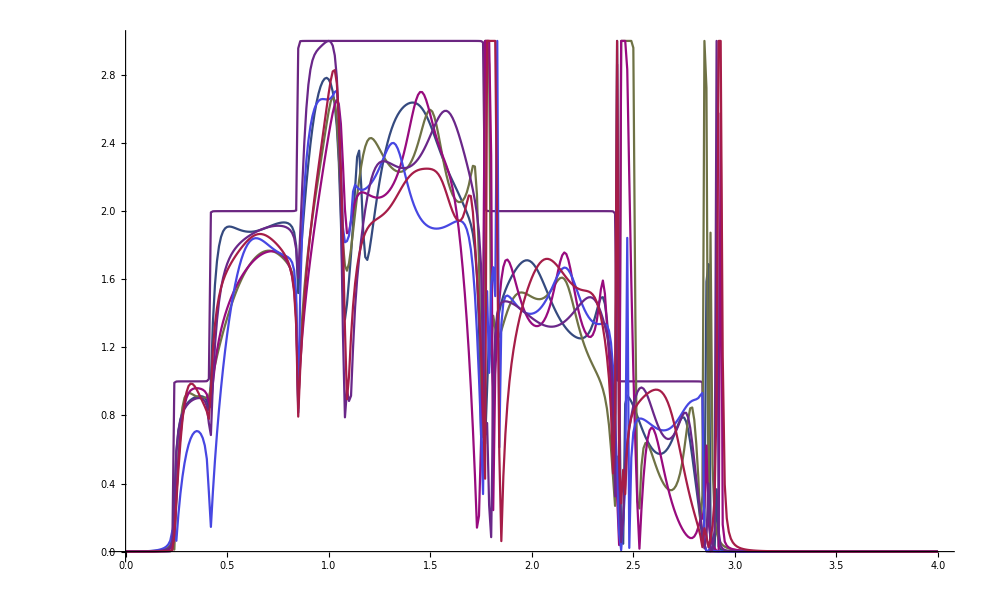

```mathematica
Show[ListPlot[m1,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[m2,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[o3,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[p4,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[q5,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[r6,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[n7,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]]]
```

```mathematica
n:=(n1+n2+n3+n4+n5+n6+n7+n8)/8
```

```mathematica
o:=(o1+o2+o3+o4+o5+o6+o7+o8)/8
```

```mathematica
p:=(p1+p2+p3+p4+p5+p6+p7+p8)/8
```

```mathematica
q:=(q1+q2+q3+q4+q5+q6+q7+q8)/8
```

```mathematica
r:=(r1+r2+r3+r4+r5+r6+r7+r8)/8
```

```mathematica
final:=(m+n+o+p+q+r)/6
```

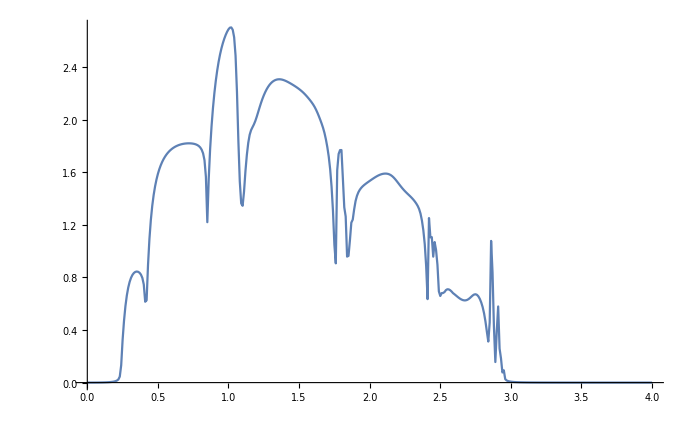

```mathematica
ListPlot[final,Joined->True]
```

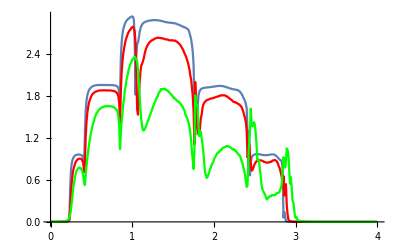

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis43.csv"]],ListLinePlot[Import["4imp5.csv"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis410.csv"],PlotStyle->Green]]
```

```mathematica
final1:=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis410.csv"]
```

```mathematica
f3=Module[{B1=Transpose[{final1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]
```

0.00233348

```mathematica
ScientificForm[f3]
```

1.02031×10^-4

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis43.csv",final3]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis43.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis44.csv",final4]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis44.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis45.csv",final5]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis45.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis46.csv",final6]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis46.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis47.csv",final7]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis47.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis48.csv",final8]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis48.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis49.csv",final9]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis49.csv

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis410.csv",final10]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis410.csv

```mathematica
G[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[{{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ3+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ2+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ3+ω,-t},{0,0,0,0,0,-t,ⅈ δ+ω-ϵ}}]
```

```mathematica
Gnew[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Inverse[IdentityMatrix[7]-G[ω,δ,t,ϵ,ϵ2,ϵ3].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].G[ω,δ,t,ϵ,ϵ2,ϵ3]
```

```mathematica
Ilb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[IdentityMatrix[7]-Gnew[ω,δ,t,ϵ,ϵ2,ϵ3].T1[t].SR[ω,δ,t,ϵ].T1[t]].Gnew[ω,δ,t,ϵ,ϵ2,ϵ3];
Irb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Gnew[ω,δ,t,ϵ,ϵ2,ϵ3].T1[t]].SR[ω,δ,t,ϵ];
gddb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
grrb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Irb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Irb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
Gnonlocalb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= SR[ω,δ,t,ϵ].T1[t].Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3];
GNONb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Gnonlocalb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Gnonlocalb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
trb[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= If[Abs[Tr[gddb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].grrb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1]-T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3]]]>3,3,Abs[Tr[gddb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].grrb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1]-T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3]]]]
```

```mathematica
f[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{final[[1;;150]][[;;,1]],(Table[{ω,trb[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- final[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.49}]/150]
```

```mathematica
ρ3[b_]:=Table[{b,a,f[b,a]},{a,Range[-1,1,0.05]}]
```

```mathematica
ρ3[0]
```

```mathematica
rr3=Join[ρ3[-1],ρ3[-9/10],ρ3[-4/5],ρ3[-7/10],ρ3[-3/5],ρ3[-1/2],ρ3[-2/5],ρ3[-3/10],ρ3[-1/5],ρ3[-1/10],ρ3[0],ρ3[1/10],ρ3[1/5],ρ3[3/10],ρ3[2/5],ρ3[1/2],ρ3[3/5],ρ3[7/10],ρ3[4/5],ρ3[9/10],ρ3[1]]
```

```mathematica
{Min/@Transpose[rr3]}[[1,3]]
```

```mathematica
Extract[Transpose[rr3],{{1,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]},{2,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]}}]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
μ1
```

4

```mathematica
μ5
```

2

```mathematica
μ8
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
m2[ϵ1_]:=ListLinePlot[Table[{ω,If[ψ[ω,0.001,1,0,ϵ1]>3,3,ψ[ω,0.001,1,0,ϵ1]]},{ω,Range[0,4,0.01]}],PlotStyle->RGBColor[RandomReal[{0,1}],0.2,RandomReal[{0,1}],1]]
```

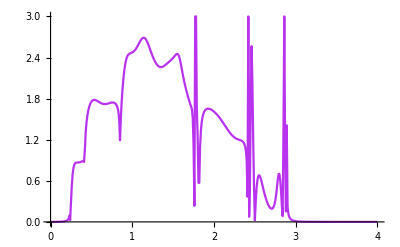

```mathematica
m2[0.7]
```

```mathematica
Clear[imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,θ,Sl111,Sl112,Sl113,Sl114,Sl115,Sl116,Sl117,Sl118,gdd11,grr11,Il11,Ir11,Gnonlocal11,GNON11];
```

```mathematica
imp11[ω_,ϵ1_,μ1_]:= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp12[ω_,ϵ1_,μ2_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001]]];imp13[ω_,ϵ1_,μ3_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp14[ω_,ϵ1_,μ4_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp15[ω_,ϵ1_,μ5_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-0]]];imp16[ω_,ϵ1_,μ6_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp17[ω_,ϵ1_,μ7_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp18[ω_,ϵ1_,μ8_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];θ[ω_,ϵ1_,μ1_,μ2_,μ3_,μ4_,μ5_,μ6_,μ7_,μ8_]:=θ[ω,ϵ1,μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl111:=Inverse[IdentityMatrix[7]-imp11[ω,ϵ1,μ1].T1[1].SL[ω,0.001,1,0].T1[1]].imp11[ω,ϵ1,μ1];
Sl112:=Inverse[IdentityMatrix[7]-imp12[ω,ϵ1,μ2].T2[1].Sl111.T2[1]].imp12[ω,ϵ1,μ2];
Sl113:=Inverse[IdentityMatrix[7]-imp13[ω,ϵ1,μ3].T1[1].Sl112.T1[1]].imp13[ω,ϵ1,μ3];
Sl114:=Inverse[IdentityMatrix[7]-imp14[ω,ϵ1,μ4].T2[1].Sl113.T2[1]].imp14[ω,ϵ1,μ4];
Sl115:=Inverse[IdentityMatrix[7]-imp15[ω,ϵ1,μ5].T1[1].Sl114.T1[1]].imp15[ω,ϵ1,μ5];
Sl116:=Inverse[IdentityMatrix[7]-imp16[ω,ϵ1,μ6].T2[1].Sl115.T2[1]].imp16[ω,ϵ1,μ6];
Sl117:=Inverse[IdentityMatrix[7]-imp17[ω,ϵ1,μ7].T1[1].Sl116.T1[1]].imp17[ω,ϵ1,μ7];
Sl118:=Inverse[IdentityMatrix[7]-imp18[ω,ϵ1,μ8].T2[1].Sl117.T2[1]].imp18[ω,ϵ1,μ8];
Il11:=Inverse[IdentityMatrix[7]-Sl118.T1[1].SR[ω,0.001,1,0].T1[1]].Sl118;
Ir11:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].Sl118.T1[1]].SR[ω,0.001,1,0];
gdd11:= Il11-ConjugateTranspose[Il11];
grr11:= Ir11-ConjugateTranspose[Ir11];
Gnonlocal11:= SR[ω,0.001,1,0].T1[1].Il11;
GNON11:= Gnonlocal11-ConjugateTranspose[Gnonlocal11];
Abs[Tr[gdd11.T1[1].grr11.T1[1]-T1[1].GNON11.T1[1].GNON11]]]
```

```mathematica
ρ[μ1_,μ4_,μ8_]:=ListLinePlot[Table[{ω,θ[ω,0.7,μ1,1,1,μ4,1,1,1,μ8]},{ω,Range[0,4,0.01]}]]
```

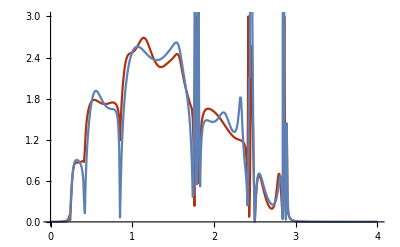

```mathematica
Show[m2[0.7],ρ[2,4,2]]
```

```mathematica
Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]
```

0.00052043

```mathematica
f[i_]=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]
```

0.00140358

```mathematica
Transpose[{Range[48]}]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}}
```

{{1,0.00157127},{2,0.00209697},{3,0.00300904},{4,0.00225823},{5,0.00370393},{6,0.00284866},{7,0.00222567},{8,0.00235583},{9.,0.00450452},{10,0.00190144},{11,0.00316979},{12,0.00201725},{13,0.00303296},{14,0.00326688},{15,0.00186687},{16,0.00261571},{17,0.00455937},{18,0.00183717},{19,0.00192058},{20,0.00432659},{21,0.00149537},{22,0.00180827},{23,0.00167831},{24,0.00358578},{25,0.00337138},{26,0.00243373},{27,0.00214812},{28,0.00183435},{29,0.00186627},{30,0.00233593},{31,0.00145384},{32,0.00355923},{33,0.00212118},{34,0.00188666},{35,0.00383785},{36,0.0027615},{37,0.00249181},{38,0.00270975},{39,0.00177799},{40,0.00183239},{41,0.00237735},{42,0.0040428},{43,0.00105771},{44,0.00461221},{45,0.00359324},{46,0.00306259},{47,0.00384129},{48,0.00351994}}

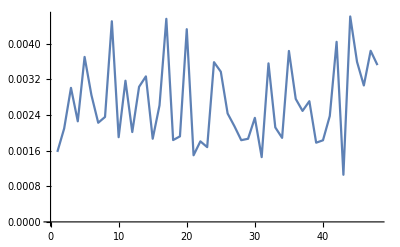

```mathematica
ListPlot[%223,Joined->True]
```

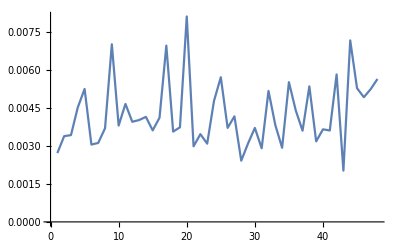

```mathematica
ListPlot[%220,Joined->True]
```

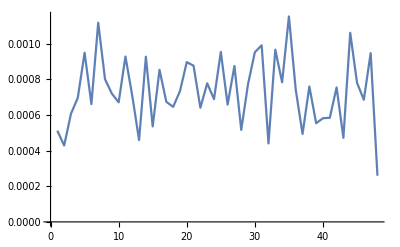

```mathematica
ListPlot[%1159,Joined->True]
```

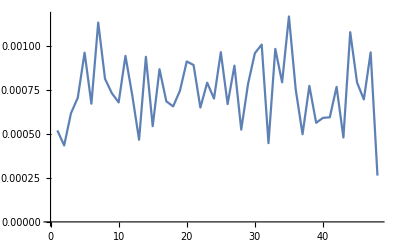

```mathematica
ListPlot[%1156,Joined->True]
```

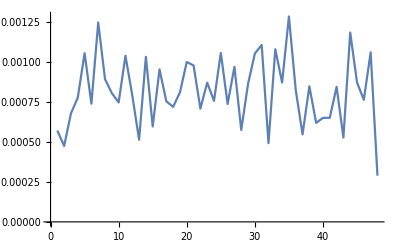

```mathematica
ListPlot[%1152,Joined->True]
```

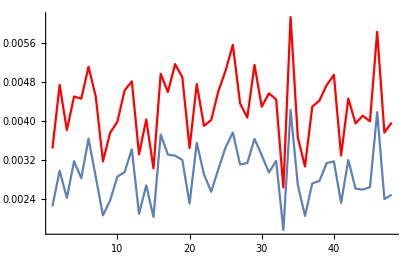

```mathematica
Show[%819,%996,PlotRange->All]
```

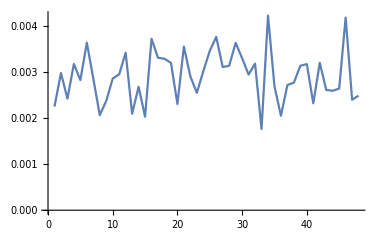

```mathematica
ListPlot[%818,Joined->True]
```

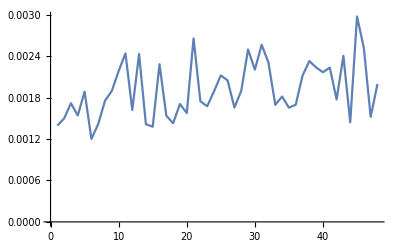

```mathematica
ListPlot[%637,Joined->True]
```

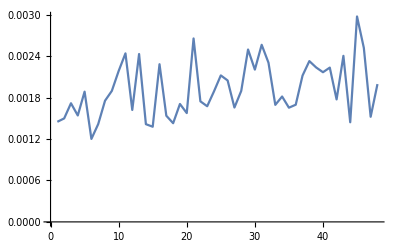

```mathematica
ListPlot[%602,Joined->True]
```

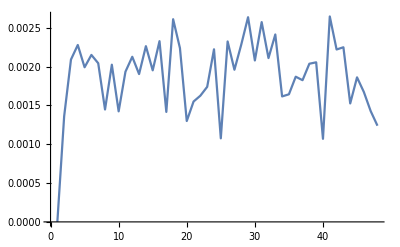

```mathematica
ListPlot[%441,Joined->True]
```

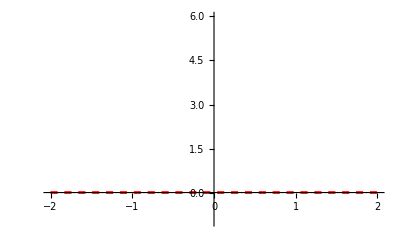

```mathematica
Plot[{0.0015,0},{x,-2,2},Epilog->{Blue,PointSize@Large,Point[{100,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}]},PlotStyle->{{Red,Dashed,Thickness[0.004]},{Red,Dashed,Thickness[0.004]}},PlotRange->{-1,6}]
```

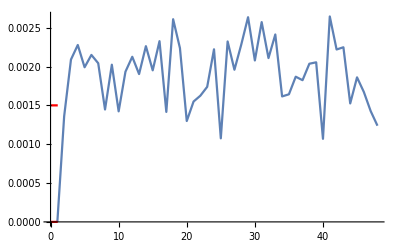

```mathematica
Show[%442,%448]
```

```mathematica
Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]
```

$Aborted[]

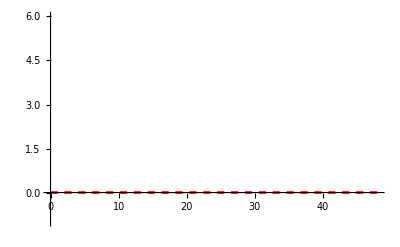

```mathematica
p=Plot[{Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91],0},{x,0,48},PlotStyle->{{Red,Dashed,Thickness[0.004]},{Red,Dashed,Thickness[0.004]}},PlotRange->{-1,6}]
```

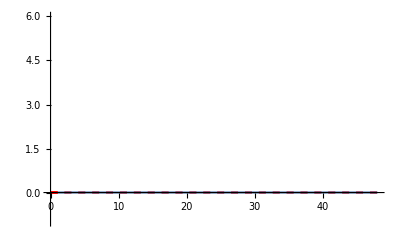

$Aborted

```mathematica
Show[p,%449]
```

```mathematica
{{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{2,1.4226},{3,1.73026},{4,1.47079},{5,1.80616},{6,1.63032},{7,1.86823},{8,1.58526},{9,1.58128},{10,1.49721},{11,1.43308},{12,1.8448},{13,1.23321},{14,1.56651},{15,1.86142},{16,1.60439},{17,1.78091},{18,1.69138},{19,1.36786},{20,1.28119},{21,1.60669},{22,1.61165},{23,1.71252},{24,1.76303},{25,1.68612},{26,1.54085},{27,1.16604},{28,1.75127},{29,1.04157},{30,1.43599},{31,1.14792},{32,1.56788},{33,1.03086},{34,1.12626},{35,1.87044},{36,1.8492},{37,1.73856},{38,1.77977},{39,1.28747},{40,1.88365},{41,1.79229},{42,0.940966},{43,1.15354},{44,1.26603},{45,1.65568},{46,1.52005},{47,1.5677},{48,1.74385}}

```mathematica
{Max[{Min/@%1170}],Min[{Min/@%1170}],final[[51,2]]}
```

{1.88365,0.940966,1.54457}

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}}
```

{{1,0.009161},{2,0.00748745},{3,0.00843967},{4,0.0091458},{5,0.0113812},{6,0.012356},{7,0.0107017},{8,0.00915179},{9.,0.00770868},{10,0.0100119},{11,0.00991015},{12,0.00771397},{13,0.0101937},{14,0.0115014},{15,0.0115305},{16,0.00613636},{17,0.00789518},{18,0.0110542},{19,0.0123203},{20,0.00664235},{21,0.0113299},{22,0.0105255},{23,0.00951097},{24,0.010971},{25,0.0122171},{26,0.0108602},{27,0.00871688},{28,0.0108206},{29,0.0115143},{30,0.00805892},{31,0.00967219},{32,0.00783435},{33,0.00973873},{34,0.0093259},{35,0.0111626},{36,0.00784443},{37,0.0131277},{38,0.0126015},{39,0.0105158},{40,0.0115055},{41,0.00754247},{42,0.00922941},{43,0.0126621},{44,0.00942612},{45,0.00887334},{46,0.00810637},{47,0.0104862},{48,0.00968924}}

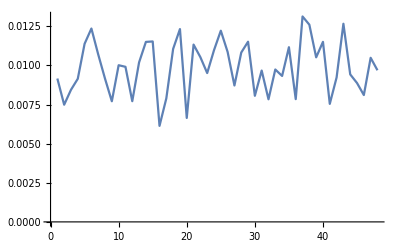

```mathematica
ListPlot[%225,Joined->True]
```

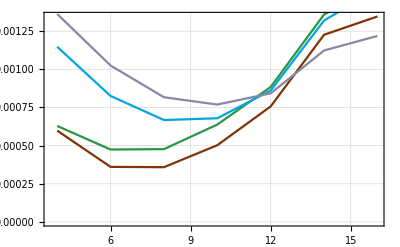

```mathematica
Show[ListLinePlot[{{4,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n1[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n1[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n1[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n1[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n1[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q6[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q6[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q6[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q6[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q6[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q6[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q6[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]]
```

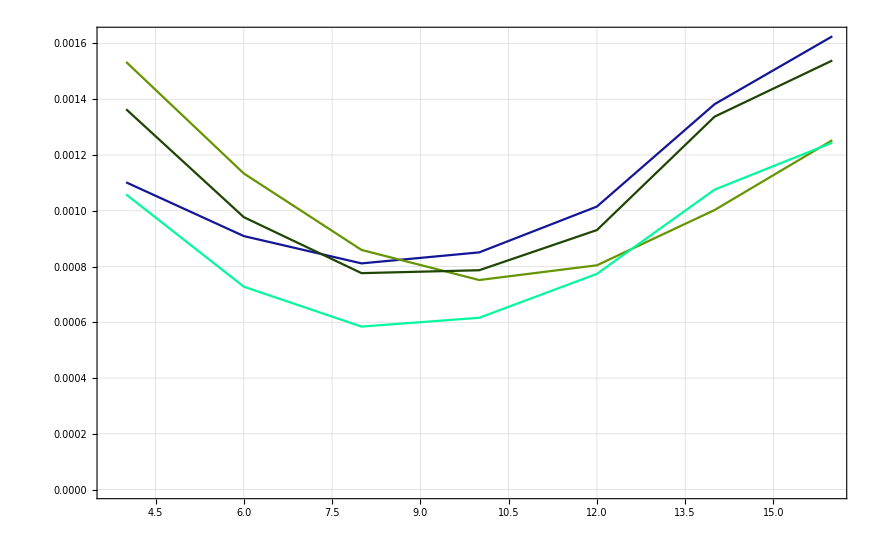

-Graphics-

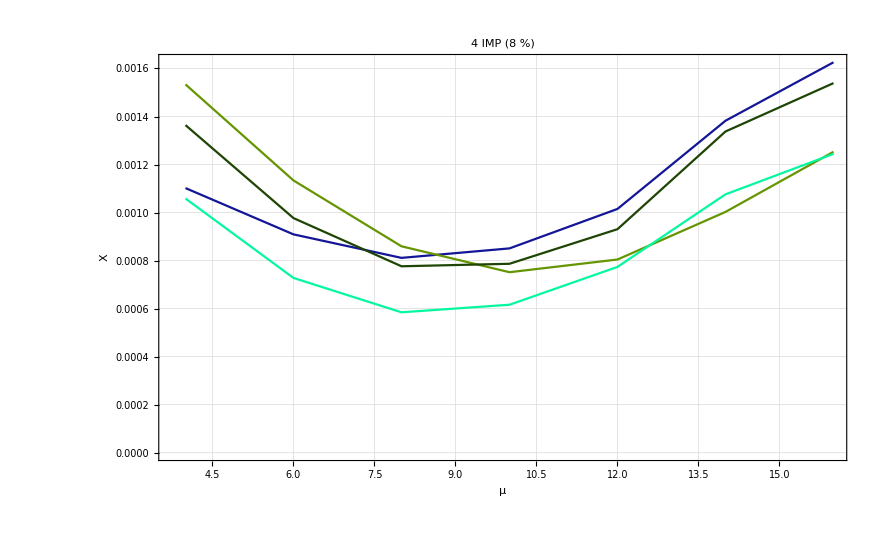

```mathematica
Show[%182,FrameLabel->{{HoldForm[Χ],None},{HoldForm[μ],None}},PlotLabel->HoldForm[4 IMP (8 %)],LabelStyle->{GrayLevel[0]}]
```

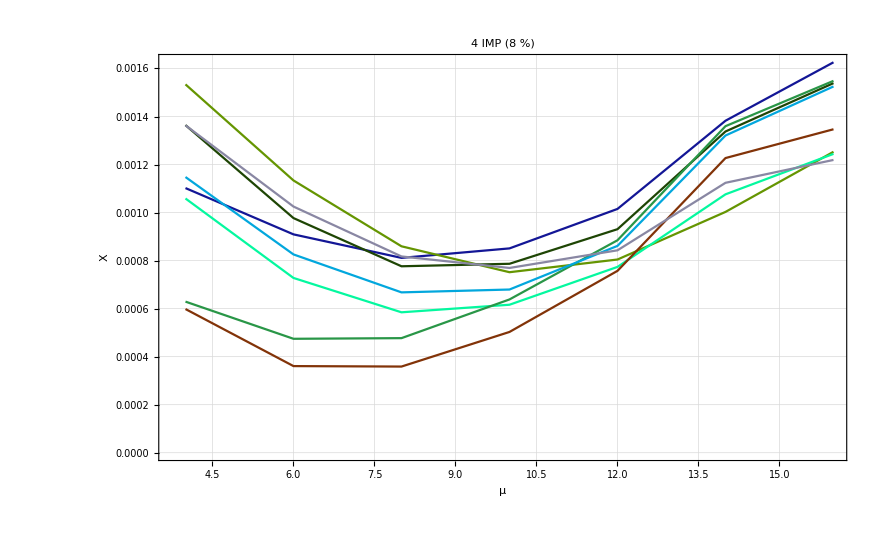

```mathematica
Show[%183,%187]
```